# Just launch the code below to run the notebook

```mathematica
ClearAll["Global`*"]
FrontEndTokenExecute["SelectAll"]
FrontEndTokenExecute["SelectionCloseAllGroups"]
nb=EvaluationNotebook[];
NotebookFind[nb,"Evaluation",All,CellTags];
SelectionEvaluate[nb]
```

# I. Definitions

## Creating relevant directories

```mathematica
SetDirectory[NotebookDirectory[]];
If[(DirectoryQ["spectra"]//ToString)=="False",CreateDirectory["spectra"]]
If[(DirectoryQ["spectra/New physics particles spectra"]//ToString)=="False",CreateDirectory["spectra/New physics particles spectra"]]
If[(DirectoryQ["spectra/New physics particles spectra/HNLs"]//ToString)=="False",CreateDirectory["spectra/New physics particles spectra/HNLs"]]
If[(DirectoryQ["spectra/New physics particles spectra/B-L"]//ToString)=="False",CreateDirectory["spectra/New physics particles spectra/B-L"]]
If[(DirectoryQ["spectra/New physics particles spectra/Scalars"]//ToString)=="False",CreateDirectory["spectra/New physics particles spectra/Scalars"]]
If[(DirectoryQ["spectra/New physics particles spectra/Dark photons"]//ToString)=="False",CreateDirectory["spectra/New physics particles spectra/Dark photons"]]
If[(DirectoryQ["spectra/New physics particles spectra/ALPs with photon coupling"]//ToString)=="False",CreateDirectory["spectra/New physics particles spectra/ALPs with photon coupling"]]
If[(DirectoryQ["spectra/New physics particles spectra/ALPs with gluon coupling"]//ToString)=="False",CreateDirectory["spectra/New physics particles spectra/ALPs with gluon coupling"]]
If[(DirectoryQ["spectra/New physics particles spectra/ALPs with fermion coupling"]//ToString)=="False",CreateDirectory["spectra/New physics particles spectra/ALPs with fermion coupling"]]
If[(DirectoryQ["spectra/New physics particles spectra/MCPs"]//ToString)=="False",CreateDirectory["spectra/New physics particles spectra/MCPs"]]
```

## Parameters

## Conversion units

```mathematica
GeVm2Topb=(2*10^-16)^2*10^28*10^12.;
GeVm2Tob=(2*10^-16)^2*10^28;
```

## Kinematics at various beam dump facilities

```mathematica
EpSPS=400;
EpFermilabBD=120;
EpLHC=6500;
EpFCChh=50000;
vCMbeamDump[Eplab_,MP_]=v/.Solve[√(Eplab^2-MP^2)-Eplab*v==MP*v,v][[1]];
γCMbeamDump[Eplab_,MP_]=1/(√(1-vCMbeamDump[Eplab,MP]^2))//Simplify;
```

## Masses and other parameters of SM particles

```mathematica
(*SetDirectory["/Users/miksi/AppData/Roaming/Mathematica/Applications/FeynCalc"];*)
<<FeynCalc`
mB=5.3;
mBc=6.3;
mDstar=2.;
mDs=1.97;
mDplus=1.87;
mBs=5.366;
mτ=1.77;
mK=0.495;
mμ=0.105;
mτ=1.77;
MW=80;
me=0.5*10^-3;
mπ=0.14;
mπ0=0.135;
mη=0.547;
mηpr=0.958;
mh=125.;
mρ0=0.775;
mω=0.78;
mϕ=1.02;
mJψ=3.1;
mΥ=9.46;
(*Parameters of nuclei*)
{mMo,AMo,ZMo}={89.38,96,42};
{mC,AC,ZC}={11.188,12,6};
{mFe,AFe,ZFe}={54.43,56.,28};
(*Br ratios of EM decays of light mesons*)
BrπToγγ=0.98799;
BrηToγγ=0.3931181;
(*Some useful definitions*)
mlMixing:=Association[{"e"->0.5*10^-3,"μ"-> 0.105,"τ"->1.77}]
MV=Association[{Kplus->0.892 ,Dplus->2.01,D0->2.01,Ds->2.11,Bplus->5.32,B0->5.32,Bs->5.415,Bc->6.33}];
fH=Association[{piplus-> 0.13,Kplus-> 0.156,Dplus-> 0.212,Ds-> 0.249,Bplus-> 0.187,Bs-> 0.227,B0-> 0.191,Bc-> 0.48}];
MH=Association[{piplus-> 0.1396,pi0->0.135 ,Kplus-> 0.494,K0->0.498,eta-> 0.548,rho0->0.775,rhoplus->0.775,Dplus-> 1.87,D0-> 1.865,Ds-> 1.97,Dsstar-> 2.11,etac->2.98 ,Bplus-> 5.28,B0->5.28 ,Bs-> 5.37,Bc->6.28,Dplusstar->2.01,D0star->2.007, Kplusstar->0.892,K0star->0.892}];
MV=Association[{Kplus->0.892 ,Dplus->2.01,D0->2.01,Ds->2.11,Bplus->5.32,B0->5.32,Bs->5.415,Bc->6.33}];
MS=Association[{Kplus-> 1.43,Dplus->2.4,D0->2.4,Ds->2.32,Bplus->5.68,B0->5.68,Bs->5.68,Bc->6.42}];
```

FeynCalc is already loaded! If you are trying to reload FeynCalc or load FeynArts, TARCER, PHI, FeynHelpers or any other add-on, please restart the kernel.

$Aborted

## Mass-angle grid for the distribution function

```mathematica
ENlistSPS=Join[Table[10^EN,{EN,Log10[0.02],Log10[350],0.05}],{350}];
θNlistSPS=Join[{10^-5.,3*10^-5.,6*10^-5.,10^-4.,3*10^-4.,6*10^-4.,10^-3.,2*10^-3.,4*10^-3.,6*10^-3.,8*10^-3.},Table[10^θN,{θN,Log10[10^-2],Log10[0.8],0.05}],{0.85}]
θNlistSPSB=Join[{10^-5.,3*10^-5.,6*10^-5.,10^-4.,3*10^-4.,6*10^-4.,10^-3.,2*10^-3.,4*10^-3.,6*10^-3.,8*10^-3.},Table[10^θN,{θN,Log10[10^-2],Log10[0.8],0.03}],{0.85}]
ENlistLHC=Join[Table[10^EN,{EN,Log10[0.01],Log10[0.95EpLHC],0.04}],{0.97EpLHC,EpLHC}];
ENlistFCChh=Join[Table[10^EN,{EN,Log10[0.01],Log10[0.95EpFCChh],0.04}],{0.97EpFCChh,EpFCChh}];
θNlistLHCtemp=Join[{10^-5.,3*10^-5.,6*10^-5.,10^-4.,3*10^-4.,6*10^-4.,10^-3.,2*10^-3.,4*10^-3.,6*10^-3.,8*10^-3.},Table[10^θN,{θN,Log10[10^-2],Log10[0.5],0.025}],Table[10^θN,{θN,Log10[0.52],Log10[1.55],0.015}],{1.57}];
θNlistLHC=SortBy[Partition[Join[θNlistLHCtemp,Pi-θNlistLHCtemp],1],1]//Flatten
θNlistFCChhtemp=θNlistLHCtemp;
θNlistFCChh=SortBy[Partition[Join[θNlistFCChhtemp,Pi-θNlistFCChhtemp],1],1]//Flatten
ENlistFermilabBD=Join[Table[10^EN,{EN,Log10[0.01],Log10[120],0.05}]];
θNlistFermilabBD=Join[{10^-5.,3*10^-5.,6*10^-5.,10^-4.,3*10^-4.,6*10^-4.,10^-3.,2*10^-3.,4*10^-3.,6*10^-3.,8*10^-3.},Table[10^θN,{θN,Log10[10^-2],Log10[0.8],0.05}],{0.85}];
MaxMassHNLsFromB[BcOption_,mixing_]:=If[BcOption=="True",mBc-mlMixing[mixing],mB-mlMixing[mixing]]
MaxMassHNLsFromD[mixing_]:=If[mixing=="e"||mixing=="μ",mDs-mlMixing[mixing],mτ-mlMixing["e"]]
EFIPfromKlistSPS={0.02,0.05,0.1,0.25,0.5,1.,1.5,2.,2.5,3.,3.5,4.,5.,6.,7.,8.};
```

{0.00001,0.00003,0.00006,0.0001,0.0003,0.0006,0.001,0.002,0.004,0.006,0.008,0.01,0.0112202,0.0125893,0.0141254,0.0158489,0.0177828,0.0199526,0.0223872,0.0251189,0.0281838,0.0316228,0.0354813,0.0398107,0.0446684,0.0501187,0.0562341,0.0630957,0.0707946,0.0794328,0.0891251,0.1,0.112202,0.125893,0.141254,0.158489,0.177828,0.199526,0.223872,0.251189,0.281838,0.316228,0.354813,0.398107,0.446684,0.501187,0.562341,0.630957,0.707946,0.794328,0.85}

{0.00001,0.00003,0.00006,0.0001,0.0003,0.0006,0.001,0.002,0.004,0.006,0.008,0.01,0.0107152,0.0114815,0.0123027,0.0131826,0.0141254,0.0151356,0.0162181,0.017378,0.0186209,0.0199526,0.0213796,0.0229087,0.0245471,0.0263027,0.0281838,0.0301995,0.0323594,0.0346737,0.0371535,0.0398107,0.042658,0.0457088,0.0489779,0.0524807,0.0562341,0.060256,0.0645654,0.0691831,0.074131,0.0794328,0.0851138,0.0912011,0.0977237,0.104713,0.112202,0.120226,0.128825,0.138038,0.147911,0.158489,0.169824,0.18197,0.194984,0.20893,0.223872,0.239883,0.25704,0.275423,0.295121,0.316228,0.338844,0.363078,0.389045,0.416869,0.446684,0.47863,0.512861,0.549541,0.588844,0.630957,0.676083,0.724436,0.776247,0.85}

{0.00001,0.00003,0.00006,0.0001,0.0003,0.0006,0.001,0.002,0.004,0.006,0.008,0.01,0.0105925,0.0112202,0.011885,0.0125893,0.0133352,0.0141254,0.0149624,0.0158489,0.016788,0.0177828,0.0188365,0.0199526,0.0211349,0.0223872,0.0237137,0.0251189,0.0266073,0.0281838,0.0298538,0.0316228,0.0334965,0.0354813,0.0375837,0.0398107,0.0421697,0.0446684,0.0473151,0.0501187,0.0530884,0.0562341,0.0595662,0.0630957,0.0668344,0.0707946,0.0749894,0.0794328,0.0841395,0.0891251,0.0944061,0.1,0.105925,0.112202,0.11885,0.125893,0.133352,0.141254,0.149624,0.158489,0.16788,0.177828,0.188365,0.199526,0.211349,0.223872,0.237137,0.251189,0.266073,0.281838,0.298538,0.316228,0.334965,0.354813,0.375837,0.398107,0.421697,0.446684,0.473151,0.52,0.538274,0.55719,0.576771,0.59704,0.618021,0.63974,0.662222,0.685494,0.709583,0.73452,0.760332,0.787052,0.814711,0.843341,0.872978,0.903656,0.935413,0.968285,1.00231,1.03754,1.074,1.11174,1.15081,1.19125,1.23311,1.27645,1.32131,1.36774,1.4158,1.46556,1.51706,1.57,1.57159,1.62453,1.67603,1.72579,1.77385,1.82029,1.86514,1.90848,1.95034,1.99078,2.02985,2.06759,2.10406,2.13928,2.17331,2.20618,2.23794,2.26861,2.29825,2.32688,2.35454,2.38126,2.40707,2.43201,2.4561,2.47937,2.50185,2.52357,2.54455,2.56482,2.5844,2.60332,2.62159,2.66844,2.69491,2.7199,2.74349,2.76576,2.78678,2.80663,2.82536,2.84305,2.85975,2.87552,2.8904,2.90446,2.91772,2.93024,2.94207,2.95323,2.96376,2.97371,2.9831,2.99197,3.00034,3.00824,3.0157,3.02274,3.02939,3.03567,3.04159,3.04719,3.05247,3.05745,3.06216,3.0666,3.0708,3.07476,3.0785,3.08203,3.08536,3.0885,3.09147,3.09428,3.09692,3.09942,3.10178,3.10401,3.10611,3.1081,3.10997,3.11174,3.11341,3.11499,3.11647,3.11788,3.11921,3.12046,3.12164,3.12276,3.12381,3.1248,3.12574,3.12663,3.12747,3.12826,3.129,3.12971,3.13037,3.131,3.13159,3.13359,3.13559,3.13759,3.13959,3.14059,3.14099,3.14129,3.14149,3.14153,3.14156,3.14158}

{0.00001,0.00003,0.00006,0.0001,0.0003,0.0006,0.001,0.002,0.004,0.006,0.008,0.01,0.0105925,0.0112202,0.011885,0.0125893,0.0133352,0.0141254,0.0149624,0.0158489,0.016788,0.0177828,0.0188365,0.0199526,0.0211349,0.0223872,0.0237137,0.0251189,0.0266073,0.0281838,0.0298538,0.0316228,0.0334965,0.0354813,0.0375837,0.0398107,0.0421697,0.0446684,0.0473151,0.0501187,0.0530884,0.0562341,0.0595662,0.0630957,0.0668344,0.0707946,0.0749894,0.0794328,0.0841395,0.0891251,0.0944061,0.1,0.105925,0.112202,0.11885,0.125893,0.133352,0.141254,0.149624,0.158489,0.16788,0.177828,0.188365,0.199526,0.211349,0.223872,0.237137,0.251189,0.266073,0.281838,0.298538,0.316228,0.334965,0.354813,0.375837,0.398107,0.421697,0.446684,0.473151,0.52,0.538274,0.55719,0.576771,0.59704,0.618021,0.63974,0.662222,0.685494,0.709583,0.73452,0.760332,0.787052,0.814711,0.843341,0.872978,0.903656,0.935413,0.968285,1.00231,1.03754,1.074,1.11174,1.15081,1.19125,1.23311,1.27645,1.32131,1.36774,1.4158,1.46556,1.51706,1.57,1.57159,1.62453,1.67603,1.72579,1.77385,1.82029,1.86514,1.90848,1.95034,1.99078,2.02985,2.06759,2.10406,2.13928,2.17331,2.20618,2.23794,2.26861,2.29825,2.32688,2.35454,2.38126,2.40707,2.43201,2.4561,2.47937,2.50185,2.52357,2.54455,2.56482,2.5844,2.60332,2.62159,2.66844,2.69491,2.7199,2.74349,2.76576,2.78678,2.80663,2.82536,2.84305,2.85975,2.87552,2.8904,2.90446,2.91772,2.93024,2.94207,2.95323,2.96376,2.97371,2.9831,2.99197,3.00034,3.00824,3.0157,3.02274,3.02939,3.03567,3.04159,3.04719,3.05247,3.05745,3.06216,3.0666,3.0708,3.07476,3.0785,3.08203,3.08536,3.0885,3.09147,3.09428,3.09692,3.09942,3.10178,3.10401,3.10611,3.1081,3.10997,3.11174,3.11341,3.11499,3.11647,3.11788,3.11921,3.12046,3.12164,3.12276,3.12381,3.1248,3.12574,3.12663,3.12747,3.12826,3.129,3.12971,3.13037,3.131,3.13159,3.13359,3.13559,3.13759,3.13959,3.14059,3.14099,3.14129,3.14149,3.14153,3.14156,3.14158}

## Fragmentation fractions of mesons

### LHC and FCC-hh

```mathematica
(*Fragmentation fractions*)
fdstau = 0.0543;
fctod0LHC=fctod0FCChh=0.553;
fctodplusLHC=fctodplusFCChh = 0.225;
(*Subscript[D, s] mesons - including Subscript[D, s]^* contribution*)
fctodsLHC=fctodsFCChh=0.105;
fbtobcLHC=fbtobcFCChh= 2.6*10^-3;
fbtob0LHC=fbtobplusLHC=fbtob0FCChh=fbtobplusFCChh=0.324;
```

### SPS

```mathematica
fctod0SPS = 0.632;
fctodplusSPS=0.207;
fctodsSPS=0.088;
fbtobplusSPS=0.4;
fbtob0SPS=0.4;
NccbarSHiP = 2.3*3.4*10^17;
NbbbarSHiP = 1.7*3.2*10^13;
NpotSHiP=2*10^20;
χbbbarSPS=NbbbarSHiP/NpotSHiP;
χccbarSPS=NccbarSHiP/NpotSHiP;
χssbarSPS=1/7;
```

### FermilabBD (assumed to be the same as at SPS; to be fixed)

```mathematica
fctod0FermilabBD= 0.632;
fctodplusFermilabBD=0.207;
fctodsFermilabBD=0.088;
fbtobplusFermilabBD=0.4;
fbtob0FermilabBD=0.4;
```

## Coherent EM processes

## EM elastic form factors

```mathematica
(*Helm*)
svalfm=0.9;
fmtoGeVm1=5;
(*Effective radius of the nucleus*)
R1[Anucleus_]=fmtoGeVm1 √((1.23*Anucleus^(1/3)-0.6)^2+7/3 Pi^2*0.52^2-5*svalfm^2);
FHelm[q2_,Anucleus_,Znucleus_]=3*Znucleus*SphericalBesselJ[1,√q2*R1[Anucleus]]/(√q2*R1[Anucleus])Exp[-(q2*(svalfm*fmtoGeVm1)^2)/2];
(*Proton*)
mp=0.938;
αEMval=1/137;
GE[q2_]=1/((1+q2/0.843^2)^2);
GM[q2_]=(√7.78)/((1+q2/0.843^2)^2);
F1[q2_]=(4*mp^2*GE[q2]+q2*GM[q2])/(4*mp^2+q2);
F2[q2_]=(GM[q2]-GE[q2])/(4*mp^2+q2);
Dval[q2_]=(4*mp^2*GE[q2]^2+q2*GM[q2]^2)/(4*mp^2+q2);
```

## Equivalent photon distribution functions

```mathematica
(*Magnitude of the momentum transfer between particle and photon*)
q2pTxVal[x_,pT_,m_]=(pT^2+x^2*m^2)/(1-x);
fEPAp[pT_,x_,αEM_]=αEM/(2*Pi)(1+(1-x)^2)/x(pT^2/((pT^2+x^2*mp^2)^2)Dval[q2pTxVal[x,pT,mp]]+x^2/2 GM[q2pTxVal[x,pT,mp]]^2);
fEPAnucleus[pT_,x_,αEM_,mNucleus_,Anucleus_,Znucleus_]=αEM/(2*Pi)(1+(1-x)^2)/x(pT^2/((pT^2+x^2*mNucleus^2)^2)FHelm[q2pTxVal[x,pT,mNucleus],Anucleus,Znucleus]^2);
```

## Working with mother particles distributions

```mathematica
NormValsX[[-1]]
```

2.84053×10^126

```mathematica
NormValsX
```

{0.0143555,0.045683,0.0937772,0.284663,0.382528,0.133669,0.0331438,0.00585732,0.000718612,2.84053×10^126}

## Finding maximal energy for the given polar angle

```mathematica
eMotherMax[distr_,mothermass_,EmaxVal_,θlist_,LogMin_]:=Module[{EXmaxval,θXlist,mX,ΔEXval},
EXminval=mothermass;
EXmaxval=EmaxVal;
θXlist=θlist;
mX=mothermass;
ΔEXval=If[EXmaxval<10.,(Log10[EXmaxval]-Log10[mX])/20.,If[EXmaxval<150,(Log10[EXmaxval]-Log10[mX])/50.,If[EXmaxval<500,(Log10[EXmaxval]-Log10[mX])/70.,If[EXmaxval<10000,(Log10[EXmaxval]-Log10[mX])/150.,(Log10[EXmaxval]-Log10[mX])/200.]]]];
DoubleDistrIntList[i_]:=Interpolation[ParallelTable[{EX,Quiet[NIntegrate[distr[θX,EX],{θX,θXlist[[i]],θXlist[[i+1]]},Method->"AdaptiveMonteCarlo"]]},{EX,Table[10^x,{x,Log10[EXminval],Log10[EXmaxval],ΔEXval}]}],InterpolationOrder->1][EX];
θXdistrlist[EX_]=Table[{(θXlist[[i]]+θXlist[[i+1]])/2,DoubleDistrIntList[i]},{i,1,Length[θXlist]-1,1}];
θEmaxList=Table[{θXdistrlist[EX][[i]][[1]],SortBy[Table[{EX,θXdistrlist[EX][[i]][[2]]},{EX,mX,EXmaxval,1}],-#[[2]]&][[1]][[1]]},{i,1,Length[θXdistrlist[EX]],1}];
θEmaxListInt[θX_]=Interpolation[θEmaxList,InterpolationOrder->1][θX];
NormValsX=Table[NIntegrate[θXdistrlist[EX][[i]][[2]]+10^-90.,{EX,mX,EXmaxval},Method->"InterpolationPointsSubdivision"],{i,1,Length[θXdistrlist[EX]],1}];
cdfX[eX_,i_]:=1-1/NormValsX[[i]] NIntegrate[θXdistrlist[EX][[i]][[2]],{EX,mX,eX},Method->"InterpolationPointsSubdivision"];
cdftabX[EX_]=Table[{θXdistrlist[EX][[i]][[1]],Interpolation[ParallelTable[{10^eX,cdfX[10^eX,i]},{eX,Log10[EXminval],Log10[EXmaxval],0.1}],InterpolationOrder->1][EX]},{i,1,Length[θXdistrlist[EX]],1}];
logmin[θX_]=LogMin;
Estart[θX_]=2*θEmaxListInt[θX];
(*EmaxvX[i_]:=If[NormValsX[[i]]<10^-15,1.2*mX,10^(EX/.FindRoot[Log10[cdftabX[10^EX][[i]][[2]]]==logmin[θEmaxList[[i]][[1]]],{EX,Log10[Estart[θEmaxList[[i]][[1]]]],Log10[θEmaxList[[i]][[2]]],Log10[EXmaxval]}])];*)
EmaxvX[i_]:=Block[{},
tab1=ParallelTable[{10^EX,Quiet[If[cdftabX[10^EX][[i]][[2]]>0,Log10[cdftabX[10^EX][[i]][[2]]],logmin[θEmaxList[[i]][[1]]]]]},{EX,Log10[mothermass],Log10[EXmaxval],(Log10[EXmaxval]-Log10[mothermass])/50}];
minval=tab1[[All,2]]//Min;
If[minval<=logmin[θEmaxList[[i]][[1]]],Select[tab1,#[[2]]<=logmin[θEmaxList[[i]][[1]]]&][[1]][[1]],EXmaxval]
];
tabtempX=Table[{θEmaxList[[i]][[1]],EmaxvX[i]},{i,1,Length[θEmaxList],1}];
(*Clear[θNENmaxListB,θNENmaxListBint,Estart,Emax,EmaxvB];*)
Join[{{10^-5.,EXmaxval},{10^-4.,EXmaxval},{10^-3,EXmaxval}},tabtempX]
]
```

## Producing phase space points of mother particles

```mathematica
MotherDataCompiled=Hold@Compile[{{Events,_Real,2},{ϕrand,_Real,1},{m,_Real}},Table[{√((Events[[i]][[2]])^2-m^2)*Cos[ϕrand[[i]]]*Sin[Events[[i]][[1]]],√((Events[[i]][[2]])^2-m^2)*Sin[ϕrand[[i]]]*Sin[Events[[i]][[1]]],√((Events[[i]][[2]])^2-m^2)*Cos[Events[[i]][[1]]],Events[[i]][[2]],m},{i,1,Length[Events],1}],CompilationTarget->"C",RuntimeOptions->"Speed"]//ReleaseHold;
tabθemax=Hold@Compile[{{Emin,_Real},{Emaxvvv,_Real,1}},Table[RandomReal[{Emin,Emaxvvv[[i]]}],{i,1,Length[Emaxvvv],1}],CompilationTarget->"C",RuntimeOptions->"Speed"]//ReleaseHold
BlockPointsFromSmoothDistribution[Distr_,DataEmaxVsθ_,m_,Emax_,Nevents_,ColliderOption_]:=Module[{θrand,Emaxlist,θminmax,Dataϕ},
Nev=If[ColliderOption=="False",Nevents,IntegerPart[Nevents/2]];
θminmax=MinMax[DataEmaxVsθ[[All,1]]];
θrand=RandomReal[θminmax,Nev];
Emaxlist=Emax[θrand];
Evalsrand=tabθemax[m,Emaxlist];
θErandTabTemp=Join[Partition[θrand,1],Partition[Evalsrand,1],2];
Dataϕ=RandomReal[{-Pi,Pi},If[ColliderOption=="False",Nev,2*Nev]];
WeightsComp=Hold@Compile[{{DataUnweighted,_Real,2},{Emaxlist,_Real,1}},Table[(Emaxlist[[i]]-m)*Distr[DataUnweighted[[i]][[1]],DataUnweighted[[i]][[2]]],{i,1,Length[DataUnweighted],1}]]/.DownValues@Distr//ReleaseHold;
WeightsValsTemp=WeightsComp[θErandTabTemp,Emaxlist];
θErandTab=If[ColliderOption=="False",θErandTabTemp,Join[θErandTabTemp,{Pi-#[[1]],#[[2]]}&/@θErandTabTemp]];
WeightsVals=If[ColliderOption=="False",WeightsValsTemp,Join[WeightsValsTemp,WeightsValsTemp]];
WeightedDataDX=WeightedData[θErandTab,WeightsVals];
edist=EmpiricalDistribution[WeightedDataDX];
θEtrue=RandomVariate[edist,If[ColliderOption=="False",Nev,2*Nev]];
MotherDataCompiled[θEtrue,Dataϕ,m]
]
```

CompiledFunction[…]

## Branching fractions of HNL production from mesons (formulas from https://arxiv.org/abs/1805.08567)

## Dominant decays of B

```mathematica
(*Dominant decays of Subscript[B, c]*)
bceN[mN_]= Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNL/branching ratios","bc-eN.m"}]],InterpolationOrder->1][mN];
bcmuN[mN_]=  Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNL/branching ratios","bc-muN.m"}]],InterpolationOrder->1][mN];
bctauN[mN_]=  Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNL/branching ratios","bc-tauN.m"}]],InterpolationOrder->1][mN];
(*2-body decays of B^+*)
bpluseN[mN_]= Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNL/branching ratios","bplus-eN.m"}]],InterpolationOrder->1][mN];
bplusmuN[mN_]= Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNL/branching ratios","bplus-muN.m"}]],InterpolationOrder->1][mN];
bplustauN[mN_]= Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNL/branching ratios","bplus-tauN.m"}]],InterpolationOrder->1][mN];
(*3-body decays of B^+*)
bplusD0bareN[mN_]=Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNL/branching ratios","bplus-D0bareN.m"}]],InterpolationOrder->1][mN];
bplusD0starbareN[mN_]=Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNL/branching ratios","bplus-D0starbareN.m"}]],InterpolationOrder->1][mN];
bplusD0barmuN[mN_]= Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNL/branching ratios","bplus-D0barmuN.m"}]],InterpolationOrder->1][mN];
bplusD0starbarmuN[mN_]= Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNL/branching ratios","bplus-D0starbarmuN.m"}]],InterpolationOrder->1][mN];
bplusD0bartauN[mN_]= Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNL/branching ratios","bplus-D0bartauN.m"}]],InterpolationOrder->1][mN];
bplusD0starbartauN[mN_]= Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNL/branching ratios","bplus-D0starbartauN.m"}]],InterpolationOrder->1][mN];
(*3-body decays of B^0*)
b0DeN[mN_]= Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNL/branching ratios","b0-DeN.m"}]],InterpolationOrder->1][mN];
b0DminusstareN[mN_]= Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNL/branching ratios","b0-DminusstareN.m"}]],InterpolationOrder->1][mN];
b0DmuN[mN_]= Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNL/branching ratios","b0-DmuN.m"}]],InterpolationOrder->1][mN];
b0DminusstarmuN[mN_]= Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNL/branching ratios","b0-DminusstarmuN.m"}]],InterpolationOrder->1][mN];
b0DtauN[mN_]= Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNL/branching ratios","b0-DtauN.m"}]],InterpolationOrder->1][mN];
b0DminusstartauN[mN_]= Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNL/branching ratios","b0-DminusstartauN.m"}]],InterpolationOrder->1][mN];
```

## Dominant decays of D/τ

```mathematica
(*2-body decays of Subscript[D, s]^+*)
dseN[mN_]= Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNL/branching ratios","ds-eN.m"}]],InterpolationOrder->1][mN];
dsmuN[mN_]= Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNL/branching ratios","ds-muN.m"}]],InterpolationOrder->1][mN];
dstauN[mN_]= Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNL/branching ratios","ds-tauN.m"}]],InterpolationOrder->1][mN];
(*2-body decays of D^(+/-)*)
dpluseN[mN_] =  Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNL/branching ratios","dplus-eN.m"}]],InterpolationOrder->1][mN];
dplusmuN[mN_] =  Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNL/branching ratios","dplus-muN.m"}]],InterpolationOrder->1][mN];
dplustauN[mN_] =  Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNL/branching ratios","dplus-tauN.m"}]],InterpolationOrder->1][mN];
(*3-body decays of D^(+/-)*)
dplusK0eN[mN_]=  Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNL/branching ratios","dplus-K0eN.m"}]],InterpolationOrder->1][mN];
dplusK0stareN[mN_]=  Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNL/branching ratios","dplus-K0stareN.m"}]],InterpolationOrder->1][mN];
dplusK0muN[mN_] = Interpolation[ Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNL/branching ratios","dplus-K0muN.m"}]],InterpolationOrder->1][mN];
dplusK0starmuN[mN_] =  Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNL/branching ratios","dplus-K0starmuN.m"}]],InterpolationOrder->1][mN];
(*3-body decays of D^0*)
d0KpluseN[mN_] =  Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNL/branching ratios","d0-KpluseN.m"}]],InterpolationOrder->1][mN];
d0KplusstareN[mN_] =  Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNL/branching ratios","d0-KplusstareN.m"}]],InterpolationOrder->1][mN];
d0KplusmuN[mN_] =  Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNL/branching ratios","d0-KplusmuN.m"}]],InterpolationOrder->1][mN];
d0KplusstarmuN[mN_]= Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNL/branching ratios","d0-KplusstarmuN.m"}]],InterpolationOrder->1][mN];
(*Decays of τ*)
taupiN[mN_]= Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNL/branching ratios","tau-piN.m"}]],InterpolationOrder->1][mN];
tauKN[mN_]= Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNL/branching ratios","tau-KN.m"}]],InterpolationOrder->1][mN];
taulbarnuN[mN_]=  Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNL/branching ratios","tau-lbarnuN.m"}]],InterpolationOrder->1][mN];
```

## M^2 of 3-body production for different FIPs

## Kinematics of 3-body decays in terms of energies E_1,E_3

```mathematica
(*Kinematics of 3-body decays*)
pPar[En_,mn_]=√(En^2-mn^2);
E2valEnergies[m_,E1_,E3_]=m-E1-E3;
(*cos between particles 1,2 and 1,3 at rest frame of decaying particle 0 -> 1+2+3 parametrized in terms of Subscript[E, 1],Subscript[E, 3]*)
(*For example, cos(Subscript[θ, 12]) = (Subscript[p̄, 1]*Subscript[p̄, 2])/(|Subscript[p, 1]||Subscript[p, 2]|). We have Subscript[p̄, 1]+Subscript[p̄, 2]+Subscript[p̄, 3] = 0, or Subscript[(p̄)^2, 1]+Subscript[(p̄)^2, 2]+2 Subscript[p̄, 1]*Subscript[p̄, 2] = Subscript[(p̄)^2, 3] = Subscript[E^2, 3]-Subscript[m^2, 3]*)
cosθ12[E1_,E3_,m_,m1_,m2_,m3_]=(pPar[E3,m3]^2-pPar[E1,m1]^2-pPar[E2valEnergies[m,E1,E3],m2]^2)/(2pPar[E1,m1]*pPar[E2valEnergies[m,E1,E3],m2]);
cosθ13[E1_,E3_,m_,m1_,m2_,m3_]=(pPar[E2valEnergies[m,E1,E3],m2]^2-pPar[E1,m1]^2-pPar[E3,m3]^2)/(2pPar[E1,m1]*pPar[E3,m3]);
θ12[E1_,E3_,m_,m1_,m2_,m3_]=ArcCos[cosθ12[E1,E3,m,m1,m2,m3]];
θ13[E1_,E3_,m_,m1_,m2_,m3_]=ArcCos[cosθ13[E1,E3,m,m1,m2,m3]];
(*Domain of definition of Subscript[E, 1] and Subscript[E, 3] in decay 0->1+2+3 at rest frame of 0*)
E3domain[E1_,m_,m1_,m2_,m3_]=E3/.Simplify[Solve[cosθ12[E1,E3,m,m1,m2,m3]==1,E3]]
E1domain[m_,m1_,m2_,m3_]={E1/.Solve[E3domain[E1,m,m1,m2,m3][[1]]-E3domain[E1,m,m1,m2,m3][[2]]==0,E1][[2]],E1/.Solve[E3domain[E1,m,m1,m2,m3][[1]]-E3domain[E1,m,m1,m2,m3][[2]]==0,E1][[3]]}//Simplify
(*Mandelstam invariants Subscript[m, ij] = (Subscript[p, i]+Subscript[p, j])^2 in terms of Subscript[E, 1],Subscript[E, 3]*)
M13[E1_,E3_]=(E1+E3)^2-(pPar[E1,m1]^2+pPar[E3,m3]^2+2*pPar[E1,m1]*pPar[E3,m3]*cosθ13[E1,E3,m,m1,m2,m3])//Expand//Simplify
M12[E1_,E3_]=(E1+E2valEnergies[m,E1,E3])^2-(pPar[E1,m1]^2+pPar[E2valEnergies[m,E1,E3],m2]^2+2*pPar[E1,m1]*pPar[E2valEnergies[m,E1,E3],m2]*cosθ12[E1,E3,m,m1,m2,m3])//Expand//Simplify
Q2[E1_,E3_,m_,m2_]=(m^2+m2^2-2*m*E2valEnergies[m,E1,E3]);
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{(√((E1^2-m1^2) (4 E1^2 m^2-4 E1 m (m^2+m1^2-m2^2-m3^2)+m^4+2 m^2 (m1^2-m2^2-m3^2)+m1^4-2 m1^2 m2^2-2 m1^2 m3^2+m2^4-2 m2^2 m3^2+m3^4))-2 E1^2 m+3 E1 m^2+E1 m1^2-E1 m2^2+E1 m3^2-m^3-m m1^2+m m2^2-m m3^2)/(4 E1 m-2 (m^2+m1^2)),-(√((E1^2-m1^2) (4 E1^2 m^2-4 E1 m (m^2+m1^2-m2^2-m3^2)+m^4+2 m^2 (m1^2-m2^2-m3^2)+m1^4-2 m1^2 m2^2-2 m1^2 m3^2+m2^4-2 m2^2 m3^2+m3^4))+2 E1^2 m-3 E1 m^2-E1 m1^2+E1 m2^2-E1 m3^2+m^3+m m1^2-m m2^2+m m3^2)/(4 E1 m-2 (m^2+m1^2))}

{m1,(m^2+m1^2-(m2+m3)^2)/(2 m)}

2 E1 m+2 E3 m-m^2+m2^2

-2 E3 m+m^2+m3^2

### Scalar products for 3-body decays at rest

```mathematica
ProductKK=m^2;
ProductK2K2=m2^2;
ProductK3K3=m3^2;
ProductK1K1=m1^2;
ProductKK2energy=m*E2valEnergies[m,E1,E3];
ProductKK1energy=m*E1;
ProductKK3energy=m*E3;
ProductK1K3energy=(M13[E1,E3]-m1^2-m3^2)/2;
ProductK1K2energy=(M12[E1,E3]-m1^2-m2^2)/2;
ProductK2K3energy=(m^2+m1^2-2*m*E1-m2^2-m3^2)/2;
```

## HNLs: dominant 3-body decays (Figs. 4,5 + Appendix A.2 from https://arxiv.org/pdf/1805.08567.pdf)

### B→D^*+N+l

#### Form-factors

```mathematica
ParsDtoK = {1.03,0.76,0.66,0.49, 0.27,0.17,0.30,0.67,0,0,0.20, 0.16,1.969,2.112};
ParsBtoD = {0.76,0.69,0.66,0.62,0.57,0.59,0.78,1.40,0,0,0,0.41,6.275,6.331};
ParsBtoρ = {0.295,0.231,0.269,0.282,0.875,0.796,0.54,1.34,0,0.055,0,-0.21,5.279,5.325};
ParsBstoDs = {0.95,0.67,0.70,0.75,0.372,0.350,0.463,1.04,0.561,0.600,0.510,0.070,6.275,6.331};
ParsBstoK = {0.291,0.289,0.287,0.286,-0.516,-0.383,0,1.05,2.10,1.58,1.06,-0.074,5.367,5.415};
ParsHtoV[H_,V_]:=Association[{{Dplus,K0star}-> ParsDtoK,{D0,Kplusstar}-> ParsDtoK,{Bplus,D0star}->ParsBtoD,{B0,Dplusstar}->ParsBtoD,{Bplus,rho0}->ParsBtoρ,{B0,rhoplus}->ParsBtoρ,{Bs,Dsstar}->ParsBstoDs,{Bs,Kplusstar}->ParsBstoK}][{H,V}]
DipoleForm[a_, b_, mhv_, q2_]:=1/(1-a q2/mhv^2-b q2^2/mhv^4);
gVHtoV[H_, V_,q2_]:=(ParsHtoV[H,V][[1]])/((1 - q2/(ParsHtoV[H,V][[14]])^2)(MH[H]+ MH[V] ))DipoleForm[ParsHtoV[H,V][[5]], ParsHtoV[H,V][[9]],ParsHtoV[H,V][[14]], q2];
fVHtoV[H_, V_, q2_]:=(MH[H]+ MH[V] ) ParsHtoV[H,V][[3]]*DipoleForm[ParsHtoV[H,V][[7]], ParsHtoV[H,V][[11]],ParsHtoV[H,V][[14]],q2];
aplHtoV[H_, V_, q2_]:= -1/(MH[H]+ MH[V])ParsHtoV[H,V][[4]]*DipoleForm[ParsHtoV[H,V][[8]], ParsHtoV[H,V][[12]],ParsHtoV[H,V][[14]],q2];
aminHtoV[H_, V_, q2_]:= 1/q2(2  MH[V] (ParsHtoV[H,V][[2]])/(1 - q2/(ParsHtoV[H,V][[13]])^2)DipoleForm[ParsHtoV[H,V][[6]],ParsHtoV[H,V][[10]],ParsHtoV[H,V][[14]], q2]- fVHtoV[H,V,q2]- (MH[H]^2- MH[V]^2)aplHtoV[H,V,q2]);
```

#### M^2

```mathematica
HadronicCurrentVectorPart=I*g*LeviCivita[μ,ν,σ,ρ]*PolarizationVector[k1,ν]*FV[k+k1,σ]*FV[k-k1,ρ]//Contract;
HadronicCurrentAxialPart=f*PolarizationVector[k1,μ]+aplus*PolarizationVector[k1,κ]*FV[k,κ]*FV[k+k1,μ]+aminus*PolarizationVector[k1,κ]*FV[k,κ]*FV[k-k1,μ]//Contract;
MBdecay3Body=SpinorVBar[k2,m2].GA[μ].(1-GA5).SpinorU[k3,m3](HadronicCurrentVectorPart-HadronicCurrentAxialPart)//Contract;
MBdecay3BodyStar=MBdecay3Body//ComplexConjugate
MBdecay3BodySquaredTemp=((Simplify[Expand[DoPolarizationSums[FermionSpinSum[MBdecay3Body*MBdecay3BodyStar]/.DiracTrace->TR//Contract//Simplify,k1]]]/.{aminus->aminHtoV[Bplus, D0star, ScalarProduct[k-k1,k-k1]//ExpandScalarProduct],aplus->aplHtoV[Bplus, D0star, ScalarProduct[k-k1,k-k1]//ExpandScalarProduct],g->gVHtoV[Bplus, D0star, ScalarProduct[k-k1,k-k1]//ExpandScalarProduct],f->fVHtoV[Bplus, D0star, ScalarProduct[k-k1,k-k1]//ExpandScalarProduct] }//Contract)/.{ScalarProduct[k,k]->ProductKK,ScalarProduct[k1,k1]->ProductK1K1,ScalarProduct[k2,k2]->ProductK2K2,ScalarProduct[k3,k3]->ProductK3K3}/.{ScalarProduct[k,k1]-> ProductKK1energy,ScalarProduct[k2,k3]->ProductK2K3energy,ScalarProduct[k1,k3]->ProductK1K3energy,ScalarProduct[k,k3]->ProductKK3energy,ScalarProduct[k1,k2]->ProductK1K2energy,ScalarProduct[k,k2]->ProductKK2energy});
MBdecay3BodySquared[mN_,ml_,E1_,E3_]=MBdecay3BodySquaredTemp/.{m->mB,m1-> mDstar,m2->ml,m3->mN}//Simplify;
```

2 ⅈ g (ϵ̄)^($AL($1479)k̄ OverBar[k1](ε̄)^*(k1)) (φ(OverBar[k3],m3)).((γ̄)^5+1).(γ̄)^($AL($1479)).(φ(-OverBar[k2],m2))-aminus (k̄·(ε̄)^*(k1)) (φ(OverBar[k3],m3)).((γ̄)^5+1).(γ̄·(k̄-OverBar[k1])).(φ(-OverBar[k2],m2))-aplus (k̄·(ε̄)^*(k1)) (φ(OverBar[k3],m3)).((γ̄)^5+1).(γ̄·(k̄+OverBar[k1])).(φ(-OverBar[k2],m2))-f (φ(OverBar[k3],m3)).((γ̄)^5+1).(γ̄·(ε̄)^*(k1)).(φ(-OverBar[k2],m2))

### D^+→K^0+N+l

#### Form factors

```mathematica
(*Form-factors*)
fplus0[H_,H1_]:=Association[{
{Kplus,pi0}-> 0,
{Dplus,K0}-> 0.75,{D0,Kplus}-> 0.75,{Ds,eta}-> 0,
{Dplus,pi0}-> 0.61,{D0,piplus}-> 0.61,{Ds,K0}-> 0,
{Bplus,D0}-> 0.66,{B0,Dplus}-> 0.66,{Bs,Ds}-> 0.57,{Bc,etac}-> 0,
{Bplus,pi0}-> 0.27,{B0,piplus}-> 0.27,{Bs,Kplus}-> 0.323,{Bc,D0}-> 0, {Bc,B0}->-0.58,{Bc,Bs}->-0.61}][{H,H1}]
fplus[H_,H1_,q2_]:=fplus0[H,H1]/(1-q2/MV[H]^2);
fminus[H_,H1_,q2_]:=fplus0[H,H1] (((MH[H]^2-MH[H1]^2)(MV[H]^2-MS[H]^2))/((MS[H]^2-q2)(MV[H]^2-q2)));
```

-Graphics-

#### M^2

```mathematica
HadronicCurrentDvectorPart=fp*FV[k+k1,μ]+fm*FV[k-k1,μ];
MDdecay3Body=SpinorVBar[k2,m2].GA[μ].(1-GA5).SpinorU[k3,m3]HadronicCurrentDvectorPart//Contract;
MDdecay3BodyStar=MDdecay3Body//ComplexConjugate
MDdecay3BodySquaredTemp=(Simplify[Expand[FermionSpinSum[MDdecay3Body*MDdecay3BodyStar]/.DiracTrace->TR//Contract//Simplify]/.{fp-> fplus[Dplus,K0,ScalarProduct[k-k1,k-k1]//ExpandScalarProduct],fm-> fminus[Dplus,K0,ScalarProduct[k-k1,k-k1]//ExpandScalarProduct]}]/.{ScalarProduct[k,k]->ProductKK,ScalarProduct[k1,k1]->ProductK1K1,ScalarProduct[k2,k2]->ProductK2K2,ScalarProduct[k3,k3]->ProductK3K3}/.{ScalarProduct[k,k1]-> ProductKK1energy,ScalarProduct[k2,k3]->ProductK2K3energy,ScalarProduct[k1,k3]->ProductK1K3energy,ScalarProduct[k,k3]->ProductKK3energy,ScalarProduct[k1,k2]->ProductK1K2energy,ScalarProduct[k,k2]->ProductKK2energy});
MDdecay3BodySquared[mN_,ml_,E1_,E3_]=MDdecay3BodySquaredTemp/.{m->mDplus,m1-> mK,m2->ml,m3->mN}//Simplify
```

fm (φ(OverBar[k3],m3)).((γ̄)^5+1).(γ̄·(k̄-OverBar[k1])).(φ(-OverBar[k2],m2))+fp (φ(OverBar[k3],m3)).((γ̄)^5+1).(γ̄·(k̄+OverBar[k1])).(φ(-OverBar[k2],m2))

1/((1. E1^2+0.619318 E1+0.0430195)^2)(E1^3 (-146.902 E3-9.81963 ml^2+29.4589 mN^2+137.353)+E1^2 (-146.902 E3^2+E3 (-39.2785 ml^2+39.2785 mN^2+116.172)-2.62557 ml^4+ml^2 (5.25114 mN^2+28.6902)-2.62557 mN^4+12.1536 mN^2+10.8055)+E1 (-158.534 E3^2+E3 (-56.9142 ml^2+56.9142 mN^2+253.687)-4.77538 ml^4+ml^2 (9.55077 mN^2+49.3817)-4.77538 mN^4-37.7738 mN^2-108.314)-42.7719 E3^2+E3 (-19.2742 ml^2+19.2742 mN^2+79.9834)-2.17137 ml^4+4.34273 ml^2 mN^2+18.8181 ml^2-2.17137 mN^4-17.2246 mN^2-40.0123)

### τ →(ν̄)_l+l+N

```mathematica
Mτdecay3Body=SpinorVBar[k2,m2].GA[μ].(1-GA5).SpinorU[k1,m1]*SpinorUBar[k3,m3].GA[μ].(1-GA5).SpinorU[k,m]//Contract;
Mτdecay3BodyStar=Mτdecay3Body//ComplexConjugate
Mτdecay3BodySquaredTemp=(Simplify[Expand[1/2 FermionSpinSum[Mτdecay3Body*Mτdecay3BodyStar]/.DiracTrace->TR//Contract//Simplify]]/.{ScalarProduct[k,k]->ProductKK,ScalarProduct[k1,k1]->ProductK1K1,ScalarProduct[k2,k2]->ProductK2K2,ScalarProduct[k3,k3]->ProductK3K3}/.{ScalarProduct[k,k1]-> ProductKK1energy,ScalarProduct[k2,k3]->ProductK2K3energy,ScalarProduct[k1,k3]->ProductK1K3energy,ScalarProduct[k,k3]->ProductKK3energy,ScalarProduct[k1,k2]->ProductK1K2energy,ScalarProduct[k,k2]->ProductKK2energy});
Mτdecay3BodySquared[mN_,ml_,E1_,E3_]=Mτdecay3BodySquaredTemp/.{m->mτ,m1->0,m2->ml,m3->mN}//Simplify
```

(φ(k̄,m)).((γ̄)^5+1).(γ̄)^($AL($1646)).(φ(OverBar[k3],m3)) (φ(OverBar[k1],m1)).((γ̄)^5+1).(γ̄)^($AL($1646)).(φ(-OverBar[k2],m2))

-401.011 E1 (1. E1+0.282486 ml^2+0.282486 mN^2-0.885)

## Dark scalars with quartic coupling - the process B→ S+S+K (https://arxiv.org/abs/1904.10447)

```mathematica
MBpole=√38.;
M2BtoKSS[E1_,E3_]=(1/((1-ScalarProduct[k-k1,k-k1]/MBpole^2)^2)//ExpandScalarProduct)/.{ScalarProduct[k,k]->ProductKK,ScalarProduct[k1,k1]->ProductK1K1,ScalarProduct[k,k1]-> ProductKK1energy}/.{m->mB,m1->mπ}
```

1/(1-0.0263158 (28.1096-10.6 E1))^2

## ALPs coupled to photons

### Decay of π^0/η

```mathematica
FFvac[p_,μ_,ν_,α_,β_]:=(-FV[p,μ]*FV[p,α]*MT[ν,β]-FV[p,ν]*FV[p,β]*MT[μ,α]+FV[p,μ]*FV[p,β]*MT[ν,α]+FV[p,ν]*FV[p,α]*MT[μ,β])/ScalarProduct[p,p]//ExpandScalarProduct
FFfinal[p1_,p2_,μ_,ν_,α_,β_]:=(FV[p1,μ]*PolarizationVector[p1,ν]-FV[p1,ν]*PolarizationVector[p1,μ])(FV[p2,α]*PolarizationVector[p2,β]-FV[p2,β]*PolarizationVector[p2,α])
MdecayMesonToALPphoton=(1/4 gaγγ*gπγγ*2*LeviCivita[μ1,ν1,μ2,ν2]*LeviCivita[μ3,ν3,μ4,ν4](FFvac[p2+p3,μ1,ν1,μ2,ν2]*FFfinal[p1,p2,μ3,ν3,μ4,ν4]+FFvac[p2+p3,μ1,ν1,μ3,ν3]*FFfinal[p1,p2,μ2,ν2,μ4,ν4]+FFvac[p2+p3,μ1,ν1,μ4,ν4]*FFfinal[p1,p2,μ3,ν3,μ2,ν2]+FFvac[p2+p3,μ2,ν2,μ3,ν3]*FFfinal[p1,p2,μ1,ν1,μ4,ν4]+FFvac[p2+p3,μ3,ν3,μ4,ν4]*FFfinal[p1,p2,μ1,ν1,μ2,ν2]+FFvac[p2+p3,μ2,ν2,μ4,ν4]*FFfinal[p1,p2,μ1,ν1,μ3,ν3])//Contract//Simplify);
MdecayMesonToALPphotonSquared=(DoPolarizationSums[DoPolarizationSums[MdecayMesonToALPphoton*ComplexConjugate[MdecayMesonToALPphoton],p1],p2]//Contract//Simplify)/.{ScalarProduct[p3,p3]->ProductK3K3,ScalarProduct[p2,p2]->ProductK2K2,ScalarProduct[p1,p1]->ProductK1K1,ScalarProduct[p2,p3]->ProductK2K3energy,ScalarProduct[p1,p3]->ProductK1K3energy,ScalarProduct[p1,p2]-> ProductK1K2energy}/.{m1->0,m2->0,m3->ma,m->mmeson}//Simplify;
mπ0=0.135;
mη=0.547;
Mdecayπ0ToALPphotonSquared[ma_,E1_,E3_]=MdecayMesonToALPphotonSquared/.{mmeson->mπ0,gaγγ->1,gπγγ->1};
MdecayηToALPphotonSquared[ma_,E1_,E3_]=MdecayMesonToALPphotonSquared/.{mmeson->mη,gaγγ->1,gπγγ->1};
```

## MCP - decays π^0/η->γ+χ+χ̄

```mathematica
MmesonDecayMCP3Body=LeviCivita[μ,ν,α,β]/ScalarProduct[k2+k3,k2+k3](FV[k1,μ]*PolarizationVector[k1,ν]-FV[k1,ν]*PolarizationVector[k1,μ])(-FV[k2+k3,α]*MT[β,δ]+FV[k2+k3,β]*MT[α,δ])SpinorVBar[k2,m2].GA[δ].SpinorU[k3,m3]//Contract;
MmesonDecayMCP3BodyStar=MmesonDecayMCP3Body//ComplexConjugate
MmesonDecayMCP3BodySquaredTemp=(Simplify[Expand[DoPolarizationSums[FermionSpinSum[MmesonDecayMCP3Body*MmesonDecayMCP3BodyStar]/.DiracTrace->TR,k1]//Contract//Simplify]]/.{ScalarProduct[k,k]->ProductKK,ScalarProduct[k1,k1]->ProductK1K1,ScalarProduct[k2,k2]->ProductK2K2,ScalarProduct[k3,k3]->ProductK3K3}/.{ScalarProduct[k,k1]-> ProductKK1energy,ScalarProduct[k2,k3]->ProductK2K3energy,ScalarProduct[k1,k3]->ProductK1K3energy,ScalarProduct[k,k3]->ProductKK3energy,ScalarProduct[k1,k2]->ProductK1K2energy,ScalarProduct[k,k2]->ProductKK2energy});
Mπ0DecayMCP3BodySquared[mχ_,E1_,E3_]=MmesonDecayMCP3BodySquaredTemp/.{m->mπ0,m1->0,m2->mχ,m3->mχ}//Simplify
MηDecayMCP3BodySquared[mχ_,E1_,E3_]=MmesonDecayMCP3BodySquaredTemp/.{m->mη,m1->0,m2->mχ,m3->mχ}//Simplify
```

-(2 ((ϵ̄)^($AL($1671)OverBar[k1]OverBar[k2](ε̄)^*(k1))+(ϵ̄)^($AL($1671)OverBar[k1]OverBar[k3](ε̄)^*(k1))) (φ(OverBar[k3],m3)).(γ̄)^($AL($1671)).(φ(-OverBar[k2],m2)))/(2 (OverBar[k2]·OverBar[k3])+OverBar[k2]^2+OverBar[k3]^2)-(2 ((ϵ̄)^($AL($1672)OverBar[k1]OverBar[k2](ε̄)^*(k1))+(ϵ̄)^($AL($1672)OverBar[k1]OverBar[k3](ε̄)^*(k1))) (φ(OverBar[k3],m3)).(γ̄)^($AL($1672)).(φ(-OverBar[k2],m2)))/(2 (OverBar[k2]·OverBar[k3])+OverBar[k2]^2+OverBar[k3]^2)

(-4.32 E1^3+E1^2 (-8.64 E3+32. mχ^2+0.8748)+E1 (-8.64 E3^2+1.7496 E3-0.078732)+0.5832 E3^2-0.078732 E3+0.00265721)/(0.0675-1. E1)^2

(-17.504 E1^3+E1^2 (-35.008 E3+32. mχ^2+14.362)+E1 (-35.008 E3^2+28.7241 E3-5.23735)+9.57469 E3^2-5.23735 E3+0.716208)/(0.2735-1. E1)^2

## Matrix element squared - total definitions

```mathematica
(*For HNLs, msecondProduct is the lepton mass (mixing-dependent). For scalars, matrix element does not depend on it, but formally it is the scalar mass*)
M2for3bodyProcess[particle_,process_,mFIP_,msecondProduct_,E1_,E3_]:=Association[{{"test","test",mFIP,msecondProduct,E1,E3}->1,{"Scalar","B 3-body",mFIP,msecondProduct,E1,E3}->M2BtoKSS[E1,E3],{"HNL","B 3-body",mFIP,msecondProduct,E1,E3}->MBdecay3BodySquared[mFIP,msecondProduct,E1,E3],{"HNL","D 3-body",mFIP,msecondProduct,E1,E3}->MDdecay3BodySquared[mFIP,msecondProduct,E1,E3],{"HNL","τ 3-body",mFIP,msecondProduct,E1,E3}->Mτdecay3BodySquared[mFIP,msecondProduct,E1,E3],{"ALP-photon","π^0 3-body",mFIP,msecondProduct,E1,E3}-> Mdecayπ0ToALPphotonSquared[mFIP,E1,E3],{"ALP-photon","η 3-body",mFIP,msecondProduct,E1,E3}-> MdecayηToALPphotonSquared[mFIP,E1,E3],{"MCP","π^0 3-body",mFIP,msecondProduct,E1,E3}-> Mπ0DecayMCP3BodySquared[mFIP,E1,E3],{"MCP","η 3-body",mFIP,msecondProduct,E1,E3}-> MηDecayMCP3BodySquared[mFIP,E1,E3]}][{particle,process,mFIP,msecondProduct,E1,E3}]
massM3bodyProcess[particle_,process_]:=Association[{{"test","test"}->1,{"Scalar","B 3-body"}-> mB,{"HNL","B 3-body"}->mB,{"HNL","D 3-body"}->mDplus,{"HNL","τ 3-body"}->mτ,{"ALP-photon","π^0 3-body"}->mπ0,{"ALP-photon","η 3-body"}->mη,{"MCP","π^0 3-body"}->mπ0,{"MCP","η 3-body"}->mη}][{particle,process}]
mass13bodyProcess[particle_,process_]:=Association[{{"test","test"}->0.1,{"Scalar","B 3-body"}-> mπ,{"HNL", "B 3-body"}-> mDstar,{"HNL","D 3-body"}->mK,{"HNL","τ 3-body"}->0,{"ALP-photon","π^0 3-body"}->0,{"ALP-photon","η 3-body"}->0,{"MCP","π^0 3-body"}->0,{"MCP","η 3-body"}->0}][{particle,process}]
mass23bodyProcess[particle_,process_,mFIP_,ml_]:=Association[{{"test","test",mFIP,ml}-> 0.2,{"Scalar","B 3-body",mFIP,ml}-> mFIP,{"HNL", "B 3-body",mFIP,ml}-> ml,{"HNL","D 3-body",mFIP,ml}->ml,{"HNL","τ 3-body",mFIP,ml}->ml,{"ALP-photon","π^0 3-body",mFIP,ml}->0,{"ALP-photon","η 3-body",mFIP,ml}->0,{"MCP","π^0 3-body",mFIP,ml}->mFIP,{"MCP","η 3-body",mFIP,ml}->mFIP}][{particle,process,mFIP,ml}]
```

## Phase space of FIPs produced by 2- and 3-body decays

## Phase space of 2-body and 3-body decays at rest frame of the decaying particle

### 2-body

{0.537234,Null}

Distribution in cos(θ) (must be isotropic):

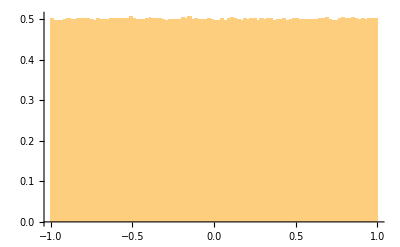

```mathematica
tabPS2bodyCompiled=Hold@Compile[{{ϕRand,_Real,1},{θRand,_Real,1},{E22body,_Real},{mFIP,_Real}},Table[{-pPar[E22body,mFIP]*Cos[ϕRand[[i]]]*Sin[θRand[[i]]],-pPar[E22body,mFIP]*Sin[ϕRand[[i]]]*Sin[θRand[[i]]],-pPar[E22body,mFIP]*Cos[θRand[[i]]],E22body,mFIP},{i,1,Length[ϕRand],1}],CompilationTarget->"C",RuntimeOptions->"Speed"]/.DownValues@pPar//ReleaseHold;
(*When there are 2 FIPs among the final particles. I.e. the process is Mother -> FIP+FIP, where 2 FIPs have the same energy Subscript[m, mother]/2*)
tabPS2body2FIPsCompiled=Hold@Compile[{{ϕRand,_Real,1},{θRand,_Real,1},{E22body,_Real},{mFIP,_Real}},Table[{pPar[E22body,mFIP]*Cos[ϕRand[[i]]]*Sin[θRand[[i]]],pPar[E22body,mFIP]*Sin[ϕRand[[i]]]*Sin[θRand[[i]]],pPar[E22body,mFIP]*Cos[θRand[[i]]],E22body,mFIP,-pPar[E22body,mFIP]*Cos[ϕRand[[i]]]*Sin[θRand[[i]]],-pPar[E22body,mFIP]*Sin[ϕRand[[i]]]*Sin[θRand[[i]]],-pPar[E22body,mFIP]*Cos[θRand[[i]]],E22body,mFIP},{i,1,Length[θRand],1}],CompilationTarget->"C",RuntimeOptions->"Speed"]/.DownValues@pPar//ReleaseHold;
(*Returns table with the following columns:*)
(*Subscript[p, x], Subscript[p, y], Subscript[p, z], E (in GeV) of the particle in the 2-body decay 0-> 1+2*)
(*MASSM is the decaying particle mass, MASS1 is the mass of one of the products, Subscript[m, FIP] is the mass of FIP*)
TwoBodyDecaysEventsAtRest[MASSM_,MASS1_,mFIP_,Nevents_]:=Block[{},
(*Energies of particles 1 (E12body) and 2 (E22body) at the rest frame of decaying particle*)
E12body=(MASSM^2-mFIP^2+MASS1^2)/(2*MASSM);
E22body=(MASSM^2-MASS1^2+mFIP^2)/(2*MASSM);
(*Array of random values of ϕ and θ defined via Subscript[p, 2] = (-p×Cos[ϕ]×Sin[θ],-p×Sin[ϕ]×Sin[θ],-p×Cos[θ])*)
(*Distribution in ϕ is isotropic. Distribution in cos(θ) is isotropic. Hence, one should generate random values of ϕ in (-Pi,Pi) and random values of cos(θ) from -1 to 1, then takin arccos()*)
ϕRand=RandomReal[{-Pi,Pi},Nevents];
θRand=ArcCos[RandomReal[{-1,1},Nevents]];
(*The final phase space*)
TabPS2bodyTemp=If[MASS1==mFIP,tabPS2body2FIPsCompiled[ϕRand,ϕRand,E22body,mFIP],tabPS2bodyCompiled[ϕRand,θRand,E22body,mFIP]];
If[MASS1==mFIP,Join[TabPS2bodyTemp[[All,{1,2,3,4,5}]],TabPS2bodyTemp[[All,{6,7,8,9,10}]]],TabPS2bodyTemp]
]
tabtest=TwoBodyDecaysEventsAtRest[5.3,0.3,1,5*10^6];//AbsoluteTiming
Print["Distribution in cos(θ) (must be isotropic):"]
Histogram[tabtest[[All,3]]/(√((tabtest[[1]][[4]])^2-(tabtest[[1]][[5]])^2)),100,"ProbabilityDensity"]
```

### 3-body

#### Full phase space in terms of energies E_1,E_3, and uniformly distributed angles

```mathematica
(*Rotation matrices with around z axis (ϕ angle) and x axis (θ angle)*)
ϕRotMatrix[ϕ_]={{Cos[ϕ],Sin[ϕ],0},{-Sin[ϕ],Cos[ϕ],0},{0,0,1}};
θRotMatrix[θ_]={{1,0,0},{0,Cos[θ],Sin[θ]},{0,-Sin[θ],Cos[θ]}};
pvecUnrotated[px_,py_,pz_]={px,py,pz};
pvecRotated[px_,py_,pz_,θV_,ϕV_]=ϕRotMatrix[ϕV].θRotMatrix[θV].pvecUnrotated[px,py,pz];
(*Momenta at frame where Subscript[p, 1] is aligned along z axis*)
p1unrotated={0,0,pPar[E1,m1]};
p2unrotated={pPar[E2valEnergies[m,E1,E3],m2]*Sin[θ12[E1,E3,m,m1,m2,m3]]*Sin[κ],pPar[E2valEnergies[m,E1,E3],m2]*Sin[θ12[E1,E3,m,m1,m2,m3]]*Cos[κ],pPar[E2valEnergies[m,E1,E3],m2]*Cos[θ12[E1,E3,m,m1,m2,m3]]};
p3unrotated={-pPar[E3,m3]*Sin[θ13[E1,E3,m,m1,m2,m3]]*Sin[κ],-pPar[E3,m3]*Sin[θ13[E1,E3,m,m1,m2,m3]]*Cos[κ],pPar[E3,m3]*Cos[θ13[E1,E3,m,m1,m2,m3]]};
(*θrand=RandomReal[{0,Pi}];
ϕrand=RandomReal[{-Pi,Pi}];*)
p1rotated[E1_,m1_,θV_,ϕV_]=(*ϕRotMatrix[ϕV].θRotMatrix[θV].p1Unrotated*)pvecRotated[p1unrotated[[1]],p1unrotated[[2]],p1unrotated[[3]],θV,ϕV];
p1rotatedX[E1_,m1_,θV_,ϕV_]=p1rotated[E1,m1,θV,ϕV][[1]];
p1rotatedY[E1_,m1_,θV_,ϕV_]=p1rotated[E1,m1,θV,ϕV][[2]];
p1rotatedZ[E1_,m1_,θV_,ϕV_]=p1rotated[E1,m1,θV,ϕV][[3]];
p2rotated[E1_,E3_,m_,m1_,m2_,m3_,θV_,ϕV_,κ_]=pvecRotated[p2unrotated[[1]],p2unrotated[[2]],p2unrotated[[3]],θV,ϕV]//Simplify;
p2rotatedX[E1_,E3_,m_,m1_,m2_,m3_,θV_,ϕV_,κ_]=p2rotated[E1,E3,m,m1,m2,m3,θV,ϕV,κ][[1]];
p2rotatedY[E1_,E3_,m_,m1_,m2_,m3_,θV_,ϕV_,κ_]=p2rotated[E1,E3,m,m1,m2,m3,θV,ϕV,κ][[2]];
p2rotatedZ[E1_,E3_,m_,m1_,m2_,m3_,θV_,ϕV_,κ_]=p2rotated[E1,E3,m,m1,m2,m3,θV,ϕV,κ][[3]];
p3rotated[E1_,E3_,m_,m1_,m2_,m3_,θV_,ϕV_,κ_]=pvecRotated[p3unrotated[[1]],p3unrotated[[2]],p3unrotated[[3]],θV,ϕV]//Simplify;
p3rotatedX[E1_,E3_,m_,m1_,m2_,m3_,θV_,ϕV_,κ_]=p3rotated[E1,E3,m,m1,m2,m3,θV,ϕV,κ][[1]];
p3rotatedY[E1_,E3_,m_,m1_,m2_,m3_,θV_,ϕV_,κ_]=p3rotated[E1,E3,m,m1,m2,m3,θV,ϕV,κ][[2]];
p3rotatedZ[E1_,E3_,m_,m1_,m2_,m3_,θV_,ϕV_,κ_]=p3rotated[E1,E3,m,m1,m2,m3,θV,ϕV,κ][[3]];
```

#### Table with distributions

```mathematica
NN=10^6;
(*Phase space of 3-body decays at rest. Returns blocks {{decaying particle data},{product1 data},{product2 data},{product3 data}} with the following data: Subscript[p, x],Subscript[p, y],Subscript[p, z],E. FIP data only is left*)
(*When there is 1 FIP among the final 3 particles*)
tabPS3bodyCompiled=Hold@Compile[{{tabPSenergies,_Real,2},{θrandTab,_Real,1},{ϕrandTab,_Real,1},{κrandTab,_Real,1},{MASSM,_Real},{MASS1,_Real},{MASS2,_Real},{MASS3,_Real}},Table[{p3rotatedX[tabPSenergies[[i]][[1]],tabPSenergies[[i]][[2]],MASSM,MASS1,MASS2,MASS3,θrandTab[[i]],ϕrandTab[[i]],κrandTab[[i]]],p3rotatedY[tabPSenergies[[i]][[1]],tabPSenergies[[i]][[2]],MASSM,MASS1,MASS2,MASS3,θrandTab[[i]],ϕrandTab[[i]],κrandTab[[i]]],p3rotatedZ[tabPSenergies[[i]][[1]],tabPSenergies[[i]][[2]],MASSM,MASS1,MASS2,MASS3,θrandTab[[i]],ϕrandTab[[i]],κrandTab[[i]]],tabPSenergies[[i]][[2]]},{i,1,Length[tabPSenergies],1}],CompilationTarget->"C",RuntimeOptions->"Speed"]/.DownValues@p3rotatedX/.DownValues@p3rotatedY/.DownValues@p3rotatedZ//ReleaseHold;
(*When there are 2 FIPs among the final 3 particles*)
tabPS3body2FIPsCompiled=Hold@Compile[{{tabPSenergies,_Real,2},{θrandTab,_Real,1},{ϕrandTab,_Real,1},{κrandTab,_Real,1},{MASSM,_Real},{MASS1,_Real},{MASS2,_Real},{MASS3,_Real}},Table[{p2rotatedX[tabPSenergies[[i]][[1]],tabPSenergies[[i]][[2]],MASSM,MASS1,MASS2,MASS3,θrandTab[[i]],ϕrandTab[[i]],κrandTab[[i]]],p2rotatedY[tabPSenergies[[i]][[1]],tabPSenergies[[i]][[2]],MASSM,MASS1,MASS2,MASS3,θrandTab[[i]],ϕrandTab[[i]],κrandTab[[i]]],p2rotatedZ[tabPSenergies[[i]][[1]],tabPSenergies[[i]][[2]],MASSM,MASS1,MASS2,MASS3,θrandTab[[i]],ϕrandTab[[i]],κrandTab[[i]]],MASSM-tabPSenergies[[i]][[1]]-tabPSenergies[[i]][[2]],p3rotatedX[tabPSenergies[[i]][[1]],tabPSenergies[[i]][[2]],MASSM,MASS1,MASS2,MASS3,θrandTab[[i]],ϕrandTab[[i]],κrandTab[[i]]],p3rotatedY[tabPSenergies[[i]][[1]],tabPSenergies[[i]][[2]],MASSM,MASS1,MASS2,MASS3,θrandTab[[i]],ϕrandTab[[i]],κrandTab[[i]]],p3rotatedZ[tabPSenergies[[i]][[1]],tabPSenergies[[i]][[2]],MASSM,MASS1,MASS2,MASS3,θrandTab[[i]],ϕrandTab[[i]],κrandTab[[i]]],tabPSenergies[[i]][[2]]},{i,1,Length[tabPSenergies],1}],CompilationTarget->"C",RuntimeOptions->"Speed"]/.DownValues@p2rotatedX/.DownValues@p2rotatedY/.DownValues@p2rotatedZ/.DownValues@p3rotatedX/.DownValues@p3rotatedY/.DownValues@p3rotatedZ//ReleaseHold;
tabPS3bodyTestCompiled=Hold@Compile[{{tabPSenergies,_Real,2},{θrandTab,_Real,1},{ϕrandTab,_Real,1},{κrandTab,_Real,1},{MASSM,_Real},{MASS1,_Real},{MASS2,_Real},{MASS3,_Real}},Table[{p1rotatedX[tabPSenergies[[i]][[1]],MASS1,θrandTab[[i]],ϕrandTab[[i]]],p1rotatedY[tabPSenergies[[i]][[1]],MASS1,θrandTab[[i]],ϕrandTab[[i]]],p1rotatedZ[tabPSenergies[[i]][[1]],MASS1,θrandTab[[i]],ϕrandTab[[i]]],tabPSenergies[[i]][[1]],p2rotatedX[tabPSenergies[[i]][[1]],tabPSenergies[[i]][[2]],MASSM,MASS1,MASS2,MASS3,θrandTab[[i]],ϕrandTab[[i]],κrandTab[[i]]],p2rotatedY[tabPSenergies[[i]][[1]],tabPSenergies[[i]][[2]],MASSM,MASS1,MASS2,MASS3,θrandTab[[i]],ϕrandTab[[i]],κrandTab[[i]]],p2rotatedZ[tabPSenergies[[i]][[1]],tabPSenergies[[i]][[2]],MASSM,MASS1,MASS2,MASS3,θrandTab[[i]],ϕrandTab[[i]],κrandTab[[i]]],MASSM-tabPSenergies[[i]][[1]]-tabPSenergies[[i]][[2]],p3rotatedX[tabPSenergies[[i]][[1]],tabPSenergies[[i]][[2]],MASSM,MASS1,MASS2,MASS3,θrandTab[[i]],ϕrandTab[[i]],κrandTab[[i]]],p3rotatedY[tabPSenergies[[i]][[1]],tabPSenergies[[i]][[2]],MASSM,MASS1,MASS2,MASS3,θrandTab[[i]],ϕrandTab[[i]],κrandTab[[i]]],p3rotatedZ[tabPSenergies[[i]][[1]],tabPSenergies[[i]][[2]],MASSM,MASS1,MASS2,MASS3,θrandTab[[i]],ϕrandTab[[i]],κrandTab[[i]]],tabPSenergies[[i]][[2]]},{i,1,Length[tabPSenergies],1}],CompilationTarget->"C",RuntimeOptions->"Speed"]/.DownValues@p1rotatedX/.DownValues@p1rotatedY/.DownValues@p1rotatedZ/.DownValues@p2rotatedX/.DownValues@p2rotatedY/.DownValues@p2rotatedZ/.DownValues@p3rotatedX/.DownValues@p3rotatedY/.DownValues@p3rotatedZ//ReleaseHold;
BlockRandomEnergies=Compile[{m,m1,m2,m3,E1min,E1max},Module[{E1r=0.,E2v=0.,E3r=0.},While[E3r=RandomReal[{m3,(m^2+m3^2-(m1+m2)^2)/(2*m)}];
E1r=RandomReal[{E1min,E1max}];
E2v=m-E1r-E3r;
E2v≤m2||(E2v^2-m2^2-(E1r^2-m1^2)-(E3r^2-m3^2))^2≥4*(E1r^2-m1^2)*(E3r^2-m3^2)];
{E1r,E3r}],CompilationTarget->"C",RuntimeOptions->"Speed"];
E12E23domain[m_,m1_,m2_,m3_,Emin_,Emax_]:=NIntegrate[UnitStep[E3v-Emin]*UnitStep[Emax-E3v],{E1v,E1domain[m,m1,m2,m3][[1]],E1domain[m,m1,m2,m3][[2]]},{E3v,Max[E3domain[E1v,m,m1,m2,m3][[1]],Emin],Min[Emax,E3domain[E1v,m,m1,m2,m3][[2]]]},Method->"AdaptiveMonteCarlo"]
E3domain1[E1_,m_,m1_,m2_,m3_]=E3domain[E1,m,m1,m2,m3][[1]];
E3domain2[E1_,m_,m1_,m2_,m3_]=E3domain[E1,m,m1,m2,m3][[2]];
ThreeBodyDecaysEventsAtRest[mFIP_,ml_,particle_,process_,Nevents_]:=Block[{},
(*Random points from phase space*)
MASSM=massM3bodyProcess[particle,process];
MASS1=mass13bodyProcess[particle,process];
MASS2=mass23bodyProcess[particle,process,mFIP,ml];
MASS3=mFIP;
(*Generate random Subscript[E, 1],Subscript[E, 3]*)
(*For the 3-body production with the photon propagator, the phase space generation may be inaccurate, since the Subscript[m, inv] distribution of the pair from the propagator is peaked at Subscript[m, 1]+Subscript[m, 2]*)
E1maxval=E1domain[MASSM,MASS1,MASS2,MASS3][[2]];
tabRPPS=Table[BlockRandomEnergies[MASSM,MASS1,MASS2,MASS3,MASS1,E1maxval],NN];
(*Distribution in Subscript[E, 1,3] - the squared matrix element*)
distr[E1_,E3_]=M2for3bodyProcess[particle,process,mFIP,ml,E1,E3]//Simplify;
(*Weights for the generated values of {E1,E3} from matrix element squared*)
weights1=Hold@Compile[{{tab1,_Real,2}},Table[(E3domain2[tab1[[i]][[1]],MASSM,MASS1,MASS2,MASS3]-E3domain1[tab1[[i]][[1]],MASSM,MASS1,MASS2,MASS3])distr[tab1[[i]][[1]],tab1[[i]][[2]]],{i,1,NN,1}],CompilationTarget->"C",RuntimeOptions->"Speed"]/.DownValues@E3domain1/.DownValues@E3domain2/.DownValues@distr/.OwnValues@MASSM/.OwnValues@MASS1/.OwnValues@MASS2/.OwnValues@MASS3//ReleaseHold;
weights=weights1[tabRPPS]/._?Negative->0;
(*Weighted random points*)
weightedData=WeightedData[tabRPPS,weights];
(*True random energies. Computed via empirical distribution from the weigthed data*)
edist=EmpiricalDistribution[weightedData];
tabPSenergies=RandomVariate[edist,Nevents];
(*Angles relating generated energies to the 4-momenta*)
θrandTab=ArcCos[RandomReal[{-1,1},Nevents]];
ϕrandTab=RandomReal[{-Pi,Pi},Nevents];
κrandTab=RandomReal[{-Pi,Pi},Nevents];
tabPS3bodyTemp=If[particle==process=="test",tabPS3bodyTestCompiled[tabPSenergies,θrandTab,ϕrandTab,κrandTab,MASSM,MASS1,MASS2,MASS3],If[MASS2==MASS3,tabPS3body2FIPsCompiled[tabPSenergies,θrandTab,ϕrandTab,κrandTab,MASSM,MASS1,MASS2,MASS3],tabPS3bodyCompiled[tabPSenergies,θrandTab,ϕrandTab,κrandTab,MASSM,MASS1,MASS2,MASS3]]];
If[particle==process=="test",tabPS3bodyTemp,If[MASS2==MASS3,Join[tabPS3bodyTemp[[All,{1,2,3,4}]],tabPS3bodyTemp[[All,{5,6,7,8}]]],tabPS3bodyTemp]]
]
```

#### Test - Dalitz plot for spinless decays

```mathematica
(*mtest=0.3;
TestPhaseSpace=ThreeBodyDecaysEventsAtRest[mtest,0,"test","test",10^4];//AbsoluteTiming
m12test[E1_,E2_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,m1_,m2_]=m1^2+m2^2+2*(E1*E2-p1x*p2x-p1y*p2y-p1z*p2z);
m23test[E2_,E3_,p2x_,p2y_,p2z_,p3x_,p3y_,p3z_,m2_,m3_]=m2^2+m3^2+2*(E2*E3-p2x*p3x-p2y*p3y-p2z*p3z);
Testm12m23Compiled=Hold@Compile[{{TestPhaseSpace,_Real,2},m1,m2,m3},Table[{m12test[TestPhaseSpace[[i]][[4]],TestPhaseSpace[[i]][[8]],TestPhaseSpace[[i]][[1]],TestPhaseSpace[[i]][[2]],TestPhaseSpace[[i]][[3]],TestPhaseSpace[[i]][[5]],TestPhaseSpace[[i]][[6]],TestPhaseSpace[[i]][[7]],m1,m2],m23test[TestPhaseSpace[[i]][[8]],TestPhaseSpace[[i]][[12]],TestPhaseSpace[[i]][[5]],TestPhaseSpace[[i]][[6]],TestPhaseSpace[[i]][[7]],TestPhaseSpace[[i]][[9]],TestPhaseSpace[[i]][[10]],TestPhaseSpace[[i]][[11]],m2,m3]},{i,1,Length[TestPhaseSpace],1}],CompilationTarget->"C",RuntimeOptions->"Speed"]/.DownValues@m12test/.DownValues@m23test//ReleaseHold
Testm12m23=Testm12m23Compiled[TestPhaseSpace,mass13bodyProcess["test","test"],mass23bodyProcess["test","test",0,0],mtest];//AbsoluteTiming
ListPlot[{Testm12m23,Table[{(mass13bodyProcess["test","test"]+mass23bodyProcess["test","test",0,0])^2,x},{x,0,massM3bodyProcess["test","test"],0.05}],Table[{x,(mass23bodyProcess["test","test",0,0]+mtest)^2},{x,0,massM3bodyProcess["test","test"],0.05}],Table[{x,(massM3bodyProcess["test","test"]-mass13bodyProcess["test","test"])^2},{x,0,massM3bodyProcess["test","test"],0.05}],Table[{(massM3bodyProcess["test","test"]-mtest)^2,x},{x,0,massM3bodyProcess["test","test"],0.05}]},Frame->True,Joined->{False,True,True,True,True},FrameLabel->{"m_12 [GeV^2]" , "m_23 [GeV^2]"},FrameStyle->Directive[Black, 23],PlotStyle->{{Thick,Blue},{Thick,Black,Dashing[0.01]},{Thick,Black,Dashing[0.02]},{Thick,Black,Dashing[0.03]},{Thick,Black,Dashing[0.04]},{Thick,Darker@Cyan,PointSize[0.01]},{Thick,Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Darker@Red,PointSize[0.04]}},ImageSize->Large,PlotRange->{{0,massM3bodyProcess["test","test"]},All},PlotLabel->Style[Row[{"Dalitz plot for M^2 = const, m_mother = ",massM3bodyProcess["test","test"]," GeV, m_1 = ",mass13bodyProcess["test","test"]," GeV, m_2 = ",mass23bodyProcess["test","test",0,0] ," GeV, m_3 = ",mtest, " GeV"}],15,Black],PlotLegends->Placed[Style[#,15]&/@{"Dalitz plot","(m_1+m_2)^2","(m_2+m_3)^2","(m - m_1)^2","(m - m_3)^2"},Right]]*)
```

## Lorentz boosts

### Boosting to the lab frame of the decaying mother particle

```mathematica
ϕVal[px_,py_]=If[py>0,ArcCos[px/(√(px^2+py^2))],-ArcCos[px/(√(px^2+py^2))]];
θVal[px_,py_,pz_]=ArcCos[pz/(√(px^2+py^2+pz^2))];
(*Mother particle momentum, velocity and γ,Γ factors at its lab frame*)
pvecMotherLab[pMotherLab1_,pMotherLab2_,pMotherLab3_]={pMotherLab1,pMotherLab2,pMotherLab3};
vvecMotherLab[EmotherLab_,pMotherLab1_,pMotherLab2_,pMotherLab3_]=+pvecMotherLab[pMotherLab1,pMotherLab2,pMotherLab3]/EmotherLab;
γFactor[Energy_,m_]=Energy/m;
ΓfactorMotherLab[EmotherLab_,mMother_]=Simplify[(γFactor[EmotherLab,mMother]-1)/(((v/.Solve[γFactor[EmotherLab,mMother]==1/(√(1-v^2)),v])^2)[[1]])];
(*Momentum of decay product at the rest frame of mother particle*)
pVecProdRest[pProdRest1_,pProdRest2_,pProdRest3_]={pProdRest1,pProdRest2,pProdRest3};
(*Decay product's momentum and energy at HNL's lab frame*)
pVecProdLab[EmotherLab_,mMother_,pMotherLab1_,pMotherLab2_,pMotherLab3_,EProdRest_,pProdRest1_,pProdRest2_,pProdRest3_]=Simplify[pVecProdRest[pProdRest1,pProdRest2,pProdRest3]+γFactor[EmotherLab,mMother]*vvecMotherLab[EmotherLab,pMotherLab1,pMotherLab2,pMotherLab3]*EProdRest+ΓfactorMotherLab[EmotherLab,mMother]*vvecMotherLab[EmotherLab,pMotherLab1,pMotherLab2,pMotherLab3](vvecMotherLab[EmotherLab,pMotherLab1,pMotherLab2,pMotherLab3].pVecProdRest[pProdRest1,pProdRest2,pProdRest3])]//Expand;
EProdLab[EmotherLab_,mMother_,pMotherLab1_,pMotherLab2_,pMotherLab3_,EProdRest_,pProdRest1_,pProdRest2_,pProdRest3_]=Simplify[γFactor[EmotherLab,mMother](EProdRest+vvecMotherLab[EmotherLab,pMotherLab1,pMotherLab2,pMotherLab3].pVecProdRest[pProdRest1,pProdRest2,pProdRest3])];
(*Decay product's momentum components in lab frame*)
pProductLab1[EmotherLab_,mMother_,pMotherLab1_,pMotherLab2_,pMotherLab3_,EProdRest_,pProdRest1_,pProdRest2_,pProdRest3_]=pVecProdLab[EmotherLab,mMother,pMotherLab1,pMotherLab2,pMotherLab3,EProdRest,pProdRest1,pProdRest2,pProdRest3][[1]];
pProductLab2[EmotherLab_,mMother_,pMotherLab1_,pMotherLab2_,pMotherLab3_,EProdRest_,pProdRest1_,pProdRest2_,pProdRest3_]=pVecProdLab[EmotherLab,mMother,pMotherLab1,pMotherLab2,pMotherLab3,EProdRest,pProdRest1,pProdRest2,pProdRest3][[2]];
pProductLab3[EmotherLab_,mMother_,pMotherLab1_,pMotherLab2_,pMotherLab3_,EProdRest_,pProdRest1_,pProdRest2_,pProdRest3_]=pVecProdLab[EmotherLab,mMother,pMotherLab1,pMotherLab2,pMotherLab3,EProdRest,pProdRest1,pProdRest2,pProdRest3][[3]];
Print["Checking that (E^2)_boosted-((p̄)^2)_boosted = m^2:"]
expr=((EProdLab[EmotherLab,mMother,pMotherLab1,pMotherLab2,pMotherLab3,EProdRest,pProdRest1,pProdRest2,pProdRest3]^2-pProductLab1[EmotherLab,mMother,pMotherLab1,pMotherLab2,pMotherLab3,EProdRest,pProdRest1,pProdRest2,pProdRest3]^2-pProductLab2[EmotherLab,mMother,pMotherLab1,pMotherLab2,pMotherLab3,EProdRest,pProdRest1,pProdRest2,pProdRest3]^2-pProductLab3[EmotherLab,mMother,pMotherLab1,pMotherLab2,pMotherLab3,EProdRest,pProdRest1,pProdRest2,pProdRest3]^2)//Expand//Simplify)/.{EmotherLab->√(mMother^2+pMotherLab1^2+pMotherLab2^2+pMotherLab3^2)}/.{EProdRest->√(pProdRest1^2+pProdRest2^2+pProdRest3^2+mProd^2)}//Simplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

Checking that (E^2)_boosted-((p̄)^2)_boosted = m^2:

mProd^2

### Table with 4-momentum of boosted FIPs

```mathematica
(*Table Subscript[p, product,x], Subscript[p, product,y], Subscript[p, product,z], Subscript[E, product]*)
indexpx=1;
indexpy=2;
indexpz=3;
indexE=4;
BoostedFIPsFromDecaysTable=Hold@Compile[{{tablemother,_Real,1},{tabledaughter,_Real,1},{mothermass,_Real}},Module[{motherE,motherpx,motherpy,motherpz,daughterErest,daughterpxrest,daughterpyrest,daughterpzrest,daughterElab,daughterpxlab,daughterpylab,daughterpzlab},
motherE=Compile`GetElement[tablemother,indexE];
motherpx=Compile`GetElement[tablemother,indexpx];
motherpy=Compile`GetElement[tablemother,indexpy];
motherpz=Compile`GetElement[tablemother,indexpz];
daughterErest=Compile`GetElement[tabledaughter,indexE];
daughterpxrest=Compile`GetElement[tabledaughter,indexpx];
daughterpyrest=Compile`GetElement[tabledaughter,indexpy];
daughterpzrest=Compile`GetElement[tabledaughter,indexpz];
daughterElab=EProdLab[motherE,mothermass,motherpx,motherpy,motherpz,daughterErest,daughterpxrest,daughterpyrest,daughterpzrest];
daughterpxlab=pProductLab1[motherE,mothermass,motherpx,motherpy,motherpz,daughterErest,daughterpxrest,daughterpyrest,daughterpzrest];
daughterpylab=pProductLab2[motherE,mothermass,motherpx,motherpy,motherpz,daughterErest,daughterpxrest,daughterpyrest,daughterpzrest];
daughterpzlab=pProductLab3[motherE,mothermass,motherpx,motherpy,motherpz,daughterErest,daughterpxrest,daughterpyrest,daughterpzrest];
{daughterpxlab,daughterpylab,daughterpzlab,daughterElab}
],CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->{Listable}]/.DownValues@pProductLab1/.DownValues@pProductLab2/.DownValues@pProductLab3/.DownValues@EProdLab/.OwnValues@indexpx/.OwnValues@indexpy/.OwnValues@indexpz/.OwnValues@indexE//ReleaseHold;
BoostedFIPsLogData=Hold@Compile[{{BoostedFIPs,_Real,1},{mFIP,_Real}},Module[{pzvals,Evals},
pzvals=Compile`GetElement[BoostedFIPs,indexpz];
Evals=Compile`GetElement[BoostedFIPs,indexE];
{Log[ArcCos[pzvals/(√(Evals^2-mFIP^2))]],Log[Evals]}],CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->{Listable}]/.OwnValues@indexpz/.OwnValues@indexE//ReleaseHold
```

CompiledFunction[…]

## Distribution of FIPs

## Definitions

```mathematica
(*The block that computes the smooth pdf Subscript[f, θ,E] from the data BoostedData in the form Log[θ],Log[E]*)
FromDataToSmoothDistribution[BoostedData_,mass_]:=Block[{},
{LogθminDistr,LogθmaxDistr}=MinMax[BoostedData[[All,1]]];
LogEmaxDistr=Max[BoostedData[[All,2]]];
smoothkerneldistrX=SmoothKernelDistribution[BoostedData,"LeastSquaresCrossValidation",{"Bounded",{{LogθminDistr,LogθmaxDistr},{Log[mass],LogEmaxDistr}},"Gaussian"},MaxMixtureKernels->All,InterpolationPoints->300,MaxExtraBandwidths->0];
(*Double and marginal PDFs*)
DoubleDistr[θFIP_,EFIP_]=If[Exp[LogθminDistr]≤θFIP≤Exp[LogθmaxDistr]&&mass≤ EFIP≤Exp[LogEmaxDistr],Evaluate[1/θFIP 1/EFIP PDF[smoothkerneldistrX,{Log[θFIP],Log[EFIP]}],0]];
AngleDistr[θFIP_]=If[Exp[LogθminDistr]≤θFIP≤Exp[LogθmaxDistr],Evaluate[1/θFIP PDF[MarginalDistribution[smoothkerneldistrX,1],Log[θFIP]],0]];
EnergyDistr[EFIP_]=If[mass≤ EFIP≤Exp[LogEmaxDistr],Evaluate[1/EFIP PDF[MarginalDistribution[smoothkerneldistrX,2],Log[EFIP]],0]];
]
```

## HNLs

### Phase space points

```mathematica
BoostedHNLsBlock[mixing_,mN_,DecayType_,Process_,MotherData_]:=Module[{MotherMass},
mlval=If[Process≠"τ 3-body"&&Process≠"τ 2-body",mlMixing[mixing],If[Process=="τ 3-body",mlMixing["e"],mπ]];
MotherMass=MotherData[[1]][[5]];
(*Phase space of HNLs at the rest frame of the decaying particle*)
DataRest=If[DecayType=="3-body",ThreeBodyDecaysEventsAtRest[mN,mlval,"HNL",Process,Length[MotherData]],TwoBodyDecaysEventsAtRest[MotherMass,mlval,mN,Length[MotherData]]];
(*Boosting and returning the data in the form Log[θ],Log[E]*)
BoostedFIPsLogData[BoostedFIPsFromDecaysTable[MotherData,DataRest,MotherMass],mN]
]
```

### Distribution

#### From B

```mathematica
HNLdistributionFromB[mixing_,mN_,BcOption_,WeightsHNLproductionFromBmixing_,Bdata_,Bcdata_,θNlist_,ENlist_,θNextr_]:=Block[{},
TotalLength=Length[Bdata];
(*Weights for the production of 3-body decays of B^(+/0) (approximated by the dominant decays B^(+/0)-> D^* + N+ l), 2-body decays of B^+, and 2-body decays of Subscript[B, c]*)
WeightsHNLproduction=WeightsHNLproductionFromBmixing[mixing,mN,BcOption];
(*Corresponding number of B decays to be generated*)
NeventsHNLproduction3bodyBplusB0=(TotalLength*WeightsHNLproduction[[1]]/(3*Mean[WeightsHNLproduction])//IntegerPart);
NeventsHNLproduction2bodyBplus=If[BcOption=="True",(TotalLength*WeightsHNLproduction[[2]]/(3*Mean[WeightsHNLproduction])//IntegerPart),TotalLength-(TotalLength*WeightsHNLproduction[[1]]/(3*Mean[WeightsHNLproduction])//IntegerPart)];
NeventsHNLproductionBc=TotalLength-NeventsHNLproduction3bodyBplusB0-NeventsHNLproduction2bodyBplus;
NeventsHNLproduction={NeventsHNLproduction3bodyBplusB0,NeventsHNLproduction2bodyBplus,NeventsHNLproductionBc};
DecayTypeVals={"3-body","2-body","2-body"};
ProcessVals={"B 3-body","B 2-body","B_c 2-body"};
(*Data with mother B mesons with the length according to the weights*)
MotherDataSel={If[NeventsHNLproduction[[1]]≠0,Take[Bdata,{1,NeventsHNLproduction[[1]]}]],If[NeventsHNLproduction[[2]]≠0,Take[Bdata,{1,NeventsHNLproduction[[2]]}]],If[NeventsHNLproduction[[3]]≠0,Take[Bcdata,{1,NeventsHNLproduction[[3]]}]]};
NeventsHNLproductionNonZero=Select[Partition[NeventsHNLproduction,1],#[[1]]≠0&]//Flatten;
(*Computing data with boosted HNLs and converting it into Log[Subscript[θ, N]], Log[Subscript[E, N]]*)
BoostedHNLs=Flatten[Select[Table[{If[NeventsHNLproduction[[i]]≠0,BoostedHNLsBlock[mixing,mN,DecayTypeVals[[i]],ProcessVals[[i]],MotherDataSel[[i]]],0]},{i,1,Length[NeventsHNLproduction],1}],Length[#[[1]]]≠0&],2];
(*Making the distribution. It defines the functions DoubleDist[θ,E],AngleDistr[θ],EnergyDistr[E], which are PDF in these variables*)
FromDataToSmoothDistribution[BoostedHNLs,mN];
(*Table with the tabulated distribution. The argument Subscript[θ, extr] defines the angle below which the angular distribution is just ~sin(θ) (the true distribution has wiggles there due to low statistics)*)
Flatten[Table[{mN,θN,EN,If[θN<θNextr,θN/θNextr DoubleDistr[θNextr,EN],DoubleDistr[θN,EN]]},{θN,θNlist},{EN,ENlist}],1]
]
TabZeroDistrHNL[mN_,θNlist_,ENlist_]:=Flatten[Table[{mN,θN,EN,0.},{θN,θNlist},{EN,ENlist}],1]
```

#### From D

```mathematica
HNLdistributionFromD[mixing_,mN_,WeightsHNLproductionFromDmixing_,Ddata_,Dsdata_,τData_,θNlist_,ENlist_,θNextr_]:=Block[{},
TotalLength=Length[Ddata];
(*Weights for the production of 3-body decays of B^(+/0) (approximated by the dominant decays B^(+/0)-> D^* + N+ l), 2-body decays of B^+, and 2-body decays of Subscript[B, c]*)
WeightsHNLproduction=WeightsHNLproductionFromDmixing[mixing,mN];
(*Corresponding number of B decays to be generated*)
NeventsHNLproductionChannel1=(TotalLength*(WeightsHNLproduction[[1]]/(3*Mean[WeightsHNLproduction]))//IntegerPart);
NeventsHNLproductionChannel2=If[mixing=="τ",(TotalLength*(WeightsHNLproduction[[2]]/(3*Mean[WeightsHNLproduction]))//IntegerPart),TotalLength-(TotalLength*(WeightsHNLproduction[[1]]/(3*Mean[WeightsHNLproduction]))//IntegerPart)];
NeventsHNLproductionChannel3=If[mixing≠"τ",0,TotalLength-NeventsHNLproductionChannel1-NeventsHNLproductionChannel2];
NeventsHNLproduction={NeventsHNLproductionChannel1,NeventsHNLproductionChannel2,NeventsHNLproductionChannel3};
DecayTypeVals=If[mixing=="τ",{"2-body","3-body","2-body"},{"3-body","2-body"}];
ProcessVals=If[mixing=="τ",{"D 2-body","τ 3-body","τ 2-body"},{"D 3-body","D_s 2-body"}];
(*Data with mother B mesons with the length according to the weights*)
MotherDataSel=If[mixing=="τ",{If[NeventsHNLproduction[[1]]≠0,Take[Dsdata,{1,NeventsHNLproduction[[1]]}]],If[NeventsHNLproduction[[2]]≠0,Take[τData,{1,NeventsHNLproduction[[2]]}]],If[NeventsHNLproduction[[3]]≠0,Take[τData,{1,NeventsHNLproduction[[3]]}]]},{If[NeventsHNLproduction[[1]]≠0,Take[Ddata,{1,NeventsHNLproduction[[1]]}]],If[NeventsHNLproduction[[2]]≠0,Take[Dsdata,{1,NeventsHNLproduction[[2]]}]]}];
NeventsHNLproductionNonZero=Select[Partition[NeventsHNLproduction,1],#[[1]]≠0&]//Flatten;
(*Computing data with boosted HNLs and converting it into Log[Subscript[θ, N]], Log[Subscript[E, N]]*)
BoostedHNLs=Flatten[Select[Table[{If[NeventsHNLproduction[[i]]≠0,BoostedHNLsBlock[mixing,mN,DecayTypeVals[[i]],ProcessVals[[i]],MotherDataSel[[i]]],0]},{i,1,Length[NeventsHNLproduction],1}],Length[#[[1]]]≠0&],2];
(*Making the distribution. It defines the functions DoubleDist[θ,E],AngleDistr[θ],EnergyDistr[E], which are PDF in these variables*)
FromDataToSmoothDistribution[BoostedHNLs,mN];
(*Table with the tabulated distribution. The argument Subscript[θ, extr] defines the angle below which the angular distribution is just ~sin(θ) (the true distribution has wiggles there due to low statistics)*)
Flatten[Table[{mN,θN,EN,If[θN<θNextr,θN/θNextr DoubleDistr[θNextr,EN],DoubleDistr[θN,EN]]},{θN,θNlist},{EN,ENlist}],1]
]
```

### From W/K

```mathematica
HNLdistributionFromWK[mixing_,mN_,WKdata_,θNlist_,ENlist_,θextr_]:=Block[{},
(*Computing data with boosted HNLs and converting it into Log[Subscript[θ, N]], Log[Subscript[E, N]]*)
BoostedHNLs=BoostedHNLsBlock[mixing,mN,"2-body","WK decay",WKdata];
(*Making the distribution. It defines the functions DoubleDist[θ,E],AngleDistr[θ],EnergyDistr[E], which are PDF in these variables*)
FromDataToSmoothDistribution[BoostedHNLs,mN];
(*Table with the tabulated distribution. The argument Subscript[θ, extr] defines the angle below which the angular distribution is just ~sin(θ) (the true distribution has wiggles there due to low statistics)*)
Flatten[Table[{mN,θN,EN,If[θN<θextr,Evaluate[θN/θextr DoubleDistr[θextr,EN]],DoubleDistr[θN,EN]]},{θN,θNlist},{EN,ENlist}],1]
]
```

## Scalars

### Phase space points

```mathematica
mSecondProductScalar2body[process_,mS_]:=Association[{{"Higgs 2-body",mS}-> mS,{"B 2-body",mS}->mπ,{"K 2-body",mS}->mπ,{"B_s 2-body",mS}->mS,{"h 2-body",mS}->mS}][{process,mS}]
BoostedScalarsBlock[mS_,MotherData_,DecayType_,Process_]:=Module[{MotherMass},
SecondMassVal2body=If[DecayType=="2-body",mSecondProductScalar2body[Process,mS]];
MotherMass=MotherData[[1]][[5]];
(*To account that for processes X -> S+S two scalars are produced. So per each row of the mother data we have two rows with scalars*)
lensimulate=If[Process=="B 2-body"||Process=="K 2-body",Length[MotherData],Length[MotherData]/2];
DataRest=If[DecayType=="2-body",TwoBodyDecaysEventsAtRest[MotherMass,SecondMassVal2body,mS,lensimulate],ThreeBodyDecaysEventsAtRest[mS,mS,"Scalar",Process,lensimulate]];
BoostedFIPsLogData[BoostedFIPsFromDecaysTable[MotherData,DataRest,MotherMass],mS]
]
```

### Distribution

```mathematica
ScalarDistribution[mS_,motherdata_,decaytype_,process_,θSlist_,ESlist_,θminExtr_]:=Block[{},
(*Computing data with boosted HNLs and converting it into Log[Subscript[θ, N]], Log[Subscript[E, N]]*)
BoostedScalars=BoostedScalarsBlock[mS,motherdata,decaytype,process];
(*Making the distribution. It defines the functions DoubleDist[θ,E],AngleDistr[θ],EnergyDistr[E], which are PDF in these variables*)
FromDataToSmoothDistribution[BoostedScalars,mS];
(*Table with the tabulated distribution. The argument Subscript[θ, extr] defines the angle below which the angular distribution is just ~sin(θ) (the true distribution has wiggles there due to low statistics)*)
Flatten[Table[{mS,θS,ES,If[θS<θminExtr,θS/θminExtr DoubleDistr[θminExtr,ES],DoubleDistr[θS,ES]]},{θS,θSlist},{ES,ESlist}],1]
]
```

## Dark photons and B-L

### Phase space points

```mathematica
mSecondProductDarkPhoton2body[process_,mV_]:=Association[{{"Light meson 2-body",mV}->0}][{process,mV}]
BoostedDarkPhotonsBlock[mV_,MotherData_,DecayType_,Process_]:=Module[{},
SecondMassVal2body=If[DecayType=="2-body",mSecondProductDarkPhoton2body[Process,mV]];
MotherMass=MotherData[[1]][[5]];
DataRest=If[DecayType=="2-body",TwoBodyDecaysEventsAtRest[MotherMass,SecondMassVal2body,mV,Length[MotherData]]];
BoostedFIPsLogData[BoostedFIPsFromDecaysTable[MotherData,DataRest,MotherMass],mV]
]
```

### Distribution

```mathematica
BLandDarkPhotonsDistributionFromDecays[mV_,motherdata_,decaytype_,process_,θVlist_,EVlist_,θminExtr_]:=Block[{},
(*Computing data with boosted HNLs and converting it into Log[Subscript[θ, N]], Log[Subscript[E, N]]*)
BoostedDarkPhotons=BoostedDarkPhotonsBlock[mV,motherdata,decaytype,process];
(*Making the distribution. It defines the functions DoubleDist[θ,E],AngleDistr[θ],EnergyDistr[E], which are PDF in these variables*)
FromDataToSmoothDistribution[BoostedDarkPhotons,mV];
(*Table with the tabulated distribution. The argument Subscript[θ, extr] defines the angle below which the angular distribution is just ~sin(θ) (the true distribution has wiggles there due to low statistics)*)
Flatten[Table[{mV,θV,EV,If[θV<θminExtr,θV/θminExtr DoubleDistr[θminExtr,EV],DoubleDistr[θV,EV]]},{θV,θVlist},{EV,EVlist}],1]
]
```

## ALPs with fermion/gluon coupling (from decays of B mesons)

### Phase space points

```mathematica
mSecondProductALPsFermionGluon2body[process_,ma_]:=Association[{{"B 2-body",ma}->mK}][{process,ma}]
BoostedALPsFermionGluonBlock[ma_,MotherData_,DecayType_,Process_]:=Module[{MotherMass},
SecondMassVal2body=If[DecayType=="2-body",mSecondProductALPsFermionGluon2body[Process,ma]];
MotherMass=MotherData[[1]][[5]];
DataRest=If[DecayType=="2-body",TwoBodyDecaysEventsAtRest[MotherMass,SecondMassVal2body,ma,Length[MotherData]](*,ThreeBodyDecaysEventsAtRest[mS,mS,"Scalar",Process,Length[MotherDataReduced]]*)];
BoostedFIPsLogData[BoostedFIPsFromDecaysTable[MotherData,DataRest,MotherMass],ma]
]
```

### Distribution

```mathematica
ALPsFermionGluonDistributionFromDecays[ma_,motherdata_,decaytype_,process_,θalist_,Ealist_,θminExtr_]:=Block[{},
(*Computing data with boosted HNLs and converting it into Log[Subscript[θ, N]], Log[Subscript[E, N]]*)
BoostedALPsFermionGluon=BoostedALPsFermionGluonBlock[ma,motherdata,decaytype,process];
(*Making the distribution. It defines the functions DoubleDist[θ,E],AngleDistr[θ],EnergyDistr[E], which are PDF in these variables*)
FromDataToSmoothDistribution[BoostedALPsFermionGluon,ma];
(*Table with the tabulated distribution. The argument Subscript[θ, extr] defines the angle below which the angular distribution is just ~sin(θ) (the true distribution has wiggles there due to low statistics)*)
Flatten[Table[{ma,θa,Ea,If[θa<θminExtr,θa/θminExtr DoubleDistr[θminExtr,Ea],DoubleDistr[θa,Ea]]},{θa,θalist},{Ea,Ealist}],1]
]
```

## ALPs with photon coupling

### Phase space points

```mathematica
BoostedALPsPhotonBlock[ma_,MotherData_,Process_]:=Module[{MotherMass},
MotherMass=MotherData[[1]][[5]];
DataRest=ThreeBodyDecaysEventsAtRest[ma,0,"ALP-photon",Process,Length[MotherData]];
BoostedFIPsLogData[BoostedFIPsFromDecaysTable[MotherData,DataRest,MotherMass],ma]
]
```

### Distribution

```mathematica
ALPsPhotonDistributionFromDecays[ma_,motherdata_,process_,θalist_,Ealist_,θminExtr_]:=Block[{},
(*Computing data with boosted HNLs and converting it into Log[Subscript[θ, N]], Log[Subscript[E, N]]*)
BoostedALPsPhoton=BoostedALPsPhotonBlock[ma,motherdata,process];
(*Making the distribution. It defines the functions DoubleDist[θ,E],AngleDistr[θ],EnergyDistr[E], which are PDF in these variables*)
FromDataToSmoothDistribution[BoostedALPsPhoton,ma];
(*Table with the tabulated distribution. The argument Subscript[θ, extr] defines the angle below which the angular distribution is just ~sin(θ) (the true distribution has wiggles there due to low statistics)*)
Flatten[Table[{ma,θa,Ea,If[θa<θminExtr,θa/θminExtr DoubleDistr[θminExtr,Ea],DoubleDistr[θa,Ea]]},{θa,θalist},{Ea,Ealist}],1]
]
```

## MCPs

### Phase space points

```mathematica
mSecondProductMCP2body[process_,mχ_]:=Association[{{"J/ψ 2-body",mχ}-> mχ,{"Υ 2-body",mχ}->mχ,{"ρ^0 2-body",mχ}->mχ,{"ω 2-body",mχ}->mχ,{"ϕ 2-body",mχ}->mχ}][{process,mχ}]
BoostedMCPsBlock[mχ_,MotherData_,DecayType_,Process_]:=Module[{MotherMass},
SecondMassVal2body=If[DecayType=="2-body",mSecondProductMCP2body[Process,mχ]];
MotherMass=MotherData[[1]][[5]];
(*To account that for processes X -> χχ/γχχ two MCPs are produced. So per each row of the mother data we have two rows with scalars*)
lensimulate=Length[MotherData]/2;
DataRest=If[DecayType=="2-body",TwoBodyDecaysEventsAtRest[MotherMass,SecondMassVal2body,mχ,lensimulate],ThreeBodyDecaysEventsAtRest[mχ,mχ,"MCP",Process,lensimulate]];
BoostedFIPsLogData[BoostedFIPsFromDecaysTable[MotherData,DataRest,MotherMass],mχ]
]
```

### Distribution

```mathematica
MCPDistribution[mχ_,motherdata_,decaytype_,process_,θχlist_,Eχlist_,θminExtr_]:=Block[{},
(*Computing data with boosted FIPs and converting it into Log[Subscript[θ, FIP]], Log[Subscript[E, FIP]]*)
BoostedMCPs=BoostedMCPsBlock[mχ,motherdata,decaytype,process];
(*Making the distribution. It defines the functions DoubleDist[θ,E],AngleDistr[θ],EnergyDistr[E], which are PDF in these variables*)
FromDataToSmoothDistribution[BoostedMCPs,mχ];
(*Table with the tabulated distribution. The argument Subscript[θ, extr] defines the angle below which the angular distribution is just ~sin(θ) (the true distribution has wiggles there due to low statistics)*)
Flatten[Table[{mχ,θχ,Eχ,If[θχ<θminExtr,θχ/θminExtr DoubleDistr[θminExtr,Eχ],DoubleDistr[θχ,Eχ]]},{θχ,θχlist},{Eχ,Eχlist}],1]
]
```

## Block producing the final tabulated data m_FIP,θ_FIP,E_FIP,distr(m_FIP,θ_FIP,E_FIP)

```mathematica
tabulatedblock[function_,mlist_]:=Block[{},
tabb=Monitor[Table[function[mlist[[k]]],{k,1,Length[mlist],1}],Row[{ProgressIndicator[k,{1,Length[mlist]}],"i = ",k,"/",Length[mlist],", m = ",mlist[[k]]," GeV"}," "]];
Flatten[tabb,1]
]
```

# II. Choosing the FIP and facility for which the distribution has to be computed, and running the distribution computation

## List of the production processes implemented in the sections below

```mathematica
(*Lists of all production channels per FIP*)
FIPlist={"HNL-mixing","Scalar","Dark photon","ALP-photon","ALP-fermion","ALP-gluon","B-L","MCP"}//Sort;
FacilityList={"LHC","SPS","FermilabBD","FCC-hh"};
TagListProductionFIPs["HNL-mixing",Facility_]:=Association[{"FCC-hh"-> {"HNL-mixing-from-D-FCC-hh","HNL-mixing-from-B-FCC-hh","HNL-mixing-from-W-FCC-hh"},"LHC"->{"HNL-mixing-from-D-LHC","HNL-mixing-from-B-LHC","HNL-mixing-from-W-LHC"},"SPS"->{"HNL-mixing-from-K-SPS","HNL-mixing-from-D-SPS","HNL-mixing-from-B-SPS"},"FermilabBD"->{"HNL-mixing-from-D-FermilabBD","HNL-mixing-from-B-FermilabBD"}}][Facility]
TagListProductionFIPs["Scalar",Facility_]:=Association[{"FCC-hh"-> {"Scalar-quartic-from-h-FCC-hh","Scalar-mixing-from-B-FCC-hh","Scalar-quartic-2-body-from-Bs-FCC-hh","Scalar-quartic-3-body-from-B-FCC-hh"},"LHC"-> {"Scalar-quartic-from-h-LHC","Scalar-mixing-from-B-LHC","Scalar-quartic-2-body-from-Bs-LHC","Scalar-quartic-3-body-from-B-LHC"},"SPS"-> {"Scalar-mixing-from-K-SPS","Scalar-mixing-from-B-SPS","Scalar-quartic-2-body-from-Bs-SPS","Scalar-quartic-3-body-from-B-SPS"},"FermilabBD"-> {"Scalar-mixing-from-B-FermilabBD","Scalar-quartic-2-body-from-Bs-FermilabBD","Scalar-quartic-3-body-from-B-FermilabBD"}}][Facility]
TagListProductionFIPs["Dark photon",Facility_]:=Association[{"FCC-hh"-> {"Dark-photon-from-Pi0-FCC-hh","Dark-photon-from-Eta-FCC-hh","Dark-photon-from-Etapr-FCC-hh","Dark-photon-from-Rho0-FCC-hh"},"LHC"-> {"Dark-photon-from-Pi0-LHC","Dark-photon-from-Eta-LHC","Dark-photon-from-Etapr-LHC","Dark-photon-from-Rho0-LHC"},"SPS"-> {"Dark-photon-from-Pi0-SPS","Dark-photon-from-Eta-SPS","Dark-photon-from-Etapr-SPS","Dark-photon-from-Rho0-SPS"},"FermilabBD"-> {"Dark-photon-from-Pi0-FermilabBD","Dark-photon-from-Eta-FermilabBD","Dark-photon-from-Etapr-FermilabBD","Dark-photon-from-Rho0-FermilabBD"}}][Facility]
TagListProductionFIPs["B-L",Facility_]:=Association[{"FCC-hh"-> {"B-L-from-Pi0-FCC-hh","B-L-from-Eta-FCC-hh","B-L-from-Etapr-FCC-hh","B-L-from-Omega-FCC-hh"},"LHC"-> {"B-L-from-Pi0-LHC","B-L-from-Eta-LHC","B-L-from-Etapr-LHC","B-L-from-Omega-LHC"},"SPS"-> {"B-L-from-Pi0-SPS","B-L-from-Eta-SPS","B-L-from-Etapr-SPS","B-L-from-Omega-SPS"},"FermilabBD"-> {"B-L-from-Pi0-FermilabBD","B-L-from-Eta-FermilabBD","B-L-from-Etapr-FermilabBD","B-L-from-Omega-FermilabBD"}}][Facility]
TagListProductionFIPs["ALP-photon",Facility_]:=Association[{"SPS"->{"ALP-photon-from-photon-SPS","ALP-photon-from-proton-SPS","ALP-photon-from-Pi0-SPS","ALP-photon-from-Eta-SPS"},"FermilabBD"->{"ALP-photon-from-photon-FermilabBD","ALP-photon-from-proton-FermilabBD","ALP-photon-from-Pi0-FermilabBD","ALP-photon-from-Eta-FermilabBD"},"FCC-hh"->{"ALP-photon-from-proton-FCC-hh","ALP-photon-from-Pi0-FCC-hh","ALP-photon-from-Eta-FCC-hh"},"LHC"->{"ALP-photon-from-proton-LHC","ALP-photon-from-photon-LHC","ALP-photon-from-Pi0-LHC","ALP-photon-from-Eta-LHC"}}][Facility]
TagListProductionFIPs["ALP-fermion",Facility_]:=Association[{"FCC-hh"->{"ALP-fermion-from-B-FCC-hh","ALP-fermion-from-mixing-Pi0-FCC-hh","ALP-fermion-from-mixing-Eta-FCC-hh","ALP-fermion-from-mixing-Etapr-FCC-hh"},"LHC"->{"ALP-fermion-from-B-LHC","ALP-fermion-from-mixing-Pi0-LHC","ALP-fermion-from-mixing-Eta-LHC","ALP-fermion-from-mixing-Etapr-LHC"},"FermilabBD"->{"ALP-fermion-from-B-FermilabBD","ALP-fermion-from-mixing-Pi0-FermilabBD","ALP-fermion-from-mixing-Eta-FermilabBD","ALP-fermion-from-mixing-Etapr-FermilabBD"},"SPS"->{"ALP-fermion-from-B-SPS","ALP-fermion-from-mixing-Pi0-SPS","ALP-fermion-from-mixing-Eta-SPS","ALP-fermion-from-mixing-Etapr-SPS"}}][Facility]
TagListProductionFIPs["ALP-gluon",Facility_]:=Association[{"FCC-hh"->{"ALP-gluon-from-B-FCC-hh","ALP-gluon-from-mixing-Pi0-FCC-hh","ALP-gluon-from-mixing-Eta-FCC-hh","ALP-gluon-from-mixing-Etapr-FCC-hh"},"LHC"->{"ALP-gluon-from-B-LHC","ALP-gluon-from-mixing-Pi0-LHC","ALP-gluon-from-mixing-Eta-LHC","ALP-gluon-from-mixing-Etapr-LHC"},"FermilabBD"->{"ALP-gluon-from-B-FermilabBD","ALP-gluon-from-mixing-Pi0-FermilabBD","ALP-gluon-from-mixing-Eta-FermilabBD","ALP-gluon-from-mixing-Etapr-FermilabBD"},"SPS"->{"ALP-gluon-from-B-SPS","ALP-gluon-from-mixing-Pi0-SPS","ALP-gluon-from-mixing-Eta-SPS","ALP-gluon-from-mixing-Etapr-SPS"}}][Facility]
TagListProductionFIPs["MCP",Facility_]:=Association[{"FCC-hh"->{"MCP-from-Pi0-FCC-hh","MCP-from-Eta-FCC-hh","MCP-from-Rho0-FCC-hh","MCP-from-Omega-FCC-hh","MCP-from-Phi-FCC-hh"},"LHC"->{"MCP-from-Pi0-LHC","MCP-from-Eta-LHC","MCP-from-Rho0-LHC","MCP-from-Omega-LHC","MCP-from-Phi-LHC","MCP-from-Jpsi-LHC","MCP-from-Upsilon-LHC"},"FermilabBD"->{"MCP-from-Pi0-FermilabBD","MCP-from-Eta-FermilabBD","MCP-from-Rho0-FermilabBD","MCP-from-Omega-FermilabBD","MCP-from-Phi-FermilabBD","MCP-from-Jpsi-FermilabBD"},"SPS"->{"MCP-from-Pi0-SPS","MCP-from-Eta-SPS","MCP-from-Rho0-SPS","MCP-from-Omega-SPS","MCP-from-Phi-SPS","MCP-from-Jpsi-SPS"}}][Facility]
tagCondition[tag_]:=If[(NotebookFind[nb,tag,All,CellTags]//Length)==0,tag]
(*tab=Table[Table[0,Length[FacilityList]],Length[FIPlist]];
Do[
prodchannels=TagListProductionFIPs[FIPlist[[indexFIP]],FacilityList[[indexFacility]]];
tab[[indexFIP]][[indexFacility]]=Join[{FIPlist[[indexFIP]],FacilityList[[indexFacility]]},
Table[tagCondition[prodchannels[[i]]],{i,1,Length[prodchannels],1}]],{indexFIP,1,Length[FIPlist],1},{indexFacility,1,Length[FacilityList],1}]
tab*)
```

## Selecting FIP, facility, and production channels

```mathematica
NotebookDirectory[]//ParentDirectory;
FacilitiesList={"FermilabBD","SPS","LHC","FCC-hh"}//Sort;
(*Facilities*)
Print["List of implemented FIPs:"]
FIPlist
Print["Selected FIP:"]
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
SelectedFIP=dropdownDialog[FIPlist,"Select the FIP:"]
Print["Selected facility:"]
SelectedFacility=dropdownDialog[FacilitiesList,"Select the facility:"]
Print["Implemented production channels:"]
listproductionall=TagListProductionFIPs[SelectedFIP,SelectedFacility];
listproductionall//TableForm
selectionDialog[list_]:=DialogInput[{choice={}},Column[{Row[{"Select the production channels by clicking on them:"}],TogglerBar[Dynamic[choice],list,Appearance->"Vertical"],Button["OK",DialogReturn[choice]]}]]
WhetherSelectParticularChannels=dropdownDialog[{"All channels","Particular channels"},"Do you want to compute the distributions for all channels, or only for particular channels?"];
If[WhetherSelectParticularChannels=="Particular channels",listproductionForComputation=selectionDialog[listproductionall],listproductionForComputation=listproductionall];
Print["Production channels selected for the computation:"]
listproductionForComputation//TableForm
(*The code which evaluates the sections whose tags are included in the list listproduction*)
BlockProductionComputation[listproduction_]:=Module[{facility},
nb=EvaluationNotebook[];
Do[NotebookFind[nb,listproduction[[i]],All,CellTags];
SelectionEvaluate[nb],{i,1,Length[listproduction],1}]
]
DataConverted=Compile[{{data,_Real,1},{m,_Real}},Module[{px,py,pz,e},
px=Compile`GetElement[data,1];
py=Compile`GetElement[data,2];
pz=Compile`GetElement[data,3];
e=√(px^2+py^2+pz^2+m^2);
{px,py,pz,e,m}],CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->{Listable}]
```

List of implemented FIPs:

{ALP-fermion,ALP-gluon,ALP-photon,B-L,Dark photon,HNL-mixing,MCP,Scalar}

Selected FIP:

Scalar

Selected facility:

LHC

Implemented production channels:

Scalar-quartic-from-h-LHC
Scalar-mixing-from-B-LHC
Scalar-quartic-2-body-from-Bs-LHC
Scalar-quartic-3-body-from-B-LHC

Production channels selected for the computation:

Scalar-mixing-from-B-LHC

CompiledFunction[…]

## Computing the distributions of FIPs

```mathematica
Print["Number of simulated decays. Must be even:"]
nsim=DialogInput[{br=""},Column[{"Enter the number of simulated decays (for decays only) in the form y*10^x. Must be even. Reasonable values are ~10^6",InputField[Dynamic[br],String],Button["Proceed",DialogReturn[br],ImageSize->Automatic]}]]//ToExpression
(*Launch if you are interested in all production channels implemented in this notebook for the given FIP *)
BlockProductionComputation[listproductionForComputation]
```

Number of simulated decays. Must be even:

10000000

# Mother particles distributions, differential cross-sections

## π^0

## FermilabBD

### Distribution

```mathematica
DoubleDistrπ0FermilabBDdata=Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/FermilabBD/DoubleDistrPi0mesons-FermilabBD.dat"}],"Table"];
{Eminπ0dataFermilabBD,Eπ0maxFermilabBDabs}=DoubleDistrπ0FermilabBDdata[[All,2]]//MinMax;
DoubleDistrπ0FermilabBDtemp[θπ0_,Eπ0_]=If[Eπ0>Eminπ0dataFermilabBD,Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@DoubleDistrπ0FermilabBDdata,InterpolationOrder->1][Log10[θπ0],Log10[Eπ0]])],0];
(*Finding maximal energy for the given polar angle*)
θπ0maxFermilabBD=DoubleDistrπ0FermilabBDdata[[All,1]]//Max;
θlistπ0FermilabBD=Join[{10^-3,3*10^-3,6*10^-3,10^-2,3*10^-2,6*10^-2,8*10^-2,0.1},Table[x,{x,0.12,θπ0maxFermilabBD,(θπ0maxFermilabBD-0.12)/4}]]//N;
Emaxθπ0=Quiet[eMotherMax[DoubleDistrπ0FermilabBDtemp,mπ0,Eπ0maxFermilabBDabs,θlistπ0FermilabBD,-5]];//AbsoluteTiming
Eπ0maxFermilabBD[θπ0_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@Emaxθπ0,InterpolationOrder->1][Log10[θπ0]]);
LogLogPlot[Eπ0maxFermilabBD[θπ0],{θπ0,10^-5,θπ0maxFermilabBD},Frame->True,ImageSize->Large,PlotRange->All]
DoubleDistrπ0FermilabBD[θπ0_,Eπ0_]=If[10^-5.≤θπ0≤θπ0maxFermilabBD&&mπ0<Eπ0<Eπ0maxFermilabBD[θπ0],DoubleDistrπ0FermilabBDtemp[θπ0,Eπ0],0];
```

### Generating points from distribution

#### For decays producing one FIP

```mathematica
π0dataFermilabBD=BlockPointsFromSmoothDistribution[DoubleDistrπ0FermilabBD,Emaxθπ0,mπ0,Eπ0maxFermilabBD,nsim,"False"];//AbsoluteTiming
```

#### For decays producing two FIPs

```mathematica
π0dataFermilabBDtemp=BlockPointsFromSmoothDistribution[DoubleDistrπ0FermilabBD,Emaxθπ0,mπ0,Eπ0maxFermilabBD,nsim/2,"False"];//AbsoluteTiming
π0dataFermilabBD=Riffle[π0dataFermilabBDtemp,π0dataFermilabBDtemp];
```

## SPS

### Distribution

```mathematica
DoubleDistrπ0SPSdata=Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/SPS/DoubleDistrPi0mesons-SPS.dat"}],"Table"];
{Eminπ0dataSPS,Eπ0maxSPSabs}={DoubleDistrπ0SPSdata[[All,2]]//Min,Min[DoubleDistrπ0SPSdata[[All,2]]//Max,EpSPS]};
DoubleDistrπ0SPStemp[θπ0_,Eπ0_]=If[Eπ0>Eminπ0dataSPS,Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@DoubleDistrπ0SPSdata,InterpolationOrder->1][Log10[θπ0],Log10[Eπ0]])],0];
(*Finding maximal energy for the given polar angle*)
θπ0maxSPS=DoubleDistrπ0SPSdata[[All,1]]//Max;
θlistπ0SPS=Join[{10^-3,3*10^-3,6*10^-3,10^-2,3*10^-2,6*10^-2,10^-1,2*10^-1,4*10^-1,6*10^-1,8*10^-1,1.},Table[x,{x,1.2,θπ0maxSPS,(θπ0maxSPS-1.2)/4}]]//N;
Emaxθπ0=Quiet[eMotherMax[DoubleDistrπ0SPStemp,mπ0,Eπ0maxSPSabs,θlistπ0SPS,-9]];//AbsoluteTiming
Eπ0maxSPS[θπ0_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@Emaxθπ0,InterpolationOrder->1][Log10[θπ0]]);
LogLogPlot[Eπ0maxSPS[θπ0],{θπ0,10^-5,θπ0maxSPS},Frame->True,ImageSize->Large,PlotRange->All]
DoubleDistrπ0SPS[θπ0_,Eπ0_]=If[10^-5.≤θπ0≤θπ0maxSPS&&mπ0<Eπ0<Eπ0maxSPS[θπ0],DoubleDistrπ0SPStemp[θπ0,Eπ0],0];
```

### Generating points from distribution

#### For decays producing one target particle

```mathematica
π0dataSPS=BlockPointsFromSmoothDistribution[DoubleDistrπ0SPS,Emaxθπ0,mπ0,Eπ0maxSPS,nsim,"False"];//AbsoluteTiming
```

#### For decays producing two FIPs

```mathematica
π0dataSPStemp=BlockPointsFromSmoothDistribution[DoubleDistrπ0SPS,Emaxθπ0,mπ0,Eπ0maxSPS,nsim/2,"False"];//AbsoluteTiming
π0dataSPS=Riffle[π0dataSPStemp,π0dataSPStemp];
```

## LHC

### Distribution

```mathematica
DoubleDistrπ0LHCdata=Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/LHC/DoubleDistrPi0mesons-LHC.dat"}],"Table"];
Eminπ0dataLHC=DoubleDistrπ0LHCdata[[All,2]]//Min;
DoubleDistrπ0LHCtemp[θπ0_,Eπ0_]=If[Eπ0>Eminπ0dataLHC,Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@DoubleDistrπ0LHCdata,InterpolationOrder->1][Log10[θπ0],Log10[Eπ0]])],0];
(*Finding maximal energy for the given polar angle*)
θlistπ0LHC={10^-3,3*10^-3,6*10^-3,10^-2,3*10^-2,6*10^-2,8*10^-2,0.1,0.15,0.25,0.4,0.6,0.9,1.2,x/.Solve[(x+1.2)/2==Pi/2,x][[1]]}//N;
Eπ0maxLHCabs=Min[(DoubleDistrπ0LHCdata[[All,2]]//Max),EpLHC];
Emaxθπ0=Quiet[eMotherMax[DoubleDistrπ0LHCtemp,mπ0,Eπ0maxLHCabs,θlistπ0LHC,-7]];//AbsoluteTiming
Eπ0maxLHChalf[θπ0_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@Emaxθπ0,InterpolationOrder->1][Log10[θπ0]]);
Eπ0maxLHC[θπ0_]=If[θπ0≤Pi/2,Eπ0maxLHChalf[θπ0],Eπ0maxLHChalf[Pi-θπ0]];
LogLogPlot[Eπ0maxLHC[θπ0],{θπ0,10^-5,Pi/2},Frame->True,ImageSize->Large,PlotRange->All]
DoubleDistrπ0LHC[θπ0_,Eπ0_]=If[10^-5.≤θπ0≤Pi-10^-5.&&mπ0<Eπ0<Eπ0maxLHC[θπ0],DoubleDistrπ0LHCtemp[θπ0,Eπ0],0];
```

### Generating points from distribution

#### For decays producing one target particle

```mathematica
π0dataLHC=BlockPointsFromSmoothDistribution[DoubleDistrπ0LHC,Emaxθπ0,mπ0,Eπ0maxLHChalf,nsim,"True"];//AbsoluteTiming
```

#### For decays producing two FIPs

```mathematica
π0dataLHCtemp=BlockPointsFromSmoothDistribution[DoubleDistrπ0LHC,Emaxθπ0,mπ0,Eπ0maxLHChalf,nsim/2,"True"];//AbsoluteTiming
π0dataLHC=Riffle[π0dataLHCtemp,π0dataLHCtemp];
```

## FCC-hh

### Distribution

{20.3796,Null}

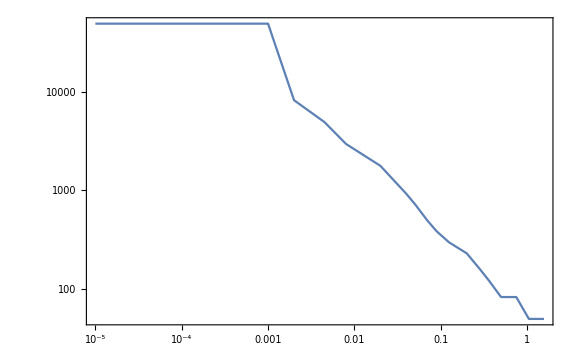

```mathematica
DoubleDistrπ0FCChhdata=Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/FCC-hh/DoubleDistrPi0-FCC-hh.txt"}],"Table"];
Eminπ0dataFCChh=DoubleDistrπ0FCChhdata[[All,2]]//Min;
DoubleDistrπ0FCChhtemp[θπ0_,Eπ0_]=If[Eπ0>Eminπ0dataFCChh,Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@DoubleDistrπ0FCChhdata,InterpolationOrder->1][Log10[θπ0],Log10[Eπ0]])],0];
(*Finding maximal energy for the given polar angle*)
θlistπ0FCChh={10^-3,3*10^-3,6*10^-3,10^-2,3*10^-2,6*10^-2,8*10^-2,0.1,0.15,0.25,0.4,0.6,0.9,1.2,x/.Solve[(x+1.2)/2==Pi/2,x][[1]]}//N;
Eπ0maxFCChhabs=Min[(SortBy[DoubleDistrπ0FCChhdata,-#[[2]]&]//First)[[2]],EpFCChh];
Emaxθπ0=Quiet[eMotherMax[DoubleDistrπ0FCChhtemp,mπ0,Eπ0maxFCChhabs,θlistπ0FCChh,-7]];//AbsoluteTiming
Eπ0maxFCChhhalf[θπ0_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@Emaxθπ0,InterpolationOrder->1][Log10[θπ0]]);
Eπ0maxFCChh[θπ0_]=If[θπ0≤Pi/2,Eπ0maxFCChhhalf[θπ0],Eπ0maxFCChhhalf[Pi-θπ0]];
LogLogPlot[Eπ0maxFCChh[θπ0],{θπ0,10^-5,Pi/2},Frame->True,ImageSize->Large,PlotRange->All]
DoubleDistrπ0FCChh[θπ0_,Eπ0_]=If[10^-5.≤θπ0≤Pi-10^-5.&&mπ0<Eπ0<Eπ0maxFCChh[θπ0],DoubleDistrπ0FCChhtemp[θπ0,Eπ0],0];
```

### Generating points from distribution

#### For decays producing one target particle

```mathematica
π0dataFCChh=BlockPointsFromSmoothDistribution[DoubleDistrπ0FCChh,Emaxθπ0,mπ0,Eπ0maxFCChhhalf,nsim,"True"];//AbsoluteTiming
```

#### For decays producing two FIPs

```mathematica
π0dataFCChhtemp=BlockPointsFromSmoothDistribution[DoubleDistrπ0FCChh,Emaxθπ0,mπ0,Eπ0maxFCChhhalf,nsim/2,"True"];//AbsoluteTiming
π0dataFCChh=Riffle[π0dataFCChhtemp,π0dataFCChhtemp];
```

## K^charged

## SPS

### Importing distribution of K

{4.25895,Null}

{0.0001209,Null}

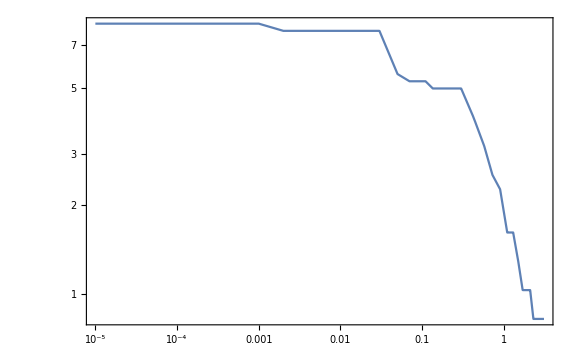

```mathematica
(*The spectrum of kaons is taken from 2004.07974*)
KSPSdata=Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/SPS/DoubleDistrK-SPS.dat"}],"Table"];
{EKSPSmin,EKSPSmax}=MinMax[KSPSdata[[All,2]]];
θKSPSmax=Max[KSPSdata[[All,1]]];
DoubleDistrKatSPStemp[θK_,EK_]=If[EK<EKSPSmin,0,Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@KSPSdata,InterpolationOrder->1][Log10[θK],Log10[EK]])]];
θlistKSPS={10^-3,3*10^-3,6*10^-3,10^-2,2*10^-2,4*10^-2,6*10^-2,8*10^-2,10^-1,0.12,0.15,0.25,0.35,0.5,0.65,0.8,1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3,3.1}//N;
emaxθK=Quiet[eMotherMax[DoubleDistrKatSPStemp,mK,EKSPSmax,θlistKSPS,-5]];//AbsoluteTiming
EKmaxSPS[θK_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@emaxθK,InterpolationOrder->1][Log10[θK]]);//AbsoluteTiming
LogLogPlot[EKmaxSPS[θK],{θK,10^-5,θKSPSmax},Frame->True,ImageSize->Large,PlotRange->All]
DoubleDistrKSPS[θK_,EK_]=If[10^-5.≤θK≤θKSPSmax&&mK<EK<EKmaxSPS[θK],Evaluate[DoubleDistrKatSPStemp[θK,EK]],0];
```

### Generating points from distribution

#### For decays producing one target particle

```mathematica
KdataSPS=BlockPointsFromSmoothDistribution[DoubleDistrKSPS,emaxθK,mK,EKmaxSPS,nsim,"False"];//AbsoluteTiming
```

InterpolatingFunction::dmval: Input value {-3.38572,-0.0980152} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-3.21259,0.646158} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-3.04776,0.887198} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{37.8675,Null}

#### For decays producing two FIPs

```mathematica
(*KdataSPStemp=BlockPointsFromSmoothDistribution[DoubleDistrKSPS,emotherθK,mK,EKmaxSPS,nsim/2,"False"];//AbsoluteTiming*)
```

## η

## FermilabBD

### Distribution

```mathematica
DoubleDistrηFermilabBDdata=Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/FermilabBD/DoubleDistrEtamesons-FermilabBD.dat"}],"Table"];
{EminηdataFermilabBD,EηmaxFermilabBDabs}={Min[DoubleDistrηFermilabBDdata[[All,2]]],Min[120.,Max[DoubleDistrηFermilabBDdata[[All,2]]]]}
DoubleDistrηFermilabBDtemp[θη_,Eη_]=If[Eη>EminηdataFermilabBD,Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@DoubleDistrηFermilabBDdata,InterpolationOrder->1][Log10[θη],Log10[Eη]])],0];
(*Finding maximal energy for the given polar angle*)
θηmaxFermilabBD=Max[DoubleDistrηFermilabBDdata[[All,1]]]
θlistηFermilabBD=Join[{10^-3,3*10^-3,6*10^-3,10^-2,3*10^-2,6*10^-2,10^-1},Table[x,{x,0.12,θηmaxFermilabBD,(θηmaxFermilabBD-0.12)/4}]]//N;
Emaxθη=Quiet[eMotherMax[DoubleDistrηFermilabBDtemp,mη,EηmaxFermilabBDabs,θlistηFermilabBD,-7]];
EηmaxFermilabBD[θη_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@Emaxθη,InterpolationOrder->1][Log10[θη]]);//AbsoluteTiming
LogLogPlot[EηmaxFermilabBD[θη],{θη,10^-5,θηmaxFermilabBD},Frame->True,ImageSize->Large,PlotRange->All]
DoubleDistrηFermilabBD[θη_,Eη_]=If[10^-5.≤θη≤θηmaxFermilabBD&&mη<Eη<EηmaxFermilabBD[θη],DoubleDistrηFermilabBDtemp[θη,Eη],0];
```

### Generating points from distribution

#### For decays producing one target particle

```mathematica
ηdataFermilabBD=BlockPointsFromSmoothDistribution[DoubleDistrηFermilabBD,Emaxθη,mη,EηmaxFermilabBD,nsim,"False"];//AbsoluteTiming
```

#### For decays producing two FIPs

```mathematica
ηdataFermilabBDtemp=BlockPointsFromSmoothDistribution[DoubleDistrηFermilabBD,Emaxθη,mη,EηmaxFermilabBD,nsim/2,"False"];//AbsoluteTiming
ηdataFermilabBD=Riffle[ηdataFermilabBDtemp,ηdataFermilabBDtemp];
```

## SPS

### Distribution

```mathematica
DoubleDistrηSPSdata=Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/SPS/DoubleDistrEtamesons-SPS.dat"}],"Table"];
{EminηdataSPS,EηmaxSPSabs}=MinMax[DoubleDistrηSPSdata[[All,2]]]
DoubleDistrηSPStemp[θη_,Eη_]=If[Eη>EminηdataSPS,Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@DoubleDistrηSPSdata,InterpolationOrder->1][Log10[θη],Log10[Eη]])],0];
(*Finding maximal energy for the given polar angle*)
θηmaxSPS=DoubleDistrηSPSdata[[All,1]]//Max
θlistηSPS=Join[{10^-3,3*10^-3,6*10^-3,10^-2,3*10^-2,6*10^-2,10^-1,2*10^-1,4*10^-1,6*10^-1,8*10^-1,1.},Table[x,{x,1.2,θηmaxSPS,(θηmaxSPS-1.2)/4}]]//N;
Emaxθη=Quiet[eMotherMax[DoubleDistrηSPStemp,mη,EηmaxSPSabs,θlistηSPS,-7]];//AbsoluteTiming
EηmaxSPS[θη_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@Emaxθη,InterpolationOrder->1][Log10[θη]]);
LogLogPlot[EηmaxSPS[θη],{θη,10^-5,θηmaxSPS},Frame->True,ImageSize->Large,PlotRange->All]
DoubleDistrηSPS[θη_,Eη_]=If[10^-5.≤θη≤θηmaxSPS&&mη<Eη<EηmaxSPS[θη],DoubleDistrηSPStemp[θη,Eη],0];
```

### Generating points from distribution

#### For decays producing one target particle

```mathematica
ηdataSPS=BlockPointsFromSmoothDistribution[DoubleDistrηSPS,Emaxθη,mη,EηmaxSPS,nsim,"False"];//AbsoluteTiming
```

#### For decays producing two FIPs

```mathematica
ηdataSPStemp=BlockPointsFromSmoothDistribution[DoubleDistrηSPS,Emaxθη,mη,EηmaxSPS,nsim/2,"False"];//AbsoluteTiming
ηdataSPS=Riffle[ηdataSPStemp,ηdataSPStemp];
```

## LHC

### Distribution

```mathematica
DoubleDistrηLHCdata=Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/LHC/DoubleDistrEtamesons-LHC.dat"}],"Table"];
{EminηdataLHC,EηmaxLHCabs}=MinMax[DoubleDistrηLHCdata[[All,2]]]
DoubleDistrηLHCtemp[θη_,Eη_]=If[Eη>EminηdataLHC,Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@DoubleDistrηLHCdata,InterpolationOrder->1][Log10[θη],Log10[Eη]])],0];
(*Finding maximal energy for the given polar angle*)
θηmaxLHC=DoubleDistrηLHCdata[[All,1]]//Max;
θlistηLHC={10^-3,3*10^-3,6*10^-3,10^-2,3*10^-2,6*10^-2,8*10^-2,0.1,0.15,0.25,0.4,0.6,0.9,1.2,x/.Solve[(x+1.2)/2==Pi/2,x][[1]]}//N;
Emaxθη=Quiet[eMotherMax[DoubleDistrηLHCtemp,mη,EηmaxLHCabs,θlistηLHC,-7]];//AbsoluteTiming
EηmaxLHChalf[θη_]=Quiet[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@Emaxθη,InterpolationOrder->1][Log10[θη]])];//AbsoluteTiming
EηmaxLHC[θη_]=If[θη≤Pi/2,EηmaxLHChalf[θη],EηmaxLHChalf[Pi-θη]];
LogLogPlot[EηmaxLHC[θη],{θη,10^-5,Pi/2},Frame->True,ImageSize->Large,PlotRange->All]
DoubleDistrηLHC[θη_,Eη_]=If[10^-5.≤θη≤Pi-10^-5.&&mη<Eη<EηmaxLHC[θη],DoubleDistrηLHCtemp[θη,Eη],0];
```

### Generating points from distribution

#### For decays producing one target particle

```mathematica
ηdataLHC=BlockPointsFromSmoothDistribution[DoubleDistrηLHC,Emaxθη,mη,EηmaxLHChalf,nsim,"True"];//AbsoluteTiming
```

#### For decays producing two target particles

```mathematica
ηdataLHCtemp=BlockPointsFromSmoothDistribution[DoubleDistrηLHC,Emaxθη,mη,EηmaxLHChalf,nsim/2,"True"];//AbsoluteTiming
ηdataLHC=Riffle[ηdataLHCtemp,ηdataLHCtemp];
```

## FCC-hh

### Distribution

{19.8949,Null}

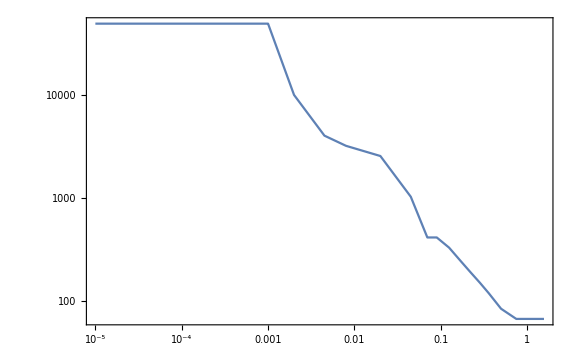

```mathematica
DoubleDistrηFCChhdata=Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/FCC-hh/DoubleDistrEta-FCC-hh.txt"}],"Table"];
{EminηdataFCChh,EηmaxFCChhabs}={Min[DoubleDistrηFCChhdata[[All,2]]],Min[50000.,Max[DoubleDistrηFCChhdata[[All,2]]]]};
DoubleDistrηFCChhtemp[θη_,Eη_]=If[Eη>EminηdataFCChh,Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@DoubleDistrηFCChhdata,InterpolationOrder->1][Log10[θη],Log10[Eη]])],0];
(*Finding maximal energy for the given polar angle*)
θηmaxFCChh=Max[DoubleDistrηFCChhdata[[All,1]]];
θlistηFCChh={10^-3,3*10^-3,6*10^-3,10^-2,3*10^-2,6*10^-2,8*10^-2,0.1,0.15,0.25,0.4,0.6,0.9,1.2,x/.Solve[(x+1.2)/2==Pi/2,x][[1]]}//N;
Emaxθη=Quiet[eMotherMax[DoubleDistrηFCChhtemp,mη,EηmaxFCChhabs,θlistηFCChh,-7]];//AbsoluteTiming
EηmaxFCChhhalf[θη_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@Emaxθη,InterpolationOrder->1][Log10[θη]]);
EηmaxFCChh[θη_]=If[θη≤Pi/2,EηmaxFCChhhalf[θη],EηmaxFCChhhalf[Pi-θη]];
LogLogPlot[EηmaxFCChh[θη],{θη,10^-5,Pi/2},Frame->True,ImageSize->Large,PlotRange->All]
DoubleDistrηFCChh[θη_,Eη_]=If[10^-5.≤θη≤Pi-10^-5.&&mη<Eη<EηmaxFCChh[θη],DoubleDistrηFCChhtemp[θη,Eη],0];
```

### Generating points from distribution

#### For decays producing one target particle

```mathematica
ηdataFCChh=BlockPointsFromSmoothDistribution[DoubleDistrηFCChh,Emaxθη,mη,EηmaxFCChhhalf,nsim,"True"];//AbsoluteTiming
```

#### For decays producing two target particles

```mathematica
ηdataFCChhtemp=BlockPointsFromSmoothDistribution[DoubleDistrηFCChh,Emaxθη,mη,EηmaxFCChhhalf,nsim/2,"True"];//AbsoluteTiming
ηdataFCChh=Riffle[ηdataFCChhtemp,ηdataFCChhtemp];
```

## η’

## FermilabBD

### Distribution

```mathematica
DoubleDistrηprFermilabBDdata=Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/FermilabBD/DoubleDistrEtaPrmesons-FermilabBD.dat"}],"Table"];
{EminηprdataFermilabBD,EηprmaxFermilabBDabs}={Min[DoubleDistrηprFermilabBDdata[[All,2]]],Min[Max[DoubleDistrηprFermilabBDdata[[All,2]]],120.]}
DoubleDistrηprFermilabBDtemp[θηpr_,Eηpr_]=If[Eηpr>EminηprdataFermilabBD,Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@DoubleDistrηprFermilabBDdata,InterpolationOrder->1][Log10[θηpr],Log10[Eηpr]])],0];
(*Finding maximal energy for the given polar angle*)
θηprmaxFermilabBD=Max[DoubleDistrηprFermilabBDdata[[All,1]]]
θlistηprFermilabBD={10^-3,3*10^-3,6*10^-3,10^-2,3*10^-2,6*10^-2,10^-1,2*10^-1,4*10^-1,6*10^-1,8*10^-1,1.}//N;
Emaxθηpr=Quiet[eMotherMax[DoubleDistrηprFermilabBDtemp,mηpr,EηprmaxFermilabBDabs,θlistηprFermilabBD,-7]];//AbsoluteTiming
EηprmaxFermilabBD[θηpr_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@Emaxθηpr,InterpolationOrder->1][Log10[θηpr]]);
LogLogPlot[EηprmaxFermilabBD[θηpr],{θηpr,10^-5,θηprmaxFermilabBD},Frame->True,ImageSize->Large,PlotRange->All]
DoubleDistrηprFermilabBD[θηpr_,Eηpr_]=If[10^-5.≤θηpr≤θηprmaxFermilabBD&&mηpr<Eηpr<EηprmaxFermilabBD[θηpr],DoubleDistrηprFermilabBDtemp[θηpr,Eηpr],0];
```

### Generating points from distribution

#### For decays producing one target particle

```mathematica
ηprdataFermilabBD=BlockPointsFromSmoothDistribution[DoubleDistrηprFermilabBD,Emaxθηpr,mηpr,EηprmaxFermilabBD,nsim,"False"];//AbsoluteTiming
```

#### For decays producing two target particles

## SPS

### Distribution

```mathematica
DoubleDistrηprSPSdata=Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/SPS/DoubleDistrEtaPrmesons-SPS.dat"}],"Table"];
{EminηprdataSPS,EηprmaxSPSabs}=MinMax[DoubleDistrηprSPSdata[[All,2]]]
DoubleDistrηprSPStemp[θηpr_,Eηpr_]=If[Eηpr>EminηprdataSPS,Evaluate[10^(Interpolation[{#[[1]],#[[2]],Log10[#[[3]]+10^-90]}&/@DoubleDistrηprSPSdata,InterpolationOrder->1][θηpr,Eηpr])],0];
(*Finding maximal energy for the given polar angle*)
θηprmaxSPS=Max[DoubleDistrηprSPSdata[[All,1]]]
θlistηprSPS={10^-3,3*10^-3,6*10^-3,10^-2,3*10^-2,6*10^-2,10^-1,2*10^-1,4*10^-1,6*10^-1,8*10^-1,1.,θηprmaxSPS}//N;
EηprmaxSPSabs=Min[(SortBy[DoubleDistrηprSPSdata,-#[[2]]&]//First)[[2]],EpSPS];
Emaxθηpr=Quiet[eMotherMax[DoubleDistrηprSPStemp,mηpr,EηprmaxSPSabs,θlistηprSPS,-9]];//AbsoluteTiming
EηprmaxSPS[θηpr_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@Emaxθηpr,InterpolationOrder->1][Log10[θηpr]]);
LogLogPlot[EηprmaxSPS[θηpr],{θηpr,10^-5,θηprmaxSPS},Frame->True,ImageSize->Large,PlotRange->All]
DoubleDistrηprSPS[θηpr_,Eηpr_]=If[10^-5.≤θηpr≤θηprmaxSPS&&mηpr<Eηpr<EηprmaxSPS[θηpr],DoubleDistrηprSPStemp[θηpr,Eηpr],0];
```

### Generating points from distribution

#### For decays producing one target particle

```mathematica
ηprdataSPS=BlockPointsFromSmoothDistribution[DoubleDistrηprSPS,Emaxθηpr,mηpr,EηprmaxSPS,nsim,"False"];//AbsoluteTiming
```

#### For decays producing two target particles

## LHC

### Distribution

```mathematica
DoubleDistrηprLHCdata=Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/LHC/DoubleDistrEtaPrmesons-LHC.dat"}],"Table"];
{EminηprdataLHC,EηprmaxLHCabs}=MinMax[DoubleDistrηprLHCdata[[All,2]]];
DoubleDistrηprLHCtemp[θηpr_,Eηpr_]=If[Eηpr>EminηprdataLHC,Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@DoubleDistrηprLHCdata,InterpolationOrder->1][Log10[θηpr],Log10[Eηpr]])],0];
(*Finding maximal energy for the given polar angle*)
θηprmaxLHC=Max[DoubleDistrηprLHCdata[[All,1]]];
θlistηprLHC={10^-3,3*10^-3,6*10^-3,10^-2,3*10^-2,6*10^-2,8*10^-2,0.1,0.15,0.25,0.4,0.6,0.9,1.2,x/.Solve[(x+1.2)/2==Pi/2,x][[1]]}//N;
Emaxθηpr=Quiet[eMotherMax[DoubleDistrηprLHCtemp,mηpr,EηprmaxLHCabs,θlistηprLHC,-7]];//AbsoluteTiming
EηprmaxLHChalf[θηpr_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@Emaxθηpr,InterpolationOrder->1][Log10[θηpr]]);
EηprmaxLHC[θηpr_]=If[θηpr≤Pi/2,EηprmaxLHChalf[θηpr],EηprmaxLHChalf[Pi-θηpr]];
LogLogPlot[EηprmaxLHC[θηpr],{θηpr,10^-5,Pi/2},Frame->True,ImageSize->Large,PlotRange->All]
DoubleDistrηprLHC[θηpr_,Eηpr_]=If[10^-5.≤θηpr≤Pi-10^-5.&&mηpr<Eηpr<EηprmaxLHC[θηpr],DoubleDistrηprLHCtemp[θηpr,Eηpr],0];
```

### Generating points from distribution

#### For decays producing one target particle

```mathematica
ηprdataLHC=BlockPointsFromSmoothDistribution[DoubleDistrηprLHC,Emaxθηpr,mηpr,EηprmaxLHChalf,nsim,"True"];//AbsoluteTiming
```

#### For decays producing two target particles

## FCC-hh

### Distribution

{0.97614,50000.}

{19.8993,Null}

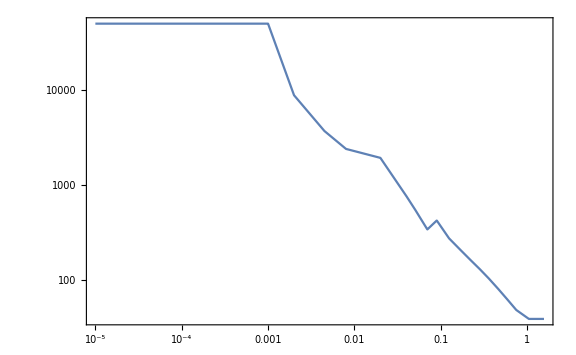

```mathematica
DoubleDistrηprFCChhdata=Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/FCC-hh/DoubleDistrEtapr-FCC-hh.txt"}],"Table"];
{EminηprdataFCChh,EηprmaxFCChhabs}={DoubleDistrηprFCChhdata[[All,2]]//Min,Min[DoubleDistrηprFCChhdata[[All,2]]//Max,50000.]}
DoubleDistrηprFCChhtemp[θηpr_,Eηpr_]=If[Eηpr>EminηprdataFCChh,Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@DoubleDistrηprFCChhdata,InterpolationOrder->1][Log10[θηpr],Log10[Eηpr]])],0];
(*Finding maximal energy for the given polar angle*)
θηprmaxFCChh=DoubleDistrηprFCChhdata[[All,1]]//Max;
θlistηprFCChh={10^-3,3*10^-3,6*10^-3,10^-2,3*10^-2,6*10^-2,8*10^-2,0.1,0.15,0.25,0.4,0.6,0.9,1.2,x/.Solve[(x+1.2)/2==Pi/2,x][[1]]}//N;
Emaxθηpr=Quiet[eMotherMax[DoubleDistrηprFCChhtemp,mηpr,EηprmaxFCChhabs,θlistηprFCChh,-7]];//AbsoluteTiming
EηprmaxFCChhhalf[θηpr_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@Emaxθηpr,InterpolationOrder->1][Log10[θηpr]]);
EηprmaxFCChh[θηpr_]=If[θηpr≤Pi/2,EηprmaxFCChhhalf[θηpr],EηprmaxFCChhhalf[Pi-θηpr]];
LogLogPlot[EηprmaxFCChh[θηpr],{θηpr,10^-5,Pi/2},Frame->True,ImageSize->Large,PlotRange->All]
DoubleDistrηprFCChh[θηpr_,Eηpr_]=If[10^-5.≤θηpr≤Pi-10^-5.&&mηpr<Eηpr<EηprmaxFCChh[θηpr],DoubleDistrηprFCChhtemp[θηpr,Eηpr],0];
```

### Generating points from distribution

#### For decays producing one target particle

```mathematica
ηprdataFCChh=BlockPointsFromSmoothDistribution[DoubleDistrηprFCChh,Emaxθηpr,mηpr,EηprmaxFCChhhalf,nsim,"True"];//AbsoluteTiming
```

#### For decays producing two target particles

## ρ^0

## FermilabBD

### Distribution

```mathematica
DoubleDistrρ0FermilabBDdata=Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/FermilabBD/DoubleDistrRho0mesons-FermilabBD.dat"}],"Table"];
{Eminρ0dataFermilabBD,Eρ0maxFermilabBDabs}={Min[DoubleDistrρ0FermilabBDdata[[All,2]]],Min[Max[DoubleDistrρ0FermilabBDdata[[All,2]]],120.]};
DoubleDistrρ0FermilabBDtemp[θρ0_,Eρ0_]=If[Eρ0>Eminρ0dataFermilabBD,Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@DoubleDistrρ0FermilabBDdata,InterpolationOrder->1][Log10[θρ0],Log10[Eρ0]])],0];
(*Finding maximal energy for the given polar angle*)
θρ0maxFermilabBD=Max[DoubleDistrρ0FermilabBDdata[[All,1]]];
θlistρ0FermilabBD=Join[{10^-3,3*10^-3,6*10^-3,10^-2,3*10^-2,6*10^-2,8*10^-2,0.1},Table[x,{x,0.12,θρ0maxFermilabBD,(θρ0maxFermilabBD-0.12)/4}]]//N;
Emaxθρ0=Quiet[eMotherMax[DoubleDistrρ0FermilabBDtemp,mρ0,Eρ0maxFermilabBDabs,θlistρ0FermilabBD,-5]];//AbsoluteTiming
Eρ0maxFermilabBD[θρ0_]=Quiet[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@Emaxθρ0,InterpolationOrder->1][Log10[θρ0]])];//AbsoluteTiming
LogLogPlot[Eρ0maxFermilabBD[θρ0],{θρ0,10^-5,θρ0maxFermilabBD},Frame->True,ImageSize->Large,PlotRange->All]
DoubleDistrρ0FermilabBD[θρ0_,Eρ0_]=If[10^-5.≤θρ0≤θρ0maxFermilabBD&&mρ0<Eρ0<Eρ0maxFermilabBD[θρ0],DoubleDistrρ0FermilabBDtemp[θρ0,Eρ0],0];
```

### Generating points from distribution

#### For decays producing one target particle

#### For decays producing two target particles

```mathematica
ρ0dataFermilabBDtemp=BlockPointsFromSmoothDistribution[DoubleDistrρ0FermilabBD,Emaxθρ0,mρ0,Eρ0maxFermilabBD,nsim/2,"False"];//AbsoluteTiming
ρ0dataFermilabBD=Riffle[ρ0dataFermilabBDtemp,ρ0dataFermilabBDtemp];
```

## SPS

### Distribution

```mathematica
DoubleDistrρ0SPSdata=Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/SPS/DoubleDistrRho0mesons-SPS.dat"}],"Table"];
{Eminρ0dataSPS,Eρ0maxSPSabs}=MinMax[DoubleDistrρ0SPSdata[[All,2]]];
DoubleDistrρ0SPStemp[θρ0_,Eρ0_]=If[Eρ0>Eminρ0dataSPS,Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@DoubleDistrρ0SPSdata,InterpolationOrder->1][Log10[θρ0],Log10[Eρ0]])],0];
(*Finding maximal energy for the given polar angle*)
θρ0maxSPS=Max[DoubleDistrρ0SPSdata[[All,1]]]
θlistρ0SPS=Join[{10^-3,3*10^-3,6*10^-3,10^-2,3*10^-2,6*10^-2,10^-1,2*10^-1,4*10^-1,6*10^-1,8*10^-1,1.},Table[x,{x,1.2,0.9θρ0maxSPS,(0.9θρ0maxSPS-1.2)/4}]]//N;
Emaxθρ0=Quiet[eMotherMax[DoubleDistrρ0SPStemp,mρ0,Eρ0maxSPSabs,θlistρ0SPS,-7]];//AbsoluteTiming
Eρ0maxSPS[θρ0_]=Quiet[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@Emaxθρ0,InterpolationOrder->1][Log10[θρ0]])];//AbsoluteTiming
LogLogPlot[Eρ0maxSPS[θρ0],{θρ0,10^-5,θρ0maxSPS},Frame->True,ImageSize->Large,PlotRange->All]
DoubleDistrρ0SPS[θρ0_,Eρ0_]=If[10^-5.≤θρ0≤θρ0maxSPS&&mρ0<Eρ0<Eρ0maxSPS[θρ0],DoubleDistrρ0SPStemp[θρ0,Eρ0],0];
```

### Generating points from distribution

#### For decays producing one target particle

#### For decays producing two target particles

```mathematica
ρ0dataSPStemp=BlockPointsFromSmoothDistribution[DoubleDistrρ0SPS,Emaxθρ0,mρ0,Eρ0maxSPS,nsim/2,"False"];//AbsoluteTiming
ρ0dataSPS=Riffle[ρ0dataSPStemp,ρ0dataSPStemp];
```

## LHC

### Distribution

```mathematica
DoubleDistrρ0LHCdata=Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/LHC/DoubleDistrRho0mesons-LHC.dat"}],"Table"];
{Eminρ0dataLHC,Eρ0maxLHCabs}=MinMax[DoubleDistrρ0LHCdata[[All,2]]];
DoubleDistrρ0LHCtemp[θρ0_,Eρ0_]=If[Eρ0>Eminρ0dataLHC,Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@DoubleDistrρ0LHCdata,InterpolationOrder->1][Log10[θρ0],Log10[Eρ0]])],0];
(*Finding maximal energy for the given polar angle*)
θρ0maxLHC=DoubleDistrρ0LHCdata[[All,1]]//Max;
θlistρ0LHC={10^-3,3*10^-3,6*10^-3,10^-2,3*10^-2,6*10^-2,8*10^-2,0.1,0.15,0.25,0.4,0.6,0.9,1.2,1.55}//N;
Eθmaxρ0=Quiet[eMotherMax[DoubleDistrρ0LHCtemp,mρ0,Eρ0maxLHCabs,θlistρ0LHC,-5]];//AbsoluteTiming
Eρ0maxLHChalf[θρ0_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@Eθmaxρ0,InterpolationOrder->1][Log10[θρ0]]);
Eρ0maxLHC[θρ0_]=If[θρ0≤Pi/2,Eρ0maxLHChalf[θρ0],Eρ0maxLHChalf[Pi-θρ0]];
LogLogPlot[Eρ0maxLHC[θρ0],{θρ0,10^-5,Pi/2},Frame->True,ImageSize->Large,PlotRange->All]
DoubleDistrρ0LHC[θρ0_,Eρ0_]=If[10^-5.≤θρ0≤Pi-10^-5.&&mρ0<Eρ0<Eρ0maxLHC[θρ0],DoubleDistrρ0LHCtemp[θρ0,Eρ0],0];
```

### Generating points from distribution

#### For decays producing one target particle

#### For decays producing two target particles

```mathematica
ρ0dataLHCtemp=BlockPointsFromSmoothDistribution[DoubleDistrρ0LHC,Emaxθρ0,mρ0,Eρ0maxLHChalf,nsim/2,"True"];//AbsoluteTiming
ρ0dataLHC=Riffle[ρ0dataLHCtemp,ρ0dataLHCtemp];
```

## FCC-hh

### Distribution

```mathematica
DoubleDistrρ0FCChhdata=Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/FCC-hh/DoubleDistrRho0-FCC-hh.txt"}],"Table"];
{Eminρ0dataFCChh,Eρ0maxFCChhabs}={Min[DoubleDistrρ0FCChhdata[[All,2]]],Min[50000.,Max[DoubleDistrρ0FCChhdata[[All,2]]]]}
DoubleDistrρ0FCChhtemp[θρ0_,Eρ0_]=If[Eρ0>Eminρ0dataFCChh,Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@DoubleDistrρ0FCChhdata,InterpolationOrder->1][Log10[θρ0],Log10[Eρ0]])],0];
(*Finding maximal energy for the given polar angle*)
θlistρ0FCChh={10^-3,3*10^-3,6*10^-3,10^-2,3*10^-2,6*10^-2,8*10^-2,0.1,0.15,0.25,0.4,0.6,0.9,1.2,1.55}//N;
Emaxθρ0=Quiet[eMotherMax[DoubleDistrρ0FCChhtemp,mρ0,Eρ0maxFCChhabs,θlistρ0FCChh,-5]];//AbsoluteTiming
Eρ0maxFCChhhalf[θρ0_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@Emaxθρ0,InterpolationOrder->1][Log10[θρ0]]);
Eρ0maxFCChh[θρ0_]=If[θρ0≤Pi/2,Eρ0maxFCChhhalf[θρ0],Eρ0maxFCChhhalf[Pi-θρ0]];
LogLogPlot[Eρ0maxFCChh[θρ0],{θρ0,10^-5.,Pi/2},Frame->True,ImageSize->Large,PlotRange->All]
DoubleDistrρ0FCChh[θρ0_,Eρ0_]=If[10^-5.≤θρ0≤Pi-10^-5.&&mρ0<Eρ0<Eρ0maxFCChh[θρ0],DoubleDistrρ0FCChhtemp[θρ0,Eρ0],0];
```

### Generating points from distribution

#### For decays producing one target particle

#### For decays producing two target particles

```mathematica
ρ0dataFCChhtemp=BlockPointsFromSmoothDistribution[DoubleDistrρ0FCChh,Emaxθρ0,mρ0,Eρ0maxFCChhhalf,nsim/2,"True"];//AbsoluteTiming
ρ0dataFCChh=Riffle[ρ0dataFCChhtemp,ρ0dataFCChhtemp];
```

## ω

## FermilabBD

### Distribution

```mathematica
DoubleDistrωFermilabBDdata=Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/FermilabBD/DoubleDistrOmegamesons-FermilabBD.dat"}],"Table"];
{EminωdataFermilabBD,EωmaxFermilabBDabs}={Min[DoubleDistrωFermilabBDdata[[All,2]]],Min[Max[DoubleDistrωFermilabBDdata[[All,2]]],120.]};
DoubleDistrωFermilabBDtemp[θω_,Eω_]=If[Eω>EminωdataFermilabBD,Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@DoubleDistrωFermilabBDdata,InterpolationOrder->1][Log10[θω],Log10[Eω]])],0];
(*Finding maximal energy for the given polar angle*)
θωmaxFermilabBD=Max[DoubleDistrωFermilabBDdata[[All,1]]];
θlistωFermilabBD=Join[{10^-3,3*10^-3,6*10^-3,10^-2,3*10^-2,6*10^-2,8*10^-2,0.1},Table[x,{x,0.12,θωmaxFermilabBD,(θωmaxFermilabBD-0.12)/4}]]//N;
Emaxθω=Quiet[eMotherMax[DoubleDistrωFermilabBDtemp,mω,EωmaxFermilabBDabs,θlistωFermilabBD,-5]];//AbsoluteTiming
EωmaxFermilabBD[θω_]=Quiet[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@Emaxθω,InterpolationOrder->1][Log10[θω]])];//AbsoluteTiming
LogLogPlot[EωmaxFermilabBD[θω],{θω,10^-5,θωmaxFermilabBD},Frame->True,ImageSize->Large,PlotRange->All]
DoubleDistrωFermilabBD[θω_,Eω_]=If[10^-5.≤θω≤θωmaxFermilabBD&&mω<Eω<EωmaxFermilabBD[θω],DoubleDistrωFermilabBDtemp[θω,Eω],0];
```

### Generating points from distribution

#### For decays producing one target particle

#### For decays producing two target particles

```mathematica
ωdataFermilabBDtemp=BlockPointsFromSmoothDistribution[DoubleDistrωFermilabBD,Emaxθω,mω,EωmaxFermilabBD,nsim/2,"False"];//AbsoluteTiming
ωdataFermilabBD=Riffle[ωdataFermilabBDtemp,ωdataFermilabBDtemp];
```

## SPS

### Distribution

```mathematica
DoubleDistrωSPSdata=Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/SPS/DoubleDistrOmegamesons-SPS.dat"}],"Table"];
{EminωdataSPS,EωmaxSPSabs}=MinMax[DoubleDistrωSPSdata[[All,2]]];
DoubleDistrωSPStemp[θω_,Eω_]=If[Eω>EminωdataSPS,Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@DoubleDistrωSPSdata,InterpolationOrder->1][Log10[θω],Log10[Eω]])],0];
(*Finding maximal energy for the given polar angle*)
θωmaxSPS=Max[DoubleDistrωSPSdata[[All,1]]]
θlistωSPS=Join[{10^-3,3*10^-3,6*10^-3,10^-2,3*10^-2,6*10^-2,10^-1,2*10^-1,4*10^-1,6*10^-1,8*10^-1,1.},Table[x,{x,1.2,0.9θωmaxSPS,(0.9θωmaxSPS-1.2)/4}]]//N;
Emaxθω=Quiet[eMotherMax[DoubleDistrωSPStemp,mω,EωmaxSPSabs,θlistωSPS,-7]];//AbsoluteTiming
EωmaxSPS[θω_]=Quiet[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@Emaxθω,InterpolationOrder->1][Log10[θω]])];//AbsoluteTiming
LogLogPlot[EωmaxSPS[θω],{θω,10^-5,θωmaxSPS},Frame->True,ImageSize->Large,PlotRange->All]
DoubleDistrωSPS[θω_,Eω_]=If[10^-5.≤θω≤θωmaxSPS&&mω<Eω<EωmaxSPS[θω],DoubleDistrωSPStemp[θω,Eω],0];
```

### Generating points from distribution

#### For decays producing one target particle

#### For decays producing two target particles

```mathematica
ωdataSPStemp=BlockPointsFromSmoothDistribution[DoubleDistrωSPS,Emaxθω,mω,EωmaxSPS,nsim/2,"False"];//AbsoluteTiming
ωdataSPS=Riffle[ωdataSPStemp,ωdataSPStemp];
```

## LHC

### Distribution

```mathematica
DoubleDistrωLHCdata=Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/LHC/DoubleDistrOmegamesons-LHC.dat"}],"Table"];
{EminωdataLHC,EωmaxLHCabs}=MinMax[DoubleDistrωLHCdata[[All,2]]];
DoubleDistrωLHCtemp[θω_,Eω_]=If[Eω>EminωdataLHC,Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@DoubleDistrωLHCdata,InterpolationOrder->1][Log10[θω],Log10[Eω]])],0];
(*Finding maximal energy for the given polar angle*)
θωmaxLHC=DoubleDistrωLHCdata[[All,1]]//Max;
θlistωLHC={10^-3,3*10^-3,6*10^-3,10^-2,3*10^-2,6*10^-2,8*10^-2,0.1,0.15,0.25,0.4,0.6,0.9,1.2,1.55}//N;
Eθmaxω=Quiet[eMotherMax[DoubleDistrωLHCtemp,mω,EωmaxLHCabs,θlistωLHC,-5]];//AbsoluteTiming
EωmaxLHChalf[θω_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@Eθmaxω,InterpolationOrder->1][Log10[θω]]);
EωmaxLHC[θω_]=If[θω≤Pi/2,EωmaxLHChalf[θω],EωmaxLHChalf[Pi-θω]];
LogLogPlot[EωmaxLHC[θω],{θω,10^-5,Pi/2},Frame->True,ImageSize->Large,PlotRange->All]
DoubleDistrωLHC[θω_,Eω_]=If[10^-5.≤θω≤Pi-10^-5.&&mω<Eω<EωmaxLHC[θω],DoubleDistrωLHCtemp[θω,Eω],0];
```

### Generating points from distribution

#### For decays producing one target particle

#### For decays producing two target particles

```mathematica
ωdataLHCtemp=BlockPointsFromSmoothDistribution[DoubleDistrωLHC,Emaxθω,mω,EωmaxLHChalf,nsim/2,"True"];//AbsoluteTiming
ωdataLHC=Riffle[ωdataLHCtemp,ωdataLHCtemp];
```

## FCC-hh

### Distribution

```mathematica
DoubleDistrωFCChhdata=Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/FCC-hh/DoubleDistrOmega-FCC-hh.txt"}],"Table"];
{EminωdataFCChh,EωmaxFCChhabs}={Min[DoubleDistrωFCChhdata[[All,2]]],Min[50000.,Max[DoubleDistrωFCChhdata[[All,2]]]]}
DoubleDistrωFCChhtemp[θω_,Eω_]=If[Eω>EminωdataFCChh,Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@DoubleDistrωFCChhdata,InterpolationOrder->1][Log10[θω],Log10[Eω]])],0];
(*Finding maximal energy for the given polar angle*)
θlistωFCChh={10^-3,3*10^-3,6*10^-3,10^-2,3*10^-2,6*10^-2,8*10^-2,0.1,0.15,0.25,0.4,0.6,0.9,1.2,1.55}//N;
Emaxθω=Quiet[eMotherMax[DoubleDistrωFCChhtemp,mω,EωmaxFCChhabs,θlistωFCChh,-5]];//AbsoluteTiming
EωmaxFCChhhalf[θω_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@Emaxθω,InterpolationOrder->1][Log10[θω]]);
EωmaxFCChh[θω_]=If[θω≤Pi/2,EωmaxFCChhhalf[θω],EωmaxFCChhhalf[Pi-θω]];
LogLogPlot[EωmaxFCChh[θω],{θω,10^-5.,Pi/2},Frame->True,ImageSize->Large,PlotRange->All]
DoubleDistrωFCChh[θω_,Eω_]=If[10^-5.≤θω≤Pi-10^-5.&&mω<Eω<EωmaxFCChh[θω],DoubleDistrωFCChhtemp[θω,Eω],0];
```

### Generating points from distribution

#### For decays producing one target particle

#### For decays producing two target particles

```mathematica
ωdataFCChhtemp=BlockPointsFromSmoothDistribution[DoubleDistrωFCChh,Emaxθω,mω,EωmaxFCChhhalf,nsim/2,"True"];//AbsoluteTiming
ωdataFCChh=Riffle[ωdataFCChhtemp,ωdataFCChhtemp];
```

## ϕ

## FermilabBD

### Distribution

```mathematica
DoubleDistrϕFermilabBDdata=Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/FermilabBD/DoubleDistrPhimesons-FermilabBD.dat"}],"Table"];
{EminϕdataFermilabBD,EϕmaxFermilabBDabs}=DoubleDistrϕFermilabBDdata[[All,2]]//MinMax;
DoubleDistrϕFermilabBDtemp[θϕ_,Eϕ_]=If[Eϕ>EminϕdataFermilabBD,Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@DoubleDistrϕFermilabBDdata,InterpolationOrder->1][Log10[θϕ],Log10[Eϕ]])],0];
(*Finding maximal energy for the given polar angle*)
θϕmaxFermilabBD=DoubleDistrϕFermilabBDdata[[All,1]]//Max;
θlistϕFermilabBD=Join[{10^-3,3*10^-3,6*10^-3,10^-2,3*10^-2,6*10^-2,8*10^-2,0.1},Table[x,{x,0.12,θϕmaxFermilabBD,(θϕmaxFermilabBD-0.12)/4}]]//N;
Emaxθϕ=Quiet[eMotherMax[DoubleDistrϕFermilabBDtemp,mϕ,EϕmaxFermilabBDabs,θlistϕFermilabBD,-5]];//AbsoluteTiming
EϕmaxFermilabBD[θϕ_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@Emaxθϕ,InterpolationOrder->1][Log10[θϕ]]);
LogLogPlot[EϕmaxFermilabBD[θϕ],{θϕ,10^-5,θϕmaxFermilabBD},Frame->True,ImageSize->Large,PlotRange->All]
DoubleDistrϕFermilabBD[θϕ_,Eϕ_]=If[10^-5.≤θϕ≤θϕmaxFermilabBD&&mϕ<Eϕ<EϕmaxFermilabBD[θϕ],DoubleDistrϕFermilabBDtemp[θϕ,Eϕ],0];
```

### Generating points from distribution

#### For decays producing one target particle

#### For decays producing two target particles

```mathematica
ϕdataFermilabBDtemp=BlockPointsFromSmoothDistribution[DoubleDistrϕFermilabBD,Emaxθϕ,mϕ,EϕmaxFermilabBD,nsim/2,"False"];//AbsoluteTiming
ϕdataFermilabBD=Riffle[ϕdataFermilabBDtemp,ϕdataFermilabBDtemp];
```

## SPS

### Distribution

```mathematica
DoubleDistrϕSPSdata=Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/SPS/DoubleDistrPhimesons-SPS.dat"}],"Table"];
{EminϕdataSPS,EϕmaxSPSabs}=DoubleDistrϕSPSdata[[All,2]]//MinMax;
DoubleDistrϕSPStemp[θϕ_,Eϕ_]=If[Eϕ>EminϕdataSPS,Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@DoubleDistrϕSPSdata,InterpolationOrder->1][Log10[θϕ],Log10[Eϕ]])],0];
(*Finding maximal energy for the given polar angle*)
θϕmaxSPS=DoubleDistrϕSPSdata[[All,1]]//Max;
θlistϕSPS=Join[{10^-3,3*10^-3,6*10^-3,10^-2,3*10^-2,6*10^-2,8*10^-2,0.1},Table[x,{x,0.12,θϕmaxSPS,(θϕmaxSPS-0.12)/4}]]//N;
Emaxθϕ=Quiet[eMotherMax[DoubleDistrϕSPStemp,mϕ,EϕmaxSPSabs,θlistϕSPS,-5]];//AbsoluteTiming
EϕmaxSPS[θϕ_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@Emaxθϕ,InterpolationOrder->1][Log10[θϕ]]);
LogLogPlot[EϕmaxSPS[θϕ],{θϕ,10^-5,θϕmaxSPS},Frame->True,ImageSize->Large,PlotRange->All]
DoubleDistrϕSPS[θϕ_,Eϕ_]=If[10^-5.≤θϕ≤θϕmaxSPS&&mϕ<Eϕ<EϕmaxSPS[θϕ],DoubleDistrϕSPStemp[θϕ,Eϕ],0];
```

### Generating points from distribution

#### For decays producing one target particle

#### For decays producing two target particles

```mathematica
ϕdataSPStemp=BlockPointsFromSmoothDistribution[DoubleDistrϕSPS,Emaxθϕ,mϕ,EϕmaxSPS,nsim/2,"False"];//AbsoluteTiming
ϕdataSPS=Riffle[ϕdataSPStemp,ϕdataSPStemp];
```

## LHC

### Distribution

```mathematica
DoubleDistrϕLHCdata=Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/LHC/DoubleDistrPhi-LHC.txt"}],"Table"];
EminϕdataLHC=DoubleDistrϕLHCdata[[All,2]]//Min;
DoubleDistrϕLHCtemp[θϕ_,Eϕ_]=If[Eϕ>EminϕdataLHC,Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@DoubleDistrϕLHCdata,InterpolationOrder->1][Log10[θϕ],Log10[Eϕ]])],0];
(*Finding maximal energy for the given polar angle*)
θlistϕLHC={10^-3,3*10^-3,6*10^-3,10^-2,3*10^-2,6*10^-2,8*10^-2,0.1,0.15,0.25,0.4,0.6,0.9,1.2,x/.Solve[(x+1.2)/2==Pi/2,x][[1]]}//N;
EϕmaxLHCabs=Min[(DoubleDistrϕLHCdata[[All,2]]//Max),EpLHC];
Emaxθϕ=Quiet[eMotherMax[DoubleDistrϕLHCtemp,mϕ,EϕmaxLHCabs,θlistϕLHC,-7]];//AbsoluteTiming
EϕmaxLHChalf[θϕ_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@Emaxθϕ,InterpolationOrder->1][Log10[θϕ]]);
EϕmaxLHC[θϕ_]=If[θϕ≤Pi/2,EϕmaxLHChalf[θϕ],EϕmaxLHChalf[Pi-θϕ]];
LogLogPlot[EϕmaxLHC[θϕ],{θϕ,10^-5,Pi/2},Frame->True,ImageSize->Large,PlotRange->All]
DoubleDistrϕLHC[θϕ_,Eϕ_]=If[10^-5.≤θϕ≤Pi-10^-5.&&mϕ<Eϕ<EϕmaxLHC[θϕ],DoubleDistrϕLHCtemp[θϕ,Eϕ],0];
```

### Generating points from distribution

#### For decays producing one target particle

#### For decays producing two target particles

```mathematica
ϕdataLHCtemp=BlockPointsFromSmoothDistribution[DoubleDistrϕLHC,Emaxθϕ,mϕ,EϕmaxLHChalf,nsim/2,"True"];//AbsoluteTiming
ϕdataLHC=Riffle[ϕdataLHCtemp,ϕdataLHCtemp];
```

## FCC-hh

### Distribution

```mathematica
DoubleDistrϕFCChhdata=Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/FCC-hh/DoubleDistrPhi-FCC-hh.txt"}],"Table"];
EminϕdataFCChh=DoubleDistrϕFCChhdata[[All,2]]//Min;
DoubleDistrϕFCChhtemp[θϕ_,Eϕ_]=If[Eϕ>EminϕdataFCChh,Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@DoubleDistrϕFCChhdata,InterpolationOrder->1][Log10[θϕ],Log10[Eϕ]])],0];
(*Finding maximal energy for the given polar angle*)
θlistϕFCChh={10^-3,3*10^-3,6*10^-3,10^-2,3*10^-2,6*10^-2,8*10^-2,0.1,0.15,0.25,0.4,0.6,0.9,1.2,x/.Solve[(x+1.2)/2==Pi/2,x][[1]]}//N;
EϕmaxFCChhabs=Min[(DoubleDistrϕFCChhdata[[All,2]]//Max),EpFCChh];
Emaxθϕ=Quiet[eMotherMax[DoubleDistrϕFCChhtemp,mϕ,EϕmaxFCChhabs,θlistϕFCChh,-7]];//AbsoluteTiming
EϕmaxFCChhhalf[θϕ_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@Emaxθϕ,InterpolationOrder->1][Log10[θϕ]]);
EϕmaxFCChh[θϕ_]=If[θϕ≤Pi/2,EϕmaxFCChhhalf[θϕ],EϕmaxFCChhhalf[Pi-θϕ]];
LogLogPlot[EϕmaxFCChh[θϕ],{θϕ,10^-5,Pi/2},Frame->True,ImageSize->Large,PlotRange->All]
DoubleDistrϕFCChh[θϕ_,Eϕ_]=If[10^-5.≤θϕ≤Pi-10^-5.&&mϕ<Eϕ<EϕmaxFCChh[θϕ],DoubleDistrϕFCChhtemp[θϕ,Eϕ],0];
```

### Generating points from distribution

#### For decays producing one target particle

#### For decays producing two target particles

```mathematica
ϕdataFCChhtemp=BlockPointsFromSmoothDistribution[DoubleDistrϕFCChh,Emaxθϕ,mϕ,EϕmaxFCChhhalf,nsim/2,"True"];//AbsoluteTiming
ϕdataFCChh=Riffle[ϕdataFCChhtemp,ϕdataFCChhtemp];
```

## Υ

## LHC

### Distribution

```mathematica
DoubleDistrΥLHCdata=Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/LHC/DoubleDistrUpsilon-LHC.txt"}],"Table"];
EminΥdataLHC=DoubleDistrΥLHCdata[[All,2]]//Min;
DoubleDistrΥLHCtemp[θΥ_,EΥ_]=If[EΥ>EminΥdataLHC,Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@DoubleDistrΥLHCdata,InterpolationOrder->1][Log10[θΥ],Log10[EΥ]])],0];
(*Finding maximal energy for the given polar angle*)
θlistΥLHC={10^-3,3*10^-3,6*10^-3,10^-2,3*10^-2,6*10^-2,8*10^-2,0.1,0.15,0.25,0.4,0.6,0.9,1.2,x/.Solve[(x+1.2)/2==Pi/2,x][[1]]}//N;
EΥmaxLHCabs=Min[(DoubleDistrΥLHCdata[[All,2]]//Max),EpLHC];
EmaxθΥ=Quiet[eMotherMax[DoubleDistrΥLHCtemp,mΥ,EΥmaxLHCabs,θlistΥLHC,-7]];//AbsoluteTiming
EΥmaxLHChalf[θΥ_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@EmaxθΥ,InterpolationOrder->1][Log10[θΥ]]);
EΥmaxLHC[θΥ_]=If[θΥ≤Pi/2,EΥmaxLHChalf[θΥ],EΥmaxLHChalf[Pi-θΥ]];
LogLogPlot[EΥmaxLHC[θΥ],{θΥ,10^-5,Pi/2},Frame->True,ImageSize->Large,PlotRange->All]
DoubleDistrΥLHC[θΥ_,EΥ_]=If[10^-5.≤θΥ≤Pi-10^-5.&&mΥ<EΥ<EΥmaxLHC[θΥ],DoubleDistrΥLHCtemp[θΥ,EΥ],0];
```

### Generating points from distribution

#### For decays producing one target particle

#### For decays producing two target particles

```mathematica
ΥdataLHCtemp=BlockPointsFromSmoothDistribution[DoubleDistrΥLHC,EmaxθΥ,mΥ,EΥmaxLHChalf,nsim/2,"True"];//AbsoluteTiming
ΥdataLHC=Riffle[ΥdataLHCtemp,ΥdataLHCtemp];
```

## FCC-hh

### Distribution

### Generating points from distribution

#### For decays producing one target particle

#### For decays producing two target particles

## J/ψ

## FermilabBD

### Distribution

```mathematica
DoubleDistrJψFermilabBDdata=Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/FermilabBD/DoubleDistrJpsimesons-FermilabBD.dat"}],"Table"];
{EminJψdataFermilabBD,EJψmaxFermilabBDabs}=DoubleDistrJψFermilabBDdata[[All,2]]//MinMax;
DoubleDistrJψFermilabBDtemp[θJψ_,EJψ_]=If[EJψ>EminJψdataFermilabBD,Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@DoubleDistrJψFermilabBDdata,InterpolationOrder->1][Log10[θJψ],Log10[EJψ]])],0];
(*Finding maximal energy for the given polar angle*)
θJψmaxFermilabBD=DoubleDistrJψFermilabBDdata[[All,1]]//Max;
θlistJψFermilabBD=Join[{10^-3,3*10^-3,6*10^-3,10^-2,3*10^-2,6*10^-2,8*10^-2,0.1},Table[x,{x,0.12,θJψmaxFermilabBD,(θJψmaxFermilabBD-0.12)/4}]]//N;
EmaxθJψ=Quiet[eMotherMax[DoubleDistrJψFermilabBDtemp,mJψ,EJψmaxFermilabBDabs,θlistJψFermilabBD,-5]];//AbsoluteTiming
EJψmaxFermilabBD[θJψ_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@EmaxθJψ,InterpolationOrder->1][Log10[θJψ]]);
LogLogPlot[EJψmaxFermilabBD[θJψ],{θJψ,10^-5,θJψmaxFermilabBD},Frame->True,ImageSize->Large,PlotRange->All]
DoubleDistrJψFermilabBD[θJψ_,EJψ_]=If[10^-5.≤θJψ≤θJψmaxFermilabBD&&mJψ<EJψ<EJψmaxFermilabBD[θJψ],DoubleDistrJψFermilabBDtemp[θJψ,EJψ],0];
```

### Generating points from distribution

#### For decays producing one target particle

#### For decays producing two target particles

```mathematica
JψdataFermilabBDtemp=BlockPointsFromSmoothDistribution[DoubleDistrJψFermilabBD,EmaxθJψ,mJψ,EJψmaxFermilabBD,nsim/2,"False"];//AbsoluteTiming
JψdataFermilabBD=Riffle[JψdataFermilabBDtemp,JψdataFermilabBDtemp];
```

## SPS

### Distribution

```mathematica
DoubleDistrJψSPSdata=Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/SPS/DoubleDistrJpsimesons-SPS.dat"}],"Table"];
{EminJψdataSPS,EJψmaxSPSabs}=DoubleDistrJψSPSdata[[All,2]]//MinMax;
DoubleDistrJψSPStemp[θJψ_,EJψ_]=If[EJψ>EminJψdataSPS,Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@DoubleDistrJψSPSdata,InterpolationOrder->1][Log10[θJψ],Log10[EJψ]])],0];
(*Finding maximal energy for the given polar angle*)
θJψmaxSPS=DoubleDistrJψSPSdata[[All,1]]//Max;
θlistJψSPS=Join[{10^-3,3*10^-3,6*10^-3,10^-2,3*10^-2,6*10^-2,8*10^-2,0.1},Table[x,{x,0.12,θJψmaxSPS,(θJψmaxSPS-0.12)/4}]]//N;
EmaxθJψ=Quiet[eMotherMax[DoubleDistrJψSPStemp,mJψ,EJψmaxSPSabs,θlistJψSPS,-5]];//AbsoluteTiming
EJψmaxSPS[θJψ_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@EmaxθJψ,InterpolationOrder->1][Log10[θJψ]]);
LogLogPlot[EJψmaxSPS[θJψ],{θJψ,10^-5,θJψmaxSPS},Frame->True,ImageSize->Large,PlotRange->All]
DoubleDistrJψSPS[θJψ_,EJψ_]=If[10^-5.≤θJψ≤θJψmaxSPS&&mJψ<EJψ<EJψmaxSPS[θJψ],DoubleDistrJψSPStemp[θJψ,EJψ],0];
```

### Generating points from distribution

#### For decays producing one target particle

#### For decays producing two target particles

```mathematica
JψdataSPStemp=BlockPointsFromSmoothDistribution[DoubleDistrJψSPS,EmaxθJψ,mJψ,EJψmaxSPS,nsim/2,"False"];//AbsoluteTiming
JψdataSPS=Riffle[JψdataSPStemp,JψdataSPStemp];
```

## LHC

### Distribution

```mathematica
DoubleDistrJψLHCdata=Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/LHC/DoubleDistrJpsi-LHC.txt"}],"Table"];
EminJψdataLHC=DoubleDistrJψLHCdata[[All,2]]//Min;
DoubleDistrJψLHCtemp[θJψ_,EJψ_]=If[EJψ>EminJψdataLHC,Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@DoubleDistrJψLHCdata,InterpolationOrder->1][Log10[θJψ],Log10[EJψ]])],0];
(*Finding maximal energy for the given polar angle*)
θlistJψLHC={10^-3,3*10^-3,6*10^-3,10^-2,3*10^-2,6*10^-2,8*10^-2,0.1,0.15,0.25,0.4,0.6,0.9,1.2,x/.Solve[(x+1.2)/2==Pi/2,x][[1]]}//N;
EJψmaxLHCabs=Min[(DoubleDistrJψLHCdata[[All,2]]//Max),EpLHC];
EmaxθJψ=Quiet[eMotherMax[DoubleDistrJψLHCtemp,mJψ,EJψmaxLHCabs,θlistJψLHC,-7]];//AbsoluteTiming
EJψmaxLHChalf[θJψ_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@EmaxθJψ,InterpolationOrder->1][Log10[θJψ]]);
EJψmaxLHC[θJψ_]=If[θJψ≤Pi/2,EJψmaxLHChalf[θJψ],EJψmaxLHChalf[Pi-θJψ]];
LogLogPlot[EJψmaxLHC[θJψ],{θJψ,10^-5,Pi/2},Frame->True,ImageSize->Large,PlotRange->All]
DoubleDistrJψLHC[θJψ_,EJψ_]=If[10^-5.≤θJψ≤Pi-10^-5.&&mJψ<EJψ<EJψmaxLHC[θJψ],DoubleDistrJψLHCtemp[θJψ,EJψ],0];
```

### Generating points from distribution

#### For decays producing one target particle

#### For decays producing two target particles

```mathematica
JψdataLHCtemp=BlockPointsFromSmoothDistribution[DoubleDistrJψLHC,EmaxθJψ,mJψ,EJψmaxLHChalf,nsim/2,"True"];//AbsoluteTiming
JψdataLHC=Riffle[JψdataLHCtemp,JψdataLHCtemp];
```

## FCC-hh

### Distribution

### Generating points from distribution

#### For decays producing one target particle

#### For decays producing two target particles

## D mesons/τ

## FermilabBD

### Distribution

```mathematica
DsFermilabBDdata=Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/FermilabBD/DoubleDistrDmesons-FermilabBD.dat"}],"Table"];
{EDsFermilabBDmin,EDsFermilabBDmax}=MinMax[DsFermilabBDdata[[All,2]]];
θDsFermilabBDmax=Max[DsFermilabBDdata[[All,1]]];
DoubleDistrDsAtFermilabBDtemp[θDs_,EDs_]=If[EDs<EDsFermilabBDmin,0,Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@DsFermilabBDdata,InterpolationOrder->1][Log10[θDs],Log10[EDs]])]];
θlistDsFermilabBD={10^-3,2*10^-2,4*10^-2,7*10^-2,10^-1,2*10^-1,3*10^-1,x/.Solve[(x+3*10^-1)/2==0.999θDsFermilabBDmax,x][[1]]}//N;
emotherθDs=Quiet[eMotherMax[DoubleDistrDsAtFermilabBDtemp,mDs,EDsFermilabBDmax,θlistDsFermilabBD,-7]];//AbsoluteTiming
EDsmaxFermilabBD[θDs_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@emotherθDs,InterpolationOrder->1][Log10[θDs]]);//AbsoluteTiming
LogLogPlot[EDsmaxFermilabBD[θDs],{θDs,10^-5,θDsFermilabBDmax},Frame->True,ImageSize->Large,PlotRange->All]
DoubleDistrDsFermilabBD[θDs_,EDs_]=If[10^-5.≤θDs≤θDsFermilabBDmax&&mDs<EDs<EDsmaxFermilabBD[θDs],DoubleDistrDsAtFermilabBDtemp[θDs,EDs],0];
```

### Generating points from distribution

#### For decays producing one target particle

```mathematica
DsdataFermilabBD=BlockPointsFromSmoothDistribution[DoubleDistrDsFermilabBD,emotherθDs,mDs,EDsmaxFermilabBD,nsim,"False"];//AbsoluteTiming
DdataFermilabBD=DataConverted[DsdataFermilabBD,mDplus];//AbsoluteTiming
τdataFermilabBD=DataConverted[DsdataFermilabBD,mτ];//AbsoluteTiming
```

#### For decays producing two target particles

## SPS

### Distribution

```mathematica
DsSPSdata=Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/SPS/DoubleDistrDmesons-SPS.dat"}],"Table"];//AbsoluteTiming
{EDsSPSmin,EDsSPSmax}=MinMax[DsSPSdata[[All,2]]];
θDsSPSmax=Max[DsSPSdata[[All,1]]];
DoubleDistrDsAtSPStemp[θDs_,EDs_]=If[EDs<EDsSPSmin,0,Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@DsSPSdata,InterpolationOrder->1][Log10[θDs],Log10[EDs]])]];
θlistDsSPS={10^-3,3*10^-3,6*10^-3,10^-2,3*10^-2,6*10^-2,10^-1,2*10^-1,3*10^-1,x/.Solve[(x+3*10^-1)/2==0.999θDsSPSmax,x][[1]]}//N;
emotherθDs=Quiet[eMotherMax[DoubleDistrDsAtSPStemp,mDs,EDsSPSmax,θlistDsSPS,-7]];//AbsoluteTiming
EDsmaxSPS[θDs_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@emotherθDs,InterpolationOrder->1][Log10[θDs]]);
LogLogPlot[EDsmaxSPS[θDs],{θDs,10^-5,θDsSPSmax},Frame->True,ImageSize->Large]
DoubleDistrDsSPS[θDs_,EDs_]=If[10^-5.≤θDs≤θDsSPSmax&&mDs<EDs<EDsmaxSPS[θDs],DoubleDistrDsAtSPStemp[θDs,EDs],0];
```

### Generating points from distribution

#### For decays producing one target particle

```mathematica
DsdataSPS=BlockPointsFromSmoothDistribution[DoubleDistrDsSPS,emotherθDs,mDs,EDsmaxSPS,nsim,"False"];//AbsoluteTiming
(*DsdataSPS=BlockPointsFromSmoothDistribution[DoubleDistrDsSPS,0,θDsSPSmax,mDs,EDsSPSmax,10^7];//AbsoluteTiming*)
DdataSPS=DataConverted[DsdataSPS,mDplus];//AbsoluteTiming
τdataSPS=DataConverted[DsdataSPS,mτ];//AbsoluteTiming
```

#### For decays producing two target particles

## LHC

### Distribution

```mathematica
DsLHCdata=Join[{Pi-#[[1]],#[[2]],#[[3]]}&/@Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/LHC/DoubleDistrDmesons-LHC.txt"}],"Data"],Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/LHC/DoubleDistrDmesons-LHC.txt"}],"Data"]];//AbsoluteTiming
{EminDsLHCdata,EDsmaxLHCabs}=MinMax[DsLHCdata[[All,2]]];
DoubleDistrDsAtLHCtemp[θDs_,EDs_]=If[EDs<EminDsLHCdata,0,Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@DsLHCdata,InterpolationOrder->1][Log10[θDs],Log10[EDs]])]];
θlistDsLHC={10^-3,3*10^-3,6*10^-3,10^-2,3*10^-2,6*10^-2,10^-1,2*10^-1,4*10^-1,6*10^-1,8*10^-1,1,1.2,1.4,x/.Solve[(x+1.4)/2==1.57,x][[1]]}//N;
θEDsmaxlist=Quiet[eMotherMax[DoubleDistrDsAtLHCtemp,mDs,EDsmaxLHCabs,θlistDsLHC,-7]];//AbsoluteTiming
EDsmaxLHChalf[θDs_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@θEDsmaxlist,InterpolationOrder->1][Log10[θDs]]);
EDsmaxLHC[θDs_]=Piecewise[{{EDsmaxLHChalf[θDs],θDs≤Pi/2},{EDsmaxLHChalf[Pi-θDs],θDs>Pi/2}}];
LogLogPlot[EDsmaxLHC[θD],{θD,10^-5,Pi/2},Frame->True,ImageSize->Large]
DoubleDistrDsLHC[θDs_,EDs_]=If[θDs≥10^-5.&&mDs<EDs<EDsmaxLHC[θDs],DoubleDistrDsAtLHCtemp[θDs,EDs],0];
```

### Generating points from distribution

#### For decays producing one target particle

```mathematica
(*Producing random phase space points according to the distribution*)
DsdataLHC=BlockPointsFromSmoothDistribution[DoubleDistrDsLHC,θEDsmaxlist,mDs,EDsmaxLHChalf,nsim,"True"];//AbsoluteTiming
(*DsdataLHC=BlockPointsFromSmoothDistribution[DoubleDistrDsLHC,0,π,mDs,EDsmaxLHCabs,10^7];//AbsoluteTiming*)
DdataLHC=DataConverted[DsdataLHC,mDplus];//AbsoluteTiming
τdataLHC=DataConverted[DsdataLHC,mτ];//AbsoluteTiming
```

#### For decays producing two target particles

## FCC-hh

### Distribution

```mathematica
DDoubleSpectrumFCChhdata=Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/FCC-hh/DoubleDistrD-FCC-hh.txt"}],"Data"];//AbsoluteTiming
{Emindata,EDmaxFCChhabs}=MinMax[DDoubleSpectrumFCChhdata[[All,2]]];
DoubleDistrDAtFCChhtemp[θD_,ED_]=If[ED<Emindata,0,Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@DDoubleSpectrumFCChhdata,InterpolationOrder->1][Log10[θD],Log10[ED]])]];
θlistDFCChh={10^-3,3*10^-3,6*10^-3,10^-2,3*10^-2,6*10^-2,10^-1,2*10^-1,4*10^-1,6*10^-1,8*10^-1,1,1.2,1.4,x/.Solve[(x+1.4)/2==1.57,x][[1]]}//N;
θEDmaxlist=Quiet[eMotherMax[DoubleDistrDAtFCChhtemp,mDplus,EDmaxFCChhabs,θlistDFCChh,-7]];//AbsoluteTiming
EDmaxFCChhhalf[θD_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@θEDmaxlist,InterpolationOrder->1][Log10[θD]]);
EDmaxFCChh[θD_]=Piecewise[{{EDmaxFCChhhalf[θD],θD≤Pi/2},{EDmaxFCChhhalf[Pi-θD],θD>Pi/2}}];
LogLogPlot[EDmaxFCChh[θD],{θD,10^-5,Pi/2},Frame->True,ImageSize->Large]
DoubleDistrDFCChh[θD_,ED_]=If[θD≥10^-5.&&mDplus<ED<EDmaxFCChh[θD],DoubleDistrDAtFCChhtemp[θD,ED],0];
(*Producing random phase space points according to the distribution*)
```

### Generating points from distribution

#### For decays producing one target particle

```mathematica
DdataFCChh=BlockPointsFromSmoothDistribution[DoubleDistrDFCChh,θEDmaxlist,mDplus,EDmaxFCChhhalf,nsim,"True"];//AbsoluteTiming
DsdataFCChh=DataConverted[DdataFCChh,mDs];//AbsoluteTiming
τdataFCChh=DataConverted[DdataFCChh,mτ];//AbsoluteTiming
```

#### For decays producing two target particles

## B mesons

## FermilabBD

### Distribution

```mathematica
BFermilabBDdata=Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/FermilabBD/DoubleDistrBmesons-FermilabBD.dat"}],"Table"];
EBFermilabBDmin=SortBy[BFermilabBDdata,#[[2]]&][[1]][[2]];
EBFermilabBDmax=SortBy[BFermilabBDdata,-#[[2]]&][[1]][[2]];
θBFermilabBDmax=SortBy[BFermilabBDdata,-#[[1]]&][[1]][[1]]
DoubleDistrBAtFermilabBDtemp[θB_,EB_]=If[EB<EBFermilabBDmin,0,Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@BFermilabBDdata,InterpolationOrder->1][Log10[θB],Log10[EB]])]];
θlistBFermilabBD={10^-3,3*10^-3,6*10^-3,10^-2,2*10^-2,4*10^-2,6*10^-2,8*10^-2,10^-1,0.11}//N;
emotherθB=Quiet[eMotherMax[DoubleDistrBAtFermilabBDtemp,mB,EBFermilabBDmax,θlistBFermilabBD,-7]];
EBmaxFermilabBD[θB_]=Quiet[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@emotherθB,InterpolationOrder->1][Log10[θB]])];//AbsoluteTiming
LogLogPlot[EBmaxFermilabBD[θB],{θB,10^-5,θBFermilabBDmax},Frame->True,ImageSize->Large,PlotRange->All]
DoubleDistrBFermilabBD[θB_,EB_]=If[10^-5.≤θB≤θBFermilabBDmax&&mB<EB<EBmaxFermilabBD[θB],Evaluate[DoubleDistrBAtFermilabBDtemp[θB,EB]],0];
```

### Generating points from distribution

#### For decays producing one target particle

```mathematica
BdataFermilabBD=BlockPointsFromSmoothDistribution[DoubleDistrBFermilabBD,emotherθB,mB,EBmaxFermilabBD,nsim,"False"];//AbsoluteTiming
BcdataFermilabBD=DataConverted[BdataFermilabBD,mBc];//AbsoluteTiming
```

#### For decays producing two target particles

```mathematica
BdataFermilabBDtemp=BlockPointsFromSmoothDistribution[DoubleDistrBFermilabBD,emotherθB,mB,EBmaxFermilabBD,nsim/2,"False"];//AbsoluteTiming
BdataFermilabBD=Riffle[BdataFermilabBDtemp,BdataFermilabBDtemp];
BsdataFermilabBD=DataConverted[BdataFermilabBD,mBs];//AbsoluteTiming
```

## SPS

### Distribution

0.140732

{0.0000937,Null}

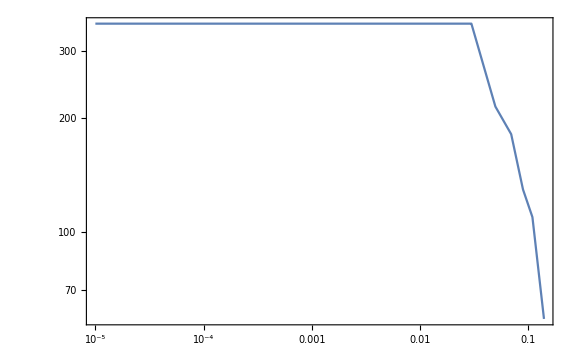

```mathematica
BSPSdata=Re[Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/SPS/DoubleDistrBmesons-SPS.dat"}],"Table"]];
EBSPSmin=SortBy[BSPSdata,#[[2]]&][[1]][[2]];
EBSPSmax=SortBy[BSPSdata,-#[[2]]&][[1]][[2]];
θBSPSmax=SortBy[BSPSdata,-#[[1]]&][[1]][[1]]
DoubleDistrBAtSPStemp[θB_,EB_]=If[EBSPSmin<EB<=EBSPSmax,Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@BSPSdata,InterpolationOrder->1][Log10[θB],Log10[EB]])],0];
θlistBSPS={10^-3,3*10^-3,6*10^-3,10^-2,2*10^-2,4*10^-2,6*10^-2,8*10^-2,10^-1,0.12,0.995*θBSPSmax}//N;
emotherθB=Quiet[eMotherMax[DoubleDistrBAtSPStemp,mB,EBSPSmax,θlistBSPS,-7]];
EBmaxSPS[θB_]=Quiet[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@emotherθB,InterpolationOrder->1][Log10[θB]])];//AbsoluteTiming
LogLogPlot[EBmaxSPS[θB],{θB,10^-5,θBSPSmax},Frame->True,ImageSize->Large,PlotRange->All]
DoubleDistrBSPS[θB_,EB_]=If[10^-5.≤θB≤θBSPSmax&&mB<EB<EBmaxSPS[θB],Evaluate[DoubleDistrBAtSPStemp[θB,EB]],0];
```

### Generating points from distribution

#### For decays producing one target particle

```mathematica
(*Producing random phase space points according to the distribution*)
BdataSPS=BlockPointsFromSmoothDistribution[DoubleDistrBSPS,emotherθB,mB,EBmaxSPS,nsim,"False"];//AbsoluteTiming
BcdataSPS=DataConverted[BdataSPS,mBc];//AbsoluteTiming
```

{38.6645,Null}

{0.207488,Null}

#### For decays producing two target particles

```mathematica
(*Producing random phase space points according to the distribution*)
BdataSPStemp=BlockPointsFromSmoothDistribution[DoubleDistrBSPS,emotherθB,mB,EBmaxSPS,nsim/2,"False"];//AbsoluteTiming
BdataSPS=Riffle[BdataSPStemp,BdataSPStemp];
BsdataSPS=DataConverted[BdataSPS,mBs];//AbsoluteTiming
```

{18.2639,Null}

{0.205236,Null}

## LHC

### Distribution

{0.0396395,Null}

{0.140447,Null}

{0.0001303,Null}

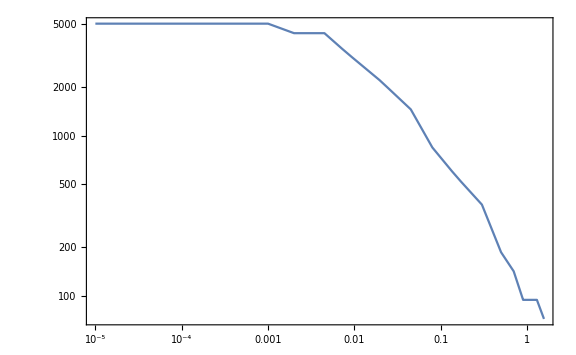

```mathematica
(*Approximation: the spectra of all B mesons are taken to be the same. The reason: they originate from the same process of the production of b b̄ pair, and the resulting distributions of B^(+/-), B^0 are quite similar. The only exception is Subscript[B, c], but for the moment the distribution is approximated by the one for B^+*)
DoubleDistrBLHCDataTemp=Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/LHC/DoubleDistrBmesons-LHC.txt"}],"Table"];//AbsoluteTiming
DoubleDistrBLHCData=Join[DoubleDistrBLHCDataTemp,{Pi-#[[1]],#[[2]],#[[3]]}&/@DoubleDistrBLHCDataTemp];
EminBdataLHC=SortBy[DeleteDuplicatesBy[DoubleDistrBLHCData,#[[2]]&],#[[2]]&][[1]][[2]];
DoubleDistrBLHCTemp[θB_,EB_]=If[EB>EminBdataLHC,Evaluate[10^(Interpolation[{#[[1]],#[[2]],Log10[#[[3]]+10^-20]}&/@DoubleDistrBLHCData,InterpolationOrder->1][θB,EB])],0];//AbsoluteTiming
(*Finding maximal energy for the given polar angle*)
θlistBLHC={10^-3,3*10^-3,6*10^-3,10^-2,3*10^-2,6*10^-2,10^-1,2*10^-1,4*10^-1,6*10^-1,8*10^-1,1,1.2,1.4,x/.Solve[(1.4+x)/2==0.9999*Pi/2,x][[1]]}//N;
EBmaxLHCabs=5000;
emotherθB=Quiet[eMotherMax[DoubleDistrBLHCTemp,mB,EBmaxLHCabs,θlistBLHC,-6]];
EBmaxLHChalf[θB_]=Quiet[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@emotherθB,InterpolationOrder->1][Log10[θB]])];//AbsoluteTiming
EBmaxLHC[θB_]=Piecewise[{{EBmaxLHChalf[θB],θB≤Pi/2},{EBmaxLHChalf[Pi-θB],θB>Pi/2}}];
LogLogPlot[EBmaxLHC[θB],{θB,10^-5,Pi/2},Frame->True,ImageSize->Large]
DoubleDistrBLHC[θB_,EB_]=If[θB≥10^-5.&&mB<EB<EBmaxLHC[θB],DoubleDistrBLHCTemp[θB,EB],0];
```

### Generating points from distribution

#### For decays producing one target particle

```mathematica
(*Producing random phase space points according to the distribution*)
BdataLHC=BlockPointsFromSmoothDistribution[DoubleDistrBLHC,emotherθB,mB,EBmaxLHChalf,nsim,"True"];//AbsoluteTiming
(*BdataLHC1=BlockPointsFromSmoothDistribution1[DoubleDistrBLHC,0,π,mB,EBmaxLHCabs,10^7];//AbsoluteTiming*)
BcdataLHC=DataConverted[BdataLHC,mBc];//AbsoluteTiming
```

{54.9653,Null}

{0.481672,Null}

#### For decays producing two target particles

```mathematica
BdataLHCtemp=BlockPointsFromSmoothDistribution[DoubleDistrBLHC,emotherθB,mB,EBmaxLHChalf,nsim/2,"True"];//AbsoluteTiming
BdataLHC=Riffle[BdataLHCtemp,BdataLHCtemp];
BsdataLHC=DataConverted[BdataLHC,mBs];//AbsoluteTiming
```

## FCC-hh

### Distribution

```mathematica
(*Approximation: the spectra of all B mesons are taken to be the same. The reason: they originate from the same process of the production of b b̄ pair, and the resulting distributions of B^(+/-), B^0 are quite similar. The only exception is Subscript[B, c], but for the moment the distribution is approximated by the one for B^+*)
DoubleDistrBFCChhData=Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/FCC-hh/DoubleDistrB-FCC-hh.txt"}],"Table"];
EminBdataFCChh=SortBy[DeleteDuplicatesBy[DoubleDistrBFCChhData,#[[2]]&],#[[2]]&][[1]][[2]];
DoubleDistrBFCChhTemp[θB_,EB_]=If[EB>EminBdataFCChh,Evaluate[10^(Interpolation[{#[[1]],#[[2]],Log10[#[[3]]+10^-20]}&/@DoubleDistrBFCChhData,InterpolationOrder->1][θB,EB])],0];
(*Finding maximal energy for the given polar angle*)
θlistBFCChh={10^-3,3*10^-3,6*10^-3,10^-2,3*10^-2,6*10^-2,10^-1,2*10^-1,4*10^-1,6*10^-1,8*10^-1,1,1.2,1.4,x/.Solve[(1.4+x)/2==0.9999*Pi/2,x][[1]]}//N;
EBmaxFCChhabs=50000;
emotherθB=Quiet[eMotherMax[DoubleDistrBFCChhTemp,mB,EBmaxFCChhabs,θlistBFCChh,-7]];
EBmaxFCChhhalf[θB_]=Quiet[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@emotherθB,InterpolationOrder->1][Log10[θB]])];//AbsoluteTiming
EBmaxFCChh[θB_]=Piecewise[{{EBmaxFCChhhalf[θB],θB≤Pi/2},{EBmaxFCChhhalf[Pi-θB],θB>Pi/2}}];
LogLogPlot[EBmaxFCChh[θB],{θB,10^-5,Pi/2},Frame->True,ImageSize->Large]
DoubleDistrBFCChh[θB_,EB_]=If[θB≥10^-5.&&mB<EB<EBmaxFCChh[θB],DoubleDistrBFCChhTemp[θB,EB],0];
```

### Generating points from distribution

#### For decays producing one target particle

```mathematica
BdataFCChh=BlockPointsFromSmoothDistribution[DoubleDistrBFCChh,emotherθB,mB,EBmaxFCChhhalf,nsim,"True"];//AbsoluteTiming
BcdataFCChh=DataConverted[BdataFCChh,mBc];//AbsoluteTiming
```

#### For decays producing two target particles

```mathematica
BdataFCChhTemp=BlockPointsFromSmoothDistribution[DoubleDistrBFCChh,emotherθB,mB,EBmaxFCChhhalf,nsim/2,"True"];//AbsoluteTiming
BdataFCChh=Riffle[BdataFCChh,BdataFCChh];
BsdataFCChh=DataConverted[BdataFCChh,mBs];//AbsoluteTiming
```

## W bosons

## LHC

### Distribution

```mathematica
DoubleDistrWLHCdataTemp=Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/LHC/DoubleDistrW-LHC.txt"}],"Table"];
(*Extending the data from semisphere to full sphere*)
DoubleDistrWLHCdata=Join[DoubleDistrWLHCdataTemp,{Pi-#[[1]],#[[2]],#[[3]]}&/@DoubleDistrWLHCdataTemp];
EWminData=Min[DoubleDistrWLHCdata[[All,2]]];
DoubleDistrWLHCtemp[θW_,EW_]=If[EW>EWminData,Evaluate[10^(Interpolation[{#[[1]],#[[2]],Log10[#[[3]]+10^-20]}&/@DoubleDistrWLHCdata,InterpolationOrder->1][θW,EW])],0];
(*Maximal W energy as a function of polar angle*)
EWmaxLHCabs=7000;
θWlist={10^-3.,5.*10^-3,10^-2,3*10^-2.,6*10^-2,9*10^-2,0.12,0.15,0.23,0.3,0.45,0.6,0.75,0.9,1.3,x/.Solve[(1.3+x)/2==1.57,x][[1]]}//N;
EmaxθWlist=Quiet[eMotherMax[DoubleDistrWLHCtemp,MW,EWmaxLHCabs,θWlist,-5]];//AbsoluteTiming
EWmaxLHChalf[θW_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@EmaxθWlist,InterpolationOrder->1][Log10[θW]]);//AbsoluteTiming
EWmaxLHC[θW_]=Piecewise[{{EWmaxLHChalf[θW],θW≤Pi/2},{EWmaxLHChalf[Pi-θW],θW>Pi/2}}];
LogLogPlot[EWmaxLHC[θW],{θW,10^-5,Pi/2},PlotRange->All]
DoubleDistrWLHC[θW_,EW_]=If[θW≥10^-5.&&MW<EW<EWmaxLHC[θW],DoubleDistrWLHCtemp[θW,EW],0];
```

### Generating points from distribution

#### For decays producing one target particle

```mathematica
WdataLHC=BlockPointsFromSmoothDistribution[DoubleDistrWLHC,EmaxθWlist,MW,EWmaxLHChalf,nsim,"True"];//AbsoluteTiming
```

#### For decays producing two target particles

## FCC-hh

### Distribution

```mathematica
DoubleDistrWFCChhdata=Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/FCC-hh/DoubleDistrW-FCC-hh.txt"}],"Table"];
EWminData=Min[DoubleDistrWFCChhdata[[All,2]]];
DoubleDistrWFCChhtemp[θW_,EW_]=If[EW>EWminData,Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-20]}&/@DoubleDistrWFCChhdata,InterpolationOrder->1][Log10[θW],Log10[EW]])],0];
(*Maximal W energy as a function of polar angle*)
EWmaxFCChhabs=50000;
θWlist={10^-3.,5.*10^-3,10^-2,3*10^-2.,6*10^-2,9*10^-2,0.12,0.15,0.23,0.3,0.45,0.6,0.75,0.9,1.3,x/.Solve[(1.3+x)/2==1.57,x][[1]]}//N;
EmaxθWlist=Quiet[eMotherMax[DoubleDistrWFCChhtemp,MW,EWmaxFCChhabs,θWlist,-5]];
EWmaxFCChhhalf[θW_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@EmaxθWlist,InterpolationOrder->1][Log10[θW]]);
EWmaxFCChh[θW_]=Piecewise[{{EWmaxFCChhhalf[θW],θW≤Pi/2},{EWmaxFCChhhalf[Pi-θW],θW>Pi/2}}];
LogLogPlot[EWmaxFCChh[θW],{θW,10^-5,Pi/2},PlotRange->All]
DoubleDistrWFCChh[θW_,EW_]=If[θW≥10^-5.&&MW<EW<EWmaxFCChh[θW],DoubleDistrWFCChhtemp[θW,EW],0];
```

### Generating points from distribution

#### For decays producing one target particle

```mathematica
WdataFCChh=BlockPointsFromSmoothDistribution[DoubleDistrWFCChh,EmaxθWlist,MW,EWmaxFCChhhalf,nsim,"True"];//AbsoluteTiming
```

#### For decays producing two target particles

## Higgs bosons

## LHC

### Distribution

```mathematica
DoubleDistrhLHCDataTemp=Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/LHC/DoubleDistrHiggsBosons-LHC.txt"}],"Table"];
DoubleDistrhLHCData=Join[DoubleDistrhLHCDataTemp,{Pi-#[[1]],#[[2]],#[[3]]}&/@DoubleDistrhLHCDataTemp];
EminhdataLHC=SortBy[DeleteDuplicatesBy[DoubleDistrhLHCData,#[[2]]&],#[[2]]&][[1]][[2]];
DoubleDistrhLHCTemp[θh_,Eh_]=If[Eh>EminhdataLHC,Evaluate[10^(Interpolation[{#[[1]],#[[2]],Log10[#[[3]]+10^-20]}&/@DoubleDistrhLHCData,InterpolationOrder->1][θh,Eh])],0];
(*Finding maximal h energy for the given polar angle*)
θlisthLHC={10^-3,3*10^-3,6*10^-3,10^-2,3*10^-2,6*10^-2,10^-1,2*10^-1,4*10^-1,6*10^-1,8*10^-1,1,1.2,1.4,1.7}//N;
EhmaxLHCabs=7000;
DataEmaxVsθ=eMotherMax[DoubleDistrhLHCTemp,mh,EhmaxLHCabs,θlisthLHC,-5]//N;
EhmaxLHChalf[θh_]=Quiet[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@DataEmaxVsθ,InterpolationOrder->1][Log10[θh]])];//AbsoluteTiming
EhmaxLHC[θh_]=Piecewise[{{EhmaxLHChalf[θh],θh≤Pi/2},{EhmaxLHChalf[Pi-θh],θh>Pi/2}}];
LogLogPlot[EhmaxLHC[θh],{θh,10^-5,Pi/2},Frame->True,ImageSize->Large]
DoubleDistrhLHC[θh_,Eh_]=If[10^-5.≤θh≤Pi-10^-5.&&mh<Eh<EhmaxLHC[θh],DoubleDistrhLHCTemp[θh,Eh],0];
```

### Generating points from distribution

#### For decays producing one target particle

#### For decays producing two target particles

```mathematica
(*Producing random phase space points according to the distribution*)
hdataLHCtemp=BlockPointsFromSmoothDistribution[DoubleDistrhLHC,DataEmaxVsθ,mh,EhmaxLHChalf,nsim/2,"True"];//AbsoluteTiming
hdataLHC=Riffle[hdataLHCtemp,hdataLHCtemp];
```

## FCC-hh

### Distribution

```mathematica
DoubleDistrhFCChhData=Import[FileNameJoin[{NotebookDirectory[],"spectra/SM particles/FCC-hh/DoubleDistrh-FCC-hh.txt"}],"Table"];
EminhdataFCChh=Min[DoubleDistrhFCChhData[[All,2]]];
DoubleDistrhFCChhTemp[θh_,Eh_]=If[Eh>EminhdataFCChh,Evaluate[10^(Interpolation[{#[[1]],#[[2]],Log10[#[[3]]+10^-20]}&/@DoubleDistrhFCChhData,InterpolationOrder->1][θh,Eh])],0];
(*Finding maximal h energy for the given polar angle*)
θlisthFCChh={10^-3,3*10^-3,6*10^-3,10^-2,3*10^-2,6*10^-2,10^-1,2*10^-1,4*10^-1,6*10^-1,8*10^-1,1,1.2,1.4,1.7}//N;
EhmaxFCChhabs=50000;
DataEmaxVsθ=Quiet[eMotherMax[DoubleDistrhFCChhTemp,mh,EhmaxFCChhabs,θlisthFCChh,-5]];//AbsoluteTiming
EhmaxFCChhhalf[θh_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@DataEmaxVsθ,InterpolationOrder->1][Log10[θh]]);
EhmaxFCChh[θh_]=Piecewise[{{EhmaxFCChhhalf[θh],θh≤Pi/2},{EhmaxFCChhhalf[Pi-θh],θh>Pi/2}}];
LogLogPlot[EhmaxFCChh[θh],{θh,10^-5,Pi/2},Frame->True,ImageSize->Large]
DoubleDistrhFCChh[θh_,Eh_]=If[10^-5.≤θh≤Pi-10^-5.&&mh<Eh<EhmaxFCChh[θh],DoubleDistrhFCChhTemp[θh,Eh],0];
```

### Generating points from distribution

#### For decays producing one target particle

#### For decays producing two target particles

```mathematica
(*Producing random phase space points according to the distribution*)
hdataFCChhtemp=BlockPointsFromSmoothDistribution[DoubleDistrhFCChh,DataEmaxVsθ,mh,EhmaxFCChhhalf,nsim/2,"True"];//AbsoluteTiming
hdataFCChh=Riffle[hdataFCChhtemp,hdataFCChhtemp];
```

# Computing distributions - HNLs

## HNLs from kaons - decay K^+→N+e/μ

## SPS

### Exporting distribution of HNL

#### Definitions

```mathematica
HNLdistributionFromKSPS[mN_,mixing_]:=HNLdistributionFromWK[mixing,mN,KdataSPS,θNlistSPS,EFIPfromKlistSPS,0.01]
MassListHNLsFromKmixinge={0.02,0.05,0.1,0.2,0.35,0.49}//N;
HNLdistributionFromKSPSMixinge[mN_]:=HNLdistributionFromKSPS[mN,"e"]
MassListHNLsFromKmixingμ={0.02,0.05,0.1,0.2,0.3,0.385}//N;
HNLdistributionFromKSPSMixingμ[mN_]:=HNLdistributionFromKSPS[mN,"μ"]
```

#### e mixing

```mathematica
TableDistrFromKeMixingSPS=tabulatedblock[HNLdistributionFromKSPSMixinge,MassListHNLsFromKmixinge];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/HNLs/DoubleDistr-From-K-Mixing-e-SPS.dat"}],TableDistrFromKeMixingSPS,"Table"];
```

#### μ mixing

```mathematica
TableDistrFromKμMixingSPS=tabulatedblock[HNLdistributionFromKSPSMixingμ,MassListHNLsFromKmixingμ];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/HNLs/DoubleDistr-From-K-Mixing-mu-SPS.dat"}],TableDistrFromKμMixingSPS,"Table"];
```

## HNLs from B

## FCC-hh

### Weights for different decays of B into HNLs

```mathematica
WeightsHNLproductionFromBmixingFCChh[mixing_,mN_,BcOption_]:=Association[{{"e",mN,BcOption}-> {(fbtobplusFCChh*(bplusD0starbareN[mN]+bplusD0bareN[mN])+fbtob0FCChh*(b0DminusstareN[mN]+b0DeN[mN]))*UnitStep[mB-mDstar-mlMixing["e"]-mN],fbtobplusFCChh*bpluseN[mN]*UnitStep[mB-mlMixing["e"]-mN],If[BcOption=="True",fbtobcFCChh* bceN[mN]*UnitStep[mBc-mlMixing["e"]-mN],0]},{"μ",mN,BcOption}-> {(fbtobplusFCChh*(bplusD0starbarmuN[mN]+bplusD0barmuN[mN])+fbtob0FCChh*(b0DminusstarmuN[mN]+b0DmuN[mN]))UnitStep[mB-mDstar-mlMixing["μ"]-mN],fbtobplusFCChh*bplusmuN[mN]*UnitStep[mB-mlMixing["μ"]-mN],If[BcOption=="True",fbtobcFCChh* bcmuN[mN]*UnitStep[mBc-mlMixing["μ"]-mN],0]},{"τ",mN,BcOption}-> {(fbtobplusFCChh*(bplusD0starbartauN[mN]+bplusD0bartauN[mN])+fbtob0FCChh*(b0DminusstartauN[mN]+b0DtauN[mN]))UnitStep[mB-mDstar-mlMixing["τ"]-mN],fbtobplusFCChh*bplustauN[mN]*UnitStep[mB-mlMixing["τ"]-mN],If[BcOption=="True",fbtobcFCChh*bctauN[mN]UnitStep[mBc-mlMixing["τ"]-mN],0]}}][{mixing,mN,BcOption}]
TotalLength=10^7;
Print["Masses at which 2-body decays start dominate over 3-body:"]
WeightsemixingFromBFCChh[mN_]=WeightsHNLproductionFromBmixingFCChh["e",mN,"True"];
WeightsμmixingFromBFCChh[mN_]=WeightsHNLproductionFromBmixingFCChh["μ",mN,"True"];
WeightsτmixingFromBFCChh[mN_]=WeightsHNLproductionFromBmixingFCChh["τ",mN,"True"];
mNTwoThreeBodyTransitionNoBcFCChhemixing=mN/.FindRoot[WeightsemixingFromBFCChh[mN][[1]]==WeightsemixingFromBFCChh[mN][[2]],{mN,3,2.9,4}];
mNTwoThreeBodyTransitionNoBcFCChhμmixing=mN/.FindRoot[WeightsμmixingFromBFCChh[mN][[1]]==WeightsμmixingFromBFCChh[mN][[2]],{mN,3,2.7,4}];
mNTwoThreeBodyTransitionNoBcFCChhτmixing=mN/.FindRoot[WeightsτmixingFromBFCChh[mN][[1]]==WeightsτmixingFromBFCChh[mN][[2]],{mN,1,0.5,2}];
mNTwoThreeBodyTransitionWithBcFCChhemixing=mN/.FindRoot[WeightsemixingFromBFCChh[mN][[1]]==WeightsemixingFromBFCChh[mN][[2]]+WeightsemixingFromBFCChh[mN][[3]],{mN,3,2.5,4}];
mNTwoThreeBodyTransitionWithBcFCChhμmixing=mN/.FindRoot[WeightsμmixingFromBFCChh[mN][[1]]==WeightsμmixingFromBFCChh[mN][[2]]+WeightsμmixingFromBFCChh[mN][[3]],{mN,3,2.5,4}];
mNTwoThreeBodyTransitionWithBcFCChhτmixing=mN/.FindRoot[WeightsτmixingFromBFCChh[mN][[1]]==WeightsτmixingFromBFCChh[mN][[2]]+WeightsτmixingFromBFCChh[mN][[3]],{mN,1,0.5,2}];
{{"e, no B_c","μ, no B_c","τ, no B_c","e, with B_c","μ, with B_c","τ, with B_c"},{mNTwoThreeBodyTransitionNoBcFCChhemixing,mNTwoThreeBodyTransitionNoBcFCChhμmixing,mNTwoThreeBodyTransitionNoBcFCChhτmixing,mNTwoThreeBodyTransitionWithBcFCChhemixing,mNTwoThreeBodyTransitionWithBcFCChhμmixing,mNTwoThreeBodyTransitionWithBcFCChhτmixing}}//TableForm
Print["Mass lists for the distributions - e, μ, τ mixings:"]
MassListFromBeMixing[BcOption_]:=If[BcOption=="True",{0.05,0.2,0.5,1,1.5,2.,2.5,2.8,3.,3.2,3.7,4.3,4.8,5.25,5.8,6.25},{0.05,0.2,0.5,1,1.5,2.,2.5,2.8,3.,3.2,3.7,4.3,4.8,5.25}]
MassListFromBμMixing[BcOption_]:=If[BcOption=="True",{0.05,0.2,0.5,1.1,1.6,2.1,2.6-mlMixing["μ"],2.8-mlMixing["μ"],3-mlMixing["μ"],3.2-mlMixing["μ"],3.7,4.2,4.7,5.25-mlMixing["μ"],5.8-mlMixing["μ"],6.25-mlMixing["μ"]},{0.05,0.2,0.5,1.1,1.6,2.1,2.6-mlMixing["μ"],2.8-mlMixing["μ"],3-mlMixing["μ"],3.2-mlMixing["μ"],3.7,4.2,4.7,5.25-mlMixing["μ"]}]
MassListFromBτMixing[BcOption_]:=If[BcOption=="True",{0.05,0.2,0.6,1.1,1.4,1.5,1.8,2.2,2.6,3.1,3.3,3.5,3.8,4.3,4.5},{0.05,0.2,0.6,1.1,1.4,1.5,1.8,2.2,2.6,3.1,3.3,3.5}]
(*Final block computing the distribution for the given mass*)
HNLdistributionFromBFCChh[mN_,mixing_,BcOption_]:=If[mN<MaxMassHNLsFromB[BcOption,mixing],HNLdistributionFromB[mixing,mN,BcOption,WeightsHNLproductionFromBmixingFCChh,BdataFCChh,BcdataFCChh,θNlistFCChh,ENlistFCChh,3*10^-4],TabZeroDistrHNL[mN,θNlistFCChh,ENlistFCChh]];
```

### Distribution exporting

#### Definition

```mathematica
HNLdistributionFromBFCChhMixinge[mN_]:=HNLdistributionFromBFCChh[mN,"e","True"]
HNLdistributionFromBFCChhMixingμ[mN_]:=HNLdistributionFromBFCChh[mN,"μ","True"]
HNLdistributionFromBFCChhMixingτ[mN_]:=HNLdistributionFromBFCChh[mN,"τ","True"]
```

#### e mixing

```mathematica
TableDistrFromBeMixingFCChh=tabulatedblock[HNLdistributionFromBFCChhMixinge,MassListFromBeMixing["True"]];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/HNLs/DoubleDistr-From-B-Mixing-e-FCC-hh.dat"}],TableDistrFromBeMixingFCChh,"Table"];
```

#### μ mixing

```mathematica
TableDistrFromBμMixingFCChh=tabulatedblock[HNLdistributionFromBFCChhMixingμ,MassListFromBμMixing["True"]];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/HNLs/DoubleDistr-From-B-Mixing-mu-FCC-hh.dat"}],TableDistrFromBμMixingFCChh,"Table"];
```

#### τ mixing

```mathematica
TableDistrFromBτMixingFCChh=tabulatedblock[HNLdistributionFromBFCChhMixingτ,MassListFromBτMixing["True"]];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/HNLs/DoubleDistr-From-B-Mixing-tau-FCC-hh.dat"}],TableDistrFromBτMixingFCChh,"Table"];
```

## LHC

### Weights for different decays of B into HNLs

```mathematica
WeightsHNLproductionFromBmixingLHC[mixing_,mN_,BcOption_]:=Association[{{"e",mN,BcOption}-> {(fbtobplusLHC*(bplusD0starbareN[mN]+bplusD0bareN[mN])+fbtob0LHC*(b0DminusstareN[mN]+b0DeN[mN]))*UnitStep[mB-mDstar-mlMixing["e"]-mN],fbtobplusLHC*bpluseN[mN]*UnitStep[mB-mlMixing["e"]-mN],If[BcOption=="True",fbtobcLHC* bceN[mN]*UnitStep[mBc-mlMixing["e"]-mN],0]},{"μ",mN,BcOption}-> {(fbtobplusLHC*(bplusD0starbarmuN[mN]+bplusD0barmuN[mN])+fbtob0LHC*(b0DminusstarmuN[mN]+b0DmuN[mN]))UnitStep[mB-mDstar-mlMixing["μ"]-mN],fbtobplusLHC*bplusmuN[mN]*UnitStep[mB-mlMixing["μ"]-mN],If[BcOption=="True",fbtobcLHC* bcmuN[mN]*UnitStep[mBc-mlMixing["μ"]-mN],0]},{"τ",mN,BcOption}-> {(fbtobplusLHC*(bplusD0starbartauN[mN]+bplusD0bartauN[mN])+fbtob0LHC*(b0DminusstartauN[mN]+b0DtauN[mN]))UnitStep[mB-mDstar-mlMixing["τ"]-mN],fbtobplusLHC*bplustauN[mN]*UnitStep[mB-mlMixing["τ"]-mN],If[BcOption=="True",fbtobcLHC*bctauN[mN]UnitStep[mBc-mlMixing["τ"]-mN],0]}}][{mixing,mN,BcOption}]
TotalLength=10^7;
Print["Masses at which 2-body decays start dominate over 3-body:"]
WeightsemixingFromBLHC[mN_]=WeightsHNLproductionFromBmixingLHC["e",mN,"True"];
WeightsμmixingFromBLHC[mN_]=WeightsHNLproductionFromBmixingLHC["μ",mN,"True"];
WeightsτmixingFromBLHC[mN_]=WeightsHNLproductionFromBmixingLHC["τ",mN,"True"];
mNTwoThreeBodyTransitionNoBcLHCemixing=mN/.FindRoot[WeightsemixingFromBLHC[mN][[1]]==WeightsemixingFromBLHC[mN][[2]],{mN,3,2.9,4}];
mNTwoThreeBodyTransitionNoBcLHCμmixing=mN/.FindRoot[WeightsμmixingFromBLHC[mN][[1]]==WeightsμmixingFromBLHC[mN][[2]],{mN,3,2.7,4}];
mNTwoThreeBodyTransitionNoBcLHCτmixing=mN/.FindRoot[WeightsτmixingFromBLHC[mN][[1]]==WeightsτmixingFromBLHC[mN][[2]],{mN,1,0.5,2}];
mNTwoThreeBodyTransitionWithBcLHCemixing=mN/.FindRoot[WeightsemixingFromBLHC[mN][[1]]==WeightsemixingFromBLHC[mN][[2]]+WeightsemixingFromBLHC[mN][[3]],{mN,3,2.5,4}];
mNTwoThreeBodyTransitionWithBcLHCμmixing=mN/.FindRoot[WeightsμmixingFromBLHC[mN][[1]]==WeightsμmixingFromBLHC[mN][[2]]+WeightsμmixingFromBLHC[mN][[3]],{mN,3,2.5,4}];
mNTwoThreeBodyTransitionWithBcLHCτmixing=mN/.FindRoot[WeightsτmixingFromBLHC[mN][[1]]==WeightsτmixingFromBLHC[mN][[2]]+WeightsτmixingFromBLHC[mN][[3]],{mN,1,0.5,2}];
{{"e, no B_c","μ, no B_c","τ, no B_c","e, with B_c","μ, with B_c","τ, with B_c"},{mNTwoThreeBodyTransitionNoBcLHCemixing,mNTwoThreeBodyTransitionNoBcLHCμmixing,mNTwoThreeBodyTransitionNoBcLHCτmixing,mNTwoThreeBodyTransitionWithBcLHCemixing,mNTwoThreeBodyTransitionWithBcLHCμmixing,mNTwoThreeBodyTransitionWithBcLHCτmixing}}//TableForm
Print["Mass lists for the distributions - e, μ, τ mixings:"]
MassListFromBeMixing[BcOption_]:=If[BcOption=="True",{0.05,0.2,0.5,1,1.5,2.,2.5,2.8,3.,3.2,3.7,4.3,4.8,5.25,5.8,6.25},{0.05,0.2,0.5,1,1.5,2.,2.5,2.8,3.,3.2,3.7,4.3,4.8,5.25}]
MassListFromBμMixing[BcOption_]:=If[BcOption=="True",{0.05,0.2,0.5,1.1,1.6,2.1,2.6-mlMixing["μ"],2.8-mlMixing["μ"],3-mlMixing["μ"],3.2-mlMixing["μ"],3.7,4.2,4.7,5.25-mlMixing["μ"],5.8-mlMixing["μ"],6.25-mlMixing["μ"]},{0.05,0.2,0.5,1.1,1.6,2.1,2.6-mlMixing["μ"],2.8-mlMixing["μ"],3-mlMixing["μ"],3.2-mlMixing["μ"],3.7,4.2,4.7,5.25-mlMixing["μ"]}]
MassListFromBτMixing[BcOption_]:=If[BcOption=="True",{0.05,0.2,0.6,1.1,1.4,1.5,1.8,2.2,2.6,3.1,3.3,3.5,3.8,4.3,4.5},{0.05,0.2,0.6,1.1,1.4,1.5,1.8,2.2,2.6,3.1,3.3,3.5}]
(*Final block computing the distribution for the given mass*)
HNLdistributionFromBLHC[mN_,mixing_,BcOption_]:=If[mN<MaxMassHNLsFromB[BcOption,mixing],HNLdistributionFromB[mixing,mN,BcOption,WeightsHNLproductionFromBmixingLHC,BdataLHC,BcdataLHC,θNlistLHC,ENlistLHC,3*10^-4],TabZeroDistrHNL[mN,θNlistLHC,ENlistLHC]];
```

### Distribution exporting

#### Definitions

```mathematica
HNLdistributionFromBLHCMixinge[mN_]:=HNLdistributionFromBLHC[mN,"e","True"]
HNLdistributionFromBLHCMixingμ[mN_]:=HNLdistributionFromBLHC[mN,"μ","True"]
HNLdistributionFromBLHCMixingτ[mN_]:=HNLdistributionFromBLHC[mN,"τ","True"]
```

#### e mixing

```mathematica
TableDistrFromBeMixingLHC=tabulatedblock[HNLdistributionFromBLHCMixinge,MassListFromBeMixing["True"]];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/HNLs/DoubleDistr-From-B-Mixing-e-LHC.dat"}],TableDistrFromBeMixingLHC,"Table"];
```

#### μ mixing

```mathematica
TableDistrFromBμMixingLHC=tabulatedblock[HNLdistributionFromBLHCMixingμ,MassListFromBμMixing["True"]];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/HNLs/DoubleDistr-From-B-Mixing-mu-LHC.dat"}],TableDistrFromBμMixingLHC,"Table"];
```

#### τ mixing

```mathematica
TableDistrFromBτMixingLHC=tabulatedblock[HNLdistributionFromBLHCMixingτ,MassListFromBτMixing["True"]];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/HNLs/DoubleDistr-From-B-Mixing-tau-LHC.dat"}],TableDistrFromBτMixingLHC,"Table"];
```

## SPS

### Weights for different decays of B into HNLs

```mathematica
WeightsHNLproductionFromBmixingSPS[mixing_,mN_,BcOption_]:=Association[{{"e",mN,BcOption}-> {(fbtobplusSPS*(bplusD0starbareN[mN]+bplusD0bareN[mN])+fbtob0SPS*(b0DminusstareN[mN]+b0DeN[mN]))*UnitStep[mB-mDstar-mlMixing["e"]-mN],fbtobplusSPS*bpluseN[mN]*UnitStep[mB-mlMixing["e"]-mN],If[BcOption=="True",fbtobcLHC* bceN[mN]*UnitStep[mBc-mlMixing["e"]-mN],0]},{"μ",mN,BcOption}-> {(fbtobplusSPS*(bplusD0starbarmuN[mN]+bplusD0barmuN[mN])+fbtob0SPS*(b0DminusstarmuN[mN]+b0DmuN[mN]))UnitStep[mB-mDstar-mlMixing["μ"]-mN],fbtobplusSPS*bplusmuN[mN]*UnitStep[mB-mlMixing["μ"]-mN],If[BcOption=="True",fbtobcLHC* bcmuN[mN]*UnitStep[mBc-mlMixing["μ"]-mN],0]},{"τ",mN,BcOption}-> {(fbtobplusSPS*(bplusD0starbartauN[mN]+bplusD0bartauN[mN])+fbtob0SPS*(b0DminusstartauN[mN]+b0DtauN[mN]))UnitStep[mB-mDstar-mlMixing["τ"]-mN],fbtobplusSPS*bplustauN[mN]*UnitStep[mB-mlMixing["τ"]-mN],If[BcOption=="True",fbtobcLHC*bctauN[mN]*UnitStep[mBc-mlMixing["τ"]-mN],0]}}][{mixing,mN,BcOption}]
TotalLength=10^7;
Print["Masses at which 2-body decays start dominate over 3-body:"]
WeightsemixingFromBSPS[mN_]=WeightsHNLproductionFromBmixingSPS["e",mN,"True"];
WeightsμmixingFromBSPS[mN_]=WeightsHNLproductionFromBmixingSPS["μ",mN,"True"];
WeightsτmixingFromBSPS[mN_]=WeightsHNLproductionFromBmixingSPS["τ",mN,"True"];
mNTwoThreeBodyTransitionNoBcSPSemixing=mN/.FindRoot[WeightsemixingFromBSPS[mN][[1]]==WeightsemixingFromBSPS[mN][[2]],{mN,3,2.9,4}];
mNTwoThreeBodyTransitionNoBcSPSμmixing=mN/.FindRoot[WeightsμmixingFromBSPS[mN][[1]]==WeightsμmixingFromBSPS[mN][[2]],{mN,3,2.7,4}];
mNTwoThreeBodyTransitionNoBcSPSτmixing=mN/.FindRoot[WeightsτmixingFromBSPS[mN][[1]]==WeightsτmixingFromBSPS[mN][[2]],{mN,1,0.5,2}];
mNTwoThreeBodyTransitionWithBcSPSemixing=mN/.FindRoot[WeightsemixingFromBSPS[mN][[1]]==WeightsemixingFromBSPS[mN][[2]]+WeightsemixingFromBSPS[mN][[3]],{mN,3,2.5,4}];
mNTwoThreeBodyTransitionWithBcSPSμmixing=mN/.FindRoot[WeightsμmixingFromBSPS[mN][[1]]==WeightsμmixingFromBSPS[mN][[2]]+WeightsμmixingFromBSPS[mN][[3]],{mN,3,2.5,4}];
mNTwoThreeBodyTransitionWithBcSPSτmixing=mN/.FindRoot[WeightsτmixingFromBSPS[mN][[1]]==WeightsτmixingFromBSPS[mN][[2]]+WeightsτmixingFromBSPS[mN][[3]],{mN,1,0.5,2}];
{{"e, no B_c","μ, no B_c","τ, no B_c","e, with B_c","μ, with B_c","τ, with B_c"},{mNTwoThreeBodyTransitionNoBcSPSemixing,mNTwoThreeBodyTransitionNoBcSPSμmixing,mNTwoThreeBodyTransitionNoBcSPSτmixing,mNTwoThreeBodyTransitionWithBcSPSemixing,mNTwoThreeBodyTransitionWithBcSPSμmixing,mNTwoThreeBodyTransitionWithBcSPSτmixing}}//TableForm
Print["Mass lists for the distributions - e, μ, τ mixings:"]
MassListFromBeMixing[BcOption_]:=If[BcOption=="True",{0.05,0.2,0.5,1,1.5,2.,2.5,2.8,3.,3.2,3.7,4.3,4.8,5.25,5.8,6.25},{0.05,0.2,0.5,1,1.5,2.,2.5,2.8,3.,3.2,3.7,4.3,4.8,5.25}]
MassListFromBμMixing[BcOption_]:=If[BcOption=="True",{0.05,0.2,0.5,1.1,1.6,2.1,2.6-mlMixing["μ"],2.8-mlMixing["μ"],3-mlMixing["μ"],3.2-mlMixing["μ"],3.7,4.2,4.7,5.25-mlMixing["μ"],5.8-mlMixing["μ"],6.25-mlMixing["μ"]},{0.05,0.2,0.5,1.1,1.6,2.1,2.6-mlMixing["μ"],2.8-mlMixing["μ"],3-mlMixing["μ"],3.2-mlMixing["μ"],3.7,4.2,4.7,5.25-mlMixing["μ"]}]
MassListFromBτMixing[BcOption_]:=If[BcOption=="True",{0.05,0.2,0.6,1.1,1.4,1.5,1.8,2.2,2.6,3.1,3.3,3.5,3.8,4.3,4.5},{0.05,0.2,0.6,1.1,1.4,1.5,1.8,2.2,2.6,3.1,3.3,3.5}]
(*Final block computing the distribution for the given mass*)
HNLdistributionFromBSPS[mN_,mixing_,BcOption_]:=If[mN<MaxMassHNLsFromB[BcOption,mixing],HNLdistributionFromB[mixing,mN,BcOption,WeightsHNLproductionFromBmixingSPS,BdataSPS,BcdataSPS,θNlistSPS,ENlistSPS,3*10^-4],TabZeroDistrHNL[mN,θNlistSPS,ENlistSPS]];
```

### Distribution exporting

#### Definitions

```mathematica
HNLdistributionFromBSPSMixinge[mN_]:=HNLdistributionFromBSPS[mN,"e","False"]
HNLdistributionFromBSPSMixingμ[mN_]:=HNLdistributionFromBSPS[mN,"μ","False"]
HNLdistributionFromBSPSMixingτ[mN_]:=HNLdistributionFromBSPS[mN,"τ","False"]
```

#### e mixing

```mathematica
TableDistrFromBeMixingSPS=tabulatedblock[HNLdistributionFromBSPSMixinge,MassListFromBeMixing["False"]];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/HNLs/DoubleDistr-From-B-Mixing-e-SPS.dat"}],TableDistrFromBeMixingSPS,"Table"];
```

#### μ mixing

```mathematica
TableDistrFromBμMixingSPS=tabulatedblock[HNLdistributionFromBSPSMixingμ,MassListFromBμMixing["False"]];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/HNLs/DoubleDistr-From-B-Mixing-mu-SPS.dat"}],TableDistrFromBμMixingSPS,"Table"];
```

#### τ mixing

```mathematica
TableDistrFromBτMixingSPS=tabulatedblock[HNLdistributionFromBSPSMixingτ,MassListFromBτMixing["False"]];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/HNLs/DoubleDistr-From-B-Mixing-tau-SPS.dat"}],TableDistrFromBτMixingSPS,"Table"];
```

## FermilabBD

### Weights for different decays of B into HNLs

```mathematica
WeightsHNLproductionFromBmixingFermilabBD[mixing_,mN_,BcOption_]:=Association[{{"e",mN,BcOption}-> {(fbtobplusFermilabBD*(bplusD0starbareN[mN]+bplusD0bareN[mN])+fbtob0FermilabBD*(b0DminusstareN[mN]+b0DeN[mN]))*UnitStep[mB-mDstar-mlMixing["e"]-mN],fbtobplusFermilabBD*bpluseN[mN]*UnitStep[mB-mlMixing["e"]-mN],If[BcOption=="True",fbtobcLHC* bceN[mN]*UnitStep[mBc-mlMixing["e"]-mN],0]},{"μ",mN,BcOption}-> {(fbtobplusFermilabBD*(bplusD0starbarmuN[mN]+bplusD0barmuN[mN])+fbtob0FermilabBD*(b0DminusstarmuN[mN]+b0DmuN[mN]))UnitStep[mB-mDstar-mlMixing["μ"]-mN],fbtobplusFermilabBD*bplusmuN[mN]*UnitStep[mB-mlMixing["μ"]-mN],If[BcOption=="True",fbtobcLHC* bcmuN[mN]*UnitStep[mBc-mlMixing["μ"]-mN],0]},{"τ",mN,BcOption}-> {(fbtobplusFermilabBD*(bplusD0starbartauN[mN]+bplusD0bartauN[mN])+fbtob0FermilabBD*(b0DminusstartauN[mN]+b0DtauN[mN]))UnitStep[mB-mDstar-mlMixing["τ"]-mN],fbtobplusFermilabBD*bplustauN[mN]*UnitStep[mB-mlMixing["τ"]-mN],If[BcOption=="True",fbtobcLHC*bctauN[mN]*UnitStep[mBc-mlMixing["τ"]-mN],0]}}][{mixing,mN,BcOption}]
TotalLength=10^7;
Print["Masses at which 2-body decays start dominate over 3-body:"]
WeightsemixingFromBFermilabBD[mN_]=WeightsHNLproductionFromBmixingFermilabBD["e",mN,"True"];
WeightsμmixingFromBFermilabBD[mN_]=WeightsHNLproductionFromBmixingFermilabBD["μ",mN,"True"];
WeightsτmixingFromBFermilabBD[mN_]=WeightsHNLproductionFromBmixingFermilabBD["τ",mN,"True"];
mNTwoThreeBodyTransitionNoBcFermilabBDemixing=mN/.FindRoot[WeightsemixingFromBFermilabBD[mN][[1]]==WeightsemixingFromBFermilabBD[mN][[2]],{mN,3,2.9,4}];
mNTwoThreeBodyTransitionNoBcFermilabBDμmixing=mN/.FindRoot[WeightsμmixingFromBFermilabBD[mN][[1]]==WeightsμmixingFromBFermilabBD[mN][[2]],{mN,3,2.7,4}];
mNTwoThreeBodyTransitionNoBcFermilabBDτmixing=mN/.FindRoot[WeightsτmixingFromBFermilabBD[mN][[1]]==WeightsτmixingFromBFermilabBD[mN][[2]],{mN,1,0.5,2}];
mNTwoThreeBodyTransitionWithBcFermilabBDemixing=mN/.FindRoot[WeightsemixingFromBFermilabBD[mN][[1]]==WeightsemixingFromBFermilabBD[mN][[2]]+WeightsemixingFromBFermilabBD[mN][[3]],{mN,3,2.5,4}];
mNTwoThreeBodyTransitionWithBcFermilabBDμmixing=mN/.FindRoot[WeightsμmixingFromBFermilabBD[mN][[1]]==WeightsμmixingFromBFermilabBD[mN][[2]]+WeightsμmixingFromBFermilabBD[mN][[3]],{mN,3,2.5,4}];
mNTwoThreeBodyTransitionWithBcFermilabBDτmixing=mN/.FindRoot[WeightsτmixingFromBFermilabBD[mN][[1]]==WeightsτmixingFromBFermilabBD[mN][[2]]+WeightsτmixingFromBFermilabBD[mN][[3]],{mN,1,0.5,2}];
{{"e, no B_c","μ, no B_c","τ, no B_c","e, with B_c","μ, with B_c","τ, with B_c"},{mNTwoThreeBodyTransitionNoBcFermilabBDemixing,mNTwoThreeBodyTransitionNoBcFermilabBDμmixing,mNTwoThreeBodyTransitionNoBcFermilabBDτmixing,mNTwoThreeBodyTransitionWithBcFermilabBDemixing,mNTwoThreeBodyTransitionWithBcFermilabBDμmixing,mNTwoThreeBodyTransitionWithBcFermilabBDτmixing}}//TableForm
Print["Mass lists for the distributions - e, μ, τ mixings:"]
MassListFromBeMixing[BcOption_]:=If[BcOption=="True",{0.05,0.2,0.5,1,1.5,2.,2.5,2.8,3.,3.2,3.7,4.3,4.8,5.25,5.8,6.25},{0.05,0.2,0.5,1,1.5,2.,2.5,2.8,3.,3.2,3.7,4.3,4.8,5.25}]
MassListFromBμMixing[BcOption_]:=If[BcOption=="True",{0.05,0.2,0.5,1.1,1.6,2.1,2.6-mlMixing["μ"],2.8-mlMixing["μ"],3-mlMixing["μ"],3.2-mlMixing["μ"],3.7,4.2,4.7,5.25-mlMixing["μ"],5.8-mlMixing["μ"],6.25-mlMixing["μ"]},{0.05,0.2,0.5,1.1,1.6,2.1,2.6-mlMixing["μ"],2.8-mlMixing["μ"],3-mlMixing["μ"],3.2-mlMixing["μ"],3.7,4.2,4.7,5.25-mlMixing["μ"]}]
MassListFromBτMixing[BcOption_]:=If[BcOption=="True",{0.05,0.2,0.6,1.1,1.4,1.5,1.8,2.2,2.6,3.1,3.3,3.5,3.8,4.3,4.5},{0.05,0.2,0.6,1.1,1.4,1.5,1.8,2.2,2.6,3.1,3.3,3.5}]
(*Final block computing the distribution for the given mass*)
HNLdistributionFromBFermilabBD[mN_,mixing_,BcOption_]:=If[mN<MaxMassHNLsFromB[BcOption,mixing],HNLdistributionFromB[mixing,mN,BcOption,WeightsHNLproductionFromBmixingFermilabBD,BdataFermilabBD,BcdataFermilabBD,θNlistFermilabBD,ENlistFermilabBD,3*10^-4],TabZeroDistrHNL[mN,θNlistFermilabBD,ENlistFermilabBD]];
```

### Distribution exporting

#### Definitions

```mathematica
Bcopt="False";
HNLdistributionFromBFermilabBDMixinge[mN_]:=HNLdistributionFromBFermilabBD[mN,"e",Bcopt]
HNLdistributionFromBFermilabBDMixingμ[mN_]:=HNLdistributionFromBFermilabBD[mN,"μ",Bcopt]
HNLdistributionFromBFermilabBDMixingτ[mN_]:=HNLdistributionFromBFermilabBD[mN,"τ",Bcopt]
```

#### e mixing

```mathematica
TableDistrFromBeMixingFermilabBD=tabulatedblock[HNLdistributionFromBFermilabBDMixinge,MassListFromBeMixing[Bcopt]];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/HNLs/DoubleDistr-From-B-Mixing-e-FermilabBD.dat"}],TableDistrFromBeMixingFermilabBD,"Table"];
```

#### μ mixing

```mathematica
TableDistrFromBμMixingFermilabBD=tabulatedblock[HNLdistributionFromBFermilabBDMixingμ,MassListFromBμMixing[Bcopt]];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/HNLs/DoubleDistr-From-B-Mixing-mu-FermilabBD.dat"}],TableDistrFromBμMixingFermilabBD,"Table"];
```

#### τ mixing

```mathematica
TableDistrFromBτMixingFermilabBD=tabulatedblock[HNLdistributionFromBFermilabBDMixingτ,MassListFromBτMixing[Bcopt]];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/HNLs/DoubleDistr-From-B-Mixing-tau-FermilabBD.dat"}],TableDistrFromBτMixingFermilabBD,"Table"];
```

## HNLs from D/τ

## FCC-hh

### Weights for different decays of D/τ

```mathematica
WeightsHNLproductionFromDmixingFCChh[mixing_,mN_]:=Association[{{"e",mN}-> {(fctodplusFCChh*(dplusK0eN[mN]+dplusK0stareN[mN])+fctod0FCChh*(d0KpluseN[mN]+d0KplusstareN[mN]))*UnitStep[mDplus-mK-mlMixing["e"]-mN],fctodsFCChh*dseN[mN]*UnitStep[mDs-mlMixing["e"]-mN]},{"μ",mN}-> {(fctodplusFCChh*(dplusK0muN[mN]+dplusK0starmuN[mN])+fctod0FCChh*(d0KplusmuN[mN]+d0KplusstarmuN[mN]))*UnitStep[mDplus-mK-mlMixing["μ"]-mN],fctodsFCChh*dsmuN[mN]*UnitStep[mDs-mlMixing["μ"]-mN]},{"τ",mN}-> {fctodsFCChh*(dstauN[mN])UnitStep[mDs-mlMixing["τ"]-mN],fctodsFCChh*fdstau*taulbarnuN[mN]*UnitStep[mlMixing["τ"]-mlMixing["e"]-mN],fctodsFCChh*fdstau*(tauKN[mN]+taupiN[mN])}}][{mixing,mN}]
TotalLength=10^7;
Print["Masses at which 2-body decays start dominate over 3-body:"]
WeightsemixingFromDFCChh[mN_]=WeightsHNLproductionFromDmixingFCChh["e",mN];
WeightsμmixingFromDFCChh[mN_]=WeightsHNLproductionFromDmixingFCChh["μ",mN];
WeightsτmixingFromDFCChh[mN_]=WeightsHNLproductionFromDmixingFCChh["τ",mN];
mNTwoThreeBodyTransitionFromDFCChhemixing=mN/.FindRoot[WeightsemixingFromDFCChh[mN][[1]]==WeightsemixingFromDFCChh[mN][[2]],{mN,0.5,0.2,1.7}];
mNTwoThreeBodyTransitionFromDFCChhμmixing=mN/.FindRoot[WeightsμmixingFromDFCChh[mN][[1]]==WeightsμmixingFromDFCChh[mN][[2]],{mN,0.5,0.2,1.7}];
mNTwoThreeBodyTransitionFromDFCChhτmixing=mN/.FindRoot[WeightsτmixingFromDFCChh[mN][[2]]==WeightsτmixingFromDFCChh[mN][[3]],{mN,1,0.5,2}];
{{"e","μ","τ"},{mNTwoThreeBodyTransitionFromDFCChhemixing,mNTwoThreeBodyTransitionFromDFCChhμmixing,mNTwoThreeBodyTransitionFromDFCChhτmixing}}//TableForm
Print["Mass lists for the distributions - e, μ, τ mixings:"]
MassListFromDeMixing={0.05,0.2,0.5,0.7,1.1,1.5,1.8,1.95}
MassListFromDμMixing={0.05,0.2,0.5,0.7,1.1,1.4,1.7,1.85}
MassListFromDτMixing={0.05,0.2,0.6,0.9,1.2,1.4,1.5,1.75}
HNLdistributionFromDFCChh[mN_,mixing_]:=If[mN<MaxMassHNLsFromD[mixing],HNLdistributionFromD[mixing,mN,WeightsHNLproductionFromDmixingFCChh,DdataFCChh,DsdataFCChh,τdataFCChh,θNlistFCChh,ENlistFCChh,0.5*10^-4],TabZeroDistrHNL[mN,θNlistFCChh,ENlistFCChh]];
```

### Exporting

#### Definitions

```mathematica
MassListFromDeMixing={0.05,0.2,0.5,0.7,1.1,1.5,1.8,1.95};
HNLdistributionFromDFCChhMixinge[mN_]:=HNLdistributionFromDFCChh[mN,"e"]
MassListFromDμMixing={0.05,0.2,0.5,0.7,1.1,1.4,1.7,1.85};
HNLdistributionFromDFCChhMixingμ[mN_]:=HNLdistributionFromDFCChh[mN,"μ"]
MassListFromDτMixing={0.05,0.2,0.6,0.9,1.2,1.4,1.5,1.75};
HNLdistributionFromDFCChhMixingτ[mN_]:=HNLdistributionFromDFCChh[mN,"τ"]
```

#### e mixing

```mathematica
TableDistrFromDeMixingFCChh=tabulatedblock[HNLdistributionFromDFCChhMixinge,MassListFromDeMixing];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/HNLs/DoubleDistr-From-D-Mixing-e-FCC-hh.dat"}],TableDistrFromDeMixingFCChh,"Table"];
```

#### μ mixing

```mathematica
TableDistrFromDμMixingFCChh=tabulatedblock[HNLdistributionFromDFCChhMixingμ,MassListFromDμMixing];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/HNLs/DoubleDistr-From-D-Mixing-mu-FCC-hh.dat"}],TableDistrFromDμMixingFCChh,"Table"];
```

#### τ mixing

```mathematica
TableDistrFromDτMixingFCChh=tabulatedblock[HNLdistributionFromDFCChhMixingτ,MassListFromDτMixing];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/HNLs/DoubleDistr-From-D-Mixing-tau-FCC-hh.dat"}],TableDistrFromDτMixingFCChh,"Table"];
```

## LHC

### Weights for different decays of D/τ

```mathematica
WeightsHNLproductionFromDmixingLHC[mixing_,mN_]:=Association[{{"e",mN}-> {(fctodplusLHC*(dplusK0eN[mN]+dplusK0stareN[mN])+fctod0LHC*(d0KpluseN[mN]+d0KplusstareN[mN]))*UnitStep[mDplus-mK-mlMixing["e"]-mN],fctodsLHC*dseN[mN]*UnitStep[mDs-mlMixing["e"]-mN]},{"μ",mN}-> {(fctodplusLHC*(dplusK0muN[mN]+dplusK0starmuN[mN])+fctod0LHC*(d0KplusmuN[mN]+d0KplusstarmuN[mN]))*UnitStep[mDplus-mK-mlMixing["μ"]-mN],fctodsLHC*dsmuN[mN]*UnitStep[mDs-mlMixing["μ"]-mN]},{"τ",mN}-> {fctodsLHC*(dstauN[mN])UnitStep[mDs-mlMixing["τ"]-mN],fctodsLHC*fdstau*taulbarnuN[mN]*UnitStep[mlMixing["τ"]-mlMixing["e"]-mN],fctodsLHC*fdstau*(tauKN[mN]+taupiN[mN])}}][{mixing,mN}]
Print["Masses at which 2-body decays start dominate over 3-body:"]
WeightsemixingFromDLHC[mN_]=WeightsHNLproductionFromDmixingLHC["e",mN];
WeightsμmixingFromDLHC[mN_]=WeightsHNLproductionFromDmixingLHC["μ",mN];
WeightsτmixingFromDLHC[mN_]=WeightsHNLproductionFromDmixingLHC["τ",mN];
mNTwoThreeBodyTransitionFromDLHCemixing=mN/.FindRoot[WeightsemixingFromDLHC[mN][[1]]==WeightsemixingFromDLHC[mN][[2]],{mN,0.5,0.2,1.7}];
mNTwoThreeBodyTransitionFromDLHCμmixing=mN/.FindRoot[WeightsμmixingFromDLHC[mN][[1]]==WeightsμmixingFromDLHC[mN][[2]],{mN,0.5,0.2,1.7}];
mNTwoThreeBodyTransitionFromDLHCτmixing=mN/.FindRoot[WeightsτmixingFromDLHC[mN][[2]]==WeightsτmixingFromDLHC[mN][[3]],{mN,1,0.5,2}];
{{"e","μ","τ"},{mNTwoThreeBodyTransitionFromDLHCemixing,mNTwoThreeBodyTransitionFromDLHCμmixing,mNTwoThreeBodyTransitionFromDLHCτmixing}}//TableForm
Print["Mass lists for the distributions - e, μ, τ mixings:"]
MassListFromDeMixing={0.02,0.1,0.3,0.5,0.7,1.1,1.5,1.8,1.95}
MassListFromDμMixing={0.02,0.1,0.3,0.5,0.7,1.1,1.4,1.7,1.85}
MassListFromDτMixing={0.02,0.1,0.3,0.6,0.9,1.2,1.4,1.5,1.75}
HNLdistributionFromDLHC[mN_,mixing_]:=If[mN<MaxMassHNLsFromD[mixing],HNLdistributionFromD[mixing,mN,WeightsHNLproductionFromDmixingLHC,DdataLHC,DsdataLHC,τdataLHC,θNlistLHC,ENlistLHC,0.8*10^-3],TabZeroDistrHNL[mN,θNlistLHC,ENlistLHC]];
```

### Exporting

#### Definitions

```mathematica
MassListFromDeMixing={0.05,0.2,0.5,0.7,1.1,1.5,1.8,1.95};
HNLdistributionFromDLHCMixinge[mN_]:=HNLdistributionFromDLHC[mN,"e"]
MassListFromDμMixing={0.05,0.2,0.5,0.7,1.1,1.4,1.7,1.85};
HNLdistributionFromDLHCMixingμ[mN_]:=HNLdistributionFromDLHC[mN,"μ"]
MassListFromDτMixing={0.05,0.2,0.6,0.9,1.2,1.4,1.5,1.75};
HNLdistributionFromDLHCMixingτ[mN_]:=HNLdistributionFromDLHC[mN,"τ"]
```

#### e mixing

```mathematica
TableDistrFromDeMixingLHC=tabulatedblock[HNLdistributionFromDLHCMixinge,MassListFromDeMixing];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/HNLs/DoubleDistr-From-D-Mixing-e-LHC.dat"}],TableDistrFromDeMixingLHC,"Table"];
```

#### μ mixing

```mathematica
TableDistrFromDμMixingLHC=tabulatedblock[HNLdistributionFromDLHCMixingμ,MassListFromDμMixing];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/HNLs/DoubleDistr-From-D-Mixing-mu-LHC.dat"}],TableDistrFromDμMixingLHC,"Table"];
```

#### τ mixing

```mathematica
TableDistrFromDτMixingLHC=tabulatedblock[HNLdistributionFromDLHCMixingτ,MassListFromDτMixing];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/HNLs/DoubleDistr-From-D-Mixing-tau-LHC.dat"}],TableDistrFromDτMixingLHC,"Table"];
```

## SPS

### Weights for different decays of D/τ

```mathematica
WeightsHNLproductionFromDmixingSPS[mixing_,mN_]:=Association[{{"e",mN}-> {(fctodplusSPS*(dplusK0eN[mN]+dplusK0stareN[mN])+fctod0SPS*(d0KpluseN[mN]+d0KplusstareN[mN]))*UnitStep[mDplus-mK-mlMixing["e"]-mN],fctodsSPS*dseN[mN]*UnitStep[mDs-mlMixing["e"]-mN]},{"μ",mN}-> {(fctodplusSPS*(dplusK0muN[mN]+dplusK0starmuN[mN])+fctod0SPS*(d0KplusmuN[mN]+d0KplusstarmuN[mN]))*UnitStep[mDplus-mK-mlMixing["μ"]-mN],fctodsSPS*dsmuN[mN]*UnitStep[mDs-mlMixing["μ"]-mN]},{"τ",mN}-> {fctodsSPS*dstauN[mN]*UnitStep[mDs-mlMixing["τ"]-mN],fctodsSPS*fdstau*taulbarnuN[mN]*UnitStep[mlMixing["τ"]-mlMixing["e"]-mN],fctodsSPS*fdstau*(tauKN[mN]+taupiN[mN])}}][{mixing,mN}]
TotalLength=10^7;
Print["Masses at which 2-body decays start dominate over 3-body:"]
WeightsemixingFromDSPS[mN_]=WeightsHNLproductionFromDmixingSPS["e",mN];
WeightsμmixingFromDSPS[mN_]=WeightsHNLproductionFromDmixingSPS["μ",mN];
WeightsτmixingFromDSPS[mN_]=WeightsHNLproductionFromDmixingSPS["τ",mN];
mNTwoThreeBodyTransitionFromDSPSemixing=mN/.FindRoot[WeightsemixingFromDSPS[mN][[1]]==WeightsemixingFromDSPS[mN][[2]],{mN,0.5,0.2,1.7}];
mNTwoThreeBodyTransitionFromDSPSμmixing=mN/.FindRoot[WeightsμmixingFromDSPS[mN][[1]]==WeightsμmixingFromDSPS[mN][[2]],{mN,0.5,0.2,1.7}];
mNTwoThreeBodyTransitionFromDSPSτmixing=mN/.FindRoot[WeightsτmixingFromDSPS[mN][[2]]==WeightsτmixingFromDSPS[mN][[3]],{mN,1,0.5,2}];
{{"e","μ","τ"},{mNTwoThreeBodyTransitionFromDSPSemixing,mNTwoThreeBodyTransitionFromDSPSμmixing,mNTwoThreeBodyTransitionFromDSPSτmixing}}//TableForm
HNLdistributionFromDSPS[mN_,mixing_]:=If[mN<MaxMassHNLsFromD[mixing],HNLdistributionFromD[mixing,mN,WeightsHNLproductionFromDmixingSPS,DdataSPS,DsdataSPS,τdataSPS,θNlistSPS,ENlistSPS,3*10^-4],TabZeroDistrHNL[mN,θNlistSPS,ENlistSPS]]
```

```mathematica
xsds=HNLdistributionFromDSPS[1,"e"];
```

### Exporting

#### Definitions

```mathematica
MassListFromDeMixing={0.05,0.2,0.5,0.7,1.1,1.5,1.8,1.95};
HNLdistributionFromDSPSMixinge[mN_]:=HNLdistributionFromDSPS[mN,"e"]
MassListFromDμMixing={0.05,0.2,0.5,0.7,1.1,1.4,1.7,1.85};
HNLdistributionFromDSPSMixingμ[mN_]:=HNLdistributionFromDSPS[mN,"μ"]
MassListFromDτMixing={0.05,0.2,0.6,0.9,1.2,1.4,1.5,1.75};
HNLdistributionFromDSPSMixingτ[mN_]:=HNLdistributionFromDSPS[mN,"τ"]
```

#### e mixing

```mathematica
TableDistrFromDeMixingSPS=tabulatedblock[HNLdistributionFromDSPSMixinge,MassListFromDeMixing];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/HNLs/DoubleDistr-From-D-Mixing-e-SPS.dat"}],TableDistrFromDeMixingSPS,"Table"];
```

#### μ mixing

```mathematica
TableDistrFromDμMixingSPS=tabulatedblock[HNLdistributionFromDSPSMixingμ,MassListFromDμMixing];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/HNLs/DoubleDistr-From-D-Mixing-mu-SPS.dat"}],TableDistrFromDμMixingSPS,"Table"];
```

#### τ mixing

```mathematica
TableDistrFromDτMixingSPS=tabulatedblock[HNLdistributionFromDSPSMixingτ,MassListFromDτMixing];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/HNLs/DoubleDistr-From-D-Mixing-tau-SPS.dat"}],TableDistrFromDτMixingSPS,"Table"];
```

## FermilabBD

### Weights for different decays of D/τ

```mathematica
WeightsHNLproductionFromDmixingFermilabBD[mixing_,mN_]:=Association[{{"e",mN}-> {(fctodplusFermilabBD*(dplusK0eN[mN]+dplusK0stareN[mN])+fctod0FermilabBD*(d0KpluseN[mN]+d0KplusstareN[mN]))*UnitStep[mDplus-mK-mlMixing["e"]-mN],fctodsFermilabBD*dseN[mN]*UnitStep[mDs-mlMixing["e"]-mN]},{"μ",mN}-> {(fctodplusFermilabBD*(dplusK0muN[mN]+dplusK0starmuN[mN])+fctod0FermilabBD*(d0KplusmuN[mN]+d0KplusstarmuN[mN]))*UnitStep[mDplus-mK-mlMixing["μ"]-mN],fctodsFermilabBD*dsmuN[mN]*UnitStep[mDs-mlMixing["μ"]-mN]},{"τ",mN}-> {fctodsFermilabBD*(dstauN[mN])UnitStep[mDs-mlMixing["τ"]-mN],fctodsFermilabBD*fdstau*taulbarnuN[mN]*UnitStep[mlMixing["τ"]-mlMixing["e"]-mN],fctodsFermilabBD*fdstau*(tauKN[mN]+taupiN[mN])}}][{mixing,mN}]
TotalLength=10^7;
Print["Masses at which 2-body decays start dominate over 3-body:"]
WeightsemixingFromDFermilabBD[mN_]=WeightsHNLproductionFromDmixingFermilabBD["e",mN];
WeightsμmixingFromDFermilabBD[mN_]=WeightsHNLproductionFromDmixingFermilabBD["μ",mN];
WeightsτmixingFromDFermilabBD[mN_]=WeightsHNLproductionFromDmixingFermilabBD["τ",mN];
mNTwoThreeBodyTransitionFromDFermilabBDemixing=mN/.FindRoot[WeightsemixingFromDFermilabBD[mN][[1]]==WeightsemixingFromDFermilabBD[mN][[2]],{mN,0.5,0.2,1.7}];
mNTwoThreeBodyTransitionFromDFermilabBDμmixing=mN/.FindRoot[WeightsμmixingFromDFermilabBD[mN][[1]]==WeightsμmixingFromDFermilabBD[mN][[2]],{mN,0.5,0.2,1.7}];
mNTwoThreeBodyTransitionFromDFermilabBDτmixing=mN/.FindRoot[WeightsτmixingFromDFermilabBD[mN][[2]]==WeightsτmixingFromDFermilabBD[mN][[3]],{mN,1,0.5,2}];
{{"e","μ","τ"},{mNTwoThreeBodyTransitionFromDFermilabBDemixing,mNTwoThreeBodyTransitionFromDFermilabBDμmixing,mNTwoThreeBodyTransitionFromDFermilabBDτmixing}}//TableForm
HNLdistributionFromDFermilabBD[mN_,mixing_]:=If[mN<MaxMassHNLsFromD[mixing],HNLdistributionFromD[mixing,mN,WeightsHNLproductionFromDmixingFermilabBD,DdataFermilabBD,DsdataFermilabBD,τdataFermilabBD,θNlistFermilabBD,ENlistFermilabBD,3*10^-4],TabZeroDistrHNL[mN,θNlistFermilabBD,ENlistFermilabBD]]
```

### Exporting

#### Definitions

```mathematica
MassListFromDeMixing={0.05,0.2,0.5,0.7,1.1,1.5,1.8,1.95};
HNLdistributionFromDFermilabBDMixinge[mN_]:=HNLdistributionFromDFermilabBD[mN,"e"]
MassListFromDμMixing={0.05,0.2,0.5,0.7,1.1,1.4,1.7,1.85};
HNLdistributionFromDFermilabBDMixingμ[mN_]:=HNLdistributionFromDFermilabBD[mN,"μ"]
MassListFromDτMixing={0.05,0.2,0.6,0.9,1.2,1.4,1.5,1.75};
HNLdistributionFromDFermilabBDMixingτ[mN_]:=HNLdistributionFromDFermilabBD[mN,"τ"]
```

#### e mixing

```mathematica
TableDistrFromDeMixingFermilabBD=tabulatedblock[HNLdistributionFromDFermilabBDMixinge,MassListFromDeMixing];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/HNLs/DoubleDistr-From-D-Mixing-e-FermilabBD.dat"}],TableDistrFromDeMixingFermilabBD,"Table"];
```

#### μ mixing

```mathematica
TableDistrFromDμMixingFermilabBD=tabulatedblock[HNLdistributionFromDFermilabBDMixingμ,MassListFromDμMixing];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/HNLs/DoubleDistr-From-D-Mixing-mu-FermilabBD.dat"}],TableDistrFromDμMixingFermilabBD,"Table"];
```

#### τ mixing

```mathematica
TableDistrFromDτMixingFermilabBD=tabulatedblock[HNLdistributionFromDFermilabBDMixingτ,MassListFromDτMixing];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/HNLs/DoubleDistr-From-D-Mixing-tau-FermilabBD.dat"}],TableDistrFromDτMixingFermilabBD,"Table"];
```

## HNLs from W bosons at colliders

## FCC-hh

### Distribution exporting

#### Definitions

```mathematica
MassListHNLsFromWmixinge={0.02,1,5,10,20,30,40,50,60,65,70,75,MW-me-0.1}//N;
HNLdistributionFromWFCChh[mN_,mixing_]:=HNLdistributionFromWK[mixing,mN,WdataFCChh,θNlistFCChh,ENlistFCChh,0.5*10^-4]
HNLdistributionFromWFCChhMixinge[mN_]:=HNLdistributionFromWFCChh[mN,"e"]
MassListHNLsFromWmixingμ={0.02,1,5,10,20,30,40,50,60,65,70,75,MW-mμ-0.1}//N;
HNLdistributionFromWFCChhMixingμ[mN_]:=HNLdistributionFromWFCChh[mN,"μ"]
MassListHNLsFromWmixingτ={0.02,1,5,10,20,30,40,50,60,65,70,75,MW-mτ-0.1}//N;
HNLdistributionFromWFCChhMixingτ[mN_]:=HNLdistributionFromWFCChh[mN,"τ"]
```

#### e mixing

```mathematica
TableDistrFromWeMixingFCChh=tabulatedblock[HNLdistributionFromWFCChhMixinge,MassListHNLsFromWmixinge];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/HNLs/DoubleDistr-From-W-Mixing-e-FCC-hh.dat"}],TableDistrFromWeMixingFCChh,"Table"];
```

#### μ mixing

```mathematica
TableDistrFromWμMixingFCChh=tabulatedblock[HNLdistributionFromWFCChhMixingμ,MassListHNLsFromWmixingμ];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/HNLs/DoubleDistr-From-W-Mixing-mu-FCC-hh.dat"}],TableDistrFromWμMixingFCChh,"Table"];
```

#### τ mixing

```mathematica
TableDistrFromWτMixingFCChh=tabulatedblock[HNLdistributionFromWFCChhMixingτ,MassListHNLsFromWmixingτ];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/HNLs/DoubleDistr-From-W-Mixing-tau-FCC-hh.dat"}],TableDistrFromWτMixingFCChh,"Table"];
```

## LHC

### Distribution exporting

#### Definitions

```mathematica
HNLdistributionFromWLHC[mN_,mixing_]:=HNLdistributionFromWK[mixing,mN,WdataLHC,θNlistLHC,ENlistLHC,5*10^-4]
MassListHNLsFromWmixinge={0.02,1,5,10,20,30,40,50,60,65,70,75,MW-me-0.1}//N;
HNLdistributionFromWLHCMixinge[mN_]:=HNLdistributionFromWLHC[mN,"e"]
MassListHNLsFromWmixingμ={0.02,1,5,10,20,30,40,50,60,65,70,75,MW-mμ-0.1}//N;
HNLdistributionFromWLHCMixingμ[mN_]:=HNLdistributionFromWLHC[mN,"μ"]
MassListHNLsFromWmixingτ={0.02,1,5,10,20,30,40,50,60,65,70,75,MW-mτ-0.1}//N;
HNLdistributionFromWLHCMixingτ[mN_]:=HNLdistributionFromWLHC[mN,"τ"]
```

#### e mixing

```mathematica
TableDistrFromWeMixingLHC=tabulatedblock[HNLdistributionFromWLHCMixinge,MassListHNLsFromWmixinge];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/HNLs/DoubleDistr-From-W-Mixing-e-LHC.dat"}],TableDistrFromWeMixingLHC,"Table"];
```

#### μ mixing

```mathematica
TableDistrFromWμMixingLHC=tabulatedblock[HNLdistributionFromWLHCMixingμ,MassListHNLsFromWmixingμ];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/HNLs/DoubleDistr-From-W-Mixing-mu-LHC.dat"}],TableDistrFromWμMixingLHC,"Table"];
```

#### τ mixing

```mathematica
TableDistrFromWτMixingLHC=tabulatedblock[HNLdistributionFromWLHCMixingτ,MassListHNLsFromWmixingτ];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/HNLs/DoubleDistr-From-W-Mixing-tau-LHC.dat"}],TableDistrFromWτMixingLHC,"Table"];
```

# Computing distributions - dark scalars

## Scalars from kaons - mixing production (decay K→S+π)

## SPS

### Exporting distribution of scalar

#### Definitions

```mathematica
EFIPfromKlistSPS={0.02,0.05,0.1,0.25,0.5,1.,1.5,2.,2.5,3.,3.5,4.,5.,6.,7.,8.};
DistrScalarFromKmixingSPS[mS_]:=ScalarDistribution[mS,KdataSPS,"2-body","K 2-body",θNlistSPS,EFIPfromKlistSPS,0.01]
(*Test*)
(*distrdata=DistrScalarFromKmixingSPS[0.16];
gaiaangular160MeV=SortBy[Import[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/Gaia/angular-distribution-scalars-160-MeV.txt"}],"Table"],#[[1]]&];
gaiaenergy160MeVθLessThan005rad=SortBy[Import[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/Gaia/energy-distribution-scalars-160-MeV.txt"}],"Table"],#[[1]]&];
Print["Angular distribution:"]
NIntegrate[AngleDistr[θS]θS,{θS,10^-4,0.5}]
Show[LogLogPlot[AngleDistr[θS],{θS,10^-3,0.2},Frame->True,ImageSize->Large],ListLogLogPlot[{#[[1]],1.7#[[2]]}&/@gaiaangular160MeV,Joined->False]]
Print["EnergyDistribution:"]
endistrθlessthan005rad=ParallelTable[{10^x,Quiet[NIntegrate[DoubleDistr[θ,10^x],{θ,10^-5,0.05},Method->"InterpolationPointsSubdivision"]]},{x,Log10[0.5],Log10[350],0.05}];
ListLogLogPlot[{endistrθlessthan005rad,{#[[1]],3*10^-7#[[2]]}&/@gaiaenergy160MeVθLessThan005rad},Joined->True,Frame->True,ImageSize->Large,PlotRange->{All,{10^-7,5*10^-3}}]*)
```

#### Exporting

```mathematica
MassListFromKmixing={0.02,0.05,0.1,0.15,0.2,0.25,0.3,mK-mπ-0.01};
TableDistrScalarsKMixingSPS=Flatten[Table[DistrScalarFromKmixingSPS[mS],{mS,MassListFromKmixing}],1];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/Scalars/DoubleDistr-Scalars-From-K-mixing-SPS.dat"}],TableDistrScalarsKMixingSPS,"Table"];
```

KernelMixtureDistribution::lscv: Unable to minimize the least squares cross-validation function; Silverman's method will be used.

{187.49,Null}

## Scalars from B mesons - mixing production (decay B→S+X_(s/d))

```mathematica
(*The spectrum is approximated by the decay B -> S+π.*)
(*At small scalar masses, the mass of any K resonance is negligible compared to B mass and hence it is unimportant. Indeed, the energy of S at B rest frame is Subscript[E, S] = (Subscript[m, B]^2-Subscript[m^2, Subscript[K, res]]+Subscript[m, S]^2)/2Subscript[m, B]. The heaviest K resonance is Subscript[K, 1] with mass 1.47 GeV. Subscript[m, B]^2 = 27 GeV^2, Subscript[m, Subscript[K, 1]]^2 = 2 GeV^2, so it may be neglected.*)
(*At large scalar masses Subscript[m, S] > Subscript[m, Subscript[K, res]], it is again not really relevant. Indeed, the only relevant decays then are into K and into π, and their masses are negligible compared to the mass of S*)
```

## FCC-hh

### Exporting distribution of scalar

#### Definitions

```mathematica
MassListFromBmixing={0.05,0.25,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.1};
DistrScalarFromBmixingFCChh[mS_]:=ScalarDistribution[mS,BdataFCChh,"2-body","B 2-body",θNlistFCChh,ENlistFCChh,0.3*10^-4]
```

#### Exporting

```mathematica
TableDistrScalarsMixingFCChh=tabulatedblock[DistrScalarFromBmixingFCChh,MassListFromBmixing];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/Scalars/DoubleDistr-Scalars-From-B-mixing-FCC-hh.dat"}],TableDistrScalarsMixingFCChh,"Table"];
```

## LHC

### Exporting distribution of scalar

#### Definitions

```mathematica
MassListFromBmixing={0.02,0.05,0.25,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.1};
DistrScalarFromBmixingLHC[mS_]:=ScalarDistribution[mS,BdataLHC,"2-body","B 2-body",θNlistLHC,ENlistLHC,3*10^-4]
```

#### Exporting

```mathematica
TableDistrScalarsMixingLHC=tabulatedblock[DistrScalarFromBmixingLHC,MassListFromBmixing];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/Scalars/DoubleDistr-Scalars-From-B-mixing-LHC.dat"}],TableDistrScalarsMixingLHC,"Table"];
```

KernelMixtureDistribution::lscv: Unable to minimize the least squares cross-validation function; Silverman's method will be used.

General::stop: Further output of KernelMixtureDistribution::lscv will be suppressed during this calculation.

{562.905,Null}

## SPS

### Exporting distribution of scalar

#### Definitions

```mathematica
MassListFromBmixing={0.02,0.05,0.25,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.1};
DistrScalarFromBmixingSPS[mS_]:=ScalarDistribution[mS,BdataSPS,"2-body","B 2-body",θNlistSPS,ENlistSPS,5*10^-4]
(*Test*)
(*distrdata=DistrScalarFromBmixingSPS[0.16];
Print["Angular distribution:"]
NIntegrate[AngleDistr[θS]θS,{θS,10^-4,0.5}]
LogLogPlot[AngleDistr[θS],{θS,10^-3,0.2},Frame->True,ImageSize->Large]
Print["EnergyDistribution:"]
endistrθlessthan005rad=ParallelTable[{10^x,Quiet[NIntegrate[DoubleDistr[θ,10^x],{θ,10^-5,0.05},Method->"InterpolationPointsSubdivision"]]},{x,Log10[0.5],Log10[350],0.05}];
ListLogLogPlot[{endistrθlessthan005rad},Joined->True,Frame->True,ImageSize->Large,PlotRange->{All,{10^-7,5*10^-3}}]*)
```

#### Exporting

```mathematica
TableDistrScalarsMixingSPS=tabulatedblock[DistrScalarFromBmixingSPS,MassListFromBmixing];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/Scalars/DoubleDistr-Scalars-From-B-mixing-SPS.dat"}],TableDistrScalarsMixingSPS,"Table"];
```

KernelMixtureDistribution::lscv: Unable to minimize the least squares cross-validation function; Silverman's method will be used.

General::stop: Further output of KernelMixtureDistribution::lscv will be suppressed during this calculation.

{330.693,Null}

## FermilabBD

### Exporting distribution of scalar

#### Definitions

```mathematica
MassListFromBmixing={0.02,0.05,0.25,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.1};
DistrScalarFromBmixingFermilabBD[mS_]:=ScalarDistribution[mS,BdataFermilabBD,"2-body","B 2-body",θNlistFermilabBD,ENlistFermilabBD,5*10^-4]
```

#### Exporting

```mathematica
TableDistrScalarsMixingFermilabBD=tabulatedblock[DistrScalarFromBmixingFermilabBD,MassListFromBmixing];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/Scalars/DoubleDistr-Scalars-From-B-mixing-FermilabBD.dat"}],TableDistrScalarsMixingFermilabBD,"Table"];
```

## Scalars from B mesons - 3-body production from hSS coupling (decay B→ S+S+X_s)

```mathematica
(*The spectrum is approximated by the decay B -> S+S+π. The reason is the same as in the case for the mixing production*)
```

## FCC-hh

### Exporting distribution of scalar

#### Definitions

#### Exporting

```mathematica
MassListFromBquartic={0.02,0.05,0.25,0.5,1.,1.5,2.,2.2,2.35,2.55};
DistrScalarFromBquarticFCChh[mS_]:=ScalarDistribution[mS,BdataFCChh,"3-body","B 3-body",θNlistFCChh,ENlistFCChh,0.3*10^-4]
TableDistrScalarsQuarticBFCChh=tabulatedblock[DistrScalarFromBquarticFCChh,MassListFromBquartic];//AbsoluteTiming;
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/Scalars/DoubleDistr-Scalars-From-B-quartic-FCC-hh.dat"}],TableDistrScalarsQuarticBFCChh,"Table"];
```

## LHC

### Exporting distribution of scalar

#### Definitions

```mathematica
MassListFromBquartic={0.02,0.05,0.25,0.5,1.,1.5,2.,2.2,2.35,2.55};
DistrScalarFromBquarticLHC[mS_]:=ScalarDistribution[mS,BdataLHC,"3-body","B 3-body",θNlistLHC,ENlistLHC,3*10^-4]
```

#### Exporting

```mathematica
TableDistrScalarsQuarticBLHC=tabulatedblock[DistrScalarFromBquarticLHC,MassListFromBquartic];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/Scalars/DoubleDistr-Scalars-From-B-quartic-LHC.dat"}],TableDistrScalarsQuarticBLHC,"Table"];
```

## SPS

### Exporting distribution of scalar

#### Definitions

```mathematica
MassListFromBquartic={0.02,0.05,0.25,0.5,1.,1.5,2.,2.2,2.35,2.55};
DistrScalarFromBquarticSPS[mS_]:=ScalarDistribution[mS,BdataSPS,"3-body","B 3-body",θNlistSPS,ENlistSPS,3*10^-4]
```

#### Exporting

```mathematica
TableDistrScalarsQuarticBSPS=tabulatedblock[DistrScalarFromBquarticSPS,MassListFromBquartic];//AbsoluteTiming;
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/Scalars/DoubleDistr-Scalars-From-B-quartic-SPS.dat"}],TableDistrScalarsQuarticBSPS,"Table"];
```

KernelMixtureDistribution::lscv: Unable to minimize the least squares cross-validation function; Silverman's method will be used.

## FermilabBD

### Exporting distribution of scalar

#### Definitions

```mathematica
MassListFromBquartic={0.02,0.05,0.25,0.5,1.,1.5,2.,2.2,2.35,2.55};
DistrScalarFromBquarticFermilabBD[mS_]:=ScalarDistribution[mS,BdataFermilabBD,"3-body","B 3-body",θNlistFermilabBD,ENlistFermilabBD,5*10^-4]
```

#### Exporting

```mathematica
TableDistrScalarsQuarticBFermilabBD=tabulatedblock[DistrScalarFromBquarticFermilabBD,MassListFromBquartic];//AbsoluteTiming;
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/Scalars/DoubleDistr-Scalars-From-B-quartic-FermilabBD.dat"}],TableDistrScalarsQuarticBFermilabBD,"Table"];
```

## Scalars from B mesons - 2-body production (decay B_s→SS) from hSS coupling

## FCC-hh

### Exporting distribution of scalar

#### Definitions

```mathematica
MassListFromBsquartic={0.02,0.05,0.25,0.5,1.,1.5,2.,2.3,2.5,2.65};
DistrScalarFromBsquarticFCChh[mS_]:=ScalarDistribution[mS,BsdataFCChh,"2-body","B_s 2-body",θNlistFCChh,ENlistFCChh,0.3*10^-4]
```

#### Exporting

```mathematica
TableDistrScalarsQuarticBsFCChh=tabulatedblock[DistrScalarFromBsquarticFCChh,MassListFromBsquartic];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/Scalars/DoubleDistr-Scalars-From-Bs-quartic-FCC-hh.dat"}],TableDistrScalarsQuarticBsFCChh,"Table"];
```

## LHC

### Exporting distribution of scalar

#### Definitions

```mathematica
MassListFromBsquartic={0.02,0.05,0.25,0.5,1.,1.5,2.,2.3,2.5,2.65};
DistrScalarFromBsquarticLHC[mS_]:=ScalarDistribution[mS,BsdataLHC,"2-body","B_s 2-body",θNlistLHC,ENlistLHC,3*10^-4]
```

#### Exporting

```mathematica
TableDistrScalarsQuarticBsLHC=tabulatedblock[DistrScalarFromBsquarticLHC,MassListFromBsquartic];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/Scalars/DoubleDistr-Scalars-From-Bs-quartic-LHC.dat"}],TableDistrScalarsQuarticBsLHC,"Table"];
```

## SPS

### Exporting distribution of scalar

#### Definitions

```mathematica
MassListFromBsquartic={0.02,0.05,0.25,0.5,1.,1.5,2.,2.3,2.5,2.65};
DistrScalarFromBsquarticSPS[mS_]:=ScalarDistribution[mS,BsdataSPS,"2-body","B_s 2-body",θNlistSPS,ENlistSPS,3*10^-4]
```

#### Exporting

```mathematica
TableDistrScalarsQuarticBsSPS=tabulatedblock[DistrScalarFromBsquarticSPS,MassListFromBsquartic];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/Scalars/DoubleDistr-Scalars-From-Bs-quartic-SPS.dat"}],TableDistrScalarsQuarticBsSPS,"Table"];
```

KernelMixtureDistribution::lscv: Unable to minimize the least squares cross-validation function; Silverman's method will be used.

{233.921,Null}

## FermilabBD

### Exporting distribution of scalar

#### Definitions

```mathematica
MassListFromBsquartic={0.02,0.05,0.25,0.5,1.,1.5,2.,2.3,2.5,2.65};
DistrScalarFromBsquarticFermilabBD[mS_]:=ScalarDistribution[mS,BsdataFermilabBD,"2-body","B_s 2-body",θNlistFermilabBD,ENlistFermilabBD,3*10^-4]
```

#### Exporting

```mathematica
TableDistrScalarsQuarticBsFermilabBD=tabulatedblock[DistrScalarFromBsquarticFermilabBD,MassListFromBsquartic];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/Scalars/DoubleDistr-Scalars-From-Bs-quartic-FermilabBD.dat"}],TableDistrScalarsQuarticBsFermilabBD,"Table"];
```

## Scalars from decays of Higgs bosons

## FCC-hh

### Exporting distribution of scalar

#### Definitions

```mathematica
DistrScalarFromhQuarticFCChh[mS_]:=ScalarDistribution[mS,hdataFCChh,"2-body","h 2-body",θNlistFCChh,ENlistFCChh,0.3*10^-4]
MassListFromhQuartic={0.02,0.05,1,5,10.,20.,30.,40.,45.,50.,55.,60.,61.,61.5,62.,62.49}//N;
```

#### Exporting

```mathematica
TableDistrScalarsQuarticFCChh=tabulatedblock[DistrScalarFromhQuarticFCChh,MassListFromhQuartic];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/Scalars/DoubleDistr-Scalars-From-h-quartic-FCC-hh.dat"}],TableDistrScalarsQuarticFCChh,"Table"];
```

## LHC

### Exporting distribution of scalar

#### Definitions

```mathematica
DistrScalarFromhQuarticLHC[mS_]:=ScalarDistribution[mS,hdataLHC,"2-body","h 2-body",θNlistLHC,ENlistLHC,3*10^-4]
MassListFromhQuartic={0.02,0.05,1,5,10.,20.,30.,40.,45.,50.,55.,60.,61.,61.5,62.,62.49}//N;
```

#### Exporting

```mathematica
TableDistrScalarsQuarticLHC=tabulatedblock[DistrScalarFromhQuarticLHC,MassListFromhQuartic];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/Scalars/DoubleDistr-Scalars-From-h-quartic-LHC.dat"}],TableDistrScalarsQuarticLHC,"Table"];
```

# Computing distributions - dark photons

## Dark photons from decays of light mesons

## FCC-hh

### π^0

#### Definitions

```mathematica
MassListDPfromπ0={0.01,0.02,0.05,0.07,0.1,0.13};
DarkPhotonsFromπ0DecaysFCChh[mV_]:=BLandDarkPhotonsDistributionFromDecays[mV,π0dataFCChh,"2-body","Light meson 2-body",θNlistLHC,ENlistFCChh,10^-5]
```

#### Exporting

```mathematica
TableDistrDPsFromπ0FCChh=tabulatedblock[DarkPhotonsFromπ0DecaysFCChh,MassListDPfromπ0];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/Dark photons/DoubleDistr-DPs-From-pi0-FCChh.dat"}],TableDistrDPsFromπ0FCChh,"Table"];
```

### η

#### Definitions

```mathematica
MassListDPfromη={0.01,0.02,0.05,0.1,0.2,0.4,0.5,0.54};
DarkPhotonsFromηDecaysFCChh[mV_]:=BLandDarkPhotonsDistributionFromDecays[mV,ηdataFCChh,"2-body","Light meson 2-body",θNlistLHC,ENlistFCChh,10^-5]
```

#### Exporting

```mathematica
TableDistrDPsFromηFCChh=tabulatedblock[DarkPhotonsFromηDecaysFCChh,MassListDPfromη];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/Dark photons/DoubleDistr-DPs-From-Eta-FCC-hh.dat"}],TableDistrDPsFromηFCChh,"Table"];
```

### η’

#### Definitions

```mathematica
MassListDPfromηpr={0.01,0.02,0.05,0.1,0.2,0.4,0.6,0.8,0.95};
DarkPhotonsFromηprDecaysFCChh[mV_]:=BLandDarkPhotonsDistributionFromDecays[mV,ηprdataFCChh,"2-body","Light meson 2-body",θNlistLHC,ENlistFCChh,10^-5]
```

#### Exporting

```mathematica
TableDistrDPsFromηprFCChh=tabulatedblock[DarkPhotonsFromηprDecaysFCChh,MassListDPfromηpr];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/Dark photons/DoubleDistr-DPs-From-Etapr-FCC-hh.dat"}],TableDistrDPsFromηprFCChh,"Table"];
```

## LHC

### π^0

#### Definitions

```mathematica
MassListDPfromπ0={0.01,0.02,0.05,0.07,0.1,0.13};
DarkPhotonsFromπ0DecaysLHC[mV_]:=BLandDarkPhotonsDistributionFromDecays[mV,π0dataLHC,"2-body","Light meson 2-body",θNlistLHC,ENlistLHC,5*10^-4]
```

#### Exporting

```mathematica
TableDistrDPsFromπ0LHC=tabulatedblock[DarkPhotonsFromπ0DecaysLHC,MassListDPfromπ0];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/Dark photons/DoubleDistr-DPs-From-pi0-LHC.dat"}],TableDistrDPsFromπ0LHC,"Table"];
```

### η

#### Definitions

```mathematica
MassListDPfromη={0.01,0.02,0.05,0.1,0.2,0.4,0.5,0.54};
DarkPhotonsFromηDecaysLHC[mV_]:=BLandDarkPhotonsDistributionFromDecays[mV,ηdataLHC,"2-body","Light meson 2-body",θNlistLHC,ENlistLHC,5*10^-4]
```

#### Exporting

```mathematica
TableDistrDPsFromηLHC=tabulatedblock[DarkPhotonsFromηDecaysLHC,MassListDPfromη];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/Dark photons/DoubleDistr-DPs-From-Eta-LHC.dat"}],TableDistrDPsFromηLHC,"Table"];
```

### η’

#### Definitions

```mathematica
MassListDPfromηpr={0.01,0.02,0.05,0.1,0.2,0.4,0.6,0.8,0.95};
DarkPhotonsFromηprDecaysLHC[mV_]:=BLandDarkPhotonsDistributionFromDecays[mV,ηprdataLHC,"2-body","Light meson 2-body",θNlistLHC,ENlistLHC,5*10^-4]
```

#### Exporting

```mathematica
TableDistrDPsFromηprLHC=tabulatedblock[DarkPhotonsFromηprDecaysLHC,MassListDPfromηpr];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/Dark photons/DoubleDistr-DPs-From-Etapr-LHC.dat"}],TableDistrDPsFromηprLHC,"Table"];
```

## SPS

### π^0

#### Definitions

```mathematica
MassListDPfromπ0={0.01,0.02,0.05,0.07,0.1,0.13};
θDPlistSPStemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.1}],{0.95θmax,0.99θmax}]//N;
θDPlistSPSπ0=θDPlistSPStemp[θπ0maxSPS];
EDPlistSPS=Join[{0.01,0.02,0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpSPS],0.05}],{0.97EpSPS}];
DarkPhotonsFromπ0DecaysSPS[mV_]:=BLandDarkPhotonsDistributionFromDecays[mV,π0dataSPS,"2-body","Light meson 2-body",θDPlistSPSπ0,EDPlistSPS,5*10^-4]
```

#### Exporting

```mathematica
TableDistrDPsFromπ0SPS=tabulatedblock[DarkPhotonsFromπ0DecaysSPS,MassListDPfromπ0];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/Dark photons/DoubleDistr-DPs-From-pi0-SPS.dat"}],TableDistrDPsFromπ0SPS,"Table"];
```

### η

#### Definitions

```mathematica
MassListDPfromη={0.01,0.02,0.05,0.1,0.2,0.4,0.5,0.54};
θDPlistSPStemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.1}],{0.95θmax,0.99θmax}]//N;
θDPlistSPSη=θDPlistSPStemp[θηmaxSPS];
EDPlistSPS=Join[{0.01,0.02,0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpSPS],0.05}],{0.97EpSPS}];
DarkPhotonsFromηDecaysSPS[mV_]:=BLandDarkPhotonsDistributionFromDecays[mV,ηdataSPS,"2-body","Light meson 2-body",θDPlistSPSη,EDPlistSPS,5*10^-4]
```

#### Exporting

```mathematica
TableDistrDPsFromηSPS=tabulatedblock[DarkPhotonsFromηDecaysSPS,MassListDPfromη];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/Dark photons/DoubleDistr-DPs-From-Eta-SPS.dat"}],TableDistrDPsFromηSPS,"Table"];
```

### η’

#### Definitions

```mathematica
MassListDPfromηpr={0.01,0.02,0.05,0.1,0.2,0.4,0.6,0.8,0.95};
θDPlistSPStemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.1}],{0.95θmax,0.99θmax}]//N;
θDPlistSPSηpr=θDPlistSPStemp[θηprmaxSPS];
EDPlistSPS=Join[{0.01,0.02,0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpSPS],0.05}],{0.97EpSPS}];
DarkPhotonsFromηprDecaysSPS[mV_]:=BLandDarkPhotonsDistributionFromDecays[mV,ηprdataSPS,"2-body","Light meson 2-body",θDPlistSPSηpr,EDPlistSPS,5*10^-4]
```

#### Exporting

```mathematica
TableDistrDPsFromηprSPS=tabulatedblock[DarkPhotonsFromηprDecaysSPS,MassListDPfromηpr];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/Dark photons/DoubleDistr-DPs-From-Etapr-SPS.dat"}],TableDistrDPsFromηprSPS,"Table"];
```

## FermilabBD

### π^0

#### Definitions

```mathematica
MassListDPfromπ0={0.01,0.02,0.05,0.07,0.1,0.13};
θDPlistFermilabBDtemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.1}],{0.95θmax,0.99θmax}]//N;
θDPlistFermilabBDπ0=θDPlistFermilabBDtemp[θπ0maxFermilabBD];
EDPlistFermilabBD=Join[{0.01,0.02,0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpFermilabBD],0.05}],{0.97EpFermilabBD}];
DarkPhotonsFromπ0DecaysFermilabBD[mV_]:=BLandDarkPhotonsDistributionFromDecays[mV,π0dataFermilabBD,"2-body","Light meson 2-body",θDPlistFermilabBDπ0,EDPlistFermilabBD,5*10^-4]
```

#### Exporting

```mathematica
TableDistrDPsFromπ0FermilabBD=tabulatedblock[DarkPhotonsFromπ0DecaysFermilabBD,MassListDPfromπ0];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/Dark photons/DoubleDistr-DPs-From-pi0-FermilabBD.dat"}],TableDistrDPsFromπ0FermilabBD,"Table"];
```

### η

#### Definitions

```mathematica
MassListDPfromη={0.01,0.02,0.05,0.1,0.2,0.4,0.5,0.54};
θDPlistFermilabBDtemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.1}],{0.95θmax,0.99θmax}]//N;
θDPlistFermilabBDη=θDPlistFermilabBDtemp[θηmaxFermilabBD];
EDPlistFermilabBD=Join[{0.01,0.02,0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpFermilabBD],0.05}],{0.97EpFermilabBD}];
DarkPhotonsFromηDecaysFermilabBD[mV_]:=BLandDarkPhotonsDistributionFromDecays[mV,ηdataFermilabBD,"2-body","Light meson 2-body",θDPlistFermilabBDη,EDPlistFermilabBD,5*10^-4]
```

#### Exporting

```mathematica
TableDistrDPsFromηFermilabBD=tabulatedblock[DarkPhotonsFromηDecaysFermilabBD,MassListDPfromη];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/Dark photons/DoubleDistr-DPs-From-Eta-FermilabBD.dat"}],TableDistrDPsFromηFermilabBD,"Table"];
```

### η’

#### Definitions

```mathematica
MassListDPfromηpr={0.01,0.02,0.05,0.1,0.2,0.4,0.6,0.8,0.95};
θDPlistFermilabBDtemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.1}],{0.95θmax,0.99θmax}]//N;
θDPlistFermilabBDηpr=θDPlistFermilabBDtemp[θηprmaxFermilabBD];
EDPlistFermilabBD=Join[{0.01,0.02,0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpFermilabBD],0.05}],{0.97EpFermilabBD}];
DarkPhotonsFromηprDecaysFermilabBD[mV_]:=BLandDarkPhotonsDistributionFromDecays[mV,ηprdataFermilabBD,"2-body","Light meson 2-body",θDPlistFermilabBDηpr,EDPlistFermilabBD,5*10^-4]
```

#### Exporting

```mathematica
TableDistrDPsFromηprFermilabBD=tabulatedblock[DarkPhotonsFromηprDecaysFermilabBD,MassListDPfromηpr];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/Dark photons/DoubleDistr-DPs-From-Etapr-FermilabBD.dat"}],TableDistrDPsFromηprFermilabBD,"Table"];
```

## Dark photons from mixing with ρ^0

## Simplified relation CM-lab and dark photon kinematics from meson kinematics, following 2201.05170

```mathematica
(*Subscript[p, CM] (proton-proton collisions) in terms of Subscript[p, lab] assuming that Subscript[p, lab] is aligned along the boost*)
PcmPlab[plab_,m_,Eplab_,MP_]=Assuming[MP>0&&Eplab>0,Simplify[γCMbeamDump[Eplab,MP](plab-vCMbeamDump[Eplab,MP]*√(plab^2+m^2))]];
(*inverse relation*)
PlabPcm[pcm_,m_,Eplab_,MP_]=plab/.Solve[PcmPlab[plab,m,Eplab,MP]==pcm,plab][[2]]//Simplify;
(*Relation between the meson and DP energies and angles in the CM frame. Obtained under assumption that at the CM frame of proton-proton collisions the meson and DP |momenta| are the same*)
ECMmesonECMDP[EV_,mV_,mmeson_]=√(EV^2-mV^2+mmeson^2);
(*Relation between meson and DP kinemVtics in lab frame. Obtained under assumption that at the CM frame of proton-proton collisions the meson and DP |momenta| are the same*)
plabMesonElabDP[EV_,mmeson_,mV_,Eplab_,MP_]=Assuming[EV>0,Simplify[PlabPcm[PcmPlab[√(EV^2-mV^2),mV,Eplab,MP],mmeson,Eplab,MP]]];
ElabMesonElabDP[EV_,mmeson_,mV_,Eplab_,MP_]=√(plabMesonElabDP[EV,mmeson,mV,Eplab,MP]^2+mmeson^2);
θlabMesonθElabDP[EV_,θV_,mmeson_,mV_,Eplab_,MP_]=ArcSin[Sin[θV](√(EV^2-mV^2))/plabMesonElabDP[EV,mmeson,mV,Eplab,MP]];
(*If Subscript[E, a] < Subscript[E, a,min], then Subscript[E, meson](Subscript[E, a]) becomes complex*)
EVminBeamDump[mmeson_,mV_,Eplab_,MP_]=EV/.Solve[plabMesonElabDP[EV,mmeson,mV,Eplab,MP]==0,EV][[4]];
EVminCM[mmeson_,mV_]=If[mV>mmeson,Evaluate[EV/.Solve[ECMmesonECMDP[EV,mV,mmeson]==0,EV][[2]]],mV];
(*Jacobian Subscript[E, meson],Subscript[θ, meson] -> Subscript[E, a],Subscript[θ, a]*)
JacobianθmesonEmesonToθVEVBeamDump[Eplab_,MP_,mmeson_,mV_,θV_,EV_]=Abs[D[θlabMesonθElabDP[EV,θV,mmeson,mV,Eplab,MP],θV]*D[ElabMesonElabDP[EV,mmeson,mV,Eplab,MP],EV]-D[θlabMesonθElabDP[EV,θV,mmeson,mV,Eplab,MP],EV]*D[ElabMesonElabDP[EV,mmeson,mV,Eplab,MP],θV]]//Simplify;
JacobianEmesonToEVCollider[EV_,mV_,mmeson_]=D[ECMmesonECMDP[EV,mV,mmeson],EV];
```

### Distribution of dark photons obtained using the transformation E_meson,θ_meson →E_(dark photon), θ_(dark photon)

```mathematica
(*Distributions of dark photons*)
DoubleDistrDPFromMixingBeamDump[distr_,mmeson_,Eplab_]:=If[EV>EVminBeamDump[mmeson,mV,Eplab,mp]&&0<Sin[θV](√(EV^2-mV^2))/plabMesonElabDP[EV,mmeson,mV,Eplab,mp]<1,Evaluate[JacobianθmesonEmesonToθVEVBeamDump[Eplab,mp,mmeson,mV,θV,EV]*distr[θlabMesonθElabDP[EV,θV,mmeson,mV,Eplab,mp],ElabMesonElabDP[EV,mmeson,mV,Eplab,mp]]],0]
DoubleDistrDPFromMixingCollider[distr_,mmeson_]:=If[EV>EVminCM[mmeson,mV],Evaluate[JacobianEmesonToEVCollider[EV,mV,mmeson]*distr[θV,ECMmesonECMDP[EV,mV,mmeson]]],0]
mVlist={0.01,0.02,0.05,0.1,0.25,0.5,0.775,1.,1.25,1.5,1.75,2,2.25,2.5,2.75,3.}//N;
TabExp[facility_,distr_,θVlist_,EVlist_]:=Export[FileNameJoin[{NotebookDirectory[],ToString@StringForm["spectra/New physics particles spectra/Dark photons/DoubleDistr-DP-from-rho0-``.dat",Sequence@@{facility}]}],Flatten[Table[{ma,θV,Ea,distr[ma,θV,Ea]},{ma,mVlist},{θV,θVlist},{Ea,EVlist}],{1,2,3}],"Table"]
```

## FCC-hh

### Exporting distribution of dark photons

#### Definitions

```mathematica
DoubleDistrDPfromρ0FCChhtemp[mV_,θV_,EV_]=DoubleDistrDPFromMixingCollider[DoubleDistrρ0FCChh,mρ0];
θVlistFCChhtemp=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[Pi/2],0.1}]]//N;
θVlistFCChh=SortBy[Partition[Join[θVlistFCChhtemp,Pi-θVlistFCChhtemp],1],#[[1]]&]//Flatten;
EVlistFCChh=Join[{0.02,0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9 EpFCChh],0.05}],{0.97 EpFCChh}]
```

#### Exporting

```mathematica
TabExp["FCC-hh",DoubleDistrDPfromρ0FCChhtemp,θVlistFCChh,EVlistFCChh]
```

## LHC

### Exporting distribution of dark photons

#### Definitions

```mathematica
DoubleDistrDPfromρ0LHCtemp[mV_,θV_,EV_]=DoubleDistrDPFromMixingCollider[DoubleDistrρ0LHC,mρ0];
θVlistLHCtemp=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[Pi/2],0.1}]]//N;
θVlistLHC=SortBy[Partition[Join[θVlistLHCtemp,Pi-θVlistLHCtemp],1],#[[1]]&]//Flatten;
EVlistLHC=Join[{0.02,0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9 EpLHC],0.05}],{0.97 EpLHC}]
```

#### Exporting

```mathematica
TabExp["LHC",DoubleDistrDPfromρ0LHCtemp,θVlistLHC,EVlistLHC]
```

## SPS

### Exporting distribution of dark photons

#### Definitions

```mathematica
DoubleDistrDPfromρ0SPStemp[mV_,θV_,EV_]=DoubleDistrDPFromMixingBeamDump[DoubleDistrρ0SPS,mρ0,EpSPS];
θVlistSPStemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.1}],{0.95θmax}]//N;
θVlistSPSρ0=θVlistSPStemp[θρ0maxSPS];
EVlistSPS=Join[{0.02,0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpSPS],0.05}],{0.97EpSPS}];
```

#### Test

```mathematica
(*Test*)
mVsstest=1.5;
DoubleDistrDPfromρ0SPSmVssTab[mV_]:=Flatten[Table[{θV,EV,DoubleDistrDPfromρ0SPStemp[mV,θV,EV]},{θV,Table[10^x,{x,-5.,Log10[Pi],0.05}]},{EV,Table[10^x,{x,Log10[mV],Log10[EpSPS],0.05}]}],{1,2}];
(*distr[θV_,EV_]=DoubleDistrDPfromρ0SPSxx[0.9];*)
ttab=DoubleDistrDPfromρ0SPSmVssTab[mVsstest];
fint[θV_,EV_]=Interpolation[ttab[[All,{1,2,3}]],InterpolationOrder->1][θV,EV];
fdffDistr[mVss_]:=ParallelTable[{10^x,Quiet[NIntegrate[DoubleDistrρ0SPS[10^x,EV],{EV,mρ0,350},Method->"InterpolationPointsSubdivision"]],Quiet[NIntegrate[fint[10^x,EV],{EV,mVss,350},Method->"InterpolationPointsSubdivision"]]},{x,-5,Log10[Pi/2],0.1}];
fdffdistr=fdffDistr[mVsstest];
NIntegrate[fint[θV,EV],{θV,10^-5,0.2},{EV,mVsstest,350},Method->"InterpolationPointsSubdivision"]
ListLogLogPlot[{fdffdistr[[All,{1,2}]],fdffdistr[[All,{1,3}]]},Joined->True]
```

#### Exporting

```mathematica
TabExp["SPS",DoubleDistrDPfromρ0SPStemp,θVlistSPSρ0,EVlistSPS]
```

## FermilabBD

### Exporting distribution of dark photons

#### Definitions

```mathematica
DoubleDistrDPfromρ0FermilabBDtemp[mV_,θV_,EV_]=DoubleDistrDPFromMixingBeamDump[DoubleDistrρ0FermilabBD,mρ0,EpFermilabBD];
θVlistFermilabBDtemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.1}],{0.95θmax}]//N;
θVlistFermilabBDρ0=θVlistFermilabBDtemp[θρ0maxFermilabBD];
EVlistFermilabBD=Join[{0.02,0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpFermilabBD],0.05}],{0.97EpFermilabBD}];
```

#### Exporting

```mathematica
TabExp["FermilabBD",DoubleDistrDPfromρ0FermilabBDtemp,θVlistFermilabBDρ0,EVlistFermilabBD]
```

# Computing distributions - ALPs with photon coupling

## ALPs with photon coupling from decays of π^0 and η

## FermilabBD

### From π^0

#### Definitions

```mathematica
MassListALPfromπ0={0.02,0.05,0.07,0.1,0.13};
θALPlistFermilabBDtemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.1}],{0.95θmax,0.99θmax}]//N;
θALPlistFermilabBDπ0=θALPlistFermilabBDtemp[θπ0maxFermilabBD];
EALPlistFermilabBD=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpFermilabBD],0.05}],{0.97EpFermilabBD}];
ALPsPhotonFromπ0DecaysFermilabBD[mV_]:=ALPsPhotonDistributionFromDecays[mV,π0dataFermilabBD,"π^0 3-body",θALPlistFermilabBDπ0,EALPlistFermilabBD,5*10^-4]
```

#### Exporting

```mathematica
TableDistrALPsFromπ0FermilabBD=tabulatedblock[ALPsPhotonFromπ0DecaysFermilabBD,MassListALPfromπ0];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/ALPs with photon coupling/DoubleDistr-ALPs-From-pi0-FermilabBD.dat"}],TableDistrALPsFromπ0FermilabBD,"Table"];
```

### From η

#### Definitions

```mathematica
MassListALPfromη={0.02,0.05,0.1,0.2,0.4,0.5,0.54};
θALPlistFermilabBDtemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.1}],{0.95θmax,0.99θmax}]//N;
θALPlistFermilabBDη=θALPlistFermilabBDtemp[θηmaxFermilabBD];
EALPlistFermilabBD=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpFermilabBD],0.05}],{0.97EpFermilabBD}];
ALPsPhotonFromηDecaysFermilabBD[mV_]:=ALPsPhotonDistributionFromDecays[mV,ηdataFermilabBD,"η 3-body",θALPlistFermilabBDη,EALPlistFermilabBD,5*10^-4]
```

#### Exporting

```mathematica
TableDistrALPsFromηFermilabBD=tabulatedblock[ALPsPhotonFromηDecaysFermilabBD,MassListALPfromη];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/ALPs with photon coupling/DoubleDistr-ALPs-From-Eta-FermilabBD.dat"}],TableDistrALPsFromηFermilabBD,"Table"];
```

## FCC-hh

### From π^0

#### Definitions

```mathematica
MassListALPfromπ0={0.02,0.05,0.07,0.1,0.13};
ALPsPhotonFromπ0DecaysFCChh[mV_]:=ALPsPhotonDistributionFromDecays[mV,π0dataFCChh,"π^0 3-body",θNlistLHC,ENlistFCChh,10^-5]
```

#### Exporting

#### π^0

```mathematica
TableDistrALPsFromπ0FCChh=tabulatedblock[ALPsPhotonFromπ0DecaysFCChh,MassListALPfromπ0];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/ALPs with photon coupling/DoubleDistr-ALPs-From-pi0-FCChh.dat"}],TableDistrALPsFromπ0FCChh,"Table"];
```

### From η

#### Definitions

```mathematica
MassListALPfromη={0.02,0.05,0.1,0.2,0.4,0.5,0.54};
ALPsPhotonFromηDecaysFCChh[mV_]:=ALPsPhotonDistributionFromDecays[mV,ηdataFCChh,"η 3-body",θNlistLHC,ENlistFCChh,10^-5]
```

#### Exporting

```mathematica
TableDistrALPsFromηFCChh=tabulatedblock[ALPsPhotonFromηDecaysFCChh,MassListALPfromη];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/ALPs with photon coupling/DoubleDistr-ALPs-From-Eta-FCC-hh.dat"}],TableDistrALPsFromηFCChh,"Table"];
```

## LHC

### From π^0

#### Definitions

```mathematica
MassListALPfromπ0={0.02,0.05,0.07,0.1,0.13};
ALPsPhotonFromπ0DecaysLHC[mV_]:=ALPsPhotonDistributionFromDecays[mV,π0dataLHC,"π^0 3-body",θNlistLHC,ENlistLHC,5*10^-4]
```

#### Exporting

```mathematica
TableDistrALPsFromπ0LHC=tabulatedblock[ALPsPhotonFromπ0DecaysLHC,MassListALPfromπ0];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/ALPs with photon coupling/DoubleDistr-ALPs-From-pi0-LHC.dat"}],TableDistrALPsFromπ0LHC,"Table"];
```

### From η

#### Definitions

```mathematica
MassListALPfromη={0.02,0.05,0.1,0.2,0.4,0.5,0.54};
ALPsPhotonFromηDecaysLHC[mV_]:=ALPsPhotonDistributionFromDecays[mV,ηdataLHC,"η 3-body",θNlistLHC,ENlistLHC,5*10^-4]
```

#### Exporting

```mathematica
TableDistrALPsFromηLHC=tabulatedblock[ALPsPhotonFromηDecaysLHC,MassListALPfromη];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/ALPs with photon coupling/DoubleDistr-ALPs-From-Eta-LHC.dat"}],TableDistrALPsFromηLHC,"Table"];
```

## SPS

### From π^0

#### Definitions

```mathematica
MassListALPfromπ0={0.02,0.05,0.07,0.1,0.13};
θALPlistSPStemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.1}],{0.95θmax,0.99θmax}]//N;
θALPlistSPSπ0=θALPlistSPStemp[θπ0maxSPS];
EALPlistSPS=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpSPS],0.05}],{0.97EpSPS}];
ALPsPhotonFromπ0DecaysSPS[mV_]:=ALPsPhotonDistributionFromDecays[mV,π0dataSPS,"π^0 3-body",θALPlistSPSπ0,EALPlistSPS,5*10^-4]
```

#### Exporting

```mathematica
TableDistrALPsFromπ0SPS=tabulatedblock[ALPsPhotonFromπ0DecaysSPS,MassListALPfromπ0];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/ALPs with photon coupling/DoubleDistr-ALPs-From-pi0-SPS.dat"}],TableDistrALPsFromπ0SPS,"Table"];
```

### From η

#### Definitions

```mathematica
MassListALPfromη={0.02,0.05,0.1,0.2,0.4,0.5,0.54};
θALPlistSPStemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.1}],{0.95θmax,0.99θmax}]//N;
θALPlistSPSη=θALPlistSPStemp[θηmaxSPS];
EALPlistSPS=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpSPS],0.05}],{0.97EpSPS}];
ALPsPhotonFromηDecaysSPS[mV_]:=ALPsPhotonDistributionFromDecays[mV,ηdataSPS,"η 3-body",θALPlistSPSη,EALPlistSPS,5*10^-4]
```

#### Exporting

```mathematica
TableDistrALPsFromηSPS=tabulatedblock[ALPsPhotonFromηDecaysSPS,MassListALPfromη];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/ALPs with photon coupling/DoubleDistr-ALPs-From-Eta-SPS.dat"}],TableDistrALPsFromηSPS,"Table"];
```

## ALPs with photon coupling at beam dump and colliders from proton-target collisions (following 1512.03069)

## Differential cross section

### Effective maximal and minimal energy fractions of equivalent photons

```mathematica
(*Effective maximal Subscript[p, T] of photons from protons and Mo nucleus*)
q2nucleusMax[Anucleus_]=(4.49/R1[Anucleus])^2;
q2pMax=1;
pTmaxEPA[x_,m_,q2max_]=√(pT2/.Assuming[0<x<1,Solve[q2pTxVal[x,√pT2,m]==q2max,pT2]][[1]]);
pTminEPA[x_,m_,q2min_]=pTmaxEPA[x,m,q2min];
xminmaxEPA[m_,q2max_]=x/.Solve[pTmaxEPA[x,m,q2max]==0,x][[2]];
pTprotonMaxEPA[x_]=pTmaxEPA[x,mp,q2pMax];
pTnucleusMaxEPA[x_,mNucleus_,Anucleus_]=pTmaxEPA[x,mNucleus,q2nucleusMax[Anucleus]];
q2nucleusMin=(10^-5.)^2;
pTnucleusMinEPA[mNucleus_]=pTmaxEPA[x,mNucleus,q2nucleusMin]/.{x->0};
xminNucleusEPA[mNucleus_]=xminmaxEPA[mNucleus,q2nucleusMin];
ϵRegularization=10^-10.;
```

### Beam dump case

```mathematica
(*CM kinematics of proton-target collisions at beam dump*)
vLabToCM[EpLab_,MP_,mNucleus_]=v/.Solve[√(EpLab^2-MP^2)-v*EpLab==mNucleus*v,v][[1]];
pCMprotonZ[EpLab_,MP_,mNucleus_]=Assuming[EpLab>0&&mNucleus>0,Simplify[(√(EpLab^2-MP^2)-vLabToCM[EpLab,MP,mNucleus]*EpLab)/(√(1-vLabToCM[EpLab,MP,mNucleus]^2))]];
EpCMvalBD[EpLab_,mNucleus_]=√(pCMprotonZ[EpLab,mp,mNucleus]^2+mp^2);
EnucleusCMvalBD[EpLab_,mNucleus_]=√(pCMprotonZ[EpLab,mp,mNucleus]^2+mNucleus^2);
(*Solutions for energy fractions Subscript[x, 1],Subscript[x, 2] carried by photons from protons and the nucleus Z in terms of the ALP mass and its transverse momentum*)
max1x2[x1_,x2_,EpCM_,EnucleusCM_]=2 Sqrt[x1*x2]*Sqrt[EpCM*EnucleusCM];
kzx1x2[x1_,x2_,EpCM_,EnucleusCM_]=x1*EpCM-x2*EnucleusCM;
sols[kzCM_,ma_,EpCM_,EnucleusCM_]=Assuming[ma>0&&kZ>0&&EpCM>0&&kzCM>0&&EnucleusCM>0,Simplify[Solve[{max1x2[x1,x2,EpCM,EnucleusCM]==ma&&kzx1x2[x1,x2,EpCM,EnucleusCM]==kzCM},{x1,x2}]]][[2]];
{xpkz[kzCM_,ma_,EpCM_],xNucleuskz[kzCM_,ma_,EnucleusCM_]}={x1/.sols[kzCM,ma,EpCM,EnucleusCM],x2/.sols[kzCM,ma,EpCM,EnucleusCM]};
(*differential cross section dσ/Subscript[dk, T] Subscript[dk, Z] Subscript[dp, T,1] Subscript[dp, T,2]*)
IntegrandpCoherentBeamDumpCMframe[ma_,kzCM_,kT_,pT1_,pT2_,EpCM_,EnucleusCM_,mNucleus_,Anucleus_,Znucleus_]=2*kT*2*pT1*2*pT2*ma^2/(32*EpCM*EnucleusCM √(kzCM^2+ma^2))(fEPAp[pT1,xpkz[kzCM,ma,EpCM],αEMval]*fEPAnucleus[pT2,xNucleuskz[kzCM,ma,EnucleusCM],αEMval,mNucleus,Anucleus,Znucleus])/(√(2*kT^2(pT1^2+pT2^2)-kT^4-(pT1^2-pT2^2)^2));
(*Jacobian of transformation Subscript[k, z,CM],Subscript[k, T] -> Subscript[E, a],Subscript[θ, a]. It is factorized*)
kTtoθa[Ea_,ma_,θa_]=√(Ea^2-ma^2)*Sin[θa];
kzCMtoEa[ma_,θa_,Ea_,EpLab_,mNucleus_]=(√(Ea^2-ma^2-kTtoθa[Ea,ma,θa]^2)-vLabToCM[EpLab,mp,mNucleus]*Ea)/(√(1-vLabToCM[EpLab,mp,mNucleus]^2));
JacobiankzCMkTtoθaEa[ma_,θa_,Ea_,EpLab_,mNucleus_]=(D[kzCMtoEa[ma,θa,Ea,EpLab,mNucleus],θa]*D[kTtoθa[Ea,ma,θa],Ea]-D[kzCMtoEa[ma,θa,Ea,EpLab,mNucleus],Ea]*D[kTtoθa[Ea,ma,θa],θa])//Simplify
(*Differential probability d^2 P/Subscript[dθ, a] Subscript[dE, a]*)
IntegrandpCoherentBeamDump[ma_,θa_,Ea_,pT1_,pT2_,EpLab_,mNucleus_,Anucleus_,Znucleus_]=Abs[JacobiankzCMkTtoθaEa[ma,θa,Ea,EpLab,mNucleus]]*IntegrandpCoherentBeamDumpCMframe[ma,kzCMtoEa[ma,θa,Ea,EpLab,mNucleus],kTtoθa[Ea,ma,θa],pT1,pT2,EpCMvalBD[EpLab,mNucleus],EnucleusCMvalBD[EpLab,mNucleus],mNucleus,Anucleus,Znucleus];
```

### Colliders case

```mathematica
(*Solutions for energy fractions Subscript[x, 1],Subscript[x, 2] carried by photons from protons in terms of the ALP mass and its transverse momentum*)
max1x2Colliders[x1_,x2_,EpCM_]=2 Sqrt[x1*x2]*EpCM;
kzx1x2Colliders[x1_,x2_,EpCM_]=EpCM*(x1-x2);
solsColliders[kzCM_,ma_,EpCM_]=Assuming[ma>0&&kZ>0&&EpCM>0&&kzCM>0,Simplify[Solve[{max1x2Colliders[x1,x2,EpCM]==ma&&kzx1x2Colliders[x1,x2,EpCM]==kzCM},{x1,x2}]]][[2]];
{xp1kzColliders[kzCM_,ma_,EpCM_],xp2kzColliders[kzCM_,ma_,EpCM_]}={x1/.solsColliders[kzCM,ma,EpCM],x2/.solsColliders[kzCM,ma,EpCM]};
(*Diff. cross-section of the ALP production in terms of Subscript[k, T] and Subscript[k, z] of the ALP*)
IntegrandpCoherentCollidersCMframeTemp[ma_,kzCM_,kT_,pT1_,pT2_,EpCM_]=2*kT*2*pT1*2*pT2*ma^2/(32*EpCM*EpCM √(kzCM^2+ma^2))(fEPAp[pT1,xp1kzColliders[kzCM,ma,EpCM],αEMval]*fEPAp[pT2,xp2kzColliders[kzCM,ma,EpCM],αEMval])/(√(2*kT^2(pT1^2+pT2^2)-kT^4-(pT1^2-pT2^2)^2))//Simplify;
kTtoθaCMEaCM[Ea_,ma_,θa_]=√(Ea^2-ma^2)Sin[θa];
kzCMtoθaCMEaCM[Ea_,ma_,θa_]=√(Ea^2-ma^2)Cos[θa];
JacobiankTkzCMtoθaCMEaCM[Ea_,ma_,θa_]=D[kTtoθaCMEaCM[Ea,ma,θa],θa]*D[kzCMtoθaCMEaCM[Ea,ma,θa],Ea]-D[kTtoθaCMEaCM[Ea,ma,θa],Ea]*D[kzCMtoθaCMEaCM[Ea,ma,θa],θa]//Simplify;
(*Diff. cross-section of the ALP production in terms of Subscript[θ, a] and Subscript[E, a] of the ALP*)
IntegrandpCoherentCollidersCMframe[ma_,θa_,Ea_,pT1_,pT2_,EpCM_]=JacobiankTkzCMtoθaCMEaCM[Ea,ma,θa]*IntegrandpCoherentCollidersCMframeTemp[ma,kzCMtoθaCMEaCM[Ea,ma,θa],kTtoθaCMEaCM[Ea,ma,θa],pT1,pT2,EpCM];
xp1θaEaColliders[ma_,θa_,Ea_,EpCM_]=xp1kzColliders[kzCMtoθaCMEaCM[Ea,ma,θa],ma,EpCM];
xp2θaEaColliders[ma_,θa_,Ea_,EpCM_]=xp2kzColliders[kzCMtoθaCMEaCM[Ea,ma,θa],ma,EpCM];
```

## SPS

### Differential probability

#### Mo target

```mathematica
IntegrandpCoherentSPStargetMoTemp[ma_,θa_,Ea_,pT1_,pT2_]=IntegrandpCoherentBeamDump[ma,θa,Ea,pT1,pT2,EpSPS,mMo,AMo,ZMo];

IntegrandpCoherentSPStargetMo[ma_,θa_,Ea_,pT1_,pT2_]=Boole[Abs[pT1-pT2](1+ϵRegularization)<kTtoθa[Ea,ma,θa]<(pT1+pT2)(1-ϵRegularization)]*IntegrandpCoherentSPStargetMoTemp[ma,θa,Ea,pT1,pT2];
xpkzSPStargetMo[ma_,θa_,Ea_]=xpkz[kzCMtoEa[ma,θa,Ea,EpLab,mNucleus],ma,EpCMvalBD[EpLab,mNucleus]]/.{mNucleus->mMo,EpLab->EpSPS};
xNucleuskzSPStargetMo[ma_,θa_,Ea_]=xNucleuskz[kzCMtoEa[ma,θa,Ea,EpLab,mNucleus],ma,EnucleusCMvalBD[EpLab,mNucleus]]/.{mNucleus->mMo,EpLab->EpSPS};
pTprotonMaxEPASPStargetMo[ma_,θa_,Ea_]=pTprotonMaxEPA[xpkz[kzCMtoEa[ma,θa,Ea,EpLab,mNucleus],ma,EpCMvalBD[EpLab,mNucleus]]]/.{mNucleus->mMo,EpLab->EpSPS};
pTnucleusMaxEPASPStargetMo[ma_,θa_,Ea_]=pTnucleusMaxEPA[xNucleuskz[kzCMtoEa[ma,θa,Ea,EpLab,mNucleus],ma,EnucleusCMvalBD[EpLab,mNucleus]],mNucleus,Anucleus]/.{mNucleus->mMo,EpLab->EpSPS,Anucleus->AMo};
d2σdθadEaSPStargetMo[ma_,θa_,Ea_]:=GeVm2Topb*If[ma<Ea&&xpkzSPStargetMo[ma,θa,Ea]<xminmaxEPA[mp,q2pMax]&&xminNucleusEPA[mMo]<
xNucleuskzSPStargetMo[ma,θa,Ea]<xminmaxEPA[mMo,q2nucleusMax[AMo]],NIntegrate[IntegrandpCoherentSPStargetMo[ma,θa,Ea,pT1,pT2],{pT1,0,pTprotonMaxEPASPStargetMo[ma,θa,Ea]},{pT2,pTnucleusMinEPA[mMo],pTnucleusMaxEPASPStargetMo[ma,θa,Ea]}],0]
σpMopb=53*10^9*AMo^0.77;
d2PdθadEaSPStargetMo[ma_,θa_,Ea_]:=d2σdθadEaSPStargetMo[ma,θa,Ea]/σpMopb
d2PdθadEaSPStargetMo[0.05,0.003,50]
```

#### Fe target

```mathematica
IntegrandpCoherentSPStargetFeTemp[ma_,θa_,Ea_,pT1_,pT2_]=IntegrandpCoherentBeamDump[ma,θa,Ea,pT1,pT2,EpSPS,mFe,AFe,ZFe];

IntegrandpCoherentSPStargetFe[ma_,θa_,Ea_,pT1_,pT2_]:=Boole[Abs[pT1-pT2](1+ϵRegularization)<kTtoθa[Ea,ma,θa]<(pT1+pT2)(1-ϵRegularization)]*IntegrandpCoherentSPStargetFeTemp[ma,θa,Ea,pT1,pT2]
xpkzSPStargetFe[ma_,θa_,Ea_]=xpkz[kzCMtoEa[ma,θa,Ea,EpLab,mNucleus],ma,EpCMvalBD[EpLab,mNucleus]]/.{mNucleus->mFe,EpLab->EpSPS};
xNucleuskzSPStargetFe[ma_,θa_,Ea_]=xNucleuskz[kzCMtoEa[ma,θa,Ea,EpLab,mNucleus],ma,EnucleusCMvalBD[EpLab,mNucleus]]/.{mNucleus->mFe,EpLab->EpSPS};
pTprotonMaxEPASPStargetFe[ma_,θa_,Ea_]=pTprotonMaxEPA[xpkz[kzCMtoEa[ma,θa,Ea,EpLab,mNucleus],ma,EpCMvalBD[EpLab,mNucleus]]]/.{mNucleus->mFe,EpLab->EpSPS};
pTnucleusMaxEPASPStargetFe[ma_,θa_,Ea_]=pTnucleusMaxEPA[xNucleuskz[kzCMtoEa[ma,θa,Ea,EpLab,mNucleus],ma,EnucleusCMvalBD[EpLab,mNucleus]],mNucleus,Anucleus]/.{mNucleus->mFe,EpLab->EpSPS,Anucleus->AFe};
d2σdθadEaSPStargetFe[ma_,θa_,Ea_]:=GeVm2Topb*If[ma<Ea&&xpkzSPStargetFe[ma,θa,Ea]<xminmaxEPA[mp,q2pMax]&&xminNucleusEPA[mFe]<
xNucleuskzSPStargetFe[ma,θa,Ea]<xminmaxEPA[mFe,q2nucleusMax[AFe]],NIntegrate[IntegrandpCoherentSPStargetFe[ma,θa,Ea,pT1,pT2],{pT1,0,pTprotonMaxEPASPStargetFe[ma,θa,Ea]},{pT2,pTnucleusMinEPA[mFe],pTnucleusMaxEPASPStargetFe[ma,θa,Ea]}],0]
σpFepb=53*10^9*AFe^0.77;
d2PdθadEaSPStargetFe[ma_,θa_,Ea_]:=d2σdθadEaSPStargetFe[ma,θa,Ea]/σpFepb
d2PdθadEaSPStargetFe[0.05,0.003,100]
```

#### C target

```mathematica
IntegrandpCoherentSPStargetCTemp[ma_,θa_,Ea_,pT1_,pT2_]=IntegrandpCoherentBeamDump[ma,θa,Ea,pT1,pT2,EpSPS,mC,AC,ZC];

IntegrandpCoherentSPStargetC[ma_,θa_,Ea_,pT1_,pT2_]:=Boole[Abs[pT1-pT2](1+ϵRegularization)<kTtoθa[Ea,ma,θa]<(pT1+pT2)(1-ϵRegularization)]*IntegrandpCoherentSPStargetCTemp[ma,θa,Ea,pT1,pT2]
xpkzSPStargetC[ma_,θa_,Ea_]=xpkz[kzCMtoEa[ma,θa,Ea,EpLab,mNucleus],ma,EpCMvalBD[EpLab,mNucleus]]/.{mNucleus->mC,EpLab->EpSPS};
xNucleuskzSPStargetC[ma_,θa_,Ea_]=xNucleuskz[kzCMtoEa[ma,θa,Ea,EpLab,mNucleus],ma,EnucleusCMvalBD[EpLab,mNucleus]]/.{mNucleus->mC,EpLab->EpSPS};
pTprotonMaxEPASPStargetC[ma_,θa_,Ea_]=pTprotonMaxEPA[xpkz[kzCMtoEa[ma,θa,Ea,EpLab,mNucleus],ma,EpCMvalBD[EpLab,mNucleus]]]/.{mNucleus->mC,EpLab->EpSPS};
pTnucleusMaxEPASPStargetC[ma_,θa_,Ea_]=pTnucleusMaxEPA[xNucleuskz[kzCMtoEa[ma,θa,Ea,EpLab,mNucleus],ma,EnucleusCMvalBD[EpLab,mNucleus]],mNucleus,Anucleus]/.{mNucleus->mC,EpLab->EpSPS,Anucleus->AC};
d2σdθadEaSPStargetC[ma_,θa_,Ea_]:=GeVm2Topb*If[ma<Ea&&xpkzSPStargetC[ma,θa,Ea]<xminmaxEPA[mp,q2pMax]&&xminNucleusEPA[mC]<
xNucleuskzSPStargetC[ma,θa,Ea]<xminmaxEPA[mC,q2nucleusMax[AC]],NIntegrate[IntegrandpCoherentSPStargetC[ma,θa,Ea,pT1,pT2],{pT1,0,pTprotonMaxEPASPStargetC[ma,θa,Ea]},{pT2,pTnucleusMinEPA[mC],pTnucleusMaxEPASPStargetC[ma,θa,Ea]}],0]
σpCpb=53*10^9*AC^0.77;
d2PdθadEaSPStargetC[ma_,θa_,Ea_]:=d2σdθadEaSPStargetC[ma,θa,Ea]/σpCpb
d2PdθadEaSPStargetC[0.05,0.003,100]
```

#### Tests (compare with Fig. 4 from https://arxiv.org/abs/1512.03069, results should be larger by the factor (Z_mo/Z_copper)^2=2.1)

Test 1

```mathematica
(*gatest=10^-4;
θtest=10^-2;
tabb=Join[ParallelTable[{Ea,Quiet[d2σdθadEaSPStargetMo[0.05,θtest,Ea]/θtest*gatest^2]},{Ea,Table[10^x,{x,Log10[0.08],2,0.1}]}]];
tabb2=Join[ParallelTable[{Ea,Quiet[d2σdθadEaSPStargetMo[0.5,θtest,Ea]/θtest*gatest^2]},{Ea,Table[10^x,{x,Log10[0.7],2,0.1}]}]];
ListLogLogPlot[{tabb,tabb2},PlotRange->{{0.1,100},{10^-3,2000}},Joined->True,ImageSize->Large,Frame->True,GridLines->Automatic]*)
```

Test 2

```mathematica
(*Eatest=10;
gatest=10^-4;
tabb=Join[ParallelTable[{10^x,Quiet[d2σdθadEatargetMo[0.05,10^x,Eatest]/Sin[10^x]*gatest^2]},{x,-4,-1,0.2}]];
tabb2=Join[ParallelTable[{10^x,Quiet[d2σdθadEatargetMo[0.5,10^x,Eatest]/Sin[10^x]*gatest^2]},{x,-4,-1,0.2}]];
ListLogLogPlot[{tabb,tabb2},Joined->True,ImageSize->Large,Frame->True,GridLines->Automatic]*)
```

### Exporting

#### Definitions

```mathematica
magridSPS={0.02,0.05,0.1,0.2,0.4,0.6,0.8,1.,1.2,1.5};
θagridSPS={10^-5.,3*10^-5.,6*10^-5.,10^-4.,3*10^-4,6*10^-4.,10^-3.,2*10^-3,4*10^-3.,6*10^-3,8*10^-3,10^-2,2*10^-2,4*10^-2,6*10^-2,8*10^-2,10^-1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5}//N;
EagridSPS=Join[Table[10^x,{x,Log10[0.03],Log10[350],0.1}],{350}]//N;
(d2PdθadEaSPStargetMo[0.7,0.003,100]//AbsoluteTiming)*Length[magridSPS]*Length[θagridSPS]*Length[EagridSPS]
(*Replacing a very rare rows with non-numeric results with zero*)
TableGridALPsCorrectedSPS[data_]:=Quiet[data/.{z1_,z2_,z3_,z4_}/;!NumericQ[z4]->{z1,z2,z3,0}];
(*The total number of ALPs produced assuming the tabulated flux TableGridALPsCorrectedSPS*)
TotalFluxSPS[ma_,TableGridALPsCorrectedSPS_]:=Block[{},
datamassIntSPS[θa_,Ea_]=10^(Interpolation[{Log10[#[[2]]],Log10[#[[3]]],Log10[#[[4]]+10^-90]}&/@Select[TableGridALPsCorrectedSPS,#[[1]]==ma&],InterpolationOrder->1][Log10[θa],Log10[Ea]]);
NIntegrate[datamassIntSPS[θa,Ea],{θa,θagridSPS//First,θagridSPS//Last},{Ea,ma,EagridSPS//Last}]
]
(*The distribution normalized by 1*)
TotalDistrALPblockSPS[i_,TotalFluxTableSPS_,TableGridALPsCorrectedSPS_]:=
{#[[1]],#[[2]],#[[3]],(#[[4]])/(TotalFluxTableSPS[[i]][[2]])}&/@Select[TableGridALPsCorrectedSPS,#[[1]]==TotalFluxTableSPS[[i]][[1]]&];
```

#### Generating the flux - Mo target

```mathematica
(*Re to avoid small imaginary contribution coming from numerical inaccuracy*)
TableGridALPsSPStargetMo=Flatten[ParallelTable[{ma,θa,Ea,Quiet[Re[d2PdθadEaSPStargetMo[ma,θa,Ea]]]},{ma,magridSPS},{θa,θagridSPS},{Ea,EagridSPS}],{1,2,3}];//AbsoluteTiming
TableGridALPsCorrectedSPStargetMo=TableGridALPsCorrectedSPS[TableGridALPsSPStargetMo];
TotalFluxTableSPStargetMo=ParallelTable[{magridSPS[[i]],TotalFluxSPS[magridSPS[[i]],TableGridALPsCorrectedSPStargetMo]},{i,1,Length[magridSPS],1}];//AbsoluteTiming
TableDoubleDistrALPsSPStargetMo=Flatten[Table[TotalDistrALPblockSPS[i,TotalFluxTableSPStargetMo,TableGridALPsCorrectedSPStargetMo],{i,1,Length[TotalFluxTableSPStargetMo],1}],1];//AbsoluteTiming
```

#### Generating the flux - Fe target

```mathematica
TableGridALPsSPStargetFe=Flatten[ParallelTable[{ma,θa,Ea,Quiet[Re[d2PdθadEaSPStargetFe[ma,θa,Ea]]]},{ma,magridSPS},{θa,θagridSPS},{Ea,EagridSPS}],{1,2,3}];//AbsoluteTiming
TableGridALPsCorrectedSPStargetFe=TableGridALPsCorrectedSPS[TableGridALPsSPStargetFe];
TotalFluxTableSPStargetFe=ParallelTable[{magridSPS[[i]],TotalFluxSPS[magridSPS[[i]],TableGridALPsCorrectedSPStargetFe]},{i,1,Length[magridSPS],1}];//AbsoluteTiming
TableDoubleDistrALPsSPStargetFe=Flatten[Table[TotalDistrALPblockSPS[i,TotalFluxTableSPStargetFe,TableGridALPsCorrectedSPStargetFe],{i,1,Length[TotalFluxTableSPStargetFe],1}],1];//AbsoluteTiming
```

#### Generating the flux - C target

```mathematica
TableGridALPsSPStargetC=Flatten[ParallelTable[{ma,θa,Ea,Quiet[Re[d2PdθadEaSPStargetC[ma,θa,Ea]]]},{ma,magridSPS},{θa,θagridSPS},{Ea,EagridSPS}],{1,2,3}];//AbsoluteTiming
TableGridALPsCorrectedSPStargetC=TableGridALPsCorrectedSPS[TableGridALPsSPStargetC];
TotalFluxTableSPStargetC=ParallelTable[{magridSPS[[i]],TotalFluxSPS[magridSPS[[i]],TableGridALPsCorrectedSPStargetC]},{i,1,Length[magridSPS],1}];//AbsoluteTiming
TableDoubleDistrALPsSPStargetC=Flatten[Table[TotalDistrALPblockSPS[i,TotalFluxTableSPStargetC,TableGridALPsCorrectedSPStargetC],{i,1,Length[TotalFluxTableSPStargetC],1}],1];//AbsoluteTiming
```

#### Exporting - target Mo

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/ALPs with photon coupling","DoubleDistr-ALPs-from-pCoherent-SPS-target-Mo.dat"}],TableDoubleDistrALPsSPStargetMo,"Table"]
Export[FileNameJoin[{NotebookDirectory[],"phenomenology/ALPs with photon coupling/branching ratios/Pprod-ALPs-from-pCoherent-SPS-target-Mo.dat"}],TotalFluxTableSPStargetMo,"Table"]
```

#### Exporting - target F

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/ALPs with photon coupling","DoubleDistr-ALPs-from-pCoherent-SPS-target-Fe.dat"}],TableDoubleDistrALPsSPStargetFe,"Table"]
Export[FileNameJoin[{NotebookDirectory[],"phenomenology/ALPs with photon coupling/branching ratios/Pprod-ALPs-from-pCoherent-SPS-target-Fe.dat"}],TotalFluxTableSPStargetFe,"Table"]
```

#### Exporting - target C

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/ALPs with photon coupling","DoubleDistr-ALPs-from-pCoherent-SPS-target-C.dat"}],TableDoubleDistrALPsSPStargetC,"Table"]
Export[FileNameJoin[{NotebookDirectory[],"phenomenology/ALPs with photon coupling/branching ratios/Pprod-ALPs-from-pCoherent-SPS-target-C.dat"}],TotalFluxTableSPStargetC,"Table"]
```

## FermilabBD

### Differential probability

#### Target C

```mathematica
IntegrandpCoherentFermilabBDtargetCTemp[ma_,θa_,Ea_,pT1_,pT2_]=IntegrandpCoherentBeamDump[ma,θa,Ea,pT1,pT2,EpFermilabBD,mC,AC,ZC];
IntegrandpCoherentFermilabBDtargetC[ma_,θa_,Ea_,pT1_,pT2_]:=Boole[Abs[pT1-pT2](1+ϵRegularization)<kTtoθa[Ea,ma,θa]<(pT1+pT2)(1-ϵRegularization)]*IntegrandpCoherentFermilabBDtargetCTemp[ma,θa,Ea,pT1,pT2]
xpkzFermilabBDtargetC[ma_,θa_,Ea_]=xpkz[kzCMtoEa[ma,θa,Ea,EpLab,mNucleus],ma,EpCMvalBD[EpLab,mNucleus]]/.{mNucleus->mC,EpLab->EpFermilabBD};
xNucleuskzFermilabBDtargetC[ma_,θa_,Ea_]=xNucleuskz[kzCMtoEa[ma,θa,Ea,EpLab,mNucleus],ma,EnucleusCMvalBD[EpLab,mNucleus]]/.{mNucleus->mC,EpLab->EpFermilabBD};
pTprotonMaxEPAFermilabBDtargetC[ma_,θa_,Ea_]=pTprotonMaxEPA[xpkz[kzCMtoEa[ma,θa,Ea,EpLab,mNucleus],ma,EpCMvalBD[EpLab,mNucleus]]]/.{mNucleus->mC,EpLab->EpFermilabBD};
pTnucleusMaxEPAFermilabBDtargetC[ma_,θa_,Ea_]=pTnucleusMaxEPA[xNucleuskz[kzCMtoEa[ma,θa,Ea,EpLab,mNucleus],ma,EnucleusCMvalBD[EpLab,mNucleus]],mNucleus,Anucleus]/.{mNucleus->mC,EpLab->EpFermilabBD,Anucleus->AC};
d2σdθadEaFermilabBDtargetC[ma_,θa_,Ea_]:=GeVm2Topb*If[ma<Ea&&xpkzFermilabBDtargetC[ma,θa,Ea]<xminmaxEPA[mp,q2pMax]&&xminNucleusEPA[mC]<
xNucleuskzFermilabBDtargetC[ma,θa,Ea]<xminmaxEPA[mC,q2nucleusMax[AC]],NIntegrate[IntegrandpCoherentFermilabBDtargetC[ma,θa,Ea,pT1,pT2],{pT1,0,pTprotonMaxEPAFermilabBDtargetC[ma,θa,Ea]},{pT2,pTnucleusMinEPA[mC],pTnucleusMaxEPAFermilabBDtargetC[ma,θa,Ea]}],0]
σpCpb=53*10^9*AC^0.77;
d2PdθadEaFermilabBDtargetC[ma_,θa_,Ea_]:=d2σdθadEaFermilabBDtargetC[ma,θa,Ea]/σpCpb
```

#### Target Fe

```mathematica
IntegrandpCoherentFermilabBDtargetFeTemp[ma_,θa_,Ea_,pT1_,pT2_]=IntegrandpCoherentBeamDump[ma,θa,Ea,pT1,pT2,EpFermilabBD,mFe,AFe,ZFe];
IntegrandpCoherentFermilabBDtargetFe[ma_,θa_,Ea_,pT1_,pT2_]:=Boole[Abs[pT1-pT2](1+ϵRegularization)<kTtoθa[Ea,ma,θa]<(pT1+pT2)(1-ϵRegularization)]*IntegrandpCoherentFermilabBDtargetFeTemp[ma,θa,Ea,pT1,pT2]
xpkzFermilabBDtargetFe[ma_,θa_,Ea_]=xpkz[kzCMtoEa[ma,θa,Ea,EpLab,mNucleus],ma,EpCMvalBD[EpLab,mNucleus]]/.{mNucleus->mFe,EpLab->EpFermilabBD};
xNucleuskzFermilabBDtargetFe[ma_,θa_,Ea_]=xNucleuskz[kzCMtoEa[ma,θa,Ea,EpLab,mNucleus],ma,EnucleusCMvalBD[EpLab,mNucleus]]/.{mNucleus->mFe,EpLab->EpFermilabBD};
pTprotonMaxEPAFermilabBDtargetFe[ma_,θa_,Ea_]=pTprotonMaxEPA[xpkz[kzCMtoEa[ma,θa,Ea,EpLab,mNucleus],ma,EpCMvalBD[EpLab,mNucleus]]]/.{mNucleus->mFe,EpLab->EpFermilabBD};
pTnucleusMaxEPAFermilabBDtargetFe[ma_,θa_,Ea_]=pTnucleusMaxEPA[xNucleuskz[kzCMtoEa[ma,θa,Ea,EpLab,mNucleus],ma,EnucleusCMvalBD[EpLab,mNucleus]],mNucleus,Anucleus]/.{mNucleus->mFe,EpLab->EpFermilabBD,Anucleus->AFe};
d2σdθadEaFermilabBDtargetFe[ma_,θa_,Ea_]:=GeVm2Topb*If[ma<Ea&&xpkzFermilabBDtargetFe[ma,θa,Ea]<xminmaxEPA[mp,q2pMax]&&xminNucleusEPA[mFe]<
xNucleuskzFermilabBDtargetFe[ma,θa,Ea]<xminmaxEPA[mFe,q2nucleusMax[AFe]],NIntegrate[IntegrandpCoherentFermilabBDtargetFe[ma,θa,Ea,pT1,pT2],{pT1,0,pTprotonMaxEPAFermilabBDtargetFe[ma,θa,Ea]},{pT2,pTnucleusMinEPA[mFe],pTnucleusMaxEPAFermilabBDtargetFe[ma,θa,Ea]}],0]
σpFepb=53*10^9*AFe^0.77;
d2PdθadEaFermilabBDtargetFe[ma_,θa_,Ea_]:=d2σdθadEaFermilabBDtargetFe[ma,θa,Ea]/σpCpb
```

### Exporting

#### Definitions

```mathematica
magridFermilabBD={0.02,0.05,0.1,0.2,0.4,0.6,0.8,1.,1.2,1.5};
θagridFermilabBD={10^-5.,3*10^-5.,6*10^-5.,10^-4.,3*10^-4,6*10^-4.,10^-3.,2*10^-3,4*10^-3.,6*10^-3,8*10^-3,10^-2,2*10^-2,4*10^-2,6*10^-2,8*10^-2,10^-1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5}//N;
EagridFermilabBD=Join[Table[10^x,{x,Log10[0.03],Log10[120],0.1}],{120}]//N;
(d2PdθadEaFermilabBDtargetC[0.7,0.003,100]//AbsoluteTiming)*Length[magridFermilabBD]*Length[θagridFermilabBD]*Length[EagridFermilabBD]
(*Replacing a very rare rows with non-numeric results with zero*)
TableGridALPsCorrectedFermilabBD[TableGridALPsFermilabBD_]:=Quiet[TableGridALPsFermilabBD/.{z1_,z2_,z3_,z4_}/;!NumericQ[z4]->{z1,z2,z3,0}];
TotalFluxFermilabBD[ma_,TableGridALPsCorrectedFermilabBD_]:=Block[{},
datamassIntFermilabBD[θa_,Ea_]=10^(Interpolation[{Log10[#[[2]]],Log10[#[[3]]],Log10[#[[4]]+10^-90]}&/@Select[TableGridALPsCorrectedFermilabBD,#[[1]]==ma&],InterpolationOrder->1][Log10[θa],Log10[Ea]]);
NIntegrate[datamassIntFermilabBD[θa,Ea],{θa,θagridFermilabBD//First,θagridFermilabBD//Last},{Ea,ma,EagridFermilabBD//Last}]
]
TotalDistrALPblockFermilabBD[i_,TotalFluxTableFermilabBD_,TableGridALPsCorrectedFermilabBD_]:=
{#[[1]],#[[2]],#[[3]],(#[[4]])/(TotalFluxTableFermilabBD[[i]][[2]])}&/@Select[TableGridALPsCorrectedFermilabBD,#[[1]]==TotalFluxTableFermilabBD[[i]][[1]]&];
```

#### Generating the flux - Fe target

```mathematica
TableGridALPsFermilabBDtargetFe=Flatten[ParallelTable[{ma,θa,Ea,Quiet[Re[d2PdθadEaFermilabBDtargetFe[ma,θa,Ea]]]},{ma,magridFermilabBD},{θa,θagridFermilabBD},{Ea,EagridFermilabBD}],{1,2,3}];//AbsoluteTiming
TableGridALPsCorrectedFermilabBDtargetFe=TableGridALPsCorrectedFermilabBD[TableGridALPsFermilabBDtargetFe];
TotalFluxTableFermilabBDtargetFe=ParallelTable[{magridFermilabBD[[i]],TotalFluxFermilabBD[magridFermilabBD[[i]],TableGridALPsCorrectedFermilabBDtargetFe]},{i,1,Length[magridFermilabBD],1}];
TableDoubleDistrALPsFermilabBDtargetFe=Flatten[Table[TotalDistrALPblockFermilabBD[i,TotalFluxTableFermilabBDtargetFe,TableGridALPsCorrectedFermilabBDtargetFe],{i,1,Length[TotalFluxTableFermilabBDtargetFe],1}],1];
```

#### Generating the flux - C target

```mathematica
(*Re to avoid small imaginary contribution coming from numerical inaccuracy*)
TableGridALPsFermilabBDtargetC=Flatten[ParallelTable[{ma,θa,Ea,Quiet[Re[d2PdθadEaFermilabBDtargetC[ma,θa,Ea]]]},{ma,magridFermilabBD},{θa,θagridFermilabBD},{Ea,EagridFermilabBD}],{1,2,3}];//AbsoluteTiming
TableGridALPsCorrectedFermilabBDtargetC=TableGridALPsCorrectedFermilabBD[TableGridALPsFermilabBDtargetC];
TotalFluxTableFermilabBDtargetC=ParallelTable[{magridFermilabBD[[i]],TotalFluxFermilabBD[magridFermilabBD[[i]],TableGridALPsCorrectedFermilabBDtargetC]},{i,1,Length[magridFermilabBD],1}];
TableDoubleDistrALPsFermilabBDtargetC=Flatten[Table[TotalDistrALPblockFermilabBD[i,TotalFluxTableFermilabBDtargetC,TableGridALPsCorrectedFermilabBDtargetC],{i,1,Length[TotalFluxTableFermilabBDtargetC],1}],1];
```

#### Exporting - target Fe

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/ALPs with photon coupling","DoubleDistr-ALPs-from-pCoherent-FermilabBD-target-Fe.dat"}],TableDoubleDistrALPsFermilabBDtargetFe,"Table"]
Export[FileNameJoin[{NotebookDirectory[],"phenomenology/ALPs with photon coupling/branching ratios/Pprod-ALPs-from-pCoherent-FermilabBD-target-Fe.dat"}],TotalFluxTableFermilabBDtargetFe,"Table"]
```

#### Exporting - target C

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/ALPs with photon coupling","DoubleDistr-ALPs-from-pCoherent-FermilabBD-target-C.dat"}],TableDoubleDistrALPsFermilabBDtargetC,"Table"]
Export[FileNameJoin[{NotebookDirectory[],"phenomenology/ALPs with photon coupling/branching ratios/Pprod-ALPs-from-pCoherent-FermilabBD-target-C.dat"}],TotalFluxTableFermilabBDtargetC,"Table"]
```

## FCC-hh

### Differential probability

```mathematica
EPFCChh=50000;
ϵRegularization=10^-8.5;
IntegrandpCoherentFCChhtemp1[ma_,θa_,Ea_,pT1_,pT2_]=IntegrandpCoherentCollidersCMframe[ma,θa,Ea,pT1,pT2,EPFCChh];
IntegrandpCoherentFCChhtemp2[ma_,θa_,Ea_,pT1_,pT2_]:=Boole[Abs[pT1-pT2](1+ϵRegularization)<kTtoθaCMEaCM[Ea,ma,θa]<(pT1+pT2)(1-ϵRegularization)]*IntegrandpCoherentFCChhtemp1[ma,θa,Ea,pT1,pT2]
pTp1MaxEPAFCChh[ma_,θa_,Ea_]=pTprotonMaxEPA[xp1θaEaColliders[ma,θa,Ea,EpFCChh]];
pTp2MaxEPAFCChh[ma_,θa_,Ea_]=pTprotonMaxEPA[xp2θaEaColliders[ma,θa,Ea,EpFCChh]];
d2σdθadEaFCChh[ma_,θa_,Ea_]:=GeVm2Topb*If[ma<Ea&&xp1θaEaColliders[ma,θa,Ea,EpFCChh]<xminmaxEPA[mp,q2pMax]&&xp2θaEaColliders[ma,θa,Ea,EpFCChh]<xminmaxEPA[mp,q2pMax],NIntegrate[IntegrandpCoherentFCChhtemp2[ma,θa,Ea,pT1,pT2],{pT1,0,pTp1MaxEPAFCChh[ma,θa,Ea]},{pT2,0,pTp2MaxEPAFCChh[ma,θa,Ea]}],0]
σppFCChhpb=10^9*104;
d2PdθadEaFCChh[ma_,θa_,Ea_]:=d2σdθadEaFCChh[ma,θa,Ea]/σppFCChhpb
d2PdθadEaFCChh[0.01,0.01,100]
```

### Exporting

#### Definitions

```mathematica
magridFCChh={0.02,0.05,0.1,0.2,0.4,0.6,0.8,1.,1.2,1.5,1.7,2.,2.3,2.6,2.9};
θagridFCChh={10^-5.,3*10^-5.,6*10^-5.,10^-4.,3*10^-4,6*10^-4.,10^-3.,2*10^-3,4*10^-3.,6*10^-3,8*10^-3,10^-2,2*10^-2,4*10^-2,6*10^-2,8*10^-2,10^-1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.7,0.9,1.3,1.57}//N;
EagridFCChh=Join[Table[10^x,{x,Log10[0.03],Log10[50000],0.1}],{50000}]//N;
(d2PdθadEaFCChh[0.7,0.003,100]//AbsoluteTiming)*Length[magridFCChh]*Length[θagridFCChh]*Length[EagridFCChh]
(*Replacing a very rare rows with non-numeric results with zero*)
TableGridALPsCorrectedFCChh=Quiet[TableGridALPsFCC-hh/.{z1_,z2_,z3_,z4_}/;!NumericQ[z4]->{z1,z2,z3,0}];
TotalFluxFCChh[ma_]:=Block[{},
datamassIntFCChh[θa_,Ea_]=10^(Interpolation[{Log10[#[[2]]],Log10[#[[3]]],Log10[#[[4]]+10^-90]}&/@Select[TableGridALPsCorrectedFCChh,#[[1]]==ma&],InterpolationOrder->1][Log10[θa],Log10[Ea]]);
2*(NIntegrate[datamassIntFCChh[θa,Ea],{θa,θagridFCChh[[1]],Pi/2},{Ea,ma,500}]+NIntegrate[datamassIntFCChh[θa,Ea],{θa,θagridFCChh[[1]],Pi/2},{Ea,500,2500}]+NIntegrate[datamassIntFCChh[θa,Ea],{θa,θagridFCChh[[1]],Pi/2},{Ea,2500,5000}]+NIntegrate[datamassIntFCChh[θa,Ea],{θa,θagridFCChh[[1]],Pi/2},{Ea,5000,15000}]+NIntegrate[datamassIntFCChh[θa,Ea],{θa,θagridFCChh[[1]],Pi/2},{Ea,15000,50000.}])
]
TotalDistrALPblockFCChh[i_]:=
{#[[1]],#[[2]],#[[3]],(#[[4]])/(TotalFluxTableFCChh[[i]][[2]])}&/@Select[TableGridALPsCorrectedFCChh,#[[1]]==TotalFluxTableFCChh[[i]][[1]]&];
```

#### Generating the flux

```mathematica
TableGridALPsFCChhTemp=Flatten[ParallelTable[{ma,θa,Ea,Quiet[Re[d2PdθadEaFCChh[ma,θa,Ea]]]},{ma,magridFCChh},{θa,θagridFCChh},{Ea,EagridFCChh}],{1,2,3}];//AbsoluteTiming
TableGridALPsFCChh=SortBy[Join[TableGridALPsFCChhTemp,{#[[1]],Pi-#[[2]],#[[3]],#[[4]]}&/@TableGridALPsFCChhTemp],{#[[1]],#[[2]],#[[3]]}&];
TableDoubleDistrALPsFCChh=Flatten[Table[TotalDistrALPblockFCChh[i],{i,1,Length[TotalFluxTableFCChh],1}],1];
TotalFluxTableFCChh=ParallelTable[{magridFCChh[[i]],TotalFluxFCChh[magridFCChh[[i]]]},{i,1,Length[magridFCChh],1}];
(*Re to avoid small imaginary contribution coming from numerical inaccuracy*)
```

#### Exporting

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/ALPs with photon coupling","DoubleDistr-ALPs-from-pCoherent-FCC-hh-target-p.dat"}],TableDoubleDistrALPsFCChh,"Table"]
Export[FileNameJoin[{NotebookDirectory[],"phenomenology/ALPs with photon coupling/branching ratios/Pprod-ALPs-from-pCoherent-FCC-hh-target-p.dat"}],TotalFluxTableFCChh,"Table"]
```

## LHC

### Differential probability

```mathematica
EPLHC=6500;
ϵRegularization=10^-8.5;
IntegrandpCoherentLHCtemp1[ma_,θa_,Ea_,pT1_,pT2_]=IntegrandpCoherentCollidersCMframe[ma,θa,Ea,pT1,pT2,EPLHC];
IntegrandpCoherentLHCtemp2[ma_,θa_,Ea_,pT1_,pT2_]:=Boole[Abs[pT1-pT2](1+ϵRegularization)<kTtoθaCMEaCM[Ea,ma,θa]<(pT1+pT2)(1-ϵRegularization)]*IntegrandpCoherentLHCtemp1[ma,θa,Ea,pT1,pT2]
pTp1MaxEPALHC[ma_,θa_,Ea_]=pTprotonMaxEPA[xp1θaEaColliders[ma,θa,Ea,EpLHC]];
pTp2MaxEPALHC[ma_,θa_,Ea_]=pTprotonMaxEPA[xp2θaEaColliders[ma,θa,Ea,EpLHC]];
d2σdθadEaLHC[ma_,θa_,Ea_]:=GeVm2Topb*If[ma<Ea&&xp1θaEaColliders[ma,θa,Ea,EpLHC]<xminmaxEPA[mp,q2pMax]&&xp2θaEaColliders[ma,θa,Ea,EpLHC]<xminmaxEPA[mp,q2pMax]&&0<kTtoθaCMEaCM[Ea,ma,θa]<pTp1MaxEPALHC[ma,θa,Ea]+pTp2MaxEPALHC[ma,θa,Ea],NIntegrate[IntegrandpCoherentLHCtemp2[ma,θa,Ea,pT1,pT2],{pT1,10^-9,pTp1MaxEPALHC[ma,θa,Ea]},{pT2,10^-9,pTp2MaxEPALHC[ma,θa,Ea]}],0]
σppLHCpb=10^9*72;
d2PdθadEaLHC[ma_,θa_,Ea_]:=d2σdθadEaLHC[ma,θa,Ea]/σppLHCpb
d2PdθadEaLHC[0.01,0.00001,3000]
```

### Exporting

```mathematica
TableDoubleDistrALPsLHC
```

#### Definitions

```mathematica
magridLHC={0.02,0.05,0.1,0.2,0.4,0.6,0.8,1.,1.2,1.5};
θagridLHC={10^-5.,3*10^-5.,6*10^-5.,10^-4.,3*10^-4,6*10^-4.,10^-3.,2*10^-3,4*10^-3.,6*10^-3,8*10^-3,10^-2,2*10^-2,4*10^-2,6*10^-2,8*10^-2,10^-1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.7,0.9,1.3,1.57}//N;
EagridLHC=Join[Table[10^x,{x,Log10[0.03],Log10[6400],0.1}],{6400}]//N;
(d2PdθadEaLHC[0.7,0.003,100]//AbsoluteTiming)*Length[magridLHC]*Length[θagridLHC]*Length[EagridLHC]
TotalFluxLHC[ma_]:=Block[{},
datasel=Select[TableGridALPsCorrectedLHC,#[[1]]==ma&];
datamassIntLHC[θa_,Ea_]=10^(Interpolation[{Log10[#[[2]]],Log10[#[[3]]],Log10[#[[4]]+10^-90]}&/@datasel,InterpolationOrder->1][Log10[θa],Log10[Ea]]);
2*(NIntegrate[datamassIntLHC[θa,Ea],{θa,θagridLHC[[1]],Pi/2},{Ea,ma,700}]+NIntegrate[datamassIntLHC[θa,Ea],{θa,θagridLHC[[1]],Pi/2},{Ea,700,2000}]+NIntegrate[datamassIntLHC[θa,Ea],{θa,θagridLHC[[1]],Pi/2},{Ea,2000,6500}])
]
TotalDistrALPblockLHC[i_]:=
{#[[1]],#[[2]],#[[3]],(#[[4]])/(TotalFluxTableLHC[[i]][[2]])}&/@Select[TableGridALPsCorrectedLHC,#[[1]]==TotalFluxTableLHC[[i]][[1]]&];
```

#### Generating the flux

```mathematica
(*Re to avoid small imaginary contribution coming from numerical inaccuracy*)
TableGridALPsLHCtemp=Flatten[ParallelTable[{ma,θa,Ea,Quiet[Re[d2PdθadEaLHC[ma,θa,Ea]]]},{ma,magridLHC},{θa,θagridLHC},{Ea,EagridLHC}],{1,2,3}];//AbsoluteTiming
TableGridALPsLHC=SortBy[Join[TableGridALPsLHCtemp,{#[[1]],Pi-#[[2]],#[[3]],#[[4]]}&/@TableGridALPsLHCtemp],{#[[1]],#[[2]],#[[3]]}&];
(*Replacing a very rare rows with non-numeric results with zero*)
TableGridALPsCorrectedLHC=Quiet[TableGridALPsLHC/.{z1_,z2_,z3_,z4_}/;!NumericQ[z4]->{z1,z2,z3,0}];
TableDoubleDistrALPsLHC=Flatten[Table[TotalDistrALPblockLHC[i],{i,1,Length[TotalFluxTableLHC],1}],1];
TotalFluxTableLHC=ParallelTable[{magridLHC[[i]],Quiet[TotalFluxLHC[magridLHC[[i]]]]},{i,1,Length[magridLHC],1}];
```

#### Exporting

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/ALPs with photon coupling","DoubleDistr-ALPs-from-pCoherent-LHC-target-p.dat"}],TableDoubleDistrALPsLHC,"Table"]
Export[FileNameJoin[{NotebookDirectory[],"phenomenology/ALPs with photon coupling/branching ratios/Pprod-ALPs-from-pCoherent-LHC-target-p.dat"}],TotalFluxTableLHC,"Table"]
```

## ALPs with photon coupling from Primakov process (following https://arxiv.org/pdf/1904.02091.pdf)

## Primakov cross section

### Kinematics

```mathematica
sinv[Eγ_,mt_]=2*mt*Eγ+mt^2;
tmin[ma_,Eγ_,mt_]=ma^4/(4*sinv[Eγ,mt])-((sinv[Eγ,mt]-mt^2)/(2*√sinv[Eγ,mt])+√(((sinv[Eγ,mt]+ma^2-mt^2)^2)/(4*sinv[Eγ,mt])-ma^2))^2;
tmaxTemp[ma_,Eγ_,mt_]=ma^4/(4*sinv[Eγ,mt])-((sinv[Eγ,mt]-mt^2)/(2*√sinv[Eγ,mt])-√(((sinv[Eγ,mt]+ma^2-mt^2)^2)/(4*sinv[Eγ,mt])-ma^2))^2;
tmaxLimit[ma_,Eγ_]=Assuming[Eγ>0&&mt>0,Simplify[Normal@Series[tmaxTemp[ma,Eγ,mt],{ma,0,4}]]];
tmax[ma_,Eγ_,mt_]=If[ma/Eγ>0.01,Evaluate[tmaxTemp[ma,Eγ,mt]],Evaluate[tmaxLimit[ma,Eγ]]];
Print["Expression for E_a in terms of E_γ,m_T,q^2 = -t:"]
(*Expression for the squared momentum transfer evaluated via -q^2 = (Subscript[p, ν]-Subscript[p, N])^2. Depends on Subscript[E, ν],Subscript[E, N],cos(Subscript[θ, νN])*)
Q2pνpN[Eγ_,Ea_,ma_,cosθ_]=-(ma^2-2*Ea*Eγ+2*√(Ea^2-ma^2)*Eγ*cosθ);
(*Expression for the squared momentum transfer evaluated via -q^2 = (Subscript[p, T']-Subscript[p, T])^2. Depends on Subscript[E, T] = Subscript[m, T], Subscript[E, T'] = Subscript[E, γ]+Subscript[m, T]-Subscript[E, a]*)
Q2pTprimepT[Eγ_,Ea_,ma_,mT_]=-(2 mT^2-2*mT(Eγ+mT-Ea));
(*cosθ expressed via q^2, Subscript[E, ν],Subscript[E, N]*)
cosθγa[q2_,Eγ_,Ea_,ma_]=cosθ/.Solve[Q2pνpN[Eγ,Ea,ma,cosθ]==q2,cosθ][[1]];
(*Finally, expression for Subscript[E, N] in terms of Subscript[E, ν],Subscript[m, T],q^2*)
EavalEγq2[Eγ_,q2_,mT_]=Ea/.Solve[Q2pνpN[Eγ,Ea,ma,cosθγa[q2,Eγ,Ea,ma]]==Q2pTprimepT[Eγ,Ea,ma,mT],Ea][[1]]
Print["Jacobian Q^2→ E_N:"]
JacobianQ2EγToEaEγ[Eγ_,mT_,ma_]=-(D[Q2pTprimepT[Eγ,Ea,ma,mT],Ea]*D[Eγ,Eγ]-D[Q2pTprimepT[Eγ,Ea,ma,mT],Eγ]*D[Eγ,Ea])
Print["E_(N, min),E_(N, max) in terms of E_ν: obtained as E_N(q^2 = (q^2)_max),E_N(q^2 = (q^2)_min)"]
Eamin[Eγ_,mT_,ma_]=Assuming[Eγ>Eγmin[mT,ma]&&mT>0&&ma>0,Simplify[EavalEγq2[Eγ,-tmin[ma,Eγ,mT],mT]]]
Eamax[Eγ_,mT_,ma_]=EavalEγq2[Eγ,-tmaxTemp[ma,Eγ,mT],mT]//Simplify
EamaxLimit[Eγ_,mT_,ma_]=Assuming[Eγ>0&&mT>0,Simplify[Normal@Series[Eamax[Eγ,mT,ma],{ma,0,4}]]];
EamaxNumeric[Eγ_,mT_,ma_]=If[ma/Eγ>10^-3,Eamax[Eγ,mT,ma],EamaxLimit[Eγ,mT,ma]];
Eγmin[ma_,mt_]=(ma^2+2*mt*ma)/(2*mt);
```

### Primakov cross-section

```mathematica
(*Differential cross sections from https://arxiv.org/pdf/2010.15712.pdf+https://arxiv.org/pdf/1903.03586.pdf*)
dσPrimakovdtNucleus[ma_,t_,Eγ_,mNucleus_,Anucleus_,Znucleus_]=(2*αEM*FHelm[-t,Anucleus,Znucleus]^2*mNucleus^4/(t^2*(mNucleus^2-s)^2(t-4*mNucleus^2)^2)(ma^2*t(mNucleus^2+s)-ma^4 mNucleus^2-t*((mNucleus^2-s)^2+s*t))/.{s->sinv[Eγ,mNucleus]}//Simplify)/.{αEM->αEMval};
dσPrimakovdEaNucleus[ma_,Ea_,Eγ_,mNucleus_,Anucleus_,Znucleus_]=JacobianQ2EγToEaEγ[Eγ,mNucleus,ma]*dσPrimakovdtNucleus[ma,-Q2pTprimepT[Eγ,Ea,ma,mNucleus],Eγ,mNucleus,Anucleus,Znucleus];
dσPrimakovdtNucleons[ma_,t_,Eγ_,Znucleus_]=(Znucleus*αEM)/(32*mp^2*t^2(mp^2-s)^2)(2*mp^2(2*ma^2*t(mp^2+s+t)-ma^4*(2*mp^2+t)-t*(2*(mp^2-s)^2+2*s*t+t^2))*F1[-t]^2+F1[-t]*F2[-t]*t*(t*(mp^4-2*mp^2*(s+t)+s*(s+t))+t*ma^2*(3*mp^2-s)-ma^4 mp^2)+F2[-t]^2*4*mp^2*t(ma^2-t)^2)/.{s->sinv[Eγ,mp]}/.{αEM->αEMval};
q2maxEff[Anucleus_]=20(4.49/R1[Anucleus])^2;
(*σPrimakovNucleus1[ma_,Eγ_,mNucleus_,Anucleus_,Znucleus_]:=If[Eγ>Eγmin[ma,mNucleus], NIntegrate[dσPrimakovdtNucleus[ma,t,Eγ,mNucleus,Anucleus,Znucleus],{t,Max[tmin[ma,Eγ,mNucleus],-q2maxEff[Anucleus]],tmax[ma,Eγ,mNucleus]}],0]*)
σPrimakovNucleus[ma_,Eγ_,mNucleus_,Anucleus_,Znucleus_]:=If[Eγ>Eγmin[ma,mNucleus], NIntegrate[-Exp[u]*dσPrimakovdtNucleus[ma,-Exp[u],Eγ,mNucleus,Anucleus,Znucleus],{u,Log[-tmin[ma,Eγ,mNucleus]],Log[-tmax[ma,Eγ,mNucleus]]}],0]
(*EaminEffective[Eγ_,mT_,Anucleus_]=EavalEγq2[Eγ,q2maxEff[Anucleus],mT];
EaminNumeric[Eγ_,mT_,ma_,Anucleus_]=If[ma/Eγ>0.05,Eamin[Eγ,mT,ma],EaminEffective[Eγ,mT,Anucleus]];
σPrimakovNucleusAlt[ma_,Eγ_,mNucleus_,Anucleus_,Znucleus_]:=If[Eγ>Eγmin[ma,mMo], NIntegrate[dσPrimakovdEaNucleus[ma,Ea,Eγ,mNucleus,Anucleus,Znucleus],{Ea,EaminNumeric[Eγ,mNucleus,ma,Anucleus],EamaxNumeric[Eγ,mNucleus,ma]}],0]*)
σPrimakovNucleons[ma_,Eγ_,Znucleus_]:=If[Eγ>Eγmin[ma,mp],NIntegrate[dσPrimakovdtNucleons[ma,t,Eγ,Znucleus],{t,tmin[ma,Eγ,mp],tmax[ma,Eγ,mp]}],0]
(*Table[{Eγ,σPrimakovNucleusAlt[1,Eγ],σPrimakovNucleus[1,Eγ]},{Eγ,3,200,10}];*)
```

## SPS

### Interpolation of the Primakov cross-section

```mathematica
malistPrimakov={0.02,0.05,0.1,0.25,0.5,0.75,1.,1.3,1.5,1.75,2.,2.25,2.5,2.75,3.,3.25,3.5,3.75,4.};
σPrimakovDataSPS=Flatten[ParallelTable[{ma,Eγ,Quiet[σPrimakovNucleus[ma,Eγ,mMo,AMo,ZMo]],Quiet[σPrimakovNucleons[ma,Eγ,ZMo]],Quiet[σPrimakovNucleus[ma,Eγ,mFe,AFe,ZFe]],Quiet[σPrimakovNucleons[ma,Eγ,ZFe]],Quiet[σPrimakovNucleus[ma,Eγ,mC,AC,ZC]],Quiet[σPrimakovNucleons[ma,Eγ,ZC]]},{ma,malistPrimakov},{Eγ,Table[10^x,{x,Log10[0.2],Log10[400.],(Log10[400.]-Log10[0.2])/70}]}],{1,2}];//AbsoluteTiming
σPrimakovIntNucleiSPStargetMo[ma_,Eγ_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-95]}&/@σPrimakovDataSPS,InterpolationOrder->1][Log10[ma],Log10[Eγ]]);
σPrimakovIntNucleiSPStargetFe[ma_,Eγ_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[5]]+10^-95]}&/@σPrimakovDataSPS,InterpolationOrder->1][Log10[ma],Log10[Eγ]]);
σPrimakovIntNucleiSPStargetC[ma_,Eγ_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[7]]+10^-95]}&/@σPrimakovDataSPS,InterpolationOrder->1][Log10[ma],Log10[Eγ]]);
σPrimakovIntProtonSPStargetMo[ma_,Eγ_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[4]]+10^-95]}&/@σPrimakovDataSPS,InterpolationOrder->1][Log10[ma],Log10[Eγ]]);
σPrimakovIntProtonSPStargetFe[ma_,Eγ_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[6]]+10^-95]}&/@σPrimakovDataSPS,InterpolationOrder->1][Log10[ma],Log10[Eγ]]);
σPrimakovIntProtonSPStargetC[ma_,Eγ_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[8]]+10^-95]}&/@σPrimakovDataSPS,InterpolationOrder->1][Log10[ma],Log10[Eγ]]);
LogLogPlot[{σPrimakovIntNucleiSPStargetMo[1,Ea]+σPrimakovIntProtonSPStargetMo[1,Ea]},{Ea,1,350},Frame->True,ImageSize->Large]
```

### Getting distribution of photons produced by decays of mesons

```mathematica
MultiplicityηSPS=0.65;
Multiplicityπ0SPS=6.3;
θphotonlist=Join[{10^-5.,3.*10^-5,6*10^-5.,10^-4.,3*10^-4.,6*10^-4.},Table[10^θa,{θa,-3.,Log10[0.4],0.05}],{0.45,0.5,0.55,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5},Table[θ,{θ,1.6,Max[θηmaxSPS,θπ0maxSPS],(Max[θηmaxSPS,θπ0maxSPS]-1.6)/6}]];
θmin=θphotonlist//First
θmax=θphotonlist//Last
DistributionTablePhotons[motherdata_,Emax_]:=Module[{mmother},
mmother=motherdata[[1]][[5]];
distrRest=TwoBodyDecaysEventsAtRest[mmother,0,0,Length[motherdata]/2];
data=BoostedFIPsFromDecaysTable[motherdata,distrRest,mmother];
DistrData={Log[ArcCos[(#[[3]])/(√((#[[1]])^2+(#[[2]])^2+(#[[3]])^2))]],Log[#[[4]]]}&/@data;
smoothkerneldistr=SmoothKernelDistribution[DistrData,"LeastSquaresCrossValidation",{"Bounded",{{Log[θmin],Log[θmax]},{Log[10^-5.],Log[Emax]}},"Gaussian"},MaxMixtureKernels->All,InterpolationPoints->200];
If[θV<3.*10^-4,Evaluate[θV/(3*10^-4)1/(3*10^-4)1/EV PDF[smoothkerneldistr,{Log[3.*10^-4],Log[EV]}]],Evaluate[1/θV 1/EV PDF[smoothkerneldistr,{Log[θV],Log[EV]}]]]
]
DistrγSPS[θV_,EV_]=MultiplicityηSPS*2*BrηToγγ*DistributionTablePhotons[ηdataSPS,350]+Multiplicityπ0SPS*2*BrπToγγ*DistributionTablePhotons[π0dataSPS,350];//AbsoluteTiming
(*RandomPointsPhotons=BlockPointsFromSmoothDistribution[DistrγSPS,Emaxvsθ,0,EηmaxSPS,10^6,"False"];
θlist={10^-5,3*10^-5,6*10^-5,10^-4,3*10^-4,6*10^-4,10^-3,3*10^-3,6*10^-3,10^-2,1.5*10^-2,3*10^-2,4.5*10^-2,6*10^-2,0.1,0.15,0.25,0.35,0.5,0.65,0.85,1.05,1.25,1.55,1.85,2.15,2.45,2.75,3.05,3.13}//N;
Elist=Join[Table[10^x,{x,-1.,0.,0.2}],Table[10^x,{x,0.1,1.,0.1}],Table[10^x,{x,1.1,Log10[350],(Log10[350]-1.1)/30}]];
Export["photon-distribution-SPS.dat",Flatten[Table[{θV,EV,DistrγSPS[θV,EV]},{θV,θlist},{EV,Elist}],{1,2}],"Table"]
Export["photon-points.dat",RandomPointsPhotons,"Table"]*)
```

### Obtaining the flux of ALPs

```mathematica
(*Photon absorption cross section for molybdenum*)
σAbsMo=12.7*GeVm2Tob^-1;
σAbsFe=5.1*GeVm2Tob^-1;
σAbsC=σAbsFe*(ZC*(ZC+1)Log[183/ZC^(1/3.)])/(ZFe*(ZFe+1)Log[183/ZFe^(1/3.)]);
DoubleFluxALPSPStargetMo[ma_,θa_,Ea_]=DistrγSPS[θa,Ea]*(σPrimakovIntNucleiSPStargetMo[ma,Ea]+σPrimakovIntProtonSPStargetMo[ma,Ea])/σAbsMo;
DoubleFluxALPSPStargetFe[ma_,θa_,Ea_]=DistrγSPS[θa,Ea]*(σPrimakovIntNucleiSPStargetFe[ma,Ea]+σPrimakovIntProtonSPStargetFe[ma,Ea])/σAbsFe;
DoubleFluxALPSPStargetC[ma_,θa_,Ea_]=DistrγSPS[θa,Ea]*(σPrimakovIntNucleiSPStargetC[ma,Ea]+σPrimakovIntProtonSPStargetC[ma,Ea])/σAbsC;
NIntegrate[DoubleFluxALPSPStargetMo[1,θa,Ea],{θa,10^-4,0.5},{Ea,0.5,300}]
BlockFluxDistr[DoubleFluxALPSPStarget_,filename1_,filename2_]:=Block[{},
NormalizationALPSPS[ma_]=Interpolation[ParallelTable[{ma,Quiet[NIntegrate[DoubleFluxALPSPStarget[ma,θa,Ea],{θa,10^-5,Max[θηmaxSPS,θπ0maxSPS]},{Ea,ma,Max[Eπ0maxSPSabs,EηmaxSPSabs]}]]},{ma,malistPrimakov}],InterpolationOrder->1][ma];
DoubleDistrALPSPS[ma_,θa_,Ea_]=DoubleFluxALPSPStarget[ma,θa,Ea]/NormalizationALPSPS[ma];
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/ALPs with photon coupling/",filename1}],Flatten[Table[{ma,θa,Ea,DoubleDistrALPSPS[ma,θa,Ea]},{ma,malistPrimakov},{θa,Table[10^x,{x,-5.,Log10[1.5],(Log10[1.5]+5)/50}]},{Ea,Table[10^x,{x,Log10[0.05],Log10[350.],(Log10[350.]-Log10[0.05])/70}]}],{1,2,3}],"Table"];
Export[FileNameJoin[{NotebookDirectory[],"phenomenology/ALPs with photon coupling/branching ratios/",filename2}],Table[{ma,NormalizationALPSPS[ma]},{ma,malistPrimakov}],"Table"];
]
FluxNormSPStargetMo[ma_,θa_,Ea_]=BlockFluxDistr[DoubleFluxALPSPStargetMo,"DoubleDistr-ALPs-from-Primakov-SPS-target-Mo.dat","Pprod-ALPs-from-Primakov-SPS-target-Mo.dat"];//AbsoluteTiming
FluxNormSPStargetFe[ma_,θa_,Ea_]=BlockFluxDistr[DoubleFluxALPSPStargetFe,"DoubleDistr-ALPs-from-Primakov-SPS-target-Fe.dat","Pprod-ALPs-from-Primakov-SPS-target-Fe.dat"];//AbsoluteTiming
FluxNormSPStargetC[ma_,θa_,Ea_]=BlockFluxDistr[DoubleFluxALPSPStargetC,"DoubleDistr-ALPs-from-Primakov-SPS-target-C.dat","Pprod-ALPs-from-Primakov-SPS-target-C.dat"];//AbsoluteTiming
```

## FermilabBD

### Interpolation of the Primakov cross-section

```mathematica
malistPrimakov={0.02,0.05,0.1,0.25,0.5,0.75,1.,1.3,1.5,1.75,2.,2.25,2.5};
σPrimakovDataFermilabBD=Flatten[ParallelTable[{ma,Eγ,Quiet[σPrimakovNucleus[ma,Eγ,mC,AC,ZC]],Quiet[σPrimakovNucleons[ma,Eγ,ZC]],Quiet[σPrimakovNucleus[ma,Eγ,mFe,AFe,ZFe]],Quiet[σPrimakovNucleons[ma,Eγ,ZFe]]},{ma,malistPrimakov},{Eγ,Table[10^x,{x,Log10[0.2],Log10[120.],(Log10[120.]-Log10[0.2])/50}]}],{1,2}];//AbsoluteTiming
σPrimakovIntNucleiFermilabBDtargetC[ma_,Eγ_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-95]}&/@σPrimakovDataFermilabBD,InterpolationOrder->1][Log10[ma],Log10[Eγ]]);
σPrimakovIntNucleiFermilabBDtargetFe[ma_,Eγ_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[5]]+10^-95]}&/@σPrimakovDataFermilabBD,InterpolationOrder->1][Log10[ma],Log10[Eγ]]);
σPrimakovIntProtonFermilabBDtargetC[ma_,Eγ_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[4]]+10^-95]}&/@σPrimakovDataFermilabBD,InterpolationOrder->1][Log10[ma],Log10[Eγ]]);
σPrimakovIntProtonFermilabBDtargetFe[ma_,Eγ_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[6]]+10^-95]}&/@σPrimakovDataFermilabBD,InterpolationOrder->1][Log10[ma],Log10[Eγ]]);
LogLogPlot[{σPrimakovIntNucleiFermilabBDtargetC[1,Ea]+σPrimakovIntProtonFermilabBDtargetC[1,Ea]},{Ea,1,120},Frame->True,ImageSize->Large]
```

### Getting distribution of photons produced by decays of mesons

```mathematica
Multiplicityπ0FermilabBD=2.9;
MultiplicityηFermilabBD=0.32;
θphotonlist=Join[{10^-5.,3.*10^-5,6*10^-5.,10^-4.,3*10^-4.,6*10^-4.},Table[10^θa,{θa,-3.,Log10[0.4],0.05}],{0.45,0.5,0.55,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5},Table[θ,{θ,1.6,Max[θηmaxFermilabBD,θπ0maxFermilabBD],(Max[θηmaxFermilabBD,θπ0maxFermilabBD]-1.6)/6}]];
θmin=θphotonlist//First;
θmax=θphotonlist//Last;
DistributionTablePhotons[motherdata_,Emax_]:=Module[{mmother},
mmother=motherdata[[1]][[5]];
distrRest=TwoBodyDecaysEventsAtRest[mmother,0,10^-5.,Length[motherdata]/2];
data=BoostedFIPsFromDecaysTable[motherdata,distrRest,mmother];
DistrData={Log[ArcCos[(#[[3]])/(√((#[[1]])^2+(#[[2]])^2+(#[[3]])^2))]],Log[#[[4]]]}&/@data;
smoothkerneldistr=SmoothKernelDistribution[DistrData,"LeastSquaresCrossValidation",{"Bounded",{{Log[θmin],Log[θmax]},{Log[10^-5.],Log[Emax]}},"Gaussian"},MaxMixtureKernels->All,InterpolationPoints->200];
If[θV<3*10^-4,Evaluate[θV/(3*10^-4)1/(3*10^-4)1/EV PDF[smoothkerneldistr,{Log[3*10^-4],Log[EV]}]],Evaluate[1/θV 1/EV PDF[smoothkerneldistr,{Log[θV],Log[EV]}]]]
]
DistrγFermilabBD[θV_,EV_]=MultiplicityηFermilabBD*2*BrηToγγ*DistributionTablePhotons[ηdataFermilabBD,120]+Multiplicityπ0FermilabBD*2*BrπToγγ*DistributionTablePhotons[π0dataFermilabBD,120];//AbsoluteTiming
```

### Obtaining the flux of ALPs

```mathematica
σAbsFe=5.1*GeVm2Tob^-1;
σAbsC=σAbsFe*(ZC*(ZC+1)Log[183/ZC^(1/3.)])/(ZFe*(ZFe+1)Log[183/ZFe^(1/3.)]);
DoubleFluxALPFermilabBDtargetFe[ma_,θa_,Ea_]=DistrγFermilabBD[θa,Ea]*(σPrimakovIntNucleiFermilabBDtargetFe[ma,Ea]+σPrimakovIntProtonFermilabBDtargetFe[ma,Ea])/σAbsFe;
DoubleFluxALPFermilabBDtargetC[ma_,θa_,Ea_]=DistrγFermilabBD[θa,Ea]*(σPrimakovIntNucleiFermilabBDtargetC[ma,Ea]+σPrimakovIntProtonFermilabBDtargetC[ma,Ea])/σAbsC;
BlockFluxDistr[DoubleFluxALPFermilabBDtarget_,filename1_,filename2_]:=Block[{},
NormalizationALPFermilabBD[ma_]=Interpolation[ParallelTable[{ma,Quiet[NIntegrate[DoubleFluxALPFermilabBDtarget[ma,θa,Ea],{θa,10^-5,Max[θηmaxFermilabBD,θπ0maxFermilabBD]},{Ea,ma,Max[Eπ0maxFermilabBDabs,EηmaxFermilabBDabs]}]]},{ma,malistPrimakov}],InterpolationOrder->1][ma];
DoubleDistrALPFermilabBD[ma_,θa_,Ea_]=DoubleFluxALPFermilabBDtarget[ma,θa,Ea]/NormalizationALPFermilabBD[ma];
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/ALPs with photon coupling/",filename1}],Flatten[Table[{ma,θa,Ea,DoubleDistrALPFermilabBD[ma,θa,Ea]},{ma,malistPrimakov},{θa,Table[10^x,{x,-5.,Log10[1.5],(Log10[1.5]+5)/50}]},{Ea,Table[10^x,{x,Log10[0.05],Log10[120.],(Log10[120.]-Log10[0.05])/50}]}],{1,2,3}],"Table"];Export[FileNameJoin[{NotebookDirectory[],"phenomenology/ALPs with photon coupling/branching ratios/",filename2}],Table[{ma,NormalizationALPFermilabBD[ma]},{ma,malistPrimakov}],"Table"];
]
BlockFluxDistr[DoubleFluxALPFermilabBDtargetFe,"DoubleDistr-ALPs-from-Primakov-FermilabBD-target-Fe.dat","Pprod-ALPs-from-Primakov-FermilabBD-target-Fe.dat"];
BlockFluxDistr[DoubleFluxALPFermilabBDtargetC,"DoubleDistr-ALPs-from-Primakov-FermilabBD-target-C.dat","Pprod-ALPs-from-Primakov-FermilabBD-target-C.dat"];
```

## LHC (for FASER/FASER2 - colliding of photons with TAX)

```mathematica
σPrimakovDataLHC[[1]]
```

### Interpolation of the Primakov cross-section

```mathematica
malistPrimakov={0.02,0.05,0.1,0.25,0.5,0.75,1.,1.3,1.5,1.75,2.,2.25,2.5};
σPrimakovDataLHC=Flatten[ParallelTable[{ma,Eγ,Quiet[σPrimakovNucleus[ma,Eγ,mFe,AFe,ZFe]],Quiet[σPrimakovNucleons[ma,Eγ,ZFe]]},{ma,malistPrimakov},{Eγ,Table[10^x,{x,Log10[0.2],Log10[6500.],(Log10[6500.]-Log10[0.2])/150}]}],{1,2}];//AbsoluteTiming
σPrimakovIntNucleiLHCtargetFe[ma_,Eγ_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-95]}&/@σPrimakovDataLHC,InterpolationOrder->1][Log10[ma],Log10[Eγ]]);
σPrimakovIntProtonLHCtargetFe[ma_,Eγ_]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[4]]+10^-95]}&/@σPrimakovDataLHC,InterpolationOrder->1][Log10[ma],Log10[Eγ]]);
LogLogPlot[{σPrimakovIntNucleiLHCtargetFe[1,Ea]+σPrimakovIntProtonLHCtargetFe[1,Ea]},{Ea,1,6500},Frame->True,ImageSize->Large]
```

### Getting distribution of photons produced by decays of mesons

```mathematica
Multiplicityπ0LHC=42.8;
MultiplicityηLHC=4.7;
θphotonlistTemp=Join[{10^-5.,3.*10^-5,6*10^-5.,10^-4.,3*10^-4.,6*10^-4.},Table[10^θa,{θa,-3.,Log10[0.4],0.05}],{0.45,0.5,0.55,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5}];
θphotonlist=Join[θphotonlistTemp,Pi-θphotonlistTemp]//Sort;
θmin=θphotonlist//First;
θmax=θphotonlist//Last;
DistributionTablePhotons[motherdata_,Emax_]:=Module[{mmother},
mmother=motherdata[[1]][[5]];
distrRest=TwoBodyDecaysEventsAtRest[mmother,0,10^-5.,Length[motherdata]];
data=BoostedFIPsFromDecaysTable[motherdata,distrRest,mmother];
DistrData={Log[ArcCos[(#[[3]])/(√((#[[1]])^2+(#[[2]])^2+(#[[3]])^2))]],Log[#[[4]]]}&/@data;
smoothkerneldistr=SmoothKernelDistribution[DistrData,"LeastSquaresCrossValidation",{"Bounded",{{Log[θmin],Log[θmax]},{Log[10^-5.],Log[Emax]}},"Gaussian"},MaxMixtureKernels->All,InterpolationPoints->200];
If[θV<1*10^-4,Evaluate[θV/(1*10^-4)1/(1*10^-4)1/EV PDF[smoothkerneldistr,{Log[1*10^-4],Log[EV]}]],Evaluate[1/θV 1/EV PDF[smoothkerneldistr,{Log[θV],Log[EV]}]]]
]
DistrγLHC[θV_,EV_]=MultiplicityηLHC*2*BrηToγγ*DistributionTablePhotons[ηdataLHC,6500.]+Multiplicityπ0LHC*2*BrπToγγ*DistributionTablePhotons[π0dataLHC,6500.];//AbsoluteTiming
```

```mathematica
DistrγLHC[0.003,400]
```

### Obtaining the flux of ALPs

```mathematica
σAbsFe=5.1*GeVm2Tob^-1;
DoubleFluxALPLHC[ma_,θa_,Ea_]=DistrγLHC[θa,Ea]*(σPrimakovIntNucleiLHCtargetFe[ma,Ea]+σPrimakovIntProtonLHCtargetFe[ma,Ea])/σAbsFe;
NormalizationALPLHC[ma_]=Interpolation[ParallelTable[{ma,2Quiet[NIntegrate[DoubleFluxALPLHC[ma,θa,Ea],{θa,10^-5,Pi/2},{Ea,ma,Max[Eπ0maxLHCabs,EηmaxLHCabs]}]]},{ma,malistPrimakov}],InterpolationOrder->1][ma];
DoubleDistrALPLHC[ma_,θa_,Ea_]=DoubleFluxALPLHC[ma,θa,Ea]/NormalizationALPLHC[ma];
TabDistrALPatLHC=Flatten[Table[{ma,θa,Ea,DoubleDistrALPLHC[ma,θa,Ea]},{ma,malistPrimakov},{θa,Table[10^x,{x,-5.,Log10[1.57],(Log10[1.57]+5)/50}]},{Ea,Table[10^x,{x,Log10[0.02],Log10[6500.],(Log10[6500.]+Log10[0.02])/120}]}],{1,2,3}];
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/ALPs with photon coupling/DoubleDistr-ALPs-from-Primakov-LHC-target-Fe.dat"}],SortBy[Join[TabDistrALPatLHC,{#[[1]],Pi-#[[2]],#[[3]],#[[4]]}&/@TabDistrALPatLHC],{#[[1]],#[[2]],#[[3]]}&],"Table"]
Export[FileNameJoin[{NotebookDirectory[],"phenomenology/ALPs with photon coupling/branching ratios/Pprod-ALPs-from-Primakov-LHC-target-Fe.dat"}],Table[{ma,NormalizationALPLHC[ma]},{ma,malistPrimakov}],"Table"]
```

# Computing distributions - ALPs with fermion coupling

## 2-body decays of B mesons (decay B→K+a)

## FCC-hh

### Exporting the ALP distribution function

#### Definitions

```mathematica
DistrALPfermionGluonFromBatFCChh[mS_]:=ALPsFermionGluonDistributionFromDecays[mS,BdataFCChh,"2-body","B 2-body",θNlistFCChh,ENlistFCChh,0.5*10^-3]
MassListALPsfromB={0.05,0.25,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,4.77};
```

#### Exporting

```mathematica
TableDistrALPfermionsGluonsAtFCChh=tabulatedblock[DistrALPfermionGluonFromBatFCChh,MassListALPsfromB];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/ALPs with fermion coupling/DoubleDistr-ALPfermions-From-B-FCC-hh.dat"}],TableDistrALPfermionsGluonsAtFCChh,"Table"];
```

## LHC

### Exporting the ALP distribution function

#### Definitions

```mathematica
DistrALPfermionGluonFromBatLHC[mS_]:=ALPsFermionGluonDistributionFromDecays[mS,BdataLHC,"2-body","B 2-body",θNlistLHC,ENlistLHC,0.5*10^-3]
MassListALPsfromB={0.05,0.25,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,4.77};
```

#### Definitions

```mathematica
TableDistrALPfermionsGluonsAtLHC=tabulatedblock[DistrALPfermionGluonFromBatLHC,MassListALPsfromB];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/ALPs with fermion coupling/DoubleDistr-ALPfermions-From-B-LHC.dat"}],TableDistrALPfermionsGluonsAtLHC,"Table"];
```

## SPS

### Exporting the ALP distribution function

#### Definitions

```mathematica
DistrALPfermionGluonFromBatSPS[mS_]:=ALPsFermionGluonDistributionFromDecays[mS,BdataSPS,"2-body","B 2-body",θNlistSPS,ENlistSPS,0.5*10^-3]
MassListALPsfromB={0.05,0.25,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,4.77};
```

#### Exporting

```mathematica
TableDistrALPfermionsGluonsAtSPS=tabulatedblock[DistrALPfermionGluonFromBatSPS,MassListALPsfromB];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/ALPs with fermion coupling/DoubleDistr-ALPfermions-From-B-SPS.dat"}],TableDistrALPfermionsGluonsAtSPS,"Table"];
```

## FermilabBD

### Exporting the ALP distribution function

#### Definitions

```mathematica
DistrALPfermionGluonFromBatFermilabBD[mS_]:=ALPsFermionGluonDistributionFromDecays[mS,BdataFermilabBD,"2-body","B 2-body",θNlistFermilabBD,ENlistFermilabBD,0.5*10^-3]
MassListALPsfromB={0.05,0.25,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,4.77};
```

#### Exporting

```mathematica
TableDistrALPfermionsGluonsAtFermilabBD=tabulatedblock[DistrALPfermionGluonFromBatFermilabBD,MassListALPsfromB];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/ALPs with fermion coupling/DoubleDistr-ALPfermions-From-B-FermilabBD.dat"}],TableDistrALPfermionsGluonsAtFermilabBD,"Table"];
```

## From mixing with light mesons (following https://arxiv.org/abs/2201.05170)

## Relation between the meson and ALP kinematics

```mathematica
(*Subscript[p, CM] (proton-proton collisions) in terms of Subscript[p, lab] assuming that Subscript[p, lab] is aligned along the boost*)
PcmPlab[plab_,m_,Eplab_,MP_]=Assuming[MP>0&&Eplab>0,Simplify[γCMbeamDump[Eplab,MP](plab-vCMbeamDump[Eplab,MP]*√(plab^2+m^2))]];
(*inverse relation*)
PlabPcm[pcm_,m_,Eplab_,MP_]=plab/.Solve[PcmPlab[plab,m,Eplab,MP]==pcm,plab][[2]]//Simplify;
(*Relation between the meson and ALP energies and angles in the CM frame. Obtained under assumption that at the CM frame of proton-proton collisions the meson and ALP |momenta| are the same*)
ECMmesonECMALP[Ea_,ma_,mmeson_]=√(Ea^2-ma^2+mmeson^2);
(*Relation between meson and ALP kinematics in lab frame. Obtained under assumption that at the CM frame of proton-proton collisions the meson and ALP |momenta| are the same*)
plabMesonElabALP[Ea_,mmeson_,ma_,Eplab_,MP_]=Assuming[Ea>0,Simplify[PlabPcm[PcmPlab[√(Ea^2-ma^2),ma,Eplab,MP],mmeson,Eplab,MP]]];
ElabMesonElabALP[Ea_,mmeson_,ma_,Eplab_,MP_]=√(plabMesonElabALP[Ea,mmeson,ma,Eplab,MP]^2+mmeson^2);
θlabMesonθElabALP[Ea_,θa_,mmeson_,ma_,Eplab_,MP_]=ArcSin[Sin[θa](√(Ea^2-ma^2))/plabMesonElabALP[Ea,mmeson,ma,Eplab,MP]];
(*If Subscript[E, a] < Subscript[E, a,min], then Subscript[E, meson](Subscript[E, a]) becomes complex*)
EaminBeamDump[mmeson_,ma_,Eplab_,MP_]=Ea/.Solve[plabMesonElabALP[Ea,mmeson,ma,Eplab,MP]==0,Ea][[4]];
EaminCM[mmeson_,ma_]=If[ma>mmeson,Evaluate[Ea/.Solve[ECMmesonECMALP[Ea,ma,mmeson]==0,Ea][[2]]],ma];
(*Jacobian Subscript[E, meson],Subscript[θ, meson] -> Subscript[E, a],Subscript[θ, a]*)
JacobianθmesonEmesonToθaEaBeamDump[Eplab_,MP_,mmeson_,ma_,θa_,Ea_]=Abs[D[θlabMesonθElabALP[Ea,θa,mmeson,ma,Eplab,MP],θa]*D[ElabMesonElabALP[Ea,mmeson,ma,Eplab,MP],Ea]-D[θlabMesonθElabALP[Ea,θa,mmeson,ma,Eplab,MP],Ea]*D[ElabMesonElabALP[Ea,mmeson,ma,Eplab,MP],θa]]//Simplify;
JacobianEmesonToEaCollider[Ea_,ma_,mmeson_]=D[ECMmesonECMALP[Ea,ma,mmeson],Ea];
(*Distribution of ALPs in terms of distribution of mesons*)
DoubleDistrALPfermionFromMixingBeamDump[distr_,mmeson_,Eplab_]:=If[Ea>EaminBeamDump[mmeson,ma,Eplab,mp]&&0<Sin[θa](√(Ea^2-ma^2))/plabMesonElabALP[Ea,mmeson,ma,Eplab,mp]<1,Evaluate[JacobianθmesonEmesonToθaEaBeamDump[Eplab,mp,mmeson,ma,θa,Ea]*distr[θlabMesonθElabALP[Ea,θa,mmeson,ma,Eplab,mp],ElabMesonElabALP[Ea,mmeson,ma,Eplab,mp]]],0]
DoubleDistrALPfermionFromMixingCollider[distr_,mmeson_]:=If[Ea>EaminCM[mmeson,ma],Evaluate[JacobianEmesonToEaCollider[Ea,ma,mmeson]*distr[θa,ECMmesonECMALP[Ea,ma,mmeson]]],0]
malist={0.05,0.1,0.25,0.5,0.75,1.,1.25,1.5,1.75,2,2.25,2.5,2.75,3.,3.5,4.}//N;
TabExp[facility_,meson_,distr_,θalist_,Ealist_]:=Export[FileNameJoin[{NotebookDirectory[],ToString@StringForm["spectra/New physics particles spectra/ALPs with fermion coupling/DoubleDistr-ALPfermion-mixing-from-``-``.dat",Sequence@@{meson,facility}]}],Flatten[Table[{ma,θa,Ea,distr[ma,θa,Ea]},{ma,malist},{θa,θalist},{Ea,Ealist}],{1,2,3}],"Table"]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

## FCC-hh

### π^0

#### Definitions

```mathematica
DoubleDistrALPfromπ0FCChhtemp[ma_,θa_,Ea_]=DoubleDistrALPfermionFromMixingCollider[DoubleDistrπ0FCChh,mπ0];
θalistFCChhtemp=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[Pi/2],0.1}]]//N;
θalistFCChh=SortBy[Partition[Join[θalistFCChhtemp,Pi-θalistFCChhtemp],1],#[[1]]&]//Flatten;
EalistFCChh=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpFCChh],0.05}],{0.97EpFCChh}];
```

#### Exporting

```mathematica
TabExp["FCC-hh","Pi0",DoubleDistrALPfromπ0FCChhtemp,θalistFCChh,EalistFCChh]
```

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\_SensCalc\spectra\New physics particles spectra\ALPs with fermion coupling\DoubleDistr-ALPfermion-mixing-from-Pi0-FCC-hh.dat

### η

#### Definitions

```mathematica
DoubleDistrALPfromηFCChhtemp[ma_,θa_,Ea_]=DoubleDistrALPfermionFromMixingCollider[DoubleDistrηFCChh,mη];
θalistFCChhtemp=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[Pi/2],0.1}]]//N;
θalistFCChh=SortBy[Partition[Join[θalistFCChhtemp,Pi-θalistFCChhtemp],1],#[[1]]&]//Flatten;
EalistFCChh=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpFCChh],0.05}],{0.97EpFCChh}];
```

#### Exporting

```mathematica
TabExp["FCC-hh","Eta",DoubleDistrALPfromηFCChhtemp,θalistFCChh,EalistFCChh]
```

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\_SensCalc\spectra\New physics particles spectra\ALPs with fermion coupling\DoubleDistr-ALPfermion-mixing-from-Eta-FCC-hh.dat

### η’

#### Definitions

```mathematica
DoubleDistrALPfromηprFCChhtemp[ma_,θa_,Ea_]=DoubleDistrALPfermionFromMixingCollider[DoubleDistrηprFCChh,mηpr];
θalistFCChhtemp=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[Pi/2],0.1}]]//N;
θalistFCChh=SortBy[Partition[Join[θalistFCChhtemp,Pi-θalistFCChhtemp],1],#[[1]]&]//Flatten;
EalistFCChh=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpFCChh],0.05}],{0.97EpFCChh}];
```

#### Exporting

```mathematica
TabExp["FCC-hh","EtaPr",DoubleDistrALPfromηprFCChhtemp,θalistFCChh,EalistFCChh]
```

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\_SensCalc\spectra\New physics particles spectra\ALPs with fermion coupling\DoubleDistr-ALPfermion-mixing-from-EtaPr-FCC-hh.dat

## LHC

### π^0

#### Definitions

```mathematica
DoubleDistrALPfromπ0LHCtemp[ma_,θa_,Ea_]=DoubleDistrALPfermionFromMixingCollider[DoubleDistrπ0LHC,mπ0];
θalistLHCtemp=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[Pi/2],0.1}]]//N;
θalistLHC=SortBy[Partition[Join[θalistLHCtemp,Pi-θalistLHCtemp],1],#[[1]]&]//Flatten;
EalistLHC=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpLHC],0.05}],{0.97EpLHC}];
```

#### Exporting

```mathematica
TabExp["LHC","Pi0",DoubleDistrALPfromπ0LHCtemp,θalistLHC,EalistLHC]
```

### η

#### Definitions

```mathematica
DoubleDistrALPfromηLHCtemp[ma_,θa_,Ea_]=DoubleDistrALPfermionFromMixingCollider[DoubleDistrηLHC,mη];
θalistLHCtemp=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[Pi/2],0.1}]]//N;
θalistLHC=SortBy[Partition[Join[θalistLHCtemp,Pi-θalistLHCtemp],1],#[[1]]&]//Flatten;
EalistLHC=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpLHC],0.05}],{0.97EpLHC}];
```

#### Exporting

```mathematica
TabExp["LHC","Eta",DoubleDistrALPfromηLHCtemp,θalistLHC,EalistLHC]
```

### η’

#### Definitions

```mathematica
DoubleDistrALPfromηprLHCtemp[ma_,θa_,Ea_]=DoubleDistrALPfermionFromMixingCollider[DoubleDistrηprLHC,mηpr];
θalistLHCtemp=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[Pi/2],0.1}]]//N;
θalistLHC=SortBy[Partition[Join[θalistLHCtemp,Pi-θalistLHCtemp],1],#[[1]]&]//Flatten;
EalistLHC=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpLHC],0.05}],{0.97EpLHC}];
```

#### η’

```mathematica
TabExp["LHC","EtaPr",DoubleDistrALPfromηprLHCtemp,θalistLHC,EalistLHC]
```

## SPS

### π^0

#### Definitions

```mathematica
DoubleDistrALPfromπ0SPStemp[ma_,θa_,Ea_]=DoubleDistrALPfermionFromMixingBeamDump[DoubleDistrπ0SPS,mπ0,EpSPS];
θalistSPStemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.1}],{0.95θmax,0.99θmax}]//N;
θalistSPSπ0=θalistSPStemp[θπ0maxSPS];
EalistSPS=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpSPS],0.05}],{0.97EpSPS}];
```

#### Exporting

```mathematica
TabExp["SPS","Pi0",DoubleDistrALPfromπ0SPStemp,θalistSPSπ0,EalistSPS]
```

### η

#### Definitions

```mathematica
DoubleDistrALPfromηSPStemp[ma_,θa_,Ea_]=DoubleDistrALPfermionFromMixingBeamDump[DoubleDistrηSPS,mη,EpSPS];
θalistSPStemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.1}],{0.95θmax}]//N;
θalistSPSη=θalistSPStemp[θηmaxSPS];
EalistSPS=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpSPS],0.05}],{0.97EpSPS}];
```

#### Exporting

```mathematica
TabExp["SPS","Eta",DoubleDistrALPfromηSPStemp,θalistSPSη,EalistSPS]
```

### η’

#### Definitions

```mathematica
DoubleDistrALPfromηprSPStemp[ma_,θa_,Ea_]=DoubleDistrALPfermionFromMixingBeamDump[DoubleDistrηprSPS,mηpr,EpSPS];
θalistSPStemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.1}],{0.95θmax}]//N;
θalistSPSηpr=θalistSPStemp[θηprmaxSPS];
EalistSPS=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpSPS],0.05}],{0.97EpSPS}];
```

#### Exporting

```mathematica
TabExp["SPS","Etapr",DoubleDistrALPfromηprSPStemp,θalistSPSηpr,EalistSPS]
```

## FermilabBD

### π^0

#### Definitions

```mathematica
DoubleDistrALPfromπ0FermilabBDtemp[ma_,θa_,Ea_]=DoubleDistrALPfermionFromMixingBeamDump[DoubleDistrπ0FermilabBD,mπ0,EpFermilabBD];
θalistFermilabBDtemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.03}],{0.95θmax}]//N;
θalistFermilabBDπ0=θalistFermilabBDtemp[θπ0maxFermilabBD];
EalistFermilabBD=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpFermilabBD],0.05}],{0.97EpFermilabBD}];
```

#### Exporting

```mathematica
TabExp["FermilabBD","Pi0",DoubleDistrALPfromπ0FermilabBDtemp,θalistFermilabBDπ0,EalistFermilabBD]
```

### η

#### Definitions

```mathematica
DoubleDistrALPfromηFermilabBDtemp[ma_,θa_,Ea_]=DoubleDistrALPfermionFromMixingBeamDump[DoubleDistrηFermilabBD,mη,EpFermilabBD];
θalistFermilabBDtemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.07}],{0.95θmax}]//N;
θalistFermilabBDη=θalistFermilabBDtemp[θηmaxFermilabBD];
```

#### Exporting

```mathematica
TabExp["FermilabBD","Eta",DoubleDistrALPfromηFermilabBDtemp,θalistFermilabBDη,EalistFermilabBD]
```

```mathematica
"C:\\Users\\miksi\\Dropbox\\Science 2\\HNL and scalar phenomenology\\_SensCalc\\spectra\\New physics particles spectra\\ALPs with fermion coupling\\DoubleDistr-ALPfermion-mixing-from-Eta-FermilabBD.dat"
```

### η’

#### Definitions

```mathematica
DoubleDistrALPfromηprFermilabBDtemp[ma_,θa_,Ea_]=DoubleDistrALPfermionFromMixingBeamDump[DoubleDistrηprFermilabBD,mηpr,EpFermilabBD];
θalistFermilabBDtemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.07}],{0.95θmax}]//N;
θalistFermilabBDηpr=θalistFermilabBDtemp[θηprmaxFermilabBD];
```

#### Exporting

```mathematica
TabExp["FermilabBD","EtaPr",DoubleDistrALPfromηprFermilabBDtemp,θalistFermilabBDηpr,EalistFermilabBD]
```

# Computing distributions - ALPs with gluon coupling

## 2-body decays of B mesons (decay B→K+a)

## FCC-hh

### Exporting the ALP distribution function

#### Definitions

```mathematica
DistrALPgluonFromBatFCChh[mS_]:=ALPsFermionGluonDistributionFromDecays[mS,BdataFCChh,"2-body","B 2-body",θNlistFCChh,ENlistFCChh,0.5*10^-4]
MassListALPsfromB={0.05,0.25,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.7};
```

#### Exporting

```mathematica
TableDistrALPgluonAtFCChh=tabulatedblock[DistrALPgluonFromBatFCChh,MassListALPsfromB];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/ALPs with gluon coupling/DoubleDistr-ALPgluon-From-B-FCC-hh.dat"}],TableDistrALPgluonAtFCChh,"Table"];
```

## LHC

### Exporting the ALP distribution function

#### Definitions

```mathematica
DistrALPgluonFromBatLHC[mS_]:=ALPsFermionGluonDistributionFromDecays[mS,BdataLHC,"2-body","B 2-body",θNlistLHC,ENlistLHC,0.5*10^-3]
MassListALPsfromB={0.05,0.25,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.7};
```

#### Exporting

```mathematica
TableDistrALPgluonAtLHC=tabulatedblock[DistrALPgluonFromBatLHC,MassListALPsfromB];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/ALPs with gluon coupling/DoubleDistr-ALPgluon-From-B-LHC.dat"}],TableDistrALPgluonAtLHC,"Table"];
```

## SPS

### Exporting the ALP distribution function

#### Definitions

```mathematica
DistrALPgluonFromBatSPS[mS_]:=ALPsFermionGluonDistributionFromDecays[mS,BdataSPS,"2-body","B 2-body",θNlistSPS,ENlistSPS,0.5*10^-3]
MassListALPsfromB={0.05,0.16,0.25,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.7};
```

#### Exporting

```mathematica
TableDistrALPgluonAtSPS=tabulatedblock[DistrALPgluonFromBatSPS,MassListALPsfromB];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/ALPs with gluon coupling/DoubleDistr-ALPgluon-From-B-SPS.dat"}],TableDistrALPgluonAtSPS,"Table"];
```

## FermilabBD

### Exporting the ALP distribution function

#### Definitions

```mathematica
DistrALPgluonFromBatFermilabBD[mS_]:=ALPsFermionGluonDistributionFromDecays[mS,BdataFermilabBD,"2-body","B 2-body",θNlistFermilabBD,ENlistFermilabBD,3*10^-3]
MassListALPsfromB={0.05,0.25,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.7};
```

#### Exporting

```mathematica
TableDistrALPgluonAtFermilabBD=tabulatedblock[DistrALPgluonFromBatFermilabBD,MassListALPsfromB];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/ALPs with gluon coupling/DoubleDistr-ALPgluon-From-B-FermilabBD.dat"}],TableDistrALPgluonAtFermilabBD,"Table"];
```

## From mixing with light mesons (following https://arxiv.org/abs/2201.05170)

## Relation between the meson and ALP kinematics

```mathematica
(*Subscript[p, CM] (proton-proton collisions) in terms of Subscript[p, lab] assuming that Subscript[p, lab] is aligned along the boost*)
PcmPlab[plab_,m_,Eplab_,MP_]=Assuming[MP>0&&Eplab>0,Simplify[γCMbeamDump[Eplab,MP](plab-vCMbeamDump[Eplab,MP]*√(plab^2+m^2))]];
(*inverse relation*)
PlabPcm[pcm_,m_,Eplab_,MP_]=plab/.Solve[PcmPlab[plab,m,Eplab,MP]==pcm,plab][[2]]//Simplify;
(*Relation between the meson and ALP energies and angles in the CM frame. Obtained under assumption that at the CM frame of proton-proton collisions the meson and ALP |momenta| are the same*)
ECMmesonECMALP[Ea_,ma_,mmeson_]=√(Ea^2-ma^2+mmeson^2);
(*Relation between meson and ALP kinematics in lab frame. Obtained under assumption that at the CM frame of proton-proton collisions the meson and ALP |momenta| are the same*)
plabMesonElabALP[Ea_,mmeson_,ma_,Eplab_,MP_]=Assuming[Ea>0,Simplify[PlabPcm[PcmPlab[√(Ea^2-ma^2),ma,Eplab,MP],mmeson,Eplab,MP]]];
ElabMesonElabALP[Ea_,mmeson_,ma_,Eplab_,MP_]=√(plabMesonElabALP[Ea,mmeson,ma,Eplab,MP]^2+mmeson^2);
θlabMesonθElabALP[Ea_,θa_,mmeson_,ma_,Eplab_,MP_]=ArcSin[Sin[θa](√(Ea^2-ma^2))/plabMesonElabALP[Ea,mmeson,ma,Eplab,MP]];
(*If Subscript[E, a] < Subscript[E, a,min], then Subscript[E, meson](Subscript[E, a]) becomes complex*)
EaminBeamDump[mmeson_,ma_,Eplab_,MP_]=Ea/.Solve[plabMesonElabALP[Ea,mmeson,ma,Eplab,MP]==0,Ea][[4]];
EaminCM[mmeson_,ma_]=If[ma>mmeson,Evaluate[Ea/.Solve[ECMmesonECMALP[Ea,ma,mmeson]==0,Ea][[2]]],ma];
(*Jacobian Subscript[E, meson],Subscript[θ, meson] -> Subscript[E, a],Subscript[θ, a]*)
JacobianθmesonEmesonToθaEaBeamDump[Eplab_,MP_,mmeson_,ma_,θa_,Ea_]=Abs[D[θlabMesonθElabALP[Ea,θa,mmeson,ma,Eplab,MP],θa]*D[ElabMesonElabALP[Ea,mmeson,ma,Eplab,MP],Ea]-D[θlabMesonθElabALP[Ea,θa,mmeson,ma,Eplab,MP],Ea]*D[ElabMesonElabALP[Ea,mmeson,ma,Eplab,MP],θa]]//Simplify;
JacobianEmesonToEaCollider[Ea_,ma_,mmeson_]=D[ECMmesonECMALP[Ea,ma,mmeson],Ea];
(*Distribution of ALPs in terms of distribution of mesons*)
DoubleDistrALPgluonFromMixingBeamDump[distr_,mmeson_,Eplab_]:=If[Ea>EaminBeamDump[mmeson,ma,Eplab,mp]&&0<Sin[θa](√(Ea^2-ma^2))/plabMesonElabALP[Ea,mmeson,ma,Eplab,mp]<1,Evaluate[JacobianθmesonEmesonToθaEaBeamDump[Eplab,mp,mmeson,ma,θa,Ea]*distr[θlabMesonθElabALP[Ea,θa,mmeson,ma,Eplab,mp],ElabMesonElabALP[Ea,mmeson,ma,Eplab,mp]]],0]
DoubleDistrALPgluonFromMixingCollider[distr_,mmeson_]:=If[Ea>EaminCM[mmeson,ma],Evaluate[JacobianEmesonToEaCollider[Ea,ma,mmeson]*distr[θa,ECMmesonECMALP[Ea,ma,mmeson]]],0]
malist={0.05,0.1,0.25,0.5,0.75,1.,1.25,1.5,1.75,2,2.25,2.5,2.75,3.,3.5,4.}//N;
TabExp[facility_,meson_,distr_,θalist_,Ealist_]:=Export[FileNameJoin[{NotebookDirectory[],ToString@StringForm["spectra/New physics particles spectra/ALPs with gluon coupling/DoubleDistr-ALPgluon-mixing-from-``-``.dat",Sequence@@{meson,facility}]}],Flatten[Table[{ma,θa,Ea,distr[ma,θa,Ea]},{ma,malist},{θa,θalist},{Ea,Ealist}],{1,2,3}],"Table"]
```

## FCC-hh

### π^0

#### Definitions

```mathematica
DoubleDistrALPfromπ0FCChhtemp[ma_,θa_,Ea_]=DoubleDistrALPgluonFromMixingCollider[DoubleDistrπ0FCChh,mπ0];
θalistFCChhtemp=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[Pi/2],0.1}]]//N;
θalistFCChh=SortBy[Partition[Join[θalistFCChhtemp,Pi-θalistFCChhtemp],1],#[[1]]&]//Flatten;
EalistFCChh=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpFCChh],0.05}],{0.97EpFCChh}];
```

#### Exporting

```mathematica
TabExp["FCC-hh","Pi0",DoubleDistrALPfromπ0FCChhtemp,θalistFCChh,EalistFCChh]
```

### η

#### Definitions

```mathematica
DoubleDistrALPfromηFCChhtemp[ma_,θa_,Ea_]=DoubleDistrALPgluonFromMixingCollider[DoubleDistrηFCChh,mη];
θalistFCChhtemp=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[Pi/2],0.1}]]//N;
θalistFCChh=SortBy[Partition[Join[θalistFCChhtemp,Pi-θalistFCChhtemp],1],#[[1]]&]//Flatten;
EalistFCChh=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpFCChh],0.05}],{0.97EpFCChh}];
```

#### Exporting

```mathematica
TabExp["FCC-hh","Eta",DoubleDistrALPfromηFCChhtemp,θalistFCChh,EalistFCChh]
```

### η’

#### Definitions

```mathematica
DoubleDistrALPfromηprFCChhtemp[ma_,θa_,Ea_]=DoubleDistrALPgluonFromMixingCollider[DoubleDistrηprFCChh,mηpr];
θalistFCChhtemp=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[Pi/2],0.1}]]//N;
θalistFCChh=SortBy[Partition[Join[θalistFCChhtemp,Pi-θalistFCChhtemp],1],#[[1]]&]//Flatten;
EalistFCChh=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpFCChh],0.05}],{0.97EpFCChh}];
```

#### Exporting

```mathematica
TabExp["FCC-hh","EtaPr",DoubleDistrALPfromηprFCChhtemp,θalistFCChh,EalistFCChh]
```

## LHC

### π^0

#### Definitions

```mathematica
DoubleDistrALPfromπ0LHCtemp[ma_,θa_,Ea_]=DoubleDistrALPgluonFromMixingCollider[DoubleDistrπ0LHC,mπ0];
θalistLHCtemp=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[Pi/2],0.1}]]//N;
θalistLHC=SortBy[Partition[Join[θalistLHCtemp,Pi-θalistLHCtemp],1],#[[1]]&]//Flatten;
EalistLHC=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpLHC],0.05}],{0.97EpLHC}];
```

#### Exporting

```mathematica
TabExp["LHC","Pi0",DoubleDistrALPfromπ0LHCtemp,θalistLHC,EalistLHC]
```

### η

#### Definitions

```mathematica
DoubleDistrALPfromηLHCtemp[ma_,θa_,Ea_]=DoubleDistrALPgluonFromMixingCollider[DoubleDistrηLHC,mη];
θalistLHCtemp=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[Pi/2],0.1}]]//N;
θalistLHC=SortBy[Partition[Join[θalistLHCtemp,Pi-θalistLHCtemp],1],#[[1]]&]//Flatten;
EalistLHC=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpLHC],0.05}],{0.97EpLHC}];
```

#### Exporting

```mathematica
TabExp["LHC","Eta",DoubleDistrALPfromηLHCtemp,θalistLHC,EalistLHC]
```

### η’

#### Definitions

```mathematica
DoubleDistrALPfromηprLHCtemp[ma_,θa_,Ea_]=DoubleDistrALPgluonFromMixingCollider[DoubleDistrηprLHC,mηpr];
θalistLHCtemp=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[Pi/2],0.1}]]//N;
θalistLHC=SortBy[Partition[Join[θalistLHCtemp,Pi-θalistLHCtemp],1],#[[1]]&]//Flatten;
EalistLHC=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpLHC],0.05}],{0.97EpLHC}];
```

#### η’

```mathematica
TabExp["LHC","EtaPr",DoubleDistrALPfromηprLHCtemp,θalistLHC,EalistLHC]
```

## SPS

### π^0

#### Definitions

```mathematica
DoubleDistrALPfromπ0SPStemp[ma_,θa_,Ea_]=DoubleDistrALPgluonFromMixingBeamDump[DoubleDistrπ0SPS,mπ0,EpSPS];
θalistSPStemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.1}],{0.95θmax,0.99θmax}]//N;
θalistSPSπ0=θalistSPStemp[θπ0maxSPS];
EalistSPS=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpSPS],0.05}],{0.97EpSPS}];
```

#### Exporting

```mathematica
TabExp["SPS","Pi0",DoubleDistrALPfromπ0SPStemp,θalistSPSπ0,EalistSPS]
```

### η

#### Definitions

```mathematica
DoubleDistrALPfromηSPStemp[ma_,θa_,Ea_]=DoubleDistrALPgluonFromMixingBeamDump[DoubleDistrηSPS,mη,EpSPS];
θalistSPStemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.1}],{0.95θmax}]//N;
θalistSPSη=θalistSPStemp[θηmaxSPS];
EalistSPS=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpSPS],0.05}],{0.97EpSPS}];
```

#### Exporting

```mathematica
TabExp["SPS","Eta",DoubleDistrALPfromηSPStemp,θalistSPSη,EalistSPS]
```

### η’

#### Definitions

```mathematica
DoubleDistrALPfromηprSPStemp[ma_,θa_,Ea_]=DoubleDistrALPgluonFromMixingBeamDump[DoubleDistrηprSPS,mηpr,EpSPS];
θalistSPStemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.1}],{0.95θmax}]//N;
θalistSPSηpr=θalistSPStemp[θηprmaxSPS];
EalistSPS=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpSPS],0.05}],{0.97EpSPS}];
```

#### Exporting

```mathematica
TabExp["SPS","Etapr",DoubleDistrALPfromηprSPStemp,θalistSPSηpr,EalistSPS]
```

## FermilabBD

### π^0

#### Definitions

```mathematica
DoubleDistrALPfromπ0FermilabBDtemp[ma_,θa_,Ea_]=DoubleDistrALPgluonFromMixingBeamDump[DoubleDistrπ0FermilabBD,mπ0,EpFermilabBD];
θalistFermilabBDtemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.03}],{0.95θmax}]//N;
θalistFermilabBDπ0=θalistFermilabBDtemp[θπ0maxFermilabBD];
EalistFermilabBD=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpFermilabBD],0.05}],{0.97EpFermilabBD}];
```

#### Exporting

```mathematica
TabExp["FermilabBD","Pi0",DoubleDistrALPfromπ0FermilabBDtemp,θalistFermilabBDπ0,EalistFermilabBD]
```

### η

#### Definitions

```mathematica
DoubleDistrALPfromηFermilabBDtemp[ma_,θa_,Ea_]=DoubleDistrALPgluonFromMixingBeamDump[DoubleDistrηFermilabBD,mη,EpFermilabBD];
θalistFermilabBDtemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.07}],{0.95θmax}]//N;
θalistFermilabBDη=θalistFermilabBDtemp[θηmaxFermilabBD];
```

#### Exporting

```mathematica
TabExp["FermilabBD","Eta",DoubleDistrALPfromηFermilabBDtemp,θalistFermilabBDη,EalistFermilabBD]
```

### η’

#### Definitions

```mathematica
DoubleDistrALPfromηprFermilabBDtemp[ma_,θa_,Ea_]=DoubleDistrALPgluonFromMixingBeamDump[DoubleDistrηprFermilabBD,mηpr,EpFermilabBD];
θalistFermilabBDtemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.07}],{0.95θmax}]//N;
θalistFermilabBDηpr=θalistFermilabBDtemp[θηprmaxFermilabBD];
```

#### Exporting

```mathematica
TabExp["FermilabBD","EtaPr",DoubleDistrALPfromηprFermilabBDtemp,θalistFermilabBDηpr,EalistFermilabBD]
```

# Computing distributions - B-L mediator

## B-L from decays of light mesons

## FCC-hh

### π^0

#### Definitions

```mathematica
MassListBLfromπ0={0.02,0.05,0.07,0.1,0.13};
BLFromπ0DecaysFCChh[mV_]:=BLandDarkPhotonsDistributionFromDecays[mV,π0dataFCChh,"2-body","Light meson 2-body",θNlistLHC,ENlistFCChh,10^-5]
```

#### Exporting

```mathematica
TableDistrBLsFromπ0FCChh=tabulatedblock[BLFromπ0DecaysFCChh,MassListBLfromπ0];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/B-L/DoubleDistr-B-Ls-From-pi0-FCChh.dat"}],TableDistrBLsFromπ0FCChh,"Table"];
```

### η

#### Definitions

```mathematica
MassListBLfromη={0.02,0.05,0.1,0.215,0.4,0.5,0.54};
BLFromηDecaysFCChh[mV_]:=BLandDarkPhotonsDistributionFromDecays[mV,ηdataFCChh,"2-body","Light meson 2-body",θNlistLHC,ENlistFCChh,10^-5]
```

#### Exporting

```mathematica
TableDistrBLsFromηFCChh=tabulatedblock[BLFromηDecaysFCChh,MassListBLfromη];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/B-L/DoubleDistr-B-Ls-From-Eta-FCC-hh.dat"}],TableDistrBLsFromηFCChh,"Table"];
```

### η’

#### Definitions

```mathematica
MassListBLfromηpr={0.02,0.05,0.1,0.215,0.4,0.6,0.8,0.95};
BLFromηprDecaysFCChh[mV_]:=BLandDarkPhotonsDistributionFromDecays[mV,ηprdataFCChh,"2-body","Light meson 2-body",θNlistLHC,ENlistFCChh,10^-5]
```

#### Exporting

```mathematica
TableDistrBLsFromηprFCChh=tabulatedblock[BLFromηprDecaysFCChh,MassListBLfromηpr];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/B-L/DoubleDistr-B-Ls-From-Etapr-FCC-hh.dat"}],TableDistrBLsFromηprFCChh,"Table"];
```

## LHC

### π^0

#### Definitions

```mathematica
MassListBLfromπ0={0.02,0.05,0.07,0.1,0.13};
BLFromπ0DecaysLHC[mV_]:=BLandDarkPhotonsDistributionFromDecays[mV,π0dataLHC,"2-body","Light meson 2-body",θNlistLHC,ENlistLHC,5*10^-4]
```

#### Exporting

```mathematica
TableDistrBLsFromπ0LHC=tabulatedblock[BLFromπ0DecaysLHC,MassListBLfromπ0];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/B-L/DoubleDistr-B-Ls-From-pi0-LHC.dat"}],TableDistrBLsFromπ0LHC,"Table"];
```

### η

#### Definitions

```mathematica
MassListBLfromη={0.02,0.05,0.1,0.215,0.4,0.5,0.54};
BLFromηDecaysLHC[mV_]:=BLandDarkPhotonsDistributionFromDecays[mV,ηdataLHC,"2-body","Light meson 2-body",θNlistLHC,ENlistLHC,5*10^-4]
```

#### Exporting

```mathematica
TableDistrBLsFromηLHC=tabulatedblock[BLFromηDecaysLHC,MassListBLfromη];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/B-L/DoubleDistr-B-Ls-From-Eta-LHC.dat"}],TableDistrBLsFromηLHC,"Table"];
```

### η’

#### Definitions

```mathematica
MassListBLfromηpr={0.02,0.05,0.1,0.215,0.4,0.6,0.8,0.95};
BLFromηprDecaysLHC[mV_]:=BLandDarkPhotonsDistributionFromDecays[mV,ηprdataLHC,"2-body","Light meson 2-body",θNlistLHC,ENlistLHC,5*10^-4]
```

#### Exporting

```mathematica
TableDistrBLsFromηprLHC=tabulatedblock[BLFromηprDecaysLHC,MassListBLfromηpr];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/B-L/DoubleDistr-B-Ls-From-Etapr-LHC.dat"}],TableDistrBLsFromηprLHC,"Table"];
```

## SPS

### π^0

#### Definitions

```mathematica
MassListBLfromπ0={0.02,0.05,0.07,0.1,0.13};
θBLlistSPStemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.1}],{0.95θmax,0.99θmax}]//N;
θBLlistSPSπ0=θBLlistSPStemp[θπ0maxSPS];
EBLlistSPS=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpSPS],0.05}],{0.97EpSPS}];
BLFromπ0DecaysSPS[mV_]:=BLandDarkPhotonsDistributionFromDecays[mV,π0dataSPS,"2-body","Light meson 2-body",θBLlistSPSπ0,EBLlistSPS,5*10^-4]
```

#### Exporting

```mathematica
TableDistrBLsFromπ0SPS=tabulatedblock[BLFromπ0DecaysSPS,MassListBLfromπ0];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/B-L/DoubleDistr-B-Ls-From-pi0-SPS.dat"}],TableDistrBLsFromπ0SPS,"Table"];
```

### η

#### Definitions

```mathematica
MassListBLfromη={0.02,0.05,0.1,0.215,0.4,0.5,0.54};
θBLlistSPStemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.1}],{0.95θmax,0.99θmax}]//N;
θBLlistSPSη=θBLlistSPStemp[θηmaxSPS];
EBLlistSPS=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpSPS],0.05}],{0.97EpSPS}];
BLFromηDecaysSPS[mV_]:=BLandDarkPhotonsDistributionFromDecays[mV,ηdataSPS,"2-body","Light meson 2-body",θBLlistSPSη,EBLlistSPS,5*10^-4]
```

#### Exporting

```mathematica
TableDistrBLsFromηSPS=tabulatedblock[BLFromηDecaysSPS,MassListBLfromη];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/B-L/DoubleDistr-B-Ls-From-Eta-SPS.dat"}],TableDistrBLsFromηSPS,"Table"];
```

### η’

#### Definitions

```mathematica
MassListBLfromηpr={0.02,0.05,0.1,0.215,0.4,0.6,0.8,0.95};
θBLlistSPStemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.1}],{0.95θmax,0.99θmax}]//N;
θBLlistSPSηpr=θBLlistSPStemp[θηprmaxSPS];
EBLlistSPS=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpSPS],0.05}],{0.97EpSPS}];
BLFromηprDecaysSPS[mV_]:=BLandDarkPhotonsDistributionFromDecays[mV,ηprdataSPS,"2-body","Light meson 2-body",θBLlistSPSηpr,EBLlistSPS,5*10^-4]
```

#### Exporting

```mathematica
TableDistrBLsFromηprSPS=tabulatedblock[BLFromηprDecaysSPS,MassListBLfromηpr];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/B-L/DoubleDistr-B-Ls-From-Etapr-SPS.dat"}],TableDistrBLsFromηprSPS,"Table"];
```

## FermilabBD

### π^0

#### Definitions

```mathematica
MassListBLfromπ0={0.02,0.05,0.07,0.1,0.13};
θBLlistFermilabBDtemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.1}],{0.95θmax,0.99θmax}]//N;
θBLlistFermilabBDπ0=θBLlistFermilabBDtemp[θπ0maxFermilabBD];
EBLlistFermilabBD=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpFermilabBD],0.05}],{0.97EpFermilabBD}];
BLFromπ0DecaysFermilabBD[mV_]:=BLandDarkPhotonsDistributionFromDecays[mV,π0dataFermilabBD,"2-body","Light meson 2-body",θBLlistFermilabBDπ0,EBLlistFermilabBD,5*10^-4]
```

#### Exporting

```mathematica
TableDistrBLsFromπ0FermilabBD=tabulatedblock[BLFromπ0DecaysFermilabBD,MassListBLfromπ0];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/B-L/DoubleDistr-B-Ls-From-pi0-FermilabBD.dat"}],TableDistrBLsFromπ0FermilabBD,"Table"];
```

### η

#### Definitions

```mathematica
MassListBLfromη={0.02,0.05,0.1,0.215,0.4,0.5,0.54};
θBLlistFermilabBDtemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.1}],{0.95θmax,0.99θmax}]//N;
θBLlistFermilabBDη=θBLlistFermilabBDtemp[θηmaxFermilabBD];
EBLlistFermilabBD=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpFermilabBD],0.05}],{0.97EpFermilabBD}];
BLFromηDecaysFermilabBD[mV_]:=BLandDarkPhotonsDistributionFromDecays[mV,ηdataFermilabBD,"2-body","Light meson 2-body",θBLlistFermilabBDη,EBLlistFermilabBD,5*10^-4]
```

#### Exporting

```mathematica
TableDistrBLsFromηFermilabBD=tabulatedblock[BLFromηDecaysFermilabBD,MassListBLfromη];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/B-L/DoubleDistr-B-Ls-From-Eta-FermilabBD.dat"}],TableDistrBLsFromηFermilabBD,"Table"];
```

### η’

#### Definitions

```mathematica
MassListBLfromηpr={0.02,0.05,0.1,0.215,0.4,0.6,0.8,0.95};
θBLlistFermilabBDtemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.1}],{0.95θmax,0.99θmax}]//N;
θBLlistFermilabBDηpr=θBLlistFermilabBDtemp[θηprmaxFermilabBD];
EBLlistFermilabBD=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpFermilabBD],0.05}],{0.97EpFermilabBD}];
BLFromηprDecaysFermilabBD[mV_]:=BLandDarkPhotonsDistributionFromDecays[mV,ηprdataFermilabBD,"2-body","Light meson 2-body",θBLlistFermilabBDηpr,EBLlistFermilabBD,5*10^-4]
```

#### Exporting

```mathematica
TableDistrBLsFromηprFermilabBD=tabulatedblock[BLFromηprDecaysFermilabBD,MassListBLfromηpr];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/B-L/DoubleDistr-B-Ls-From-Etapr-FermilabBD.dat"}],TableDistrBLsFromηprFermilabBD,"Table"];
```

## B-L from mixing with ω

## Simplified relation CM-lab and B-L kinematics from meson kinematics, following 2201.05170

```mathematica
(*Subscript[p, CM] (proton-proton collisions) in terms of Subscript[p, lab] assuming that Subscript[p, lab] is aligned along the boost*)
PcmPlab[plab_,m_,Eplab_,MP_]=Assuming[MP>0&&Eplab>0,Simplify[γCMbeamDump[Eplab,MP](plab-vCMbeamDump[Eplab,MP]*√(plab^2+m^2))]];
(*inverse relation*)
PlabPcm[pcm_,m_,Eplab_,MP_]=plab/.Solve[PcmPlab[plab,m,Eplab,MP]==pcm,plab][[2]]//Simplify;
(*Relation between the meson and BL energies and angles in the CM frame. Obtained under assumption that at the CM frame of proton-proton collisions the meson and BL |momenta| are the same*)
ECMmesonECMBL[EV_,mV_,mmeson_]=√(EV^2-mV^2+mmeson^2);
(*Relation between meson and BL kinemVtics in lab frame. Obtained under assumption that at the CM frame of proton-proton collisions the meson and BL |momenta| are the same*)
plabMesonElabBL[EV_,mmeson_,mV_,Eplab_,MP_]=Assuming[EV>0,Simplify[PlabPcm[PcmPlab[√(EV^2-mV^2),mV,Eplab,MP],mmeson,Eplab,MP]]];
ElabMesonElabBL[EV_,mmeson_,mV_,Eplab_,MP_]=√(plabMesonElabBL[EV,mmeson,mV,Eplab,MP]^2+mmeson^2);
θlabMesonθElabBL[EV_,θV_,mmeson_,mV_,Eplab_,MP_]=ArcSin[Sin[θV](√(EV^2-mV^2))/plabMesonElabBL[EV,mmeson,mV,Eplab,MP]];
(*If Subscript[E, a] < Subscript[E, a,min], then Subscript[E, meson](Subscript[E, a]) becomes complex*)
EVminBeamDump[mmeson_,mV_,Eplab_,MP_]=EV/.Solve[plabMesonElabBL[EV,mmeson,mV,Eplab,MP]==0,EV][[4]];
EVminCM[mmeson_,mV_]=If[mV>mmeson,Evaluate[EV/.Solve[ECMmesonECMBL[EV,mV,mmeson]==0,EV][[2]]],mV];
(*Jacobian Subscript[E, meson],Subscript[θ, meson] -> Subscript[E, a],Subscript[θ, a]*)
JacobianθmesonEmesonToθVEVBeamDump[Eplab_,MP_,mmeson_,mV_,θV_,EV_]=Abs[D[θlabMesonθElabBL[EV,θV,mmeson,mV,Eplab,MP],θV]*D[ElabMesonElabBL[EV,mmeson,mV,Eplab,MP],EV]-D[θlabMesonθElabBL[EV,θV,mmeson,mV,Eplab,MP],EV]*D[ElabMesonElabBL[EV,mmeson,mV,Eplab,MP],θV]]//Simplify;
JacobianEmesonToEVCollider[EV_,mV_,mmeson_]=D[ECMmesonECMBL[EV,mV,mmeson],EV];
```

### Distribution of B-L obtained using the transformation E_meson,θ_meson →E_(dark photon), θ_(dark photon)

```mathematica
(*Distributions of B-L*)
DoubleDistrBLFromMixingBeamDump[distr_,mmeson_,Eplab_]:=If[EV>EVminBeamDump[mmeson,mV,Eplab,mp]&&0<Sin[θV](√(EV^2-mV^2))/plabMesonElabBL[EV,mmeson,mV,Eplab,mp]<1,Evaluate[JacobianθmesonEmesonToθVEVBeamDump[Eplab,mp,mmeson,mV,θV,EV]*distr[θlabMesonθElabBL[EV,θV,mmeson,mV,Eplab,mp],ElabMesonElabBL[EV,mmeson,mV,Eplab,mp]]],0]
DoubleDistrBLFromMixingCollider[distr_,mmeson_]:=If[EV>EVminCM[mmeson,mV],Evaluate[JacobianEmesonToEVCollider[EV,mV,mmeson]*distr[θV,ECMmesonECMBL[EV,mV,mmeson]]],0]
mVlist={0.02,0.05,0.1,0.215,0.5,0.775,1.,1.25,1.5,1.75,2,2.25,2.5,3.,3.5,4.}//N;
TabExp[facility_,distr_,θVlist_,EVlist_]:=Export[FileNameJoin[{NotebookDirectory[],ToString@StringForm["spectra/New physics particles spectra/B-L/DoubleDistr-B-L-from-omega-``.dat",Sequence@@{facility}]}],Flatten[Table[{ma,θV,Ea,distr[ma,θV,Ea]},{ma,mVlist},{θV,θVlist},{Ea,EVlist}],{1,2,3}],"Table"]
```

## FCC-hh

### Exporting distribution of B-L

#### Definitions

```mathematica
DoubleDistrBLfromωFCChhtemp[mV_,θV_,EV_]=DoubleDistrBLFromMixingCollider[DoubleDistrωFCChh,mω];
θVlistFCChhtemp=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[Pi/2],0.1}]]//N;
θVlistFCChh=SortBy[Partition[Join[θVlistFCChhtemp,Pi-θVlistFCChhtemp],1],#[[1]]&]//Flatten;
EVlistFCChh=Join[{0.02,0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9 EpFCChh],0.05}],{0.97 EpFCChh}]
```

#### Exporting

```mathematica
TabExp["FCC-hh",DoubleDistrBLfromωFCChhtemp,θVlistFCChh,EVlistFCChh]
```

## LHC

### Exporting distribution of B-L

#### Definitions

```mathematica
DoubleDistrBLfromωLHCtemp[mV_,θV_,EV_]=DoubleDistrBLFromMixingCollider[DoubleDistrωLHC,mω];
θVlistLHCtemp=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[Pi/2],0.1}]]//N;
θVlistLHC=SortBy[Partition[Join[θVlistLHCtemp,Pi-θVlistLHCtemp],1],#[[1]]&]//Flatten;
EVlistLHC=Join[{0.02,0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9 EpLHC],0.05}],{0.97 EpLHC}]
```

#### Exporting

```mathematica
TabExp["LHC",DoubleDistrBLfromωLHCtemp,θVlistLHC,EVlistLHC]
```

## SPS

### Exporting distribution of B-L

#### Definitions

```mathematica
DoubleDistrBLfromωSPStemp[mV_,θV_,EV_]=DoubleDistrBLFromMixingBeamDump[DoubleDistrωSPS,mω,EpSPS];
θVlistSPStemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.1}],{0.95θmax}]//N;
θVlistSPSω=θVlistSPStemp[θωmaxSPS];
EVlistSPS=Join[{0.02,0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpSPS],0.05}],{0.97EpSPS}];
```

#### Test

```mathematica
(*(*Test*)
mVsstest=1.5;
DoubleDistrBLfromωSPSmVssTab[mV_]:=Flatten[Table[{θV,EV,DoubleDistrBLfromωSPStemp[mV,θV,EV]},{θV,Table[10^x,{x,-5.,Log10[Pi],0.05}]},{EV,Table[10^x,{x,Log10[mV],Log10[EpSPS],0.05}]}],{1,2}];
(*distr[θV_,EV_]=DoubleDistrBLfromωSPSxx[0.9];*)
ttab=DoubleDistrBLfromρ0SPSmVssTab[mVsstest];
fint[θV_,EV_]=Interpolation[ttab[[All,{1,2,3}]],InterpolationOrder->1][θV,EV];
fdffDistr[mVss_]:=ParallelTable[{10^x,Quiet[NIntegrate[DoubleDistrρ0SPS[10^x,EV],{EV,mρ0,350},Method->"InterpolationPointsSubdivision"]],Quiet[NIntegrate[fint[10^x,EV],{EV,mVss,350},Method->"InterpolationPointsSubdivision"]]},{x,-5,Log10[Pi/2],0.1}];
fdffdistr=fdffDistr[mVsstest];
NIntegrate[fint[θV,EV],{θV,10^-5,0.2},{EV,mVsstest,350},Method->"InterpolationPointsSubdivision"]
ListLogLogPlot[{fdffdistr[[All,{1,2}]],fdffdistr[[All,{1,3}]]},Joined->True]*)
```

#### Exporting

```mathematica
TabExp["SPS",DoubleDistrBLfromωSPStemp,θVlistSPSω,EVlistSPS]
```

## FermilabBD

### Exporting distribution of B-L

#### Definitions

```mathematica
DoubleDistrBLfromωFermilabBDtemp[mV_,θV_,EV_]=DoubleDistrBLFromMixingBeamDump[DoubleDistrωFermilabBD,mω,EpFermilabBD];
θVlistFermilabBDtemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.1}],{0.95θmax}]//N;
θVlistFermilabBDω=θVlistFermilabBDtemp[θωmaxFermilabBD];
EVlistFermilabBD=Join[{0.02,0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpFermilabBD],0.05}],{0.97EpFermilabBD}];
```

#### Exporting

```mathematica
TabExp["FermilabBD",DoubleDistrBLfromωFermilabBDtemp,θVlistFermilabBDω,EVlistFermilabBD]
```

# Computing distributions - MCP

## From decays of π^0

## FermilabBD

### Definitions

```mathematica
MassListMCPfromπ0={0.003,0.01,0.02,0.04,0.13/2};
θχlistFermilabBDtemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.1}],{0.95θmax,0.99θmax}]//N;
θχlistFermilabBDπ0=θχlistFermilabBDtemp[θπ0maxFermilabBD];
EχlistFermilabBD=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpFermilabBD],0.05}],{0.97EpFermilabBD}];
MCPfromπ0DecaysFermilabBD[mχ_]:=MCPDistribution[mχ,π0dataFermilabBD,"3-body","π^0 3-body",θχlistFermilabBDπ0,EχlistFermilabBD,5*10^-4]
```

### Exporting

```mathematica
TableDistrMCPFromπ0FermilabBD=tabulatedblock[MCPfromπ0DecaysFermilabBD,MassListMCPfromπ0];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/MCPs/DoubleDistr-MCPs-From-pi0-FermilabBD.dat"}],TableDistrMCPsFromπ0FermilabBD,"Table"];
```

## SPS

### Definitions

```mathematica
MassListMCPfromπ0={0.003,0.01,0.02,0.04,0.13/2};
θχlistSPStemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.1}],{0.95θmax,0.99θmax}]//N;
θχlistSPSπ0=θχlistSPStemp[θπ0maxSPS];
EχlistSPS=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpSPS],0.05}],{0.97EpSPS}];
MCPfromπ0DecaysSPS[mχ_]:=MCPDistribution[mχ,π0dataSPS,"3-body","π^0 3-body",θχlistSPSπ0,EχlistSPS,5*10^-4]
```

### Exporting

```mathematica
TableDistrMCPfromπ0SPS=tabulatedblock[MCPfromπ0DecaysSPS,MassListMCPfromπ0];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/MCPs/DoubleDistr-MCPs-From-pi0-SPS.dat"}],TableDistrMCPfromπ0SPS,"Table"];
```

## LHC

### Definitions

```mathematica
MassListMCPfromπ0={0.003,0.01,0.02,0.04,0.13/2};
MCPfromπ0DecaysLHC[mV_]:=MCPDistribution[mV,π0dataLHC,"3-body","π^0 3-body",θNlistLHC,ENlistLHC,5*10^-4]
```

### Exporting

```mathematica
TableDistrMCPfromπ0LHC=tabulatedblock[MCPfromπ0DecaysLHC,MassListMCPfromπ0];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/MCPs/DoubleDistr-MCPs-From-pi0-LHC.dat"}],TableDistrMCPfromπ0LHC,"Table"];
```

## FCC-hh

### Definitions

```mathematica
MassListMCPfromπ0={0.003,0.01,0.02,0.04,0.13/2};
MCPfromπ0DecaysFCChh[mV_]:=MCPDistribution[mV,π0dataFCChh,"3-body","π^0 3-body",θNlistFCChh,ENlistFCChh,5*10^-4]
```

### Exporting

```mathematica
TableDistrMCPfromπ0FCChh=tabulatedblock[MCPfromπ0DecaysFCChh,MassListMCPfromπ0];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/MCPs/DoubleDistr-MCPs-From-pi0-FCC-hh.dat"}],TableDistrMCPfromπ0FCChh,"Table"];
```

## From decays of η

## FermilabBD

### Definitions

```mathematica
MassListMCPfromη={0.003,0.02,0.07,0.15,0.54/2};
θχlistFermilabBDtemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.1}],{0.95θmax,0.99θmax}]//N;
θχlistFermilabBDη=θχlistFermilabBDtemp[θηmaxFermilabBD];
EχlistFermilabBD=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpFermilabBD],0.05}],{0.97EpFermilabBD}];
MCPfromηDecaysFermilabBD[mχ_]:=MCPDistribution[mχ,ηdataFermilabBD,"3-body","η 3-body",θχlistFermilabBDη,EχlistFermilabBD,5*10^-4]
```

### Exporting

```mathematica
TableDistrMCPFromηFermilabBD=tabulatedblock[MCPfromηDecaysFermilabBD,MassListMCPfromη];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/MCPs/DoubleDistr-MCPs-From-Eta-FermilabBD.dat"}],TableDistrMCPfromηFermilabBD,"Table"];
```

## SPS

### Definitions

```mathematica
MassListMCPfromη={0.003,0.02,0.07,0.15,0.54/2};
θχlistSPStemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.1}],{0.95θmax,0.99θmax}]//N;
θχlistSPSη=θχlistSPStemp[θηmaxSPS];
EχlistSPS=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpSPS],0.05}],{0.97EpSPS}];
MCPfromηDecaysSPS[mχ_]:=MCPDistribution[mχ,ηdataSPS,"3-body","η 3-body",θχlistSPSη,EχlistSPS,5*10^-4]
```

### Exporting

```mathematica
TableDistrMCPfromηSPS=tabulatedblock[MCPfromηDecaysSPS,MassListMCPfromη];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/MCPs/DoubleDistr-MCPs-From-Eta-SPS.dat"}],TableDistrMCPfromηSPS,"Table"];
```

## LHC

### Definitions

```mathematica
MassListMCPfromη={0.003,0.01,0.02,0.05,0.1,0.54/2};
MCPfromηDecaysLHC[mV_]:=MCPDistribution[mV,ηdataLHC,"3-body","η 3-body",θNlistLHC,ENlistLHC,5*10^-4]
```

### Exporting

```mathematica
TableDistrMCPfromηLHC=tabulatedblock[MCPfromηDecaysLHC,MassListMCPfromη];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/MCPs/DoubleDistr-MCPs-From-Eta-LHC.dat"}],TableDistrMCPfromηLHC,"Table"];
```

## FCC-hh

### Definitions

```mathematica
MassListMCPfromη={0.003,0.01,0.02,0.05,0.1,0.54/2};
MCPfromηDecaysFCChh[mV_]:=MCPDistribution[mV,ηdataFCChh,"3-body","η 3-body",θNlistFCChh,ENlistFCChh,5*10^-4]
```

### Exporting

```mathematica
TableDistrMCPfromηFCChh=tabulatedblock[MCPfromηDecaysFCChh,MassListMCPfromη];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/MCPs/DoubleDistr-MCPs-From-Eta-FCC-hh.dat"}],TableDistrMCPfromηFCChh,"Table"];
```

## From decays of ρ^0

## FermilabBD

### Definitions

```mathematica
MassListMCPfromρ0={0.003,0.02,0.07,0.15,0.25,0.76/2};
θχlistFermilabBDtemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.1}],{0.95θmax,0.99θmax}]//N;
θχlistFermilabBDρ0=θχlistFermilabBDtemp[θρ0maxFermilabBD];
EχlistFermilabBD=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpFermilabBD],0.05}],{0.97EpFermilabBD}];
MCPfromρ0DecaysFermilabBD[mχ_]:=MCPDistribution[mχ,ρ0dataFermilabBD,"2-body","ρ^0 2-body",θχlistFermilabBDρ0,EχlistFermilabBD,5*10^-4]
```

### Exporting

```mathematica
TableDistrMCPfromρ0FermilabBD=tabulatedblock[MCPfromρ0DecaysFermilabBD,MassListMCPfromρ0];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/MCPs/DoubleDistr-MCPs-From-Rho0-FermilabBD.dat"}],TableDistrMCPfromρ0FermilabBD,"Table"];
```

## SPS

### Definitions

```mathematica
MassListMCPfromρ0={0.003,0.02,0.07,0.15,0.25,0.76/2};
θχlistSPStemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.1}],{0.95θmax,0.99θmax}]//N;
θχlistSPSρ0=θχlistSPStemp[θρ0maxSPS];
EχlistSPS=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpSPS],0.05}],{0.97EpSPS}];
MCPfromρ0DecaysSPS[mχ_]:=MCPDistribution[mχ,ρ0dataSPS,"2-body","ρ^0 2-body",θχlistSPSρ0,EχlistSPS,5*10^-4]
```

### Exporting

```mathematica
TableDistrMCPfromρ0SPS=tabulatedblock[MCPfromρ0DecaysSPS,MassListMCPfromρ0];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/MCPs/DoubleDistr-MCPs-From-Rho0-SPS.dat"}],TableDistrMCPfromρ0SPS,"Table"];
```

## LHC

### Definitions

```mathematica
MassListMCPfromρ0={0.003,0.01,0.02,0.05,0.1,0.25,0.75/2};
MCPfromρ0DecaysLHC[mV_]:=MCPDistribution[mV,ρ0dataLHC,"2-body","ρ^0 2-body",θNlistLHC,ENlistLHC,5*10^-4]
```

### Exporting

```mathematica
TableDistrMCPfromρ0LHC=tabulatedblock[MCPfromρ0DecaysLHC,MassListMCPfromρ0];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/MCPs/DoubleDistr-MCPs-From-Rho0-LHC.dat"}],TableDistrMCPfromρ0LHC,"Table"];
```

## FCC-hh

### Definitions

```mathematica
MassListMCPfromρ0={0.003,0.01,0.02,0.05,0.1,0.25,0.75/2};
MCPfromρ0DecaysFCChh[mV_]:=MCPDistribution[mV,ρ0dataFCChh,"2-body","ρ^0 2-body",θNlistFCChh,ENlistFCChh,5*10^-4]
```

### Exporting

```mathematica
TableDistrMCPfromρ0FCChh=tabulatedblock[MCPfromρ0DecaysFCChh,MassListMCPfromρ0];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/MCPs/DoubleDistr-MCPs-From-Rho0-FCC-hh.dat"}],TableDistrMCPfromρ0FCChh,"Table"];
```

## From decays of ω

## FermilabBD

### Definitions

```mathematica
MassListMCPfromω={0.003,0.02,0.07,0.15,0.25,0.76/2};
θχlistFermilabBDtemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.1}],{0.95θmax,0.99θmax}]//N;
θχlistFermilabBDω=θχlistFermilabBDtemp[θωmaxFermilabBD];
EχlistFermilabBD=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpFermilabBD],0.05}],{0.97EpFermilabBD}];
MCPfromωDecaysFermilabBD[mχ_]:=MCPDistribution[mχ,ωdataFermilabBD,"2-body","ω 2-body",θχlistFermilabBDω,EχlistFermilabBD,5*10^-4]
```

### Exporting

```mathematica
TableDistrMCPfromωFermilabBD=tabulatedblock[MCPfromωDecaysFermilabBD,MassListMCPfromω];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/MCPs/DoubleDistr-MCPs-From-Omega-FermilabBD.dat"}],TableDistrMCPfromωFermilabBD,"Table"];
```

## SPS

### Definitions

```mathematica
MassListMCPfromω={0.003,0.02,0.07,0.15,0.25,0.76/2};
θχlistSPStemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.1}],{0.95θmax,0.99θmax}]//N;
θχlistSPSω=θχlistSPStemp[θωmaxSPS];
EχlistSPS=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpSPS],0.05}],{0.97EpSPS}];
MCPfromωDecaysSPS[mχ_]:=MCPDistribution[mχ,ωdataSPS,"2-body","ω 2-body",θχlistSPSω,EχlistSPS,5*10^-4]
```

### Exporting

```mathematica
TableDistrMCPfromωSPS=tabulatedblock[MCPfromωDecaysSPS,MassListMCPfromω];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/MCPs/DoubleDistr-MCPs-From-Omega-SPS.dat"}],TableDistrMCPfromωSPS,"Table"];
```

## LHC

### Definitions

```mathematica
MassListMCPfromω={0.003,0.01,0.02,0.05,0.1,0.25,0.75/2};
MCPfromωDecaysLHC[mV_]:=MCPDistribution[mV,ωdataLHC,"2-body","ω 2-body",θNlistLHC,ENlistLHC,5*10^-4]
```

### Exporting

```mathematica
TableDistrMCPfromωLHC=tabulatedblock[MCPfromωDecaysLHC,MassListMCPfromω];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/MCPs/DoubleDistr-MCPs-From-Omega-LHC.dat"}],TableDistrMCPfromωLHC,"Table"];
```

## FCC-hh

### Definitions

```mathematica
MassListMCPfromω={0.003,0.01,0.02,0.05,0.1,0.25,0.75/2};
MCPfromωDecaysFCChh[mV_]:=MCPDistribution[mV,ωdataFCChh,"2-body","ω 2-body",θNlistFCChh,ENlistFCChh,5*10^-4]
```

### Exporting

```mathematica
TableDistrMCPfromωFCChh=tabulatedblock[MCPfromωDecaysFCChh,MassListMCPfromω];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/MCPs/DoubleDistr-MCPs-From-Omega-FCC-hh.dat"}],TableDistrMCPfromωFCChh,"Table"];
```

## From decays of ϕ

## FermilabBD

### Definitions

```mathematica
MassListMCPfromϕ={0.003,0.02,0.07,0.15,0.25,0.4,1.01/2};
θχlistFermilabBDtemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.1}],{0.95θmax,0.99θmax}]//N;
θχlistFermilabBDϕ=θχlistFermilabBDtemp[θϕmaxFermilabBD];
EχlistFermilabBD=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpFermilabBD],0.05}],{0.97EpFermilabBD}];
MCPfromϕDecaysFermilabBD[mχ_]:=MCPDistribution[mχ,ϕdataFermilabBD,"2-body","ϕ 2-body",θχlistFermilabBDϕ,EχlistFermilabBD,5*10^-4]
```

### Exporting

```mathematica
TableDistrMCPfromϕFermilabBD=tabulatedblock[MCPfromϕDecaysFermilabBD,MassListMCPfromϕ];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/MCPs/DoubleDistr-MCPs-From-Phi-FermilabBD.dat"}],TableDistrMCPfromϕFermilabBD,"Table"];
```

## SPS

### Definitions

```mathematica
MassListMCPfromϕ={0.003,0.02,0.07,0.15,0.25,0.4,1.01/2};
θχlistSPStemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.1}],{0.95θmax,0.99θmax}]//N;
θχlistSPSϕ=θχlistSPStemp[θϕmaxSPS];
EχlistSPS=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpSPS],0.05}],{0.97EpSPS}];
MCPfromϕDecaysSPS[mχ_]:=MCPDistribution[mχ,ϕdataSPS,"2-body","ϕ 2-body",θχlistSPSϕ,EχlistSPS,5*10^-4]
```

### Exporting

```mathematica
TableDistrMCPfromϕSPS=tabulatedblock[MCPfromϕDecaysSPS,MassListMCPfromϕ];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/MCPs/DoubleDistr-MCPs-From-Phi-SPS.dat"}],TableDistrMCPfromϕSPS,"Table"];
```

## LHC

### Definitions

```mathematica
MassListMCPfromϕ={0.003,0.01,0.02,0.05,0.1,0.3,1.01/2};
MCPfromϕDecaysLHC[mV_]:=MCPDistribution[mV,ϕdataLHC,"2-body","ϕ 2-body",θNlistLHC,ENlistLHC,5*10^-4]
```

### Exporting

```mathematica
TableDistrMCPfromϕLHC=tabulatedblock[MCPfromϕDecaysLHC,MassListMCPfromϕ];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/MCPs/DoubleDistr-MCPs-From-Phi-LHC.dat"}],TableDistrMCPfromϕLHC,"Table"];
```

## FCC-hh

### Definitions

```mathematica
MassListMCPfromϕ={0.003,0.01,0.02,0.05,0.1,0.25,0.75/2};
MCPfromϕDecaysFCChh[mV_]:=MCPDistribution[mV,ϕdataFCChh,"2-body","ϕ 2-body",θNlistFCChh,ENlistFCChh,5*10^-4]
```

### Exporting

```mathematica
TableDistrMCPfromϕFCChh=tabulatedblock[MCPfromϕDecaysFCChh,MassListMCPfromϕ];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/MCPs/DoubleDistr-MCPs-From-Phi-FCC-hh.dat"}],TableDistrMCPfromϕFCChh,"Table"];
```

## From decays of J/ψ

## FermilabBD

### Definitions

```mathematica
MassListMCPfromJψ={0.003,0.02,0.07,0.15,0.25,0.5,1.,3./2};
θχlistFermilabBDtemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.1}],{0.95θmax,0.99θmax}]//N;
θχlistFermilabBDJψ=θχlistFermilabBDtemp[θJψmaxFermilabBD];
EχlistFermilabBD=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpFermilabBD],0.05}],{0.97EpFermilabBD}];
MCPfromJψDecaysFermilabBD[mχ_]:=MCPDistribution[mχ,JψdataFermilabBD,"2-body","J/ψ 2-body",θχlistFermilabBDJψ,EχlistFermilabBD,5*10^-4]
```

### Exporting

```mathematica
TableDistrMCPfromJψFermilabBD=tabulatedblock[MCPfromJψDecaysFermilabBD,MassListMCPfromJψ];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/MCPs/DoubleDistr-MCPs-From-Jpsi-FermilabBD.dat"}],TableDistrMCPfromJψFermilabBD,"Table"];
```

## SPS

### Definitions

```mathematica
MassListMCPfromJψ={0.003,0.02,0.07,0.15,0.25,0.5,1.,3./2};
θχlistSPStemp[θmax_]:=Join[{10^-5.,3*10^-5,6*10^-5,10^-4,2*10^-4,4*10^-4,7*10^-4,10^-3,1.5*10^-3,2*10^-3},Table[10^x,{x,Log10[3*10^-3],Log10[0.9θmax],0.1}],{0.95θmax,0.99θmax}]//N;
θχlistSPSJψ=θχlistSPStemp[θJψmaxSPS];
EχlistSPS=Join[{0.05,0.07,0.1,0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5},Table[10^x,{x,Log10[5.5],Log10[0.9EpSPS],0.05}],{0.97EpSPS}];
MCPfromJψDecaysSPS[mχ_]:=MCPDistribution[mχ,JψdataSPS,"2-body","J/ψ 2-body",θχlistSPSJψ,EχlistSPS,5*10^-4]
```

### Exporting

```mathematica
TableDistrMCPfromJψSPS=tabulatedblock[MCPfromJψDecaysSPS,MassListMCPfromJψ];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/MCPs/DoubleDistr-MCPs-From-Jpsi-SPS.dat"}],TableDistrMCPfromJψSPS,"Table"];
```

## LHC

### Definitions

```mathematica
MassListMCPfromJψ={0.003,0.05,0.1,0.25,0.5,1,3./2};
MCPfromJψDecaysLHC[mV_]:=MCPDistribution[mV,JψdataLHC,"2-body","J/ψ 2-body",θNlistLHC,ENlistLHC,5*10^-4]
```

### Exporting

```mathematica
TableDistrMCPfromJψLHC=tabulatedblock[MCPfromJψDecaysLHC,MassListMCPfromJψ];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/MCPs/DoubleDistr-MCPs-From-Jpsi-LHC.dat"}],TableDistrMCPfromJψLHC,"Table"];
```

## FCC-hh

### Definitions

### Exporting

## From decays of Υ

## LHC

### Definitions

```mathematica
MassListMCPfromΥ={0.003,0.05,0.1,0.25,0.5,1.,2.,3.,4.,9.35/2};
MCPfromΥDecaysLHC[mV_]:=MCPDistribution[mV,ΥdataLHC,"2-body","Υ 2-body",θNlistLHC,ENlistLHC,5*10^-4]
```

### Exporting

```mathematica
TableDistrMCPfromΥLHC=tabulatedblock[MCPfromΥDecaysLHC,MassListMCPfromΥ];//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/MCPs/DoubleDistr-MCPs-From-Upsilon-LHC.dat"}],TableDistrMCPfromΥLHC,"Table"];
```

## FCC-hh

### Definitions

### Exporting

# Plots

```mathematica
DoubleDistrScalarsFromBatSPSdata=Import[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/Scalars/DoubleDistr-Scalars-From-B-quartic-SPS.dat"}],"Table"];
DoubleDistrALPsFromPhotoProdData=Import[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/ALPs with photon coupling/DoubleDistr-ALPs-from-Primakov-SPS-target-Mo.dat"}],"Table"];
intxx[data_]:=Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]],#[[4]]+10^-90}&/@data,InterpolationOrder->1][Log10[mFIP],Log10[θFIP],Log10[EFIP]](*10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]],Log10[#[[4]]+10^-90]}&/@data,InterpolationOrder->1][Log10[mFIP],Log10[θFIP],Log10[EFIP]])*)
distr1[mFIP_,θFIP_,EFIP_]=intxx[DoubleDistrScalarsFromBatSPSdata];
distr2[mFIP_,θFIP_,EFIP_]=intxx[DoubleDistrALPsFromPhotoProdData];
TicksPlotx=Join[Flatten[Table[{i*10^j,""},{i,2,9,1},{j,-4,0,1}],{1,2}],{{10^-3,"\!\(\*SuperscriptBox[\(10\), \(-3\)]\)",{0.03,0}},{10^-2,"\!\(\*SuperscriptBox[\(10\), \(-2\)]\)",{0.03,0}},{10^-1,"\!\(\*SuperscriptBox[\(10\), \(-1\)]\)",{0.03,0}},{1,1,0.03}}];
plot1=DensityPlot[Log10[distr2[1,θB,EB]],{θB,7*10^-4,0.2},{EB,2,350},ScalingFunctions->{"Log","Log"},AspectRatio->0.7,PlotRange->{{7*10^-4,0.2},All,{-2,2}},ImageSize->Large,FrameLabel->{"θ_a [rad]" , "E_a [GeV]"}, Frame-> True, FrameStyle->Directive[Black, 25],PlotLegends->Placed[BarLegend[{Automatic(*ColorData["RedBlueTones"]*),{-2,2}},LegendMarkerSize->340,LegendLabel->Placed["Log_10[f_ALP [GeV^-1 rad^-1]]",Bottom],LabelStyle->{FontSize->22},Method->{FrameStyle->Black,AxesStyle->None,TicksStyle->Black}],Bottom],PlotLabel->Style[Row[{"ALPs coupled to γ. Primakov process. m_a = 1 GeV"}],18,Black],FrameTicks->{{Automatic,Automatic},{TicksPlotx,None}}]
Export[FileNameJoin[{NotebookDirectory[],"plots/SensCalc/Double-Distr-ALPs.pdf"}],plot1,"AllowRasterization"->False]
plot2=DensityPlot[Log10[distr1[2,θB,EB]],{θB,7*10^-4,0.2},{EB,2,350},ScalingFunctions->{"Log","Log"},AspectRatio->0.7,PlotRange->{{7*10^-4,0.2},All,{-2.2,2}},ImageSize->Large,FrameLabel->{"θ_S [rad]" , "E_S [GeV]"}, Frame-> True, FrameStyle->Directive[Black, 25],PlotLegends->Placed[BarLegend[{Automatic(*ColorData["RedBlueTones"]*),{-2,2}},LegendMarkerSize->340,LegendLabel->Placed["Log_10[f_S [GeV^-1 rad^-1]]",Bottom],LabelStyle->{FontSize->22},Method->{FrameStyle->Black,AxesStyle->None,TicksStyle->Black}],Bottom],PlotLabel->Style[Row[{"Dark scalars. Process B->X_sSS. m_S = 2 GeV"}],18,Black],FrameTicks->{{Automatic,Automatic},{TicksPlotx,None}}]
Export[FileNameJoin[{NotebookDirectory[],"plots/SensCalc/Double-Distr-scalars-quartic.pdf"}],plot2,"AllowRasterization"->False]
```

# Deleting generated cells

```mathematica
deletecellsopt=dropdownDialog[{"Yes","No"},Row[{"Would you like to remove all the generated output cells?"}]]
If[deletecellsopt=="Yes",FrontEndTokenExecute["DeleteGeneratedCells"]]
FrontEndTokenExecute["SelectAll"]
FrontEndTokenExecute["SelectionCloseAllGroups"]
```